## Generate optimized energy, gradient, and Hessian expressions for molecular mechanics.

```mathematica
Directory[]
```

/Users/meister

```mathematica
The following is the directory where the files are placed!!!!!!!!!
```

are directory files following is the^2 The where ((((placed!!)!!)!!)!!)!

```mathematica
SetDirectory["/tmp/energy-functions/"]
```

SetDirectory::cdir: Cannot set current directory to /tmp/energy-functions/.

$Failed

## Setup to generate code that is embedded within CANDO

```mathematica
Needs["optimizeExpressions`"]
```

```mathematica
normquatrot[x_,y_,z_,w_,tx_,ty_,tz_]:= ({{1.0-2.0y*y - 2*z*z, 2*x*y+2*w*z, 2*x*z-2*w*y, tx}, {2*x*y-2*w*z, 1-2*x*x-2*z*z, 2*y*z+2*w*x, ty}, {2*x*z+2*w*y, 2*y*z-2*w*x, 1-2*x*x-2*y*y, tz}, {0, 0, 0, 1}})
```

```mathematica
quattrans2[w_,x_,y_,z_,tx_,ty_,tz_] :=
({{w*w+x*x-y*y-z*z, 2*(-w*z+x*y), 2*(w*y+x*z), tx}, {2*(w*z+x*y), w*w-x*x+y*y-z*z, 2*(-w*x+y*z), ty}, {2*(-w*y+x*z), 2*(w*x+y*z), w*w-x*x-y*y+z*z, tz}, {0, 0, 0, w*w+x*x+y*y+z*z}})
```

```mathematica
quattrans3[w_,x_,y_,z_,tx_,ty_,tz_] :=
({{w*w+x*x-y*y-z*z, 2*(-w*z+x*y), 2*(w*y+x*z), tx}, {2*(w*z+x*y), w*w-x*x+y*y-z*z, 2*(-w*x+y*z), ty}, {2*(-w*y+x*z), 2*(w*x+y*z), w*w-x*x-y*y+z*z, tz}, {0, 0, 0, 1}})
```

```mathematica
quattrans[w_,x_,y_,z_,tx_,ty_,tz_] := quattrans3[w,x,y,z,tx,ty,tz]
```

### Define a quaternion

```mathematica
quat[a_,b_,c_,d_] := {a,b,c,d}
```

### Separate out the real/imaginary parts

```mathematica
quatreal[qv_] := qv[[1]]
```

```mathematica
quatimaginary[qv_] := {qv[[2]],qv[[3]],qv[[4]]}
```

```mathematica
quatmag[qv_] := Sqrt[qv[[1]]*qv[[1]]+qv[[2]]*qv[[2]]+qv[[3]]*qv[[3]]+qv[[4]]*qv[[4]]]
```

### Rotate a vector using a normalized quaterion

```mathematica
quatvecmul[qv_,vec_] := vec+(2.0*Cross[quatimaginary[qv],(Cross[quatimaginary[qv],vec]+quatreal[qv]*vec)])/(quatmag[qv]*quatmag[qv])
```

#### Test it

```mathematica
quatvecmul[quat[a,b,c,d],{vx,vy,vz}]
```

{vx+(2. (-c^2 vx-d^2 vx+b c vy-a d vy+a c vz+b d vz))/(a^2+b^2+c^2+d^2),vy+(2. (b c vx+a d vx-b^2 vy-d^2 vy-a b vz+c d vz))/(a^2+b^2+c^2+d^2),vz+(2. (-a c vx+b d vx+a b vy+c d vy-b^2 vz-c^2 vz))/(a^2+b^2+c^2+d^2)}

### Translate the rotated vector

```mathematica
quatmultrans[qv_,trans_,vec_] := quatvecmul[qv,vec]+trans
```

# Staple rigid-body energy term using quat.v multiplication (method 2) https://en.wikipedia.org/wiki/Quaternions_and_spatial_rotation#Quaternion_rotation_operations

```mathematica
Clear[a,b,c,d,x,y,z];
```

### pk is a point in the k rigid body frame and pl is a point in the l rigid body frame

```mathematica
pk = { pxk, pyk, pzk };
pl = { pxl,pyl,pzl};
```

### plabk is pk transformed into the laboratory frame by a quaterion rotation and translation - likewise plabl

```mathematica
plabk = quatmultrans[quat[ak,bk,ck,dk],{xk,yk,zk},pk]
```

{pxk+(2. (-ck^2 pxk-dk^2 pxk+bk ck pyk-ak dk pyk+ak ck pzk+bk dk pzk))/(ak^2+bk^2+ck^2+dk^2)+xk,pyk+(2. (bk ck pxk+ak dk pxk-bk^2 pyk-dk^2 pyk-ak bk pzk+ck dk pzk))/(ak^2+bk^2+ck^2+dk^2)+yk,pzk+(2. (-ak ck pxk+bk dk pxk+ak bk pyk+ck dk pyk-bk^2 pzk-ck^2 pzk))/(ak^2+bk^2+ck^2+dk^2)+zk}

```mathematica
plabl = quatmultrans[quat[al,bl,cl,dl],{xl,yl,zl},pl]
```

{pxl+(2. (-cl^2 pxl-dl^2 pxl+bl cl pyl-al dl pyl+al cl pzl+bl dl pzl))/(al^2+bl^2+cl^2+dl^2)+xl,pyl+(2. (bl cl pxl+al dl pxl-bl^2 pyl-dl^2 pyl-al bl pzl+cl dl pzl))/(al^2+bl^2+cl^2+dl^2)+yl,pzl+(2. (-al cl pxl+bl dl pxl+al bl pyl+cl dl pyl-bl^2 pzl-cl^2 pzl))/(al^2+bl^2+cl^2+dl^2)+zl}

## Setup rules to evaluate the position

```mathematica
staplePositionRules = {};
staplePositionOutputs = {};
AppendTo[staplePositionRules,Assign[plabkx,plabk[[1]]]];
AppendTo[staplePositionRules,Assign[plabky,plabk[[2]]]];
AppendTo[staplePositionRules,Assign[plabkz,plabk[[3]]]];
AppendTo[staplePositionRules,Assign[plablx,plabl[[1]]]];
AppendTo[staplePositionRules,Assign[plably,plabl[[2]]]];
AppendTo[staplePositionRules,Assign[plablz,plabl[[3]]]];
AppendTo[staplePositionOutputs,plabkx];
AppendTo[staplePositionOutputs,plabky];
AppendTo[staplePositionOutputs,plabkz];
AppendTo[staplePositionOutputs,plablx];
AppendTo[staplePositionOutputs,plably];
AppendTo[staplePositionOutputs,plablz];
```

```mathematica
stapleAllPositionRules = Flatten[{
stapleSetupRules,
staplePositionRules}];
```

```mathematica
staplePositionPack0 = {
Name->"STAPLE_POSITIONS",
AdditionalCDeclares->"",
DerivativeVariables->staplePositionInput,
Rules->stapleAllPositionRules,
Input->staplePositionInput,
Output->staplePositionOutputs
};
```

```mathematica
packOptimize[staplePositionPack0]
```

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = True

TimesOptimize = True

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {plabkx, plabky, plabkz, plablx, plably, plablz}

There were no trivial rules

Collecting terms

Set::write: Tag Times in Null {Name→STAPLE_POSITIONS,AdditionalCDeclares→,DerivativeVariables→staplePositionInput,Rules→{CCode[STAPLE_SET_PARAMETER(ks,ks);],«28»,pzl+2. Power[«2»] Plus[«6»]+zl→plablz},Input→staplePositionInput,Output→{plabkx,plabky,plabkz,plablx,plably,plablz}} is Protected.

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {plabkx, plabky, plabkz, plablx, plably, plablz}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {plabkx, plabky, plabkz, plablx, plably, plablz}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {plabkx, plabky, plabkz, plablx, plably, plablz}

There were no trivial rules

trivialRules>> triv = {}

trivialRules>> outs = {plabkx, plabky, plabkz, plablx, plably, plablz}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {plabkx, plabky, plabkz, plablx, plably, plablz}

There were no trivial rules

trivialRules>> triv = {}

trivialRules>> outs = {plabkx, plabky, plabkz, plablx, plably, plablz}

There were no trivial rules

Writing declares to file: _STAPLE_POSITIONS_termDeclares.cc

Writing code to file: _STAPLE_POSITIONS_termCode.cc

{Name→STAPLE_POSITIONS,AdditionalCDeclares→,Input→staplePositionInput,Output→{plabkx,plabky,plabkz,plablx,plably,plablz},EnergyFunction→EnergyFunction,DerivativeVariables→staplePositionInput,Rules→{CCode[STAPLE_SET_PARAMETER(ks,ks);],CCode[STAPLE_SET_PARAMETER(r0,r0);],CCode[STAPLE_SET_PARAMETER(I1,rigidBodyK);],CCode[STAPLE_SET_PARAMETER(I2,rigidBodyL);],CCode[STAPLE_SET_POSITION(ak,I1,0);],CCode[STAPLE_SET_POSITION(bk,I1,1);],CCode[STAPLE_SET_POSITION(ck,I1,2);],CCode[STAPLE_SET_POSITION(dk,I1,3);],CCode[STAPLE_SET_POSITION(xk,I1,4);],CCode[STAPLE_SET_POSITION(yk,I1,5);],CCode[STAPLE_SET_POSITION(zk,I1,6);],CCode[STAPLE_SET_POSITION(al,I2,0);],CCode[STAPLE_SET_POSITION(bl,I2,1);],CCode[STAPLE_SET_POSITION(cl,I2,2);],CCode[STAPLE_SET_POSITION(dl,I2,3);],CCode[STAPLE_SET_POSITION(xl,I2,4);],CCode[STAPLE_SET_POSITION(yl,I2,5);],CCode[STAPLE_SET_POSITION(zl,I2,6);],CCode[STAPLE_SET_POINT(pxk,pointK,getX());],CCode[STAPLE_SET_POINT(pyk,pointK,getY());],CCode[STAPLE_SET_POINT(pzk,pointK,getZ());],CCode[STAPLE_SET_POINT(pxl,pointL,getX());],CCode[STAPLE_SET_POINT(pyl,pointL,getY());],CCode[STAPLE_SET_POINT(pzl,pointL,getZ());],power2[ak]→tx61,power2[bk]→tx62,power2[ck]→tx63,power2[dk]→tx64,ck pyk→tzz134,bk tzz134→tx65,-pyk→tzz126,ak dk tzz126→tx66,ak ck→tzz137,pzk tzz137→tx67,dk pzk→tzz131,bk tzz131→tx68,-pxk→tzz128,tx63 tzz128→tx69,tx64 tzz128→tx70,tx61+tx62+tx63+tx64→tx71,tx65+tx66+tx67+tx68+tx69+tx70→tx72,reciprocal[tx71]→tx73,2. tx73→tzz121,tx72 tzz121→tx74,pxk+tx74+xk→plabkx,bk ck pxk→tx75,dk pxk→tzz132,ak tzz132→tx76,-pzk→tzz124,ak bk→tzz138,tzz124 tzz138→tx77,ck tzz131→tx78,tx62 tzz126→tx79,tx64 tzz126→tx80,tx75+tx76+tx77+tx78+tx79+tx80→tx81,tx81 tzz121→tx82,pyk+tx82+yk→plabky,tzz128 tzz137→tx83,bk tzz132→tx84,pyk tzz138→tx85,dk tzz134→tx86,tx62 tzz124→tx87,tx63 tzz124→tx88,tx83+tx84+tx85+tx86+tx87+tx88→tx89,tx89 tzz121→tx90,pzk+tx90+zk→plabkz,power2[al]→tx91,power2[bl]→tx92,power2[cl]→tx93,power2[dl]→tx94,cl pyl→tzz133,bl tzz133→tx95,-pyl→tzz125,al dl tzz125→tx96,al cl→tzz135,pzl tzz135→tx97,dl pzl→tzz129,bl tzz129→tx98,-pxl→tzz127,tx93 tzz127→tx99,tx94 tzz127→tx100,tx91+tx92+tx93+tx94→tx101,reciprocal[tx101]→tx102,tx100+tx95+tx96+tx97+tx98+tx99→tx103,2. tx102→tzz122,tx103 tzz122→tx104,pxl+tx104+xl→plablx,bl cl pxl→tx105,dl pxl→tzz130,al tzz130→tx106,-pzl→tzz123,al bl→tzz136,tzz123 tzz136→tx107,cl tzz129→tx108,tx92 tzz125→tx109,tx94 tzz125→tx110,tx105+tx106+tx107+tx108+tx109+tx110→tx111,tx111 tzz122→tx112,pyl+tx112+yl→plably,tzz127 tzz135→tx113,bl tzz130→tx114,pyl tzz136→tx115,dl tzz133→tx116,tx92 tzz123→tx117,tx93 tzz123→tx118,tx113+tx114+tx115+tx116+tx117+tx118→tx119,tx119 tzz122→tx120,pzl+tx120+zl→plablz},HessianStructure→HessianStructure,CCode→NOT USED,MathCode→Block[{plabkx,plabky,plabkz,plablx,plably,plablz,tx100,tx101,tx102,tx103,tx104,tx105,tx106,tx107,tx108,tx109,tx110,tx111,tx112,tx113,tx114,tx115,tx116,tx117,tx118,tx119,tx120,tx61,tx62,tx63,tx64,tx65,tx66,tx67,tx68,tx69,tx70,tx71,tx72,tx73,tx74,tx75,tx76,tx77,tx78,tx79,tx80,tx81,tx82,tx83,tx84,tx85,tx86,tx87,tx88,tx89,tx90,tx91,tx92,tx93,tx94,tx95,tx96,tx97,tx98,tx99,tzz121,tzz122,tzz123,tzz124,tzz125,tzz126,tzz127,tzz128,tzz129,tzz130,tzz131,tzz132,tzz133,tzz134,tzz135,tzz136,tzz137,tzz138,xxxDummy},
	(*STAPLE_SET_PARAMETER(ks,ks);*)
	(*STAPLE_SET_PARAMETER(r0,r0);*)
	(*STAPLE_SET_PARAMETER(I1,rigidBodyK);*)
	(*STAPLE_SET_PARAMETER(I2,rigidBodyL);*)
	(*STAPLE_SET_POSITION(ak,I1,0);*)
	(*STAPLE_SET_POSITION(bk,I1,1);*)
	(*STAPLE_SET_POSITION(ck,I1,2);*)
	(*STAPLE_SET_POSITION(dk,I1,3);*)
	(*STAPLE_SET_POSITION(xk,I1,4);*)
	(*STAPLE_SET_POSITION(yk,I1,5);*)
	(*STAPLE_SET_POSITION(zk,I1,6);*)
	(*STAPLE_SET_POSITION(al,I2,0);*)
	(*STAPLE_SET_POSITION(bl,I2,1);*)
	(*STAPLE_SET_POSITION(cl,I2,2);*)
	(*STAPLE_SET_POSITION(dl,I2,3);*)
	(*STAPLE_SET_POSITION(xl,I2,4);*)
	(*STAPLE_SET_POSITION(yl,I2,5);*)
	(*STAPLE_SET_POSITION(zl,I2,6);*)
	(*STAPLE_SET_POINT(pxk,pointK,getX());*)
	(*STAPLE_SET_POINT(pyk,pointK,getY());*)
	(*STAPLE_SET_POINT(pzk,pointK,getZ());*)
	(*STAPLE_SET_POINT(pxl,pointL,getX());*)
	(*STAPLE_SET_POINT(pyl,pointL,getY());*)
	(*STAPLE_SET_POINT(pzl,pointL,getZ());*)
	tx61= mathPower2[ak]; (*Rule 25*)
	tx62= mathPower2[bk]; (*Rule 26*)
	tx63= mathPower2[ck]; (*Rule 27*)
	tx64= mathPower2[dk]; (*Rule 28*)
	tzz134=ck pyk; (*Rule 29*)
	tx65=bk tzz134; (*Rule 30*)
	tzz126=-pyk; (*Rule 31*)
	tx66=ak dk tzz126; (*Rule 32*)
	tzz137=ak ck; (*Rule 33*)
	tx67=pzk tzz137; (*Rule 34*)
	tzz131=dk pzk; (*Rule 35*)
	tx68=bk tzz131; (*Rule 36*)
	tzz128=-pxk; (*Rule 37*)
	tx69=tx63 tzz128; (*Rule 38*)
	tx70=tx64 tzz128; (*Rule 39*)
	tx71=tx61 + tx62 + tx63 + tx64; (*Rule 40*)
	tx72=tx65 + tx66 + tx67 + tx68 + tx69 + tx70; (*Rule 41*)
	tx73= mathReciprocal[tx71]; (*Rule 42*)
	tzz121=2. tx73; (*Rule 43*)
	tx74=tx72 tzz121; (*Rule 44*)
	plabkx=pxk + tx74 + xk; (*Rule 45*)
	tx75=bk ck pxk; (*Rule 46*)
	tzz132=dk pxk; (*Rule 47*)
	tx76=ak tzz132; (*Rule 48*)
	tzz124=-pzk; (*Rule 49*)
	tzz138=ak bk; (*Rule 50*)
	tx77=tzz124 tzz138; (*Rule 51*)
	tx78=ck tzz131; (*Rule 52*)
	tx79=tx62 tzz126; (*Rule 53*)
	tx80=tx64 tzz126; (*Rule 54*)
	tx81=tx75 + tx76 + tx77 + tx78 + tx79 + tx80; (*Rule 55*)
	tx82=tx81 tzz121; (*Rule 56*)
	plabky=pyk + tx82 + yk; (*Rule 57*)
	tx83=tzz128 tzz137; (*Rule 58*)
	tx84=bk tzz132; (*Rule 59*)
	tx85=pyk tzz138; (*Rule 60*)
	tx86=dk tzz134; (*Rule 61*)
	tx87=tx62 tzz124; (*Rule 62*)
	tx88=tx63 tzz124; (*Rule 63*)
	tx89=tx83 + tx84 + tx85 + tx86 + tx87 + tx88; (*Rule 64*)
	tx90=tx89 tzz121; (*Rule 65*)
	plabkz=pzk + tx90 + zk; (*Rule 66*)
	tx91= mathPower2[al]; (*Rule 67*)
	tx92= mathPower2[bl]; (*Rule 68*)
	tx93= mathPower2[cl]; (*Rule 69*)
	tx94= mathPower2[dl]; (*Rule 70*)
	tzz133=cl pyl; (*Rule 71*)
	tx95=bl tzz133; (*Rule 72*)
	tzz125=-pyl; (*Rule 73*)
	tx96=al dl tzz125; (*Rule 74*)
	tzz135=al cl; (*Rule 75*)
	tx97=pzl tzz135; (*Rule 76*)
	tzz129=dl pzl; (*Rule 77*)
	tx98=bl tzz129; (*Rule 78*)
	tzz127=-pxl; (*Rule 79*)
	tx99=tx93 tzz127; (*Rule 80*)
	tx100=tx94 tzz127; (*Rule 81*)
	tx101=tx91 + tx92 + tx93 + tx94; (*Rule 82*)
	tx102= mathReciprocal[tx101]; (*Rule 83*)
	tx103=tx100 + tx95 + tx96 + tx97 + tx98 + tx99; (*Rule 84*)
	tzz122=2. tx102; (*Rule 85*)
	tx104=tx103 tzz122; (*Rule 86*)
	plablx=pxl + tx104 + xl; (*Rule 87*)
	tx105=bl cl pxl; (*Rule 88*)
	tzz130=dl pxl; (*Rule 89*)
	tx106=al tzz130; (*Rule 90*)
	tzz123=-pzl; (*Rule 91*)
	tzz136=al bl; (*Rule 92*)
	tx107=tzz123 tzz136; (*Rule 93*)
	tx108=cl tzz129; (*Rule 94*)
	tx109=tx92 tzz125; (*Rule 95*)
	tx110=tx94 tzz125; (*Rule 96*)
	tx111=tx105 + tx106 + tx107 + tx108 + tx109 + tx110; (*Rule 97*)
	tx112=tx111 tzz122; (*Rule 98*)
	plably=pyl + tx112 + yl; (*Rule 99*)
	tx113=tzz127 tzz135; (*Rule 100*)
	tx114=bl tzz130; (*Rule 101*)
	tx115=pyl tzz136; (*Rule 102*)
	tx116=dl tzz133; (*Rule 103*)
	tx117=tx92 tzz123; (*Rule 104*)
	tx118=tx93 tzz123; (*Rule 105*)
	tx119=tx113 + tx114 + tx115 + tx116 + tx117 + tx118; (*Rule 106*)
	tx120=tx119 tzz122; (*Rule 107*)
	plablz=pzl + tx120 + zl; (*Rule 108*)
{plabkx, plabky, plabkz, plablx, plably, plablz}]
}

### Calculate the deviation of the distance between the laboratory frame points and the ideal distance r0

```mathematica
stapleDeviation = Sqrt[(plabk-plabl).(plabk-plabl)] - r0
```

-r0+√((pxk-pxl+(2. (-ck^2 pxk-dk^2 pxk+bk ck pyk-ak dk pyk+ak ck pzk+bk dk pzk))/(ak^2+bk^2+ck^2+dk^2)-(2. (-cl^2 pxl-dl^2 pxl+bl cl pyl-al dl pyl+al cl pzl+bl dl pzl))/(al^2+bl^2+cl^2+dl^2)+xk-xl)^2+(pyk-pyl+(2. (bk ck pxk+ak dk pxk-bk^2 pyk-dk^2 pyk-ak bk pzk+ck dk pzk))/(ak^2+bk^2+ck^2+dk^2)-(2. (bl cl pxl+al dl pxl-bl^2 pyl-dl^2 pyl-al bl pzl+cl dl pzl))/(al^2+bl^2+cl^2+dl^2)+yk-yl)^2+(pzk+(2. (-ak ck pxk+bk dk pxk+ak bk pyk+ck dk pyk-bk^2 pzk-ck^2 pzk))/(ak^2+bk^2+ck^2+dk^2)-pzl-(2. (-al cl pxl+bl dl pxl+al bl pyl+cl dl pyl-bl^2 pzl-cl^2 pzl))/(al^2+bl^2+cl^2+dl^2)+zk-zl)^2)

### Define a parabolic potential for the deviation using the force constant ks

```mathematica
stapleEnergyFn = ks (stapleDeviation)^2
```

ks (-r0+√((pxk-pxl+(2. (-ck^2 pxk-dk^2 pxk+bk ck pyk-ak dk pyk+ak ck pzk+bk dk pzk))/(ak^2+bk^2+ck^2+dk^2)-(2. (-cl^2 pxl-dl^2 pxl+bl cl pyl-al dl pyl+al cl pzl+bl dl pzl))/(al^2+bl^2+cl^2+dl^2)+xk-xl)^2+(pyk-pyl+(2. (bk ck pxk+ak dk pxk-bk^2 pyk-dk^2 pyk-ak bk pzk+ck dk pzk))/(ak^2+bk^2+ck^2+dk^2)-(2. (bl cl pxl+al dl pxl-bl^2 pyl-dl^2 pyl-al bl pzl+cl dl pzl))/(al^2+bl^2+cl^2+dl^2)+yk-yl)^2+(pzk+(2. (-ak ck pxk+bk dk pxk+ak bk pyk+ck dk pyk-bk^2 pzk-ck^2 pzk))/(ak^2+bk^2+ck^2+dk^2)-pzl-(2. (-al cl pxl+bl dl pxl+al bl pyl+cl dl pyl-bl^2 pzl-cl^2 pzl))/(al^2+bl^2+cl^2+dl^2)+zk-zl)^2))^2

```mathematica
stapleVarNames = { 
{ak,a,I1,0},
{bk,b,I1,1},
{ck,c,I1,2},
{dk,d,I1,3},
{xk,x,I1,4},
{yk,y,I1,5},
{zk,z,I1,6},
{al,a,I2,0},
{bl,b,I2,1},
{cl,c,I2,2},
{dl,d,I2,3},
{xl,x,I2,4},
{yl,y,I2,5},
{zl,z,I2,6}
};
```

```mathematica
stapleSetupRules = {};
AppendTo[stapleSetupRules,CCode["STAPLE_SET_PARAMETER(ks,ks);"]];
AppendTo[stapleSetupRules,CCode["STAPLE_SET_PARAMETER(r0,r0);"]];
AppendTo[stapleSetupRules,CCode["STAPLE_SET_PARAMETER(I1,rigidBodyK);"]];
AppendTo[stapleSetupRules,CCode["STAPLE_SET_PARAMETER(I2,rigidBodyL);"]];
```

```mathematica
For[i=1,i≤Length[stapleVarNames],i++,
str = "STAPLE_SET_POSITION("<>ToString[stapleVarNames[[i]][[1]]]<>","<>ToString[stapleVarNames[[i]][[3]]]<>","<>ToString[stapleVarNames[[i]][[4]]]<>");";
(*Print[str];*)
AppendTo[stapleSetupRules,CCode[str]];
];
```

```mathematica
AppendTo[stapleSetupRules, CCode["STAPLE_SET_POINT(pxk,pointK,getX());"]];
AppendTo[stapleSetupRules, CCode["STAPLE_SET_POINT(pyk,pointK,getY());"]];
AppendTo[stapleSetupRules, CCode["STAPLE_SET_POINT(pzk,pointK,getZ());"]];
AppendTo[stapleSetupRules, CCode["STAPLE_SET_POINT(pxl,pointL,getX());"]];
AppendTo[stapleSetupRules, CCode["STAPLE_SET_POINT(pyl,pointL,getY());"]];
AppendTo[stapleSetupRules, CCode["STAPLE_SET_POINT(pzl,pointL,getZ());"]];
```

```mathematica
stapleSetupRules//MatrixForm
```

(CCode[STAPLE_SET_PARAMETER(ks,ks);]
CCode[STAPLE_SET_PARAMETER(r0,r0);]
CCode[STAPLE_SET_PARAMETER(I1,rigidBodyK);]
CCode[STAPLE_SET_PARAMETER(I2,rigidBodyL);]
CCode[STAPLE_SET_POSITION(ak,I1,0);]
CCode[STAPLE_SET_POSITION(bk,I1,1);]
CCode[STAPLE_SET_POSITION(ck,I1,2);]
CCode[STAPLE_SET_POSITION(dk,I1,3);]
CCode[STAPLE_SET_POSITION(xk,I1,4);]
CCode[STAPLE_SET_POSITION(yk,I1,5);]
CCode[STAPLE_SET_POSITION(zk,I1,6);]
CCode[STAPLE_SET_POSITION(al,I2,0);]
CCode[STAPLE_SET_POSITION(bl,I2,1);]
CCode[STAPLE_SET_POSITION(cl,I2,2);]
CCode[STAPLE_SET_POSITION(dl,I2,3);]
CCode[STAPLE_SET_POSITION(xl,I2,4);]
CCode[STAPLE_SET_POSITION(yl,I2,5);]
CCode[STAPLE_SET_POSITION(zl,I2,6);]
CCode[STAPLE_SET_POINT(pxk,pointK,getX());]
CCode[STAPLE_SET_POINT(pyk,pointK,getY());]
CCode[STAPLE_SET_POINT(pzk,pointK,getZ());]
CCode[STAPLE_SET_POINT(pxl,pointL,getX());]
CCode[STAPLE_SET_POINT(pyl,pointL,getY());]
CCode[STAPLE_SET_POINT(pzl,pointL,getZ());])

```mathematica
stapleEnergyRules = {};
stapleOutputs = {};
AppendTo[stapleEnergyRules,Assign[Energy,stapleEnergyFn]];
AppendTo[stapleEnergyRules,EnergyAccumulate["STAPLE",Energy]];
AppendTo[stapleOutputs,Energy];
```

```mathematica
stapleEnergyRules
```

{ks (-r0+√((pxk-pxl+(2. (-ck^2 pxk-dk^2 pxk+bk ck pyk-ak dk pyk+ak ck pzk+bk dk pzk))/(ak^2+bk^2+ck^2+dk^2)-(2. (-cl^2 pxl-dl^2 pxl+bl cl pyl-al dl pyl+al cl pzl+bl dl pzl))/(al^2+bl^2+cl^2+dl^2)+xk-xl)^2+(pyk-pyl+(2. (bk ck pxk+ak dk pxk-bk^2 pyk-dk^2 pyk-ak bk pzk+ck dk pzk))/(ak^2+bk^2+ck^2+dk^2)-(2. (bl cl pxl+al dl pxl-bl^2 pyl-dl^2 pyl-al bl pzl+cl dl pzl))/(al^2+bl^2+cl^2+dl^2)+yk-yl)^2+(pzk+(2. (-ak ck pxk+bk dk pxk+ak bk pyk+ck dk pyk-bk^2 pzk-ck^2 pzk))/(ak^2+bk^2+ck^2+dk^2)-pzl-(2. (-al cl pxl+bl dl pxl+al bl pyl+cl dl pyl-bl^2 pzl-cl^2 pzl))/(al^2+bl^2+cl^2+dl^2)+zk-zl)^2))^2→Energy,CCode[STAPLE_ENERGY_ACCUMULATE(Energy);]}

## Append the Gradient rules

```mathematica
stapleForceRules = {};
```

```mathematica
AppendGradientForceIfCalcForce["STAPLE",stapleEnergyRules,stapleOutputs,stapleEnergyFn,stapleVarNames]
```

```mathematica
stapleOutputs
```

{Energy,fak,fbk,fck,fdk,fxk,fyk,fzk,fal,fbl,fcl,fdl,fxl,fyl,fzl}

### Collect terms and convert to C code

```mathematica
stapleAllRules ={
stapleSetupRules,
stapleEnergyRules};
```

```mathematica
stapleRules = Flatten[stapleAllRules];
```

```mathematica
stapleRules[[4]]
```

CCode[STAPLE_SET_PARAMETER(I2,rigidBodyL);]

```mathematica
stapleInput = { ak,bk,ck,dk,xk,yk,zk, al,bl,cl,dl,xl,yl,zl };
```

AppendTo[stapleOutputs, stapleDeviation];

### Assemble the rules, the name of the energy term, the independant variable names, etc. into what passes for a structure in Mathematica (I call it a Pack)

```mathematica
staplePack0 = {
Name->"STAPLE",
AdditionalCDeclares->"",
DerivativeVariables->stapleInput,
Rules->stapleRules,
Input->stapleInput,
Output->stapleOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[staplePack0];
```

Writing finite difference debug code to: _STAPLE_debugFiniteDifference.cc

Writing debug variable declares to: _STAPLE_debugEvalDeclares.cc

Writing xml output debug code to: _STAPLE_debugEvalSerialize.cc

Writing set variables debug code to: _STAPLE_debugEvalSet.cc

staplePack = Block[{PrintTemporary = Print}, packOptimize[staplePack0]];

### Put the pedal to the metal and generate "C" code.

```mathematica
stapleOutputs
```

{Energy,fak,fbk,fck,fdk,fxk,fyk,fzk,fal,fbl,fcl,fdl,fxl,fyl,fzl}

```mathematica
Output/.staplePack
```

{Energy}

```mathematica
staplePack = packOptimize[staplePack0];
```

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy}

There were no trivial rules

trivialRules>> triv = {tzz160 -> tx132, tzz158 -> tx133, tzz156 -> tx134}

trivialRules>> outs = {Energy}

Trivial rules are being removed: tzz160 -> tx132

tzz158 -> tx133

tzz156 -> tx134

After removal: CCode[STAPLE_SET_PARAMETER(ks,ks);]

CCode[STAPLE_SET_PARAMETER(r0,r0);]

CCode[STAPLE_SET_PARAMETER(I1,rigidBodyK);]

CCode[STAPLE_SET_PARAMETER(I2,rigidBodyL);]

CCode[STAPLE_SET_POSITION(ak,I1,0);]

CCode[STAPLE_SET_POSITION(bk,I1,1);]

CCode[STAPLE_SET_POSITION(ck,I1,2);]

CCode[STAPLE_SET_POSITION(dk,I1,3);]

CCode[STAPLE_SET_POSITION(xk,I1,4);]

CCode[STAPLE_SET_POSITION(yk,I1,5);]

CCode[STAPLE_SET_POSITION(zk,I1,6);]

CCode[STAPLE_SET_POSITION(al,I2,0);]

CCode[STAPLE_SET_POSITION(bl,I2,1);]

CCode[STAPLE_SET_POSITION(cl,I2,2);]

CCode[STAPLE_SET_POSITION(dl,I2,3);]

CCode[STAPLE_SET_POSITION(xl,I2,4);]

CCode[STAPLE_SET_POSITION(yl,I2,5);]

CCode[STAPLE_SET_POSITION(zl,I2,6);]

CCode[STAPLE_SET_POINT(pxk,pointK,getX());]

CCode[STAPLE_SET_POINT(pyk,pointK,getY());]

CCode[STAPLE_SET_POINT(pzk,pointK,getZ());]

CCode[STAPLE_SET_POINT(pxl,pointL,getX());]

CCode[STAPLE_SET_POINT(pyl,pointL,getY());]

CCode[STAPLE_SET_POINT(pzl,pointL,getZ());]

power2[ak] -> tx78

power2[al] -> tx79

power2[bk] -> tx80

power2[bl] -> tx81

power2[ck] -> tx82

power2[cl] -> tx83

power2[dk] -> tx84

power2[dl] -> tx85

-pxk -> tzz161

ak ck -> tzz171

tzz161 tzz171 -> tx86

bk ck pxk -> tx87

dk pxk -> tzz166

ak tzz166 -> tx88

bk tzz166 -> tx89

-pxl -> tzz160

al cl -> tzz169

tzz160 tzz169 -> tx90

bl cl pxl -> tx91

dl pxl -> tzz164

al tzz164 -> tx92

bl tzz164 -> tx93

ak bk -> tzz172

pyk tzz172 -> tx94

ck pyk -> tzz168

bk tzz168 -> tx95

-pyk -> tzz159

ak dk tzz159 -> tx96

dk tzz168 -> tx97

al bl -> tzz170

pyl tzz170 -> tx98

cl pyl -> tzz167

bl tzz167 -> tx99

-pyl -> tzz158

al dl tzz158 -> tx100

dl tzz167 -> tx101

-pzk -> tzz157

tzz157 tzz172 -> tx102

pzk tzz171 -> tx103

dk pzk -> tzz165

bk tzz165 -> tx104

ck tzz165 -> tx105

-pzl -> tzz156

tzz156 tzz170 -> tx106

pzl tzz169 -> tx107

dl pzl -> tzz163

bl tzz163 -> tx108

cl tzz163 -> tx109

tx80 tzz159 -> tx110

tx80 tzz157 -> tx111

tx81 tzz158 -> tx112

tx81 tzz156 -> tx113

tx82 tzz161 -> tx114

tx82 tzz157 -> tx115

tx83 tzz160 -> tx116

tx83 tzz156 -> tx117

tx84 tzz161 -> tx118

tx84 tzz159 -> tx119

tx78 + tx80 + tx82 + tx84 -> tx120

tx85 tzz160 -> tx121

tx85 tzz158 -> tx122

tx79 + tx81 + tx83 + tx85 -> tx123

reciprocal[tx120] -> tx124

reciprocal[tx123] -> tx125

tx102 + tx105 + tx110 + tx119 + tx87 + tx88 -> tx126

tx106 + tx109 + tx112 + tx122 + tx91 + tx92 -> tx127

tx103 + tx104 + tx114 + tx118 + tx95 + tx96 -> tx128

tx111 + tx115 + tx86 + tx89 + tx94 + tx97 -> tx129

tx101 + tx113 + tx117 + tx90 + tx93 + tx98 -> tx130

tx100 + tx107 + tx108 + tx116 + tx121 + tx99 -> tx131

tzz160 -> tx132

tzz158 -> tx133

tzz156 -> tx134

2. tx124 -> tzz155

tx126 tzz155 -> tx135

-2. tx125 -> tzz162

tx127 tzz162 -> tx136

tx128 tzz155 -> tx137

tx129 tzz155 -> tx138

tx130 tzz162 -> tx139

tx131 tzz162 -> tx140

-xl -> tx141

-yl -> tx142

-zl -> tx143

pxk + tx132 + tx137 + tx140 + tx141 + xk -> tx144

pyk + tx133 + tx135 + tx136 + tx142 + yk -> tx145

pzk + tx134 + tx138 + tx139 + tx143 + zk -> tx146

power2[tx144] -> tx147

power2[tx145] -> tx148

power2[tx146] -> tx149

tx147 + tx148 + tx149 -> tx150

-r0 -> tx151

mysqrt[tx150] -> tx152

tx151 + tx152 -> tx153

power2[tx153] -> tx154

ks tx154 -> Energy

CCode[STAPLE_ENERGY_ACCUMULATE(Energy);]

eliminateTrivialRules

trivialRules>> triv = {tzz160 -> tx132, tzz158 -> tx133, tzz156 -> tx134}

trivialRules>> outs = {Energy}

Trivial rules are being removed: tzz160 -> tx132

tzz158 -> tx133

tzz156 -> tx134

After removal: CCode[STAPLE_SET_PARAMETER(ks,ks);]

CCode[STAPLE_SET_PARAMETER(r0,r0);]

CCode[STAPLE_SET_PARAMETER(I1,rigidBodyK);]

CCode[STAPLE_SET_PARAMETER(I2,rigidBodyL);]

CCode[STAPLE_SET_POSITION(ak,I1,0);]

CCode[STAPLE_SET_POSITION(bk,I1,1);]

CCode[STAPLE_SET_POSITION(ck,I1,2);]

CCode[STAPLE_SET_POSITION(dk,I1,3);]

CCode[STAPLE_SET_POSITION(xk,I1,4);]

CCode[STAPLE_SET_POSITION(yk,I1,5);]

CCode[STAPLE_SET_POSITION(zk,I1,6);]

CCode[STAPLE_SET_POSITION(al,I2,0);]

CCode[STAPLE_SET_POSITION(bl,I2,1);]

CCode[STAPLE_SET_POSITION(cl,I2,2);]

CCode[STAPLE_SET_POSITION(dl,I2,3);]

CCode[STAPLE_SET_POSITION(xl,I2,4);]

CCode[STAPLE_SET_POSITION(yl,I2,5);]

CCode[STAPLE_SET_POSITION(zl,I2,6);]

CCode[STAPLE_SET_POINT(pxk,pointK,getX());]

CCode[STAPLE_SET_POINT(pyk,pointK,getY());]

CCode[STAPLE_SET_POINT(pzk,pointK,getZ());]

CCode[STAPLE_SET_POINT(pxl,pointL,getX());]

CCode[STAPLE_SET_POINT(pyl,pointL,getY());]

CCode[STAPLE_SET_POINT(pzl,pointL,getZ());]

power2[ak] -> tx78

power2[al] -> tx79

power2[bk] -> tx80

power2[bl] -> tx81

power2[ck] -> tx82

power2[cl] -> tx83

power2[dk] -> tx84

power2[dl] -> tx85

-pxk -> tzz161

ak ck -> tzz171

tzz161 tzz171 -> tx86

bk ck pxk -> tx87

dk pxk -> tzz166

ak tzz166 -> tx88

bk tzz166 -> tx89

-pxl -> tzz160

al cl -> tzz169

tzz160 tzz169 -> tx90

bl cl pxl -> tx91

dl pxl -> tzz164

al tzz164 -> tx92

bl tzz164 -> tx93

ak bk -> tzz172

pyk tzz172 -> tx94

ck pyk -> tzz168

bk tzz168 -> tx95

-pyk -> tzz159

ak dk tzz159 -> tx96

dk tzz168 -> tx97

al bl -> tzz170

pyl tzz170 -> tx98

cl pyl -> tzz167

bl tzz167 -> tx99

-pyl -> tzz158

al dl tzz158 -> tx100

dl tzz167 -> tx101

-pzk -> tzz157

tzz157 tzz172 -> tx102

pzk tzz171 -> tx103

dk pzk -> tzz165

bk tzz165 -> tx104

ck tzz165 -> tx105

-pzl -> tzz156

tzz156 tzz170 -> tx106

pzl tzz169 -> tx107

dl pzl -> tzz163

bl tzz163 -> tx108

cl tzz163 -> tx109

tx80 tzz159 -> tx110

tx80 tzz157 -> tx111

tx81 tzz158 -> tx112

tx81 tzz156 -> tx113

tx82 tzz161 -> tx114

tx82 tzz157 -> tx115

tx83 tzz160 -> tx116

tx83 tzz156 -> tx117

tx84 tzz161 -> tx118

tx84 tzz159 -> tx119

tx78 + tx80 + tx82 + tx84 -> tx120

tx85 tzz160 -> tx121

tx85 tzz158 -> tx122

tx79 + tx81 + tx83 + tx85 -> tx123

reciprocal[tx120] -> tx124

reciprocal[tx123] -> tx125

tx102 + tx105 + tx110 + tx119 + tx87 + tx88 -> tx126

tx106 + tx109 + tx112 + tx122 + tx91 + tx92 -> tx127

tx103 + tx104 + tx114 + tx118 + tx95 + tx96 -> tx128

tx111 + tx115 + tx86 + tx89 + tx94 + tx97 -> tx129

tx101 + tx113 + tx117 + tx90 + tx93 + tx98 -> tx130

tx100 + tx107 + tx108 + tx116 + tx121 + tx99 -> tx131

tzz160 -> tx132

tzz158 -> tx133

tzz156 -> tx134

2. tx124 -> tzz155

tx126 tzz155 -> tx135

-2. tx125 -> tzz162

tx127 tzz162 -> tx136

tx128 tzz155 -> tx137

tx129 tzz155 -> tx138

tx130 tzz162 -> tx139

tx131 tzz162 -> tx140

-xl -> tx141

-yl -> tx142

-zl -> tx143

pxk + tx132 + tx137 + tx140 + tx141 + xk -> tx144

pyk + tx133 + tx135 + tx136 + tx142 + yk -> tx145

pzk + tx134 + tx138 + tx139 + tx143 + zk -> tx146

power2[tx144] -> tx147

power2[tx145] -> tx148

power2[tx146] -> tx149

tx147 + tx148 + tx149 -> tx150

-r0 -> tx151

mysqrt[tx150] -> tx152

tx151 + tx152 -> tx153

power2[tx153] -> tx154

ks tx154 -> Energy

CCode[STAPLE_ENERGY_ACCUMULATE(Energy);]

trivialRules>> triv = {tzz160 -> tx132, tzz158 -> tx133, tzz156 -> tx134}

trivialRules>> outs = {Energy}

Trivial rules are being removed: tzz160 -> tx132

tzz158 -> tx133

tzz156 -> tx134

After removal: CCode[STAPLE_SET_PARAMETER(ks,ks);]

CCode[STAPLE_SET_PARAMETER(r0,r0);]

CCode[STAPLE_SET_PARAMETER(I1,rigidBodyK);]

CCode[STAPLE_SET_PARAMETER(I2,rigidBodyL);]

CCode[STAPLE_SET_POSITION(ak,I1,0);]

CCode[STAPLE_SET_POSITION(bk,I1,1);]

CCode[STAPLE_SET_POSITION(ck,I1,2);]

CCode[STAPLE_SET_POSITION(dk,I1,3);]

CCode[STAPLE_SET_POSITION(xk,I1,4);]

CCode[STAPLE_SET_POSITION(yk,I1,5);]

CCode[STAPLE_SET_POSITION(zk,I1,6);]

CCode[STAPLE_SET_POSITION(al,I2,0);]

CCode[STAPLE_SET_POSITION(bl,I2,1);]

CCode[STAPLE_SET_POSITION(cl,I2,2);]

CCode[STAPLE_SET_POSITION(dl,I2,3);]

CCode[STAPLE_SET_POSITION(xl,I2,4);]

CCode[STAPLE_SET_POSITION(yl,I2,5);]

CCode[STAPLE_SET_POSITION(zl,I2,6);]

CCode[STAPLE_SET_POINT(pxk,pointK,getX());]

CCode[STAPLE_SET_POINT(pyk,pointK,getY());]

CCode[STAPLE_SET_POINT(pzk,pointK,getZ());]

CCode[STAPLE_SET_POINT(pxl,pointL,getX());]

CCode[STAPLE_SET_POINT(pyl,pointL,getY());]

CCode[STAPLE_SET_POINT(pzl,pointL,getZ());]

power2[ak] -> tx78

power2[al] -> tx79

power2[bk] -> tx80

power2[bl] -> tx81

power2[ck] -> tx82

power2[cl] -> tx83

power2[dk] -> tx84

power2[dl] -> tx85

-pxk -> tzz161

ak ck -> tzz171

tzz161 tzz171 -> tx86

bk ck pxk -> tx87

dk pxk -> tzz166

ak tzz166 -> tx88

bk tzz166 -> tx89

-pxl -> tzz160

al cl -> tzz169

tzz160 tzz169 -> tx90

bl cl pxl -> tx91

dl pxl -> tzz164

al tzz164 -> tx92

bl tzz164 -> tx93

ak bk -> tzz172

pyk tzz172 -> tx94

ck pyk -> tzz168

bk tzz168 -> tx95

-pyk -> tzz159

ak dk tzz159 -> tx96

dk tzz168 -> tx97

al bl -> tzz170

pyl tzz170 -> tx98

cl pyl -> tzz167

bl tzz167 -> tx99

-pyl -> tzz158

al dl tzz158 -> tx100

dl tzz167 -> tx101

-pzk -> tzz157

tzz157 tzz172 -> tx102

pzk tzz171 -> tx103

dk pzk -> tzz165

bk tzz165 -> tx104

ck tzz165 -> tx105

-pzl -> tzz156

tzz156 tzz170 -> tx106

pzl tzz169 -> tx107

dl pzl -> tzz163

bl tzz163 -> tx108

cl tzz163 -> tx109

tx80 tzz159 -> tx110

tx80 tzz157 -> tx111

tx81 tzz158 -> tx112

tx81 tzz156 -> tx113

tx82 tzz161 -> tx114

tx82 tzz157 -> tx115

tx83 tzz160 -> tx116

tx83 tzz156 -> tx117

tx84 tzz161 -> tx118

tx84 tzz159 -> tx119

tx78 + tx80 + tx82 + tx84 -> tx120

tx85 tzz160 -> tx121

tx85 tzz158 -> tx122

tx79 + tx81 + tx83 + tx85 -> tx123

reciprocal[tx120] -> tx124

reciprocal[tx123] -> tx125

tx102 + tx105 + tx110 + tx119 + tx87 + tx88 -> tx126

tx106 + tx109 + tx112 + tx122 + tx91 + tx92 -> tx127

tx103 + tx104 + tx114 + tx118 + tx95 + tx96 -> tx128

tx111 + tx115 + tx86 + tx89 + tx94 + tx97 -> tx129

tx101 + tx113 + tx117 + tx90 + tx93 + tx98 -> tx130

tx100 + tx107 + tx108 + tx116 + tx121 + tx99 -> tx131

tzz160 -> tx132

tzz158 -> tx133

tzz156 -> tx134

2. tx124 -> tzz155

tx126 tzz155 -> tx135

-2. tx125 -> tzz162

tx127 tzz162 -> tx136

tx128 tzz155 -> tx137

tx129 tzz155 -> tx138

tx130 tzz162 -> tx139

tx131 tzz162 -> tx140

-xl -> tx141

-yl -> tx142

-zl -> tx143

pxk + tx132 + tx137 + tx140 + tx141 + xk -> tx144

pyk + tx133 + tx135 + tx136 + tx142 + yk -> tx145

pzk + tx134 + tx138 + tx139 + tx143 + zk -> tx146

power2[tx144] -> tx147

power2[tx145] -> tx148

power2[tx146] -> tx149

tx147 + tx148 + tx149 -> tx150

-r0 -> tx151

mysqrt[tx150] -> tx152

tx151 + tx152 -> tx153

power2[tx153] -> tx154

ks tx154 -> Energy

CCode[STAPLE_ENERGY_ACCUMULATE(Energy);]

Writing declares to file: _STAPLE_termDeclares.cc

Writing code to file: _STAPLE_termCode.cc

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = True

TimesOptimize = True

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

There were no trivial rules

Collecting terms

Set::write: Tag Times in Null {Name→STAPLE,AdditionalCDeclares→,DerivativeVariables→{ak,bk,ck,dk,xk,yk,zk,al,bl,cl,dl,xl,yl,zl},Rules→{CCode[STAPLE_SET_PARAMETER(ks,ks);],«49»,«22»},Input→{ak,bk,ck,dk,xk,yk,zk,al,bl,cl,dl,xl,yl,zl},Output→{Energy,fak,fbk,fck,fdk,fxk,fyk,fzk,fal,fbl,fcl,fdl,fxl,fyl,fzl}} is Protected.

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

There were no trivial rules

trivialRules>> triv = {tzz575 -> tx332, tzz574 -> tx333, tzz585 -> tx334, tzz579 -> tx365, tzz582 -> tx402, tzz578 -> tx405, tzz577 -> tx466, tzz580 -> tx468, tzz581 -> tx491, tzz573 -> tx535}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

Trivial rules are being removed: tzz575 -> tx332

tzz574 -> tx333

tzz585 -> tx334

tzz579 -> tx365

tzz582 -> tx402

tzz578 -> tx405

tzz577 -> tx466

tzz580 -> tx468

tzz581 -> tx491

tzz573 -> tx535

After removal: CCode[STAPLE_SET_PARAMETER(ks,ks);]

CCode[STAPLE_SET_PARAMETER(r0,r0);]

CCode[STAPLE_SET_PARAMETER(I1,rigidBodyK);]

CCode[STAPLE_SET_PARAMETER(I2,rigidBodyL);]

CCode[STAPLE_SET_POSITION(ak,I1,0);]

CCode[STAPLE_SET_POSITION(bk,I1,1);]

CCode[STAPLE_SET_POSITION(ck,I1,2);]

CCode[STAPLE_SET_POSITION(dk,I1,3);]

CCode[STAPLE_SET_POSITION(xk,I1,4);]

CCode[STAPLE_SET_POSITION(yk,I1,5);]

CCode[STAPLE_SET_POSITION(zk,I1,6);]

CCode[STAPLE_SET_POSITION(al,I2,0);]

CCode[STAPLE_SET_POSITION(bl,I2,1);]

CCode[STAPLE_SET_POSITION(cl,I2,2);]

CCode[STAPLE_SET_POSITION(dl,I2,3);]

CCode[STAPLE_SET_POSITION(xl,I2,4);]

CCode[STAPLE_SET_POSITION(yl,I2,5);]

CCode[STAPLE_SET_POSITION(zl,I2,6);]

CCode[STAPLE_SET_POINT(pxk,pointK,getX());]

CCode[STAPLE_SET_POINT(pyk,pointK,getY());]

CCode[STAPLE_SET_POINT(pzk,pointK,getZ());]

CCode[STAPLE_SET_POINT(pxl,pointL,getX());]

CCode[STAPLE_SET_POINT(pyl,pointL,getY());]

CCode[STAPLE_SET_POINT(pzl,pointL,getZ());]

power2[ak] -> tx278

power2[al] -> tx279

power2[bk] -> tx280

power2[bl] -> tx281

power2[ck] -> tx282

power2[cl] -> tx283

power2[dk] -> tx284

power2[dl] -> tx285

-pxk -> tzz565

ak ck -> tzz583

tzz565 tzz583 -> tx286

bk ck pxk -> tx287

dk pxk -> tzz579

ak tzz579 -> tx288

bk tzz579 -> tx289

-pxl -> tzz575

al cl tzz575 -> tx290

bl cl pxl -> tx291

dl pxl -> tzz577

al tzz577 -> tx292

bl tzz577 -> tx293

ak bk -> tzz584

pyk tzz584 -> tx294

ck pyk -> tzz582

bk tzz582 -> tx295

-pyk -> tzz572

ak dk tzz572 -> tx296

dk tzz582 -> tx297

al bl pyl -> tx298

cl pyl -> tzz581

bl tzz581 -> tx299

-pyl -> tzz574

al dl tzz574 -> tx300

dl tzz581 -> tx301

-pzk -> tzz564

tzz564 tzz584 -> tx302

pzk tzz583 -> tx303

dk pzk -> tzz578

bk tzz578 -> tx304

ck tzz578 -> tx305

bl pzl -> tzz573

-(al tzz573) -> tx306

cl pzl -> tzz580

al tzz580 -> tx307

dl tzz573 -> tx308

dl tzz580 -> tx309

tx280 tzz572 -> tx310

tx280 tzz564 -> tx311

tx281 tzz574 -> tx312

-pzl -> tzz585

tx281 tzz585 -> tx313

tx282 tzz565 -> tx314

tx282 tzz564 -> tx315

tx283 tzz575 -> tx316

tx283 tzz585 -> tx317

tx284 tzz565 -> tx318

tx284 tzz572 -> tx319

tx278 + tx280 + tx282 + tx284 -> tx320

tx285 tzz575 -> tx321

tx285 tzz574 -> tx322

tx279 + tx281 + tx283 + tx285 -> tx323

tx286 + tx289 + tx294 + tx297 + tx311 + tx315 -> tx324

tx290 + tx293 + tx298 + tx301 + tx313 + tx317 -> tx325

tx295 + tx296 + tx303 + tx304 + tx314 + tx318 -> tx326

tx287 + tx288 + tx302 + tx305 + tx310 + tx319 -> tx327

reciprocal[tx320] -> tx328

tx299 + tx300 + tx307 + tx308 + tx316 + tx321 -> tx329

tx291 + tx292 + tx306 + tx309 + tx312 + tx322 -> tx330

reciprocal[tx323] -> tx331

tzz575 -> tx332

tzz574 -> tx333

tzz585 -> tx334

2. tx328 -> tzz556

tx324 tzz556 -> tx335

tx326 tzz556 -> tx336

tx327 tzz556 -> tx337

-2. tx331 -> tzz555

tx325 tzz555 -> tx338

tx329 tzz555 -> tx339

tx330 tzz555 -> tx340

-xl -> tx341

-yl -> tx342

-zl -> tx343

pxk + tx332 + tx336 + tx339 + tx341 + xk -> tx344

pyk + tx333 + tx337 + tx340 + tx342 + yk -> tx345

pzk + tx334 + tx335 + tx338 + tx343 + zk -> tx346

power2[tx344] -> tx347

power2[tx345] -> tx348

power2[tx346] -> tx349

tx347 + tx348 + tx349 -> tx350

-r0 -> tx351

mysqrt[tx350] -> tx352

tx351 + tx352 -> tx353

power2[tx353] -> tx354

ks tx354 -> Energy

CCode[STAPLE_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef STAPLE_CALC_FORCE //[]

CCode[if ( calcForce ) {]

tx283 tx332 -> tx355

tx285 tx332 -> tx356

tx281 tx333 -> tx357

tx285 tx333 -> tx358

tx281 tx334 -> tx359

tx283 tx334 -> tx360

tx299 + tx300 + tx307 + tx308 + tx355 + tx356 -> tx361

tx291 + tx292 + tx306 + tx309 + tx357 + tx358 -> tx362

tx290 + tx293 + tx298 + tx301 + tx359 + tx360 -> tx363

ck tzz565 -> tx364

tzz579 -> tx365

bk pyk -> tx366

dk tzz572 -> tx367

bk tzz564 -> tx368

ck pzk -> tx369

tx361 tzz555 -> tx370

tx362 tzz555 -> tx371

tx363 tzz555 -> tx372

power2[tx328] -> tx373

tx364 + tx366 -> tx374

tx365 + tx368 -> tx375

tx367 + tx369 -> tx376

pxk + tx332 + tx336 + tx341 + tx370 + xk -> tx377

pyk + tx333 + tx337 + tx342 + tx371 + yk -> tx378

pzk + tx334 + tx335 + tx343 + tx372 + zk -> tx379

-4. tx373 -> tzz560

tx324 tzz560 -> tzz571

ak tzz571 -> tx380

tx326 tzz560 -> tzz570

ak tzz570 -> tx381

tx327 tzz560 -> tzz569

ak tzz569 -> tx382

tx374 tzz556 -> tx383

tx375 tzz556 -> tx384

tx376 tzz556 -> tx385

power2[tx377] -> tx386

power2[tx378] -> tx387

power2[tx379] -> tx388

tx380 + tx383 -> tx389

tx382 + tx384 -> tx390

tx381 + tx385 -> tx391

tx386 + tx387 + tx388 -> tx392

2. tx379 -> tzz561

tx389 tzz561 -> tx393

2. tx378 -> tzz562

tx390 tzz562 -> tx394

2. tx377 -> tzz563

tx391 tzz563 -> tx395

mysqrt[tx392] -> tx396

reciprocal[tx396] -> tx397

tx393 + tx394 + tx395 -> tx398

tx351 + tx396 -> tx399

tx397 tx399 -> tzz557

ks tzz557 -> tzz558

tx398 tzz558 -> gak

-gak -> fak

CCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]

ck pxk -> tx400

ak pyk -> tx401

tzz582 -> tx402

ak tzz564 -> tx403

-2. bk pzk -> tx404

tzz578 -> tx405

-2. tx366 -> tx406

tx365 + tx401 + tx404 -> tx407

tx402 + tx405 -> tx408

tx400 + tx403 + tx406 -> tx409

bk tzz571 -> tx410

bk tzz570 -> tx411

bk tzz569 -> tx412

tx407 tzz556 -> tx413

tx408 tzz556 -> tx414

tx409 tzz556 -> tx415

tx410 + tx413 -> tx416

tx411 + tx414 -> tx417

tx412 + tx415 -> tx418

tx416 tzz561 -> tx419

tx417 tzz563 -> tx420

tx418 tzz562 -> tx421

tx419 + tx420 + tx421 -> tx422

tx422 tzz558 -> gbk

-gbk -> fbk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]

ak tzz565 -> tx423

bk pxk -> tx424

dk pyk -> tx425

ak pzk -> tx426

-2. tx369 -> tx427

-2. tx400 -> tx428

tx405 + tx424 -> tx429

tx423 + tx425 + tx427 -> tx430

tx366 + tx426 + tx428 -> tx431

ck tzz571 -> tx432

ck tzz570 -> tx433

ck tzz569 -> tx434

tx429 tzz556 -> tx435

tx430 tzz556 -> tx436

tx431 tzz556 -> tx437

tx434 + tx435 -> tx438

tx432 + tx436 -> tx439

tx433 + tx437 -> tx440

tx438 tzz562 -> tx441

tx439 tzz561 -> tx442

tx440 tzz563 -> tx443

tx441 + tx442 + tx443 -> tx444

tx444 tzz558 -> gck

-gck -> fck

CCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]

ak pxk -> tx445

bk pzk -> tx446

-2. tx365 -> tx447

-tx401 -> tx448

-2. tx425 -> tx449

tx402 + tx424 -> tx450

tx446 + tx447 + tx448 -> tx451

tx369 + tx445 + tx449 -> tx452

dk tzz571 -> tx453

dk tzz570 -> tx454

dk tzz569 -> tx455

tx450 tzz556 -> tx456

tx451 tzz556 -> tx457

tx452 tzz556 -> tx458

tx453 + tx456 -> tx459

tx454 + tx457 -> tx460

tx455 + tx458 -> tx461

tx459 tzz561 -> tx462

tx460 tzz563 -> tx463

tx461 tzz562 -> tx464

tx462 + tx463 + tx464 -> tx465

tx465 tzz558 -> gdk

-gdk -> fdk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]

tzz558 tzz563 -> gxk

-gxk -> fxk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]

tzz558 tzz562 -> gyk

-gyk -> fyk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]

tzz558 tzz561 -> gzk

-gzk -> fzk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz577 -> tx466

bl pyl -> tx467

tzz580 -> tx468

cl tx332 -> tx469

dl tx333 -> tx470

bl tx334 -> tx471

power2[tx331] -> tx472

tx467 + tx469 -> tx473

tx468 + tx470 -> tx474

tx466 + tx471 -> tx475

4. tx472 -> tzz559

tx361 tzz559 -> tzz568

al tzz568 -> tx476

tx362 tzz559 -> tzz567

al tzz567 -> tx477

tx363 tzz559 -> tzz566

al tzz566 -> tx478

tx473 tzz555 -> tx479

tx474 tzz555 -> tx480

tx475 tzz555 -> tx481

tx478 + tx479 -> tx482

tx476 + tx480 -> tx483

tx477 + tx481 -> tx484

tx482 tzz561 -> tx485

tx483 tzz563 -> tx486

tx484 tzz562 -> tx487

tx485 + tx486 + tx487 -> tx488

tx488 tzz558 -> gal

-gal -> fal

CCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]

cl pxl -> tx489

al pyl -> tx490

tzz581 -> tx491

-2. tzz573 -> tx492

dl pzl -> tx493

al tx334 -> tx494

-2. tx467 -> tx495

tx466 + tx490 + tx492 -> tx496

tx491 + tx493 -> tx497

tx489 + tx494 + tx495 -> tx498

bl tzz568 -> tx499

bl tzz567 -> tx500

bl tzz566 -> tx501

tx496 tzz555 -> tx502

tx497 tzz555 -> tx503

tx498 tzz555 -> tx504

tx501 + tx502 -> tx505

tx499 + tx503 -> tx506

tx500 + tx504 -> tx507

tx505 tzz561 -> tx508

tx506 tzz563 -> tx509

tx507 tzz562 -> tx510

tx508 + tx509 + tx510 -> tx511

tx511 tzz558 -> gbl

-gbl -> fbl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]

bl pxl -> tx512

dl pyl -> tx513

al pzl -> tx514

al tx332 -> tx515

-2. tx468 -> tx516

-2. tx489 -> tx517

tx493 + tx512 -> tx518

tx513 + tx515 + tx516 -> tx519

tx467 + tx514 + tx517 -> tx520

cl tzz568 -> tx521

cl tzz567 -> tx522

cl tzz566 -> tx523

tx518 tzz555 -> tx524

tx519 tzz555 -> tx525

tx520 tzz555 -> tx526

tx522 + tx524 -> tx527

tx523 + tx525 -> tx528

tx521 + tx526 -> tx529

tx527 tzz562 -> tx530

tx528 tzz561 -> tx531

tx529 tzz563 -> tx532

tx530 + tx531 + tx532 -> tx533

tx533 tzz558 -> gcl

-gcl -> fcl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]

al pxl -> tx534

tzz573 -> tx535

al tx333 -> tx536

-2. tx466 -> tx537

-2. tx513 -> tx538

tx491 + tx512 -> tx539

tx535 + tx536 + tx537 -> tx540

tx468 + tx534 + tx538 -> tx541

dl tzz568 -> tx542

dl tzz567 -> tx543

dl tzz566 -> tx544

tx539 tzz555 -> tx545

tx540 tzz555 -> tx546

tx541 tzz555 -> tx547

tx544 + tx545 -> tx548

tx542 + tx546 -> tx549

tx543 + tx547 -> tx550

tx548 tzz561 -> tx551

tx549 tzz563 -> tx552

tx550 tzz562 -> tx553

tx551 + tx552 + tx553 -> tx554

tx554 tzz558 -> gdl

-gdl -> fdl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]

-2. tzz558 -> tzz576

tx377 tzz576 -> gxl

-gxl -> fxl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]

tx378 tzz576 -> gyl

-gyl -> fyl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]

tx379 tzz576 -> gzl

-gzl -> fzl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

CCode[} /*calcForce */]

CCode[#endif /* STAPLE_CALC_FORCE ]*/]

eliminateTrivialRules

trivialRules>> triv = {tzz575 -> tx332, tzz574 -> tx333, tzz585 -> tx334, tzz579 -> tx365, tzz582 -> tx402, tzz578 -> tx405, tzz577 -> tx466, tzz580 -> tx468, tzz581 -> tx491, tzz573 -> tx535}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

Trivial rules are being removed: tzz575 -> tx332

tzz574 -> tx333

tzz585 -> tx334

tzz579 -> tx365

tzz582 -> tx402

tzz578 -> tx405

tzz577 -> tx466

tzz580 -> tx468

tzz581 -> tx491

tzz573 -> tx535

After removal: CCode[STAPLE_SET_PARAMETER(ks,ks);]

CCode[STAPLE_SET_PARAMETER(r0,r0);]

CCode[STAPLE_SET_PARAMETER(I1,rigidBodyK);]

CCode[STAPLE_SET_PARAMETER(I2,rigidBodyL);]

CCode[STAPLE_SET_POSITION(ak,I1,0);]

CCode[STAPLE_SET_POSITION(bk,I1,1);]

CCode[STAPLE_SET_POSITION(ck,I1,2);]

CCode[STAPLE_SET_POSITION(dk,I1,3);]

CCode[STAPLE_SET_POSITION(xk,I1,4);]

CCode[STAPLE_SET_POSITION(yk,I1,5);]

CCode[STAPLE_SET_POSITION(zk,I1,6);]

CCode[STAPLE_SET_POSITION(al,I2,0);]

CCode[STAPLE_SET_POSITION(bl,I2,1);]

CCode[STAPLE_SET_POSITION(cl,I2,2);]

CCode[STAPLE_SET_POSITION(dl,I2,3);]

CCode[STAPLE_SET_POSITION(xl,I2,4);]

CCode[STAPLE_SET_POSITION(yl,I2,5);]

CCode[STAPLE_SET_POSITION(zl,I2,6);]

CCode[STAPLE_SET_POINT(pxk,pointK,getX());]

CCode[STAPLE_SET_POINT(pyk,pointK,getY());]

CCode[STAPLE_SET_POINT(pzk,pointK,getZ());]

CCode[STAPLE_SET_POINT(pxl,pointL,getX());]

CCode[STAPLE_SET_POINT(pyl,pointL,getY());]

CCode[STAPLE_SET_POINT(pzl,pointL,getZ());]

power2[ak] -> tx278

power2[al] -> tx279

power2[bk] -> tx280

power2[bl] -> tx281

power2[ck] -> tx282

power2[cl] -> tx283

power2[dk] -> tx284

power2[dl] -> tx285

-pxk -> tzz565

ak ck -> tzz583

tzz565 tzz583 -> tx286

bk ck pxk -> tx287

dk pxk -> tzz579

ak tzz579 -> tx288

bk tzz579 -> tx289

-pxl -> tzz575

al cl tzz575 -> tx290

bl cl pxl -> tx291

dl pxl -> tzz577

al tzz577 -> tx292

bl tzz577 -> tx293

ak bk -> tzz584

pyk tzz584 -> tx294

ck pyk -> tzz582

bk tzz582 -> tx295

-pyk -> tzz572

ak dk tzz572 -> tx296

dk tzz582 -> tx297

al bl pyl -> tx298

cl pyl -> tzz581

bl tzz581 -> tx299

-pyl -> tzz574

al dl tzz574 -> tx300

dl tzz581 -> tx301

-pzk -> tzz564

tzz564 tzz584 -> tx302

pzk tzz583 -> tx303

dk pzk -> tzz578

bk tzz578 -> tx304

ck tzz578 -> tx305

bl pzl -> tzz573

-(al tzz573) -> tx306

cl pzl -> tzz580

al tzz580 -> tx307

dl tzz573 -> tx308

dl tzz580 -> tx309

tx280 tzz572 -> tx310

tx280 tzz564 -> tx311

tx281 tzz574 -> tx312

-pzl -> tzz585

tx281 tzz585 -> tx313

tx282 tzz565 -> tx314

tx282 tzz564 -> tx315

tx283 tzz575 -> tx316

tx283 tzz585 -> tx317

tx284 tzz565 -> tx318

tx284 tzz572 -> tx319

tx278 + tx280 + tx282 + tx284 -> tx320

tx285 tzz575 -> tx321

tx285 tzz574 -> tx322

tx279 + tx281 + tx283 + tx285 -> tx323

tx286 + tx289 + tx294 + tx297 + tx311 + tx315 -> tx324

tx290 + tx293 + tx298 + tx301 + tx313 + tx317 -> tx325

tx295 + tx296 + tx303 + tx304 + tx314 + tx318 -> tx326

tx287 + tx288 + tx302 + tx305 + tx310 + tx319 -> tx327

reciprocal[tx320] -> tx328

tx299 + tx300 + tx307 + tx308 + tx316 + tx321 -> tx329

tx291 + tx292 + tx306 + tx309 + tx312 + tx322 -> tx330

reciprocal[tx323] -> tx331

tzz575 -> tx332

tzz574 -> tx333

tzz585 -> tx334

2. tx328 -> tzz556

tx324 tzz556 -> tx335

tx326 tzz556 -> tx336

tx327 tzz556 -> tx337

-2. tx331 -> tzz555

tx325 tzz555 -> tx338

tx329 tzz555 -> tx339

tx330 tzz555 -> tx340

-xl -> tx341

-yl -> tx342

-zl -> tx343

pxk + tx332 + tx336 + tx339 + tx341 + xk -> tx344

pyk + tx333 + tx337 + tx340 + tx342 + yk -> tx345

pzk + tx334 + tx335 + tx338 + tx343 + zk -> tx346

power2[tx344] -> tx347

power2[tx345] -> tx348

power2[tx346] -> tx349

tx347 + tx348 + tx349 -> tx350

-r0 -> tx351

mysqrt[tx350] -> tx352

tx351 + tx352 -> tx353

power2[tx353] -> tx354

ks tx354 -> Energy

CCode[STAPLE_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef STAPLE_CALC_FORCE //[]

CCode[if ( calcForce ) {]

tx283 tx332 -> tx355

tx285 tx332 -> tx356

tx281 tx333 -> tx357

tx285 tx333 -> tx358

tx281 tx334 -> tx359

tx283 tx334 -> tx360

tx299 + tx300 + tx307 + tx308 + tx355 + tx356 -> tx361

tx291 + tx292 + tx306 + tx309 + tx357 + tx358 -> tx362

tx290 + tx293 + tx298 + tx301 + tx359 + tx360 -> tx363

ck tzz565 -> tx364

tzz579 -> tx365

bk pyk -> tx366

dk tzz572 -> tx367

bk tzz564 -> tx368

ck pzk -> tx369

tx361 tzz555 -> tx370

tx362 tzz555 -> tx371

tx363 tzz555 -> tx372

power2[tx328] -> tx373

tx364 + tx366 -> tx374

tx365 + tx368 -> tx375

tx367 + tx369 -> tx376

pxk + tx332 + tx336 + tx341 + tx370 + xk -> tx377

pyk + tx333 + tx337 + tx342 + tx371 + yk -> tx378

pzk + tx334 + tx335 + tx343 + tx372 + zk -> tx379

-4. tx373 -> tzz560

tx324 tzz560 -> tzz571

ak tzz571 -> tx380

tx326 tzz560 -> tzz570

ak tzz570 -> tx381

tx327 tzz560 -> tzz569

ak tzz569 -> tx382

tx374 tzz556 -> tx383

tx375 tzz556 -> tx384

tx376 tzz556 -> tx385

power2[tx377] -> tx386

power2[tx378] -> tx387

power2[tx379] -> tx388

tx380 + tx383 -> tx389

tx382 + tx384 -> tx390

tx381 + tx385 -> tx391

tx386 + tx387 + tx388 -> tx392

2. tx379 -> tzz561

tx389 tzz561 -> tx393

2. tx378 -> tzz562

tx390 tzz562 -> tx394

2. tx377 -> tzz563

tx391 tzz563 -> tx395

mysqrt[tx392] -> tx396

reciprocal[tx396] -> tx397

tx393 + tx394 + tx395 -> tx398

tx351 + tx396 -> tx399

tx397 tx399 -> tzz557

ks tzz557 -> tzz558

tx398 tzz558 -> gak

-gak -> fak

CCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]

ck pxk -> tx400

ak pyk -> tx401

tzz582 -> tx402

ak tzz564 -> tx403

-2. bk pzk -> tx404

tzz578 -> tx405

-2. tx366 -> tx406

tx365 + tx401 + tx404 -> tx407

tx402 + tx405 -> tx408

tx400 + tx403 + tx406 -> tx409

bk tzz571 -> tx410

bk tzz570 -> tx411

bk tzz569 -> tx412

tx407 tzz556 -> tx413

tx408 tzz556 -> tx414

tx409 tzz556 -> tx415

tx410 + tx413 -> tx416

tx411 + tx414 -> tx417

tx412 + tx415 -> tx418

tx416 tzz561 -> tx419

tx417 tzz563 -> tx420

tx418 tzz562 -> tx421

tx419 + tx420 + tx421 -> tx422

tx422 tzz558 -> gbk

-gbk -> fbk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]

ak tzz565 -> tx423

bk pxk -> tx424

dk pyk -> tx425

ak pzk -> tx426

-2. tx369 -> tx427

-2. tx400 -> tx428

tx405 + tx424 -> tx429

tx423 + tx425 + tx427 -> tx430

tx366 + tx426 + tx428 -> tx431

ck tzz571 -> tx432

ck tzz570 -> tx433

ck tzz569 -> tx434

tx429 tzz556 -> tx435

tx430 tzz556 -> tx436

tx431 tzz556 -> tx437

tx434 + tx435 -> tx438

tx432 + tx436 -> tx439

tx433 + tx437 -> tx440

tx438 tzz562 -> tx441

tx439 tzz561 -> tx442

tx440 tzz563 -> tx443

tx441 + tx442 + tx443 -> tx444

tx444 tzz558 -> gck

-gck -> fck

CCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]

ak pxk -> tx445

bk pzk -> tx446

-2. tx365 -> tx447

-tx401 -> tx448

-2. tx425 -> tx449

tx402 + tx424 -> tx450

tx446 + tx447 + tx448 -> tx451

tx369 + tx445 + tx449 -> tx452

dk tzz571 -> tx453

dk tzz570 -> tx454

dk tzz569 -> tx455

tx450 tzz556 -> tx456

tx451 tzz556 -> tx457

tx452 tzz556 -> tx458

tx453 + tx456 -> tx459

tx454 + tx457 -> tx460

tx455 + tx458 -> tx461

tx459 tzz561 -> tx462

tx460 tzz563 -> tx463

tx461 tzz562 -> tx464

tx462 + tx463 + tx464 -> tx465

tx465 tzz558 -> gdk

-gdk -> fdk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]

tzz558 tzz563 -> gxk

-gxk -> fxk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]

tzz558 tzz562 -> gyk

-gyk -> fyk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]

tzz558 tzz561 -> gzk

-gzk -> fzk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz577 -> tx466

bl pyl -> tx467

tzz580 -> tx468

cl tx332 -> tx469

dl tx333 -> tx470

bl tx334 -> tx471

power2[tx331] -> tx472

tx467 + tx469 -> tx473

tx468 + tx470 -> tx474

tx466 + tx471 -> tx475

4. tx472 -> tzz559

tx361 tzz559 -> tzz568

al tzz568 -> tx476

tx362 tzz559 -> tzz567

al tzz567 -> tx477

tx363 tzz559 -> tzz566

al tzz566 -> tx478

tx473 tzz555 -> tx479

tx474 tzz555 -> tx480

tx475 tzz555 -> tx481

tx478 + tx479 -> tx482

tx476 + tx480 -> tx483

tx477 + tx481 -> tx484

tx482 tzz561 -> tx485

tx483 tzz563 -> tx486

tx484 tzz562 -> tx487

tx485 + tx486 + tx487 -> tx488

tx488 tzz558 -> gal

-gal -> fal

CCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]

cl pxl -> tx489

al pyl -> tx490

tzz581 -> tx491

-2. tzz573 -> tx492

dl pzl -> tx493

al tx334 -> tx494

-2. tx467 -> tx495

tx466 + tx490 + tx492 -> tx496

tx491 + tx493 -> tx497

tx489 + tx494 + tx495 -> tx498

bl tzz568 -> tx499

bl tzz567 -> tx500

bl tzz566 -> tx501

tx496 tzz555 -> tx502

tx497 tzz555 -> tx503

tx498 tzz555 -> tx504

tx501 + tx502 -> tx505

tx499 + tx503 -> tx506

tx500 + tx504 -> tx507

tx505 tzz561 -> tx508

tx506 tzz563 -> tx509

tx507 tzz562 -> tx510

tx508 + tx509 + tx510 -> tx511

tx511 tzz558 -> gbl

-gbl -> fbl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]

bl pxl -> tx512

dl pyl -> tx513

al pzl -> tx514

al tx332 -> tx515

-2. tx468 -> tx516

-2. tx489 -> tx517

tx493 + tx512 -> tx518

tx513 + tx515 + tx516 -> tx519

tx467 + tx514 + tx517 -> tx520

cl tzz568 -> tx521

cl tzz567 -> tx522

cl tzz566 -> tx523

tx518 tzz555 -> tx524

tx519 tzz555 -> tx525

tx520 tzz555 -> tx526

tx522 + tx524 -> tx527

tx523 + tx525 -> tx528

tx521 + tx526 -> tx529

tx527 tzz562 -> tx530

tx528 tzz561 -> tx531

tx529 tzz563 -> tx532

tx530 + tx531 + tx532 -> tx533

tx533 tzz558 -> gcl

-gcl -> fcl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]

al pxl -> tx534

tzz573 -> tx535

al tx333 -> tx536

-2. tx466 -> tx537

-2. tx513 -> tx538

tx491 + tx512 -> tx539

tx535 + tx536 + tx537 -> tx540

tx468 + tx534 + tx538 -> tx541

dl tzz568 -> tx542

dl tzz567 -> tx543

dl tzz566 -> tx544

tx539 tzz555 -> tx545

tx540 tzz555 -> tx546

tx541 tzz555 -> tx547

tx544 + tx545 -> tx548

tx542 + tx546 -> tx549

tx543 + tx547 -> tx550

tx548 tzz561 -> tx551

tx549 tzz563 -> tx552

tx550 tzz562 -> tx553

tx551 + tx552 + tx553 -> tx554

tx554 tzz558 -> gdl

-gdl -> fdl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]

-2. tzz558 -> tzz576

tx377 tzz576 -> gxl

-gxl -> fxl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]

tx378 tzz576 -> gyl

-gyl -> fyl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]

tx379 tzz576 -> gzl

-gzl -> fzl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

CCode[} /*calcForce */]

CCode[#endif /* STAPLE_CALC_FORCE ]*/]

trivialRules>> triv = {tzz575 -> tx332, tzz574 -> tx333, tzz585 -> tx334, tzz579 -> tx365, tzz582 -> tx402, tzz578 -> tx405, tzz577 -> tx466, tzz580 -> tx468, tzz581 -> tx491, tzz573 -> tx535}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

Trivial rules are being removed: tzz575 -> tx332

tzz574 -> tx333

tzz585 -> tx334

tzz579 -> tx365

tzz582 -> tx402

tzz578 -> tx405

tzz577 -> tx466

tzz580 -> tx468

tzz581 -> tx491

tzz573 -> tx535

After removal: CCode[STAPLE_SET_PARAMETER(ks,ks);]

CCode[STAPLE_SET_PARAMETER(r0,r0);]

CCode[STAPLE_SET_PARAMETER(I1,rigidBodyK);]

CCode[STAPLE_SET_PARAMETER(I2,rigidBodyL);]

CCode[STAPLE_SET_POSITION(ak,I1,0);]

CCode[STAPLE_SET_POSITION(bk,I1,1);]

CCode[STAPLE_SET_POSITION(ck,I1,2);]

CCode[STAPLE_SET_POSITION(dk,I1,3);]

CCode[STAPLE_SET_POSITION(xk,I1,4);]

CCode[STAPLE_SET_POSITION(yk,I1,5);]

CCode[STAPLE_SET_POSITION(zk,I1,6);]

CCode[STAPLE_SET_POSITION(al,I2,0);]

CCode[STAPLE_SET_POSITION(bl,I2,1);]

CCode[STAPLE_SET_POSITION(cl,I2,2);]

CCode[STAPLE_SET_POSITION(dl,I2,3);]

CCode[STAPLE_SET_POSITION(xl,I2,4);]

CCode[STAPLE_SET_POSITION(yl,I2,5);]

CCode[STAPLE_SET_POSITION(zl,I2,6);]

CCode[STAPLE_SET_POINT(pxk,pointK,getX());]

CCode[STAPLE_SET_POINT(pyk,pointK,getY());]

CCode[STAPLE_SET_POINT(pzk,pointK,getZ());]

CCode[STAPLE_SET_POINT(pxl,pointL,getX());]

CCode[STAPLE_SET_POINT(pyl,pointL,getY());]

CCode[STAPLE_SET_POINT(pzl,pointL,getZ());]

power2[ak] -> tx278

power2[al] -> tx279

power2[bk] -> tx280

power2[bl] -> tx281

power2[ck] -> tx282

power2[cl] -> tx283

power2[dk] -> tx284

power2[dl] -> tx285

-pxk -> tzz565

ak ck -> tzz583

tzz565 tzz583 -> tx286

bk ck pxk -> tx287

dk pxk -> tzz579

ak tzz579 -> tx288

bk tzz579 -> tx289

-pxl -> tzz575

al cl tzz575 -> tx290

bl cl pxl -> tx291

dl pxl -> tzz577

al tzz577 -> tx292

bl tzz577 -> tx293

ak bk -> tzz584

pyk tzz584 -> tx294

ck pyk -> tzz582

bk tzz582 -> tx295

-pyk -> tzz572

ak dk tzz572 -> tx296

dk tzz582 -> tx297

al bl pyl -> tx298

cl pyl -> tzz581

bl tzz581 -> tx299

-pyl -> tzz574

al dl tzz574 -> tx300

dl tzz581 -> tx301

-pzk -> tzz564

tzz564 tzz584 -> tx302

pzk tzz583 -> tx303

dk pzk -> tzz578

bk tzz578 -> tx304

ck tzz578 -> tx305

bl pzl -> tzz573

-(al tzz573) -> tx306

cl pzl -> tzz580

al tzz580 -> tx307

dl tzz573 -> tx308

dl tzz580 -> tx309

tx280 tzz572 -> tx310

tx280 tzz564 -> tx311

tx281 tzz574 -> tx312

-pzl -> tzz585

tx281 tzz585 -> tx313

tx282 tzz565 -> tx314

tx282 tzz564 -> tx315

tx283 tzz575 -> tx316

tx283 tzz585 -> tx317

tx284 tzz565 -> tx318

tx284 tzz572 -> tx319

tx278 + tx280 + tx282 + tx284 -> tx320

tx285 tzz575 -> tx321

tx285 tzz574 -> tx322

tx279 + tx281 + tx283 + tx285 -> tx323

tx286 + tx289 + tx294 + tx297 + tx311 + tx315 -> tx324

tx298 + tx301 -> tzz599

tx293 + tzz599 -> tzz600

tx290 + tzz600 -> tzz603

tx313 + tx317 + tzz603 -> tx325

tx295 + tx296 + tx303 + tx304 + tx314 + tx318 -> tx326

tx287 + tx288 + tx302 + tx305 + tx310 + tx319 -> tx327

reciprocal[tx320] -> tx328

tx307 + tx308 -> tzz595

tx300 + tzz595 -> tzz597

tx299 + tzz597 -> tzz598

tx316 + tx321 + tzz598 -> tx329

tx306 + tx309 -> tzz596

tx292 + tzz596 -> tzz601

tx291 + tzz601 -> tzz602

tx312 + tx322 + tzz602 -> tx330

reciprocal[tx323] -> tx331

tzz575 -> tx332

tzz574 -> tx333

tzz585 -> tx334

2. tx328 -> tzz556

tx324 tzz556 -> tx335

tx326 tzz556 -> tx336

tx327 tzz556 -> tx337

-2. tx331 -> tzz555

tx325 tzz555 -> tx338

tx329 tzz555 -> tx339

tx330 tzz555 -> tx340

-xl -> tx341

-yl -> tx342

-zl -> tx343

tx341 + xk -> tzz588

tx336 + tzz588 -> tzz590

tx332 + tzz590 -> tzz594

pxk + tzz594 -> tzz606

tx339 + tzz606 -> tx344

tx342 + yk -> tzz587

tx337 + tzz587 -> tzz589

tx333 + tzz589 -> tzz593

pyk + tzz593 -> tzz605

tx340 + tzz605 -> tx345

tx343 + zk -> tzz586

tx335 + tzz586 -> tzz591

tx334 + tzz591 -> tzz592

pzk + tzz592 -> tzz604

tx338 + tzz604 -> tx346

power2[tx344] -> tx347

power2[tx345] -> tx348

power2[tx346] -> tx349

tx347 + tx348 + tx349 -> tx350

-r0 -> tx351

mysqrt[tx350] -> tx352

tx351 + tx352 -> tx353

power2[tx353] -> tx354

ks tx354 -> Energy

CCode[STAPLE_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef STAPLE_CALC_FORCE //[]

CCode[if ( calcForce ) {]

tx283 tx332 -> tx355

tx285 tx332 -> tx356

tx281 tx333 -> tx357

tx285 tx333 -> tx358

tx281 tx334 -> tx359

tx283 tx334 -> tx360

tx355 + tx356 + tzz598 -> tx361

tx357 + tx358 + tzz602 -> tx362

tx359 + tx360 + tzz603 -> tx363

ck tzz565 -> tx364

tzz579 -> tx365

bk pyk -> tx366

dk tzz572 -> tx367

bk tzz564 -> tx368

ck pzk -> tx369

tx361 tzz555 -> tx370

tx362 tzz555 -> tx371

tx363 tzz555 -> tx372

power2[tx328] -> tx373

tx364 + tx366 -> tx374

tx365 + tx368 -> tx375

tx367 + tx369 -> tx376

tx370 + tzz606 -> tx377

tx371 + tzz605 -> tx378

tx372 + tzz604 -> tx379

-4. tx373 -> tzz560

tx324 tzz560 -> tzz571

ak tzz571 -> tx380

tx326 tzz560 -> tzz570

ak tzz570 -> tx381

tx327 tzz560 -> tzz569

ak tzz569 -> tx382

tx374 tzz556 -> tx383

tx375 tzz556 -> tx384

tx376 tzz556 -> tx385

power2[tx377] -> tx386

power2[tx378] -> tx387

power2[tx379] -> tx388

tx380 + tx383 -> tx389

tx382 + tx384 -> tx390

tx381 + tx385 -> tx391

tx386 + tx387 + tx388 -> tx392

2. tx379 -> tzz561

tx389 tzz561 -> tx393

2. tx378 -> tzz562

tx390 tzz562 -> tx394

2. tx377 -> tzz563

tx391 tzz563 -> tx395

mysqrt[tx392] -> tx396

reciprocal[tx396] -> tx397

tx393 + tx394 + tx395 -> tx398

tx351 + tx396 -> tx399

tx397 tx399 -> tzz557

ks tzz557 -> tzz558

tx398 tzz558 -> gak

-gak -> fak

CCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]

ck pxk -> tx400

ak pyk -> tx401

tzz582 -> tx402

ak tzz564 -> tx403

-2. bk pzk -> tx404

tzz578 -> tx405

-2. tx366 -> tx406

tx365 + tx401 + tx404 -> tx407

tx402 + tx405 -> tx408

tx400 + tx403 + tx406 -> tx409

bk tzz571 -> tx410

bk tzz570 -> tx411

bk tzz569 -> tx412

tx407 tzz556 -> tx413

tx408 tzz556 -> tx414

tx409 tzz556 -> tx415

tx410 + tx413 -> tx416

tx411 + tx414 -> tx417

tx412 + tx415 -> tx418

tx416 tzz561 -> tx419

tx417 tzz563 -> tx420

tx418 tzz562 -> tx421

tx419 + tx420 + tx421 -> tx422

tx422 tzz558 -> gbk

-gbk -> fbk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]

ak tzz565 -> tx423

bk pxk -> tx424

dk pyk -> tx425

ak pzk -> tx426

-2. tx369 -> tx427

-2. tx400 -> tx428

tx405 + tx424 -> tx429

tx423 + tx425 + tx427 -> tx430

tx366 + tx426 + tx428 -> tx431

ck tzz571 -> tx432

ck tzz570 -> tx433

ck tzz569 -> tx434

tx429 tzz556 -> tx435

tx430 tzz556 -> tx436

tx431 tzz556 -> tx437

tx434 + tx435 -> tx438

tx432 + tx436 -> tx439

tx433 + tx437 -> tx440

tx438 tzz562 -> tx441

tx439 tzz561 -> tx442

tx440 tzz563 -> tx443

tx441 + tx442 + tx443 -> tx444

tx444 tzz558 -> gck

-gck -> fck

CCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]

ak pxk -> tx445

bk pzk -> tx446

-2. tx365 -> tx447

-tx401 -> tx448

-2. tx425 -> tx449

tx402 + tx424 -> tx450

tx446 + tx447 + tx448 -> tx451

tx369 + tx445 + tx449 -> tx452

dk tzz571 -> tx453

dk tzz570 -> tx454

dk tzz569 -> tx455

tx450 tzz556 -> tx456

tx451 tzz556 -> tx457

tx452 tzz556 -> tx458

tx453 + tx456 -> tx459

tx454 + tx457 -> tx460

tx455 + tx458 -> tx461

tx459 tzz561 -> tx462

tx460 tzz563 -> tx463

tx461 tzz562 -> tx464

tx462 + tx463 + tx464 -> tx465

tx465 tzz558 -> gdk

-gdk -> fdk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]

tzz558 tzz563 -> gxk

-gxk -> fxk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]

tzz558 tzz562 -> gyk

-gyk -> fyk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]

tzz558 tzz561 -> gzk

-gzk -> fzk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz577 -> tx466

bl pyl -> tx467

tzz580 -> tx468

cl tx332 -> tx469

dl tx333 -> tx470

bl tx334 -> tx471

power2[tx331] -> tx472

tx467 + tx469 -> tx473

tx468 + tx470 -> tx474

tx466 + tx471 -> tx475

4. tx472 -> tzz559

tx361 tzz559 -> tzz568

al tzz568 -> tx476

tx362 tzz559 -> tzz567

al tzz567 -> tx477

tx363 tzz559 -> tzz566

al tzz566 -> tx478

tx473 tzz555 -> tx479

tx474 tzz555 -> tx480

tx475 tzz555 -> tx481

tx478 + tx479 -> tx482

tx476 + tx480 -> tx483

tx477 + tx481 -> tx484

tx482 tzz561 -> tx485

tx483 tzz563 -> tx486

tx484 tzz562 -> tx487

tx485 + tx486 + tx487 -> tx488

tx488 tzz558 -> gal

-gal -> fal

CCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]

cl pxl -> tx489

al pyl -> tx490

tzz581 -> tx491

-2. tzz573 -> tx492

dl pzl -> tx493

al tx334 -> tx494

-2. tx467 -> tx495

tx466 + tx490 + tx492 -> tx496

tx491 + tx493 -> tx497

tx489 + tx494 + tx495 -> tx498

bl tzz568 -> tx499

bl tzz567 -> tx500

bl tzz566 -> tx501

tx496 tzz555 -> tx502

tx497 tzz555 -> tx503

tx498 tzz555 -> tx504

tx501 + tx502 -> tx505

tx499 + tx503 -> tx506

tx500 + tx504 -> tx507

tx505 tzz561 -> tx508

tx506 tzz563 -> tx509

tx507 tzz562 -> tx510

tx508 + tx509 + tx510 -> tx511

tx511 tzz558 -> gbl

-gbl -> fbl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]

bl pxl -> tx512

dl pyl -> tx513

al pzl -> tx514

al tx332 -> tx515

-2. tx468 -> tx516

-2. tx489 -> tx517

tx493 + tx512 -> tx518

tx513 + tx515 + tx516 -> tx519

tx467 + tx514 + tx517 -> tx520

cl tzz568 -> tx521

cl tzz567 -> tx522

cl tzz566 -> tx523

tx518 tzz555 -> tx524

tx519 tzz555 -> tx525

tx520 tzz555 -> tx526

tx522 + tx524 -> tx527

tx523 + tx525 -> tx528

tx521 + tx526 -> tx529

tx527 tzz562 -> tx530

tx528 tzz561 -> tx531

tx529 tzz563 -> tx532

tx530 + tx531 + tx532 -> tx533

tx533 tzz558 -> gcl

-gcl -> fcl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]

al pxl -> tx534

tzz573 -> tx535

al tx333 -> tx536

-2. tx466 -> tx537

-2. tx513 -> tx538

tx491 + tx512 -> tx539

tx535 + tx536 + tx537 -> tx540

tx468 + tx534 + tx538 -> tx541

dl tzz568 -> tx542

dl tzz567 -> tx543

dl tzz566 -> tx544

tx539 tzz555 -> tx545

tx540 tzz555 -> tx546

tx541 tzz555 -> tx547

tx544 + tx545 -> tx548

tx542 + tx546 -> tx549

tx543 + tx547 -> tx550

tx548 tzz561 -> tx551

tx549 tzz563 -> tx552

tx550 tzz562 -> tx553

tx551 + tx552 + tx553 -> tx554

tx554 tzz558 -> gdl

-gdl -> fdl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]

-2. tzz558 -> tzz576

tx377 tzz576 -> gxl

-gxl -> fxl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]

tx378 tzz576 -> gyl

-gyl -> fyl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]

tx379 tzz576 -> gzl

-gzl -> fzl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

CCode[} /*calcForce */]

CCode[#endif /* STAPLE_CALC_FORCE ]*/]

Writing declares to file: _STAPLE_termDeclares.cc

Writing code to file: _STAPLE_termCode.cc

After removal: CCode[STAPLE_SET_PARAMETER(ks,ks);]\n\nCCode[STAPLE_SET_PARAMETER(r0,r0);]\n\nCCode[STAPLE_SET_PARAMETER(I1,rigidBodyK);]\n\nCCode[STAPLE_SET_PARAMETER(I2,rigidBodyL);]\n\nCCode[STAPLE_SET_POSITION(ak,I1,0);]\n\nCCode[STAPLE_SET_POSITION(bk,I1,1);]\n\nCCode[STAPLE_SET_POSITION(ck,I1,2);]\n\nCCode[STAPLE_SET_POSITION(dk,I1,3);]\n\nCCode[STAPLE_SET_POSITION(xk,I1,4);]\n\nCCode[STAPLE_SET_POSITION(yk,I1,5);]\n\nCCode[STAPLE_SET_POSITION(zk,I1,6);]\n\nCCode[STAPLE_SET_POSITION(al,I2,0);]\n\nCCode[STAPLE_SET_POSITION(bl,I2,1);]\n\nCCode[STAPLE_SET_POSITION(cl,I2,2);]\n\nCCode[STAPLE_SET_POSITION(dl,I2,3);]\n\nCCode[STAPLE_SET_POSITION(xl,I2,4);]\n\nCCode[STAPLE_SET_POSITION(yl,I2,5);]\n\nCCode[STAPLE_SET_POSITION(zl,I2,6);]\n\nCCode[STAPLE_SET_POINT(pxk,pointK,getX());]\n\nCCode[STAPLE_SET_POINT(pyk,pointK,getY());]\n\nCCode[STAPLE_SET_POINT(pzk,pointK,getZ());]\n\nCCode[STAPLE_SET_POINT(pxl,pointL,getX());]\n\nCCode[STAPLE_SET_POINT(pyl,pointL,getY());]\n\nCCode[STAPLE_SET_POINT(pzl,pointL,getZ());]\n\npower2[bk] -> tx198\n\npower2[bl] -> tx199\n\npower2[ck] -> tx200\n\npower2[cl] -> tx201\n\npower2[dk] -> tx202\n\npower2[dl] -> tx203\n\n-pxk -> tzz398\n\nak ck -> tzz417\n\ntzz398 tzz417 -> tx204\n\nbk ck pxk -> tx205\n\ndk pxk -> tzz413\n\nak tzz413 -> tx206\n\nbk tzz413 -> tx207\n\n-pxl -> tzz409\n\nal cl tzz409 -> tx208\n\nbl cl pxl -> tx209\n\ndl pxl -> tzz411\n\nal tzz411 -> tx210\n\nbl tzz411 -> tx211\n\nak bk -> tzz418\n\npyk tzz418 -> tx212\n\nck pyk -> tzz416\n\nbk tzz416 -> tx213\n\n-pyk -> tzz402\n\nak dk tzz402 -> tx214\n\ndk tzz416 -> tx215\n\nal bl pyl -> tx216\n\ncl pyl -> tzz415\n\nbl tzz415 -> tx217\n\n-pyl -> tzz408\n\nal dl tzz408 -> tx218\n\ndl tzz415 -> tx219\n\n-pzk -> tzz397\n\ntzz397 tzz418 -> tx220\n\npzk tzz417 -> tx221\n\ndk pzk -> tzz412\n\nbk tzz412 -> tx222\n\nck tzz412 -> tx223\n\nbl pzl -> tzz406\n\n-(al tzz406) -> tx224\n\ncl pzl -> tzz414\n\nal tzz414 -> tx225\n\ndl tzz406 -> tx226\n\ndl tzz414 -> tx227\ntx198 tzz402 -> tx228\n\ntx198 tzz397 -> tx229\n\ntx199 tzz408 -> tx230\n\n-pzl -> tzz419\n\ntx199 tzz419 -> tx231\n\ntx200 tzz398 -> tx232\n\ntx200 tzz397 -> tx233\n\ntx201 tzz409 -> tx234\n\ntx201 tzz419 -> tx235\n\ntx202 tzz398 -> tx236\n\ntx202 tzz402 -> tx237\n\ntx203 tzz409 -> tx238\n\ntx203 tzz408 -> tx239\n\ntx204 + tx207 + tx212 + tx215 + tx229 + tx233 -> tx240\n\ntx208 + tx211 + tx216 + tx219 + tx231 + tx235 -> tx241\n\ntx213 + tx214 + tx221 + tx222 + tx232 + tx236 -> tx242\n\ntx205 + tx206 + tx220 + tx223 + tx228 + tx237 -> tx243\n\ntx217 + tx218 + tx225 + tx226 + tx234 + tx238 -> tx244\n\ntx209 + tx210 + tx224 + tx227 + tx230 + tx239 -> tx245\n\ntzz409 -> tx246\n\ntzz408 -> tx247\n\ntzz419 -> tx248\n\n2. tx240 -> tx249\n\n-2. tx241 -> tx250\n\n2. tx242 -> tx251\n\n2. tx243 -> tx252\n\n-2. tx244 -> tx253\n\n-2. tx245 -> tx254\n\n-xl -> tx255\n\n-yl -> tx256\n\n-zl -> tx257\n\npxk + tx246 + tx251 + tx253 + tx255 + xk -> tx258\n\npyk + tx247 + tx252 + tx254 + tx256 + yk -> tx259\n\npzk + tx248 + tx249 + tx250 + tx257 + zk -> tx260\n\npower2[tx258] -> tx261\n\npower2[tx259] -> tx262\n\npower2[tx260] -> tx263\n\ntx261 + tx262 + tx263 -> tx264\n\n-r0 -> tx265\n\nmysqrt[tx264] -> tx266\n\ntx265 + tx266 -> tx267\n\npower2[tx267] -> tx268\n\nks tx268 -> Energy\n\nCCode[STAPLE_ENERGY_ACCUMULATE(Energy);]\n\ntx201 tx246 -> tx269\n\ntx203 tx246 -> tx270\n\ntx199 tx247 -> tx271\n\ntx203 tx247 -> tx272\n\ntx199 tx248 -> tx273\n\ntx201 tx248 -> tx274\n\ntx217 + tx218 + tx225 + tx226 + tx269 + tx270 -> tx275\n\ntx209 + tx210 + tx224 + tx227 + tx271 + tx272 -> tx276\n\ntx208 + tx211 + tx216 + tx219 + tx273 + tx274 -> tx277\n\n-2. tx275 -> tx278\n\n-2. tx276 -> tx279\n\n-2. tx277 -> tx280\n\npxk + tx246 + tx251 + tx255 + tx278 + xk -> tx281\n\npyk + tx247 + tx252 + tx256 + tx279 + yk -> tx282\n\npzk + tx248 + tx249 + tx257 + tx280 + zk -> tx283\n\nck tzz398 -> tx284\n\ntzz413 -> tx285\n\nbk pyk -> tx286\n\ndk tzz402 -> tx287\n\nbk tzz397 -> tx288\n\nck pzk -> tx289\n\npower2[tx281] -> tx290\n\npower2[tx282] -> tx291\n\npower2[tx283] -> tx292\n\ntx284 + tx286 -> tx293\n\ntx285 + tx288 -> tx294\n\ntx287 + tx289 -> tx295\n\ntx290 + tx291 + tx292 -> tx296\n\n4. tx283 -> tzz399\n\ntx293 tzz399 -> tx297\n\n4. tx282 -> tzz400\n\ntx294 tzz400 -> tx298\n\n4. tx281 -> tzz401\n\ntx295 tzz401 -> tx299\n\nmysqrt[tx296] -> tx300\n\nreciprocal[tx300] -> tx301\n\ntx297 + tx298 + tx299 -> tx302\n\ntx265 + tx300 -> tx303\n\ntx301 tx303 -> tzz395\n\nks tzz395 -> tzz396\n\ntx302 tzz396 -> gak\n\n-gak -> fak\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]\n\nck pxk -> tx304\n\nak pyk -> tx305\n\ntzz416 -> tx306\n\nak tzz397 -> tx307\n\n-2. bk pzk -> tx308\n\ntzz412 -> tx309\n\n-2. tx286 -> tx310\n\ntx285 + tx305 + tx308 -> tx311\n\ntx306 + tx309 -> tx312\n\ntx304 + tx307 + tx310 -> tx313\n\ntx311 tzz399 -> tx314\n\ntx312 tzz401 -> tx315\n\ntx313 tzz400 -> tx316\n\ntx314 + tx315 + tx316 -> tx317\n\ntx317 tzz396 -> gbk\n\n-gbk -> fbk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]\n\nak tzz398 -> tx318\n\nbk pxk -> tx319\n\ndk pyk -> tx320\n\nak pzk -> tx321\n\n-2. tx289 -> tx322\n\n-2. tx304 -> tx323\n\ntx309 + tx319 -> tx324\n\ntx318 + tx320 + tx322 -> tx325\n\ntx286 + tx321 + tx323 -> tx326\n\ntx324 tzz400 -> tx327\n\ntx325 tzz399 -> tx328\n\ntx326 tzz401 -> tx329\n\ntx327 + tx328 + tx329 -> tx330\n\ntx330 tzz396 -> gck\n\n-gck -> fck\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]\n\nak pxk -> tx331\n\nbk pzk -> tx332\n\n-2. tx285 -> tx333\n\n-tx305 -> tx334\n\n-2. tx320 -> tx335\n\ntx306 + tx319 -> tx336\n\ntx332 + tx333 + tx334 -> tx337\n\ntx289 + tx331 + tx335 -> tx338\n\ntx336 tzz399 -> tx339\n\ntx337 tzz401 -> tx340\n\ntx338 tzz400 -> tx341\n\ntx339 + tx340 + tx341 -> tx342\n\ntx342 tzz396 -> gdk\n\n-gdk -> fdk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]\n\n2. tzz396 -> tzz407\n\ntx281 tzz407 -> gxk\n\n-gxk -> fxk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]\n\ntx282 tzz407 -> gyk\n\n-gyk -> fyk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]\n\ntx283 tzz407 -> gzk\n\n-gzk -> fzk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]\n\ntzz411 -> tx343\n\nbl pyl -> tx344\n\ntzz414 -> tx345\n\ncl tx246 -> tx346\n\ndl tx247 -> tx347\n\nbl tx248 -> tx348\n\ntx344 + tx346 -> tx349\n\ntx345 + tx347 -> tx350\n\ntx343 + tx348 -> tx351\n\n-4. tx283 -> tzz403\n\ntx349 tzz403 -> tx352\n\n-4. tx281 -> tzz405\n\ntx350 tzz405 -> tx353\n\n-4. tx282 -> tzz404\n\ntx351 tzz404 -> tx354\n\ntx352 + tx353 + tx354 -> tx355\n\ntx355 tzz396 -> gal\n\n-gal -> fal\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]\n\ncl pxl -> tx356\n\nal pyl -> tx357\n\ntzz415 -> tx358\n\n-2. tzz406 -> tx359\n\ndl pzl -> tx360\n\nal tx248 -> tx361\n\n-2. tx344 -> tx362\n\ntx343 + tx357 + tx359 -> tx363\n\ntx358 + tx360 -> tx364\n\ntx356 + tx361 + tx362 -> tx365\n\ntx363 tzz403 -> tx366\n\ntx364 tzz405 -> tx367\n\ntx365 tzz404 -> tx368\n\ntx366 + tx367 + tx368 -> tx369\n\ntx369 tzz396 -> gbl\n\n-gbl -> fbl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]\n\nbl pxl -> tx370\n\ndl pyl -> tx371\n\nal pzl -> tx372\n\nal tx246 -> tx373\n\n-2. tx345 -> tx374\n\n-2. tx356 -> tx375\n\ntx360 + tx370 -> tx376\n\ntx371 + tx373 + tx374 -> tx377\n\ntx344 + tx372 + tx375 -> tx378\n\ntx376 tzz404 -> tx379\n\ntx377 tzz403 -> tx380\n\ntx378 tzz405 -> tx381\n\ntx379 + tx380 + tx381 -> tx382\n\ntx382 tzz396 -> gcl\n\n-gcl -> fcl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]\n\nal pxl -> tx383\n\ntzz406 -> tx384\n\nal tx247 -> tx385\n\n-2. tx343 -> tx386\n\n-2. tx371 -> tx387\n\ntx358 + tx370 -> tx388\n\ntx384 + tx385 + tx386 -> tx389\n\ntx345 + tx383 + tx387 -> tx390\n\ntx388 tzz403 -> tx391\n\ntx389 tzz405 -> tx392\n\ntx390 tzz404 -> tx393\n\ntx391 + tx392 + tx393 -> tx394\n\ntx394 tzz396 -> gdl\n\n-gdl -> fdl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]\n\n-2. tzz396 -> tzz410\n\ntx281 tzz410 -> gxl\n\n-gxl -> fxl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]\n\ntx282 tzz410 -> gyl\n\n-gyl -> fyl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]\n\ntx283 tzz410 -> gzl\n\n-gzl -> fzl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

eliminateTrivialRules

trivialRules>> triv = {tzz409 -> tx246, tzz408 -> tx247, tzz419 -> tx248, tzz413 -> tx285, tzz416 -> tx306, tzz412 -> tx309, tzz411 -> tx343, tzz414 -> tx345, tzz415 -> tx358, tzz406 -> tx384}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

Trivial rules are being removed: tzz409 -> tx246

tzz408 -> tx247

tzz419 -> tx248

tzz413 -> tx285

tzz416 -> tx306

tzz412 -> tx309

tzz411 -> tx343

tzz414 -> tx345

tzz415 -> tx358

tzz406 -> tx384

After removal: CCode[STAPLE_SET_PARAMETER(ks,ks);]

CCode[STAPLE_SET_PARAMETER(r0,r0);]

CCode[STAPLE_SET_PARAMETER(I1,rigidBodyK);]

CCode[STAPLE_SET_PARAMETER(I2,rigidBodyL);]

CCode[STAPLE_SET_POSITION(ak,I1,0);]

CCode[STAPLE_SET_POSITION(bk,I1,1);]

CCode[STAPLE_SET_POSITION(ck,I1,2);]

CCode[STAPLE_SET_POSITION(dk,I1,3);]

CCode[STAPLE_SET_POSITION(xk,I1,4);]

CCode[STAPLE_SET_POSITION(yk,I1,5);]

CCode[STAPLE_SET_POSITION(zk,I1,6);]

CCode[STAPLE_SET_POSITION(al,I2,0);]

CCode[STAPLE_SET_POSITION(bl,I2,1);]

CCode[STAPLE_SET_POSITION(cl,I2,2);]

CCode[STAPLE_SET_POSITION(dl,I2,3);]

CCode[STAPLE_SET_POSITION(xl,I2,4);]

CCode[STAPLE_SET_POSITION(yl,I2,5);]

CCode[STAPLE_SET_POSITION(zl,I2,6);]

CCode[STAPLE_SET_POINT(pxk,pointK,getX());]

CCode[STAPLE_SET_POINT(pyk,pointK,getY());]

CCode[STAPLE_SET_POINT(pzk,pointK,getZ());]

CCode[STAPLE_SET_POINT(pxl,pointL,getX());]

CCode[STAPLE_SET_POINT(pyl,pointL,getY());]

CCode[STAPLE_SET_POINT(pzl,pointL,getZ());]

power2[bk] -> tx198

power2[bl] -> tx199

power2[ck] -> tx200

power2[cl] -> tx201

power2[dk] -> tx202

power2[dl] -> tx203

-pxk -> tzz398

ak ck -> tzz417

tzz398 tzz417 -> tx204

bk ck pxk -> tx205

dk pxk -> tzz413

ak tzz413 -> tx206

bk tzz413 -> tx207

-pxl -> tzz409

al cl tzz409 -> tx208

bl cl pxl -> tx209

dl pxl -> tzz411

al tzz411 -> tx210

bl tzz411 -> tx211

ak bk -> tzz418

pyk tzz418 -> tx212

ck pyk -> tzz416

bk tzz416 -> tx213

-pyk -> tzz402

ak dk tzz402 -> tx214

dk tzz416 -> tx215

al bl pyl -> tx216

cl pyl -> tzz415

bl tzz415 -> tx217

-pyl -> tzz408

al dl tzz408 -> tx218

dl tzz415 -> tx219

-pzk -> tzz397

tzz397 tzz418 -> tx220

pzk tzz417 -> tx221

dk pzk -> tzz412

bk tzz412 -> tx222

ck tzz412 -> tx223

bl pzl -> tzz406

-(al tzz406) -> tx224

cl pzl -> tzz414

al tzz414 -> tx225

dl tzz406 -> tx226

dl tzz414 -> tx227

tx198 tzz402 -> tx228

tx198 tzz397 -> tx229

tx199 tzz408 -> tx230

-pzl -> tzz419

tx199 tzz419 -> tx231

tx200 tzz398 -> tx232

tx200 tzz397 -> tx233

tx201 tzz409 -> tx234

tx201 tzz419 -> tx235

tx202 tzz398 -> tx236

tx202 tzz402 -> tx237

tx203 tzz409 -> tx238

tx203 tzz408 -> tx239

tx204 + tx207 + tx212 + tx215 + tx229 + tx233 -> tx240

tx208 + tx211 + tx216 + tx219 + tx231 + tx235 -> tx241

tx213 + tx214 + tx221 + tx222 + tx232 + tx236 -> tx242

tx205 + tx206 + tx220 + tx223 + tx228 + tx237 -> tx243

tx217 + tx218 + tx225 + tx226 + tx234 + tx238 -> tx244

tx209 + tx210 + tx224 + tx227 + tx230 + tx239 -> tx245

tzz409 -> tx246

tzz408 -> tx247

tzz419 -> tx248

2. tx240 -> tx249

-2. tx241 -> tx250

2. tx242 -> tx251

2. tx243 -> tx252

-2. tx244 -> tx253

-2. tx245 -> tx254

-xl -> tx255

-yl -> tx256

-zl -> tx257

pxk + tx246 + tx251 + tx253 + tx255 + xk -> tx258

pyk + tx247 + tx252 + tx254 + tx256 + yk -> tx259

pzk + tx248 + tx249 + tx250 + tx257 + zk -> tx260

power2[tx258] -> tx261

power2[tx259] -> tx262

power2[tx260] -> tx263

tx261 + tx262 + tx263 -> tx264

-r0 -> tx265

mysqrt[tx264] -> tx266

tx265 + tx266 -> tx267

power2[tx267] -> tx268

ks tx268 -> Energy

CCode[STAPLE_ENERGY_ACCUMULATE(Energy);]

tx201 tx246 -> tx269

tx203 tx246 -> tx270

tx199 tx247 -> tx271

tx203 tx247 -> tx272

tx199 tx248 -> tx273

tx201 tx248 -> tx274

tx217 + tx218 + tx225 + tx226 + tx269 + tx270 -> tx275

tx209 + tx210 + tx224 + tx227 + tx271 + tx272 -> tx276

tx208 + tx211 + tx216 + tx219 + tx273 + tx274 -> tx277

-2. tx275 -> tx278

-2. tx276 -> tx279

-2. tx277 -> tx280

pxk + tx246 + tx251 + tx255 + tx278 + xk -> tx281

pyk + tx247 + tx252 + tx256 + tx279 + yk -> tx282

pzk + tx248 + tx249 + tx257 + tx280 + zk -> tx283

ck tzz398 -> tx284

tzz413 -> tx285

bk pyk -> tx286

dk tzz402 -> tx287

bk tzz397 -> tx288

ck pzk -> tx289

power2[tx281] -> tx290

power2[tx282] -> tx291

power2[tx283] -> tx292

tx284 + tx286 -> tx293

tx285 + tx288 -> tx294

tx287 + tx289 -> tx295

tx290 + tx291 + tx292 -> tx296

4. tx283 -> tzz399

tx293 tzz399 -> tx297

4. tx282 -> tzz400

tx294 tzz400 -> tx298

4. tx281 -> tzz401

tx295 tzz401 -> tx299

mysqrt[tx296] -> tx300

reciprocal[tx300] -> tx301

tx297 + tx298 + tx299 -> tx302

tx265 + tx300 -> tx303

tx301 tx303 -> tzz395

ks tzz395 -> tzz396

tx302 tzz396 -> gak

-gak -> fak

CCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]

ck pxk -> tx304

ak pyk -> tx305

tzz416 -> tx306

ak tzz397 -> tx307

-2. bk pzk -> tx308

tzz412 -> tx309

-2. tx286 -> tx310

tx285 + tx305 + tx308 -> tx311

tx306 + tx309 -> tx312

tx304 + tx307 + tx310 -> tx313

tx311 tzz399 -> tx314

tx312 tzz401 -> tx315

tx313 tzz400 -> tx316

tx314 + tx315 + tx316 -> tx317

tx317 tzz396 -> gbk

-gbk -> fbk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]

ak tzz398 -> tx318

bk pxk -> tx319

dk pyk -> tx320

ak pzk -> tx321

-2. tx289 -> tx322

-2. tx304 -> tx323

tx309 + tx319 -> tx324

tx318 + tx320 + tx322 -> tx325

tx286 + tx321 + tx323 -> tx326

tx324 tzz400 -> tx327

tx325 tzz399 -> tx328

tx326 tzz401 -> tx329

tx327 + tx328 + tx329 -> tx330

tx330 tzz396 -> gck

-gck -> fck

CCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]

ak pxk -> tx331

bk pzk -> tx332

-2. tx285 -> tx333

-tx305 -> tx334

-2. tx320 -> tx335

tx306 + tx319 -> tx336

tx332 + tx333 + tx334 -> tx337

tx289 + tx331 + tx335 -> tx338

tx336 tzz399 -> tx339

tx337 tzz401 -> tx340

tx338 tzz400 -> tx341

tx339 + tx340 + tx341 -> tx342

tx342 tzz396 -> gdk

-gdk -> fdk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]

2. tzz396 -> tzz407

tx281 tzz407 -> gxk

-gxk -> fxk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]

tx282 tzz407 -> gyk

-gyk -> fyk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]

tx283 tzz407 -> gzk

-gzk -> fzk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz411 -> tx343

bl pyl -> tx344

tzz414 -> tx345

cl tx246 -> tx346

dl tx247 -> tx347

bl tx248 -> tx348

tx344 + tx346 -> tx349

tx345 + tx347 -> tx350

tx343 + tx348 -> tx351

-4. tx283 -> tzz403

tx349 tzz403 -> tx352

-4. tx281 -> tzz405

tx350 tzz405 -> tx353

-4. tx282 -> tzz404

tx351 tzz404 -> tx354

tx352 + tx353 + tx354 -> tx355

tx355 tzz396 -> gal

-gal -> fal

CCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]

cl pxl -> tx356

al pyl -> tx357

tzz415 -> tx358

-2. tzz406 -> tx359

dl pzl -> tx360

al tx248 -> tx361

-2. tx344 -> tx362

tx343 + tx357 + tx359 -> tx363

tx358 + tx360 -> tx364

tx356 + tx361 + tx362 -> tx365

tx363 tzz403 -> tx366

tx364 tzz405 -> tx367

tx365 tzz404 -> tx368

tx366 + tx367 + tx368 -> tx369

tx369 tzz396 -> gbl

-gbl -> fbl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]

bl pxl -> tx370

dl pyl -> tx371

al pzl -> tx372

al tx246 -> tx373

-2. tx345 -> tx374

-2. tx356 -> tx375

tx360 + tx370 -> tx376

tx371 + tx373 + tx374 -> tx377

tx344 + tx372 + tx375 -> tx378

tx376 tzz404 -> tx379

tx377 tzz403 -> tx380

tx378 tzz405 -> tx381

tx379 + tx380 + tx381 -> tx382

tx382 tzz396 -> gcl

-gcl -> fcl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]

al pxl -> tx383

tzz406 -> tx384

al tx247 -> tx385

-2. tx343 -> tx386

-2. tx371 -> tx387

tx358 + tx370 -> tx388

tx384 + tx385 + tx386 -> tx389

tx345 + tx383 + tx387 -> tx390

tx388 tzz403 -> tx391

tx389 tzz405 -> tx392

tx390 tzz404 -> tx393

tx391 + tx392 + tx393 -> tx394

tx394 tzz396 -> gdl

-gdl -> fdl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]

-2. tzz396 -> tzz410

tx281 tzz410 -> gxl

-gxl -> fxl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]

tx282 tzz410 -> gyl

-gyl -> fyl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]

tx283 tzz410 -> gzl

-gzl -> fzl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

trivialRules>> triv = {tzz409 -> tx246, tzz408 -> tx247, tzz419 -> tx248, tzz413 -> tx285, tzz416 -> tx306, tzz412 -> tx309, tzz411 -> tx343, tzz414 -> tx345, tzz415 -> tx358, tzz406 -> tx384}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

Trivial rules are being removed: tzz409 -> tx246

tzz408 -> tx247

tzz419 -> tx248

tzz413 -> tx285

tzz416 -> tx306

tzz412 -> tx309

tzz411 -> tx343

tzz414 -> tx345

tzz415 -> tx358

tzz406 -> tx384

After removal: CCode[STAPLE_SET_PARAMETER(ks,ks);]

CCode[STAPLE_SET_PARAMETER(r0,r0);]

CCode[STAPLE_SET_PARAMETER(I1,rigidBodyK);]

CCode[STAPLE_SET_PARAMETER(I2,rigidBodyL);]

CCode[STAPLE_SET_POSITION(ak,I1,0);]

CCode[STAPLE_SET_POSITION(bk,I1,1);]

CCode[STAPLE_SET_POSITION(ck,I1,2);]

CCode[STAPLE_SET_POSITION(dk,I1,3);]

CCode[STAPLE_SET_POSITION(xk,I1,4);]

CCode[STAPLE_SET_POSITION(yk,I1,5);]

CCode[STAPLE_SET_POSITION(zk,I1,6);]

CCode[STAPLE_SET_POSITION(al,I2,0);]

CCode[STAPLE_SET_POSITION(bl,I2,1);]

CCode[STAPLE_SET_POSITION(cl,I2,2);]

CCode[STAPLE_SET_POSITION(dl,I2,3);]

CCode[STAPLE_SET_POSITION(xl,I2,4);]

CCode[STAPLE_SET_POSITION(yl,I2,5);]

CCode[STAPLE_SET_POSITION(zl,I2,6);]

CCode[STAPLE_SET_POINT(pxk,pointK,getX());]

CCode[STAPLE_SET_POINT(pyk,pointK,getY());]

CCode[STAPLE_SET_POINT(pzk,pointK,getZ());]

CCode[STAPLE_SET_POINT(pxl,pointL,getX());]

CCode[STAPLE_SET_POINT(pyl,pointL,getY());]

CCode[STAPLE_SET_POINT(pzl,pointL,getZ());]

power2[bk] -> tx198

power2[bl] -> tx199

power2[ck] -> tx200

power2[cl] -> tx201

power2[dk] -> tx202

power2[dl] -> tx203

-pxk -> tzz398

ak ck -> tzz417

tzz398 tzz417 -> tx204

bk ck pxk -> tx205

dk pxk -> tzz413

ak tzz413 -> tx206

bk tzz413 -> tx207

-pxl -> tzz409

al cl tzz409 -> tx208

bl cl pxl -> tx209

dl pxl -> tzz411

al tzz411 -> tx210

bl tzz411 -> tx211

ak bk -> tzz418

pyk tzz418 -> tx212

ck pyk -> tzz416

bk tzz416 -> tx213

-pyk -> tzz402

ak dk tzz402 -> tx214

dk tzz416 -> tx215

al bl pyl -> tx216

cl pyl -> tzz415

bl tzz415 -> tx217

-pyl -> tzz408

al dl tzz408 -> tx218

dl tzz415 -> tx219

-pzk -> tzz397

tzz397 tzz418 -> tx220

pzk tzz417 -> tx221

dk pzk -> tzz412

bk tzz412 -> tx222

ck tzz412 -> tx223

bl pzl -> tzz406

-(al tzz406) -> tx224

cl pzl -> tzz414

al tzz414 -> tx225

dl tzz406 -> tx226

dl tzz414 -> tx227

tx198 tzz402 -> tx228

tx198 tzz397 -> tx229

tx199 tzz408 -> tx230

-pzl -> tzz419

tx199 tzz419 -> tx231

tx200 tzz398 -> tx232

tx200 tzz397 -> tx233

tx201 tzz409 -> tx234

tx201 tzz419 -> tx235

tx202 tzz398 -> tx236

tx202 tzz402 -> tx237

tx203 tzz409 -> tx238

tx203 tzz408 -> tx239

tx204 + tx207 + tx212 + tx215 + tx229 + tx233 -> tx240

tx216 + tx219 -> tzz433

tx211 + tzz433 -> tzz434

tx208 + tzz434 -> tzz437

tx231 + tx235 + tzz437 -> tx241

tx213 + tx214 + tx221 + tx222 + tx232 + tx236 -> tx242

tx205 + tx206 + tx220 + tx223 + tx228 + tx237 -> tx243

tx225 + tx226 -> tzz429

tx218 + tzz429 -> tzz431

tx217 + tzz431 -> tzz432

tx234 + tx238 + tzz432 -> tx244

tx224 + tx227 -> tzz430

tx210 + tzz430 -> tzz435

tx209 + tzz435 -> tzz436

tx230 + tx239 + tzz436 -> tx245

tzz409 -> tx246

tzz408 -> tx247

tzz419 -> tx248

2. tx240 -> tx249

-2. tx241 -> tx250

2. tx242 -> tx251

2. tx243 -> tx252

-2. tx244 -> tx253

-2. tx245 -> tx254

-xl -> tx255

-yl -> tx256

-zl -> tx257

tx255 + xk -> tzz422

tx251 + tzz422 -> tzz424

tx246 + tzz424 -> tzz428

pxk + tzz428 -> tzz440

tx253 + tzz440 -> tx258

tx256 + yk -> tzz421

tx252 + tzz421 -> tzz423

tx247 + tzz423 -> tzz427

pyk + tzz427 -> tzz439

tx254 + tzz439 -> tx259

tx257 + zk -> tzz420

tx249 + tzz420 -> tzz425

tx248 + tzz425 -> tzz426

pzk + tzz426 -> tzz438

tx250 + tzz438 -> tx260

power2[tx258] -> tx261

power2[tx259] -> tx262

power2[tx260] -> tx263

tx261 + tx262 + tx263 -> tx264

-r0 -> tx265

mysqrt[tx264] -> tx266

tx265 + tx266 -> tx267

power2[tx267] -> tx268

ks tx268 -> Energy

CCode[STAPLE_ENERGY_ACCUMULATE(Energy);]

tx201 tx246 -> tx269

tx203 tx246 -> tx270

tx199 tx247 -> tx271

tx203 tx247 -> tx272

tx199 tx248 -> tx273

tx201 tx248 -> tx274

tx269 + tx270 + tzz432 -> tx275

tx271 + tx272 + tzz436 -> tx276

tx273 + tx274 + tzz437 -> tx277

-2. tx275 -> tx278

-2. tx276 -> tx279

-2. tx277 -> tx280

tx278 + tzz440 -> tx281

tx279 + tzz439 -> tx282

tx280 + tzz438 -> tx283

ck tzz398 -> tx284

tzz413 -> tx285

bk pyk -> tx286

dk tzz402 -> tx287

bk tzz397 -> tx288

ck pzk -> tx289

power2[tx281] -> tx290

power2[tx282] -> tx291

power2[tx283] -> tx292

tx284 + tx286 -> tx293

tx285 + tx288 -> tx294

tx287 + tx289 -> tx295

tx290 + tx291 + tx292 -> tx296

4. tx283 -> tzz399

tx293 tzz399 -> tx297

4. tx282 -> tzz400

tx294 tzz400 -> tx298

4. tx281 -> tzz401

tx295 tzz401 -> tx299

mysqrt[tx296] -> tx300

reciprocal[tx300] -> tx301

tx297 + tx298 + tx299 -> tx302

tx265 + tx300 -> tx303

tx301 tx303 -> tzz395

ks tzz395 -> tzz396

tx302 tzz396 -> gak

-gak -> fak

CCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]

ck pxk -> tx304

ak pyk -> tx305

tzz416 -> tx306

ak tzz397 -> tx307

-2. bk pzk -> tx308

tzz412 -> tx309

-2. tx286 -> tx310

tx285 + tx305 + tx308 -> tx311

tx306 + tx309 -> tx312

tx304 + tx307 + tx310 -> tx313

tx311 tzz399 -> tx314

tx312 tzz401 -> tx315

tx313 tzz400 -> tx316

tx314 + tx315 + tx316 -> tx317

tx317 tzz396 -> gbk

-gbk -> fbk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]

ak tzz398 -> tx318

bk pxk -> tx319

dk pyk -> tx320

ak pzk -> tx321

-2. tx289 -> tx322

-2. tx304 -> tx323

tx309 + tx319 -> tx324

tx318 + tx320 + tx322 -> tx325

tx286 + tx321 + tx323 -> tx326

tx324 tzz400 -> tx327

tx325 tzz399 -> tx328

tx326 tzz401 -> tx329

tx327 + tx328 + tx329 -> tx330

tx330 tzz396 -> gck

-gck -> fck

CCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]

ak pxk -> tx331

bk pzk -> tx332

-2. tx285 -> tx333

-tx305 -> tx334

-2. tx320 -> tx335

tx306 + tx319 -> tx336

tx332 + tx333 + tx334 -> tx337

tx289 + tx331 + tx335 -> tx338

tx336 tzz399 -> tx339

tx337 tzz401 -> tx340

tx338 tzz400 -> tx341

tx339 + tx340 + tx341 -> tx342

tx342 tzz396 -> gdk

-gdk -> fdk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]

2. tzz396 -> tzz407

tx281 tzz407 -> gxk

-gxk -> fxk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]

tx282 tzz407 -> gyk

-gyk -> fyk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]

tx283 tzz407 -> gzk

-gzk -> fzk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz411 -> tx343

bl pyl -> tx344

tzz414 -> tx345

cl tx246 -> tx346

dl tx247 -> tx347

bl tx248 -> tx348

tx344 + tx346 -> tx349

tx345 + tx347 -> tx350

tx343 + tx348 -> tx351

-4. tx283 -> tzz403

tx349 tzz403 -> tx352

-4. tx281 -> tzz405

tx350 tzz405 -> tx353

-4. tx282 -> tzz404

tx351 tzz404 -> tx354

tx352 + tx353 + tx354 -> tx355

tx355 tzz396 -> gal

-gal -> fal

CCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]

cl pxl -> tx356

al pyl -> tx357

tzz415 -> tx358

-2. tzz406 -> tx359

dl pzl -> tx360

al tx248 -> tx361

-2. tx344 -> tx362

tx343 + tx357 + tx359 -> tx363

tx358 + tx360 -> tx364

tx356 + tx361 + tx362 -> tx365

tx363 tzz403 -> tx366

tx364 tzz405 -> tx367

tx365 tzz404 -> tx368

tx366 + tx367 + tx368 -> tx369

tx369 tzz396 -> gbl

-gbl -> fbl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]

bl pxl -> tx370

dl pyl -> tx371

al pzl -> tx372

al tx246 -> tx373

-2. tx345 -> tx374

-2. tx356 -> tx375

tx360 + tx370 -> tx376

tx371 + tx373 + tx374 -> tx377

tx344 + tx372 + tx375 -> tx378

tx376 tzz404 -> tx379

tx377 tzz403 -> tx380

tx378 tzz405 -> tx381

tx379 + tx380 + tx381 -> tx382

tx382 tzz396 -> gcl

-gcl -> fcl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]

al pxl -> tx383

tzz406 -> tx384

al tx247 -> tx385

-2. tx343 -> tx386

-2. tx371 -> tx387

tx358 + tx370 -> tx388

tx384 + tx385 + tx386 -> tx389

tx345 + tx383 + tx387 -> tx390

tx388 tzz403 -> tx391

tx389 tzz405 -> tx392

tx390 tzz404 -> tx393

tx391 + tx392 + tx393 -> tx394

tx394 tzz396 -> gdl

-gdl -> fdl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]

-2. tzz396 -> tzz410

tx281 tzz410 -> gxl

-gxl -> fxl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]

tx282 tzz410 -> gyl

-gyl -> fyl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]

tx283 tzz410 -> gzl

-gzl -> fzl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

Writing declares to file: _STAPLE_termDeclares.cc

Writing code to file: _STAPLE_termCode.cc

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

Collecting terms

Set::write: Tag Times in Null\ {Name → "CONNECT", AdditionalCDeclares → "", DerivativeVariables → {x1, y1, z1, x2, y2, z2}, Rules → {CCode["CONNECT_SET_PARAMETER(I1);"], CCode["CONNECT_SET_PARAMETER(I2);"], CCode["CONNECT_SET_POSITION(ak,I1,0);"], « 45 », 2\ Plus[« 3 »]\ Plus[« 8 »] + 2\ Plus[« 3 »]\ Plus[« 8 »] + 2\ Plus[« 3 »]\ Plus[« 8 »] → gdl, -gdl → fdl, « 10 »}, Input → {ak, bk, ck, dk, xk, yk, zk, ak, bk, ck, dk, xk, yk, zk}, Output → {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, connectDeviation}} is Protected.

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

trivialRules>> triv = {tzz318 -> gxk, tzz317 -> gyk, tzz316 -> gzk}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

Trivial rules are being removed: tzz318 -> gxk

tzz317 -> gyk

tzz316 -> gzk

After removal: CCode[STAPLE_SET_PARAMETER(I1);]\n\nCCode[STAPLE_SET_PARAMETER(I2);]\n\nCCode[STAPLE_SET_POSITION(ak,I1,0);]\n\nCCode[STAPLE_SET_POSITION(bk,I1,1);]\n\nCCode[STAPLE_SET_POSITION(ck,I1,2);]\n\nCCode[STAPLE_SET_POSITION(dk,I1,3);]\n\nCCode[STAPLE_SET_POSITION(xk,I1,4);]\n\nCCode[STAPLE_SET_POSITION(yk,I1,5);]\n\nCCode[STAPLE_SET_POSITION(zk,I1,6);]\n\nCCode[STAPLE_SET_POSITION(al,I2,0);]\n\nCCode[STAPLE_SET_POSITION(bl,I2,1);]\n\nCCode[STAPLE_SET_POSITION(cl,I2,2);]\n\nCCode[STAPLE_SET_POSITION(dl,I2,3);]\n\nCCode[STAPLE_SET_POSITION(xl,I2,4);]\n\nCCode[STAPLE_SET_POSITION(yl,I2,5);]\n\nCCode[STAPLE_SET_POSITION(zl,I2,6);]\n\npower2[bk] -> tx156\n\npower2[bl] -> tx157\n\npower2[ck] -> tx158\n\npower2[cl] -> tx159\n\npower2[dk] -> tx160\n\npower2[dl] -> tx161\n\npower2[ak] -> tx162\n\npower2[al] -> tx163\n\n-2. ak -> tzz313\n\nbk tzz313 -> tx164\n\n-2. al -> tzz312\n\nbl tzz312 -> tx165\n\nck tzz313 -> tx166\n\n2. ck -> tzz315\n\nak tzz315 -> tx167\n\nbk tzz315 -> tx168\n\ncl tzz312 -> tx169\n\n2. cl -> tzz314\n\nal tzz314 -> tx170\n\nbl tzz314 -> tx171\n\ndk tzz313 -> tx172\n\n2. dk -> tzz311\n\nak tzz311 -> tx173\n\nbk tzz311 -> tx174\n\nck tzz311 -> tx175\n\ndl tzz312 -> tx176\n\n2. al -> tzz319\n\ndl tzz319 -> tx177\n\n2. bl -> tzz320\n\ndl tzz320 -> tx178\n\ndl tzz314 -> tx179\n\n-tx156 -> tx180\n\n-tx157 -> tx181\n\n-tx158 -> tx182\n\n-tx159 -> tx183\n\n-tx160 -> tx184\n\n-tx161 -> tx185\n\ntx156 + tx158 + tx160 + tx162 -> tx186\n\ntx157 + tx159 + tx161 + tx163 -> tx187\n\ntx168 + tx172 -> tx188\n\ntx168 + tx173 -> tx189\n\ntx166 + tx174 -> tx190\n\ntx167 + tx174 -> tx191\n\ntx164 + tx175 -> tx192\n\ntx171 + tx176 -> tx193\n\ntx171 + tx177 -> tx194\n\ntx169 + tx178 -> tx195\n\ntx170 + tx178 -> tx196\n\ntx165 + tx179 -> tx197\n\ntx160 + tx162 + tx180 + tx182 -> tx198\n\ntx161 + tx163 + tx181 + tx183 -> tx199\n\ntx158 + tx162 + tx180 + tx184 -> tx200\n\ntx159 + tx163 + tx181 + tx185 -> tx201\n\ntx186 x1 -> tx202\n\ntx189 x1 -> tx203\n\ntx190 x1 -> tx204\n\n-x2 -> tzz325\n\ntx187 tzz325 -> tx205\n\ntx194 tzz325 -> tx206\n\ntx195 tzz325 -> tx207\n\n-xl -> tx208\n\ntx188 y1 -> tx209\n\ntx192 y1 -> tx210\n\ntx200 y1 -> tx211\n\n-y2 -> tzz324\n\ntx193 tzz324 -> tx212\n\ntx197 tzz324 -> tx213\n\ntx201 tzz324 -> tx214\n\n-yl -> tx215\n\ntx191 z1 -> tx216\n\ntx192 z1 -> tx217\n\ntx198 z1 -> tx218\n\n-z2 -> tzz323\n\ntx196 tzz323 -> tx219\n\ntx197 tzz323 -> tx220\n\ntx199 tzz323 -> tx221\n\n-zl -> tx222\n\ntx202 + tx205 + tx208 + tx209 + tx212 + tx216 + tx219 + xk -> tx223\n\ntx203 + tx206 + tx211 + tx214 + tx215 + tx217 + tx220 + yk -> tx224\n\ntx204 + tx207 + tx210 + tx213 + tx218 + tx221 + tx222 + zk -> tx225\n\npower2[tx223] -> tx226\n\npower2[tx224] -> tx227\n\npower2[tx225] -> tx228\n\ntx226 + tx227 + tx228 -> Energy\n\nCCode[staple_ENERGY_ACCUMULATE(Energy);]\n\n2. ak -> tzz322\n\ntzz322 x1 -> tx229\n\n-2. ck x1 -> tx230\n\ntzz311 x1 -> tx231\n\ntzz322 y1 -> tx232\n\n-2. y1 -> tzz330\n\nbk tzz330 -> tx233\n\ndk tzz330 -> tx234\n\ntzz322 z1 -> tx235\n\n-2. z1 -> tzz329\n\nbk tzz329 -> tx236\n\ntzz315 z1 -> tx237\n\ntx230 + tx233 + tx235 -> tx238\n\ntx231 + tx232 + tx236 -> tx239\n\ntx229 + tx234 + tx237 -> tx240\n\n2. tx225 -> tzz316\n\ntx238 tzz316 -> tx241\n\n2. tx224 -> tzz317\n\ntx239 tzz317 -> tx242\n\n2. tx223 -> tzz318\n\ntx240 tzz318 -> tx243\n\ntx241 + tx242 + tx243 -> gak\n\n-gak -> fak\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]\n\n2. bk -> tzz321\n\ntzz321 x1 -> tx244\n\ntzz315 x1 -> tx245\n\ntzz313 y1 -> tx246\n\ntzz315 y1 -> tx247\n\ntzz313 z1 -> tx248\n\ntzz311 z1 -> tx249\n\ntx231 + tx236 + tx246 -> tx250\n\ntx233 + tx245 + tx248 -> tx251\n\ntx244 + tx247 + tx249 -> tx252\n\ntx250 tzz316 -> tx253\n\ntx251 tzz317 -> tx254\n\ntx252 tzz318 -> tx255\n\ntx253 + tx254 + tx255 -> gbk\n\n-gbk -> fbk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]\n\ntzz313 x1 -> tx256\n\ntzz321 y1 -> tx257\n\ntzz311 y1 -> tx258\n\nck tzz329 -> tx259\n\ntx235 + tx245 + tx257 -> tx260\n\ntx256 + tx258 + tx259 -> tx261\n\ntx252 tzz317 -> tx262\n\ntx260 tzz318 -> tx263\n\ntx261 tzz316 -> tx264\n\ntx262 + tx263 + tx264 -> gck\n\n-gck -> fck\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]\n\ntzz321 z1 -> tx265\n\ntx231 + tx246 + tx265 -> tx266\n\ntx240 tzz317 -> tx267\n\ntx252 tzz316 -> tx268\n\ntx266 tzz318 -> tx269\n\ntx267 + tx268 + tx269 -> gdk\n\n-gdk -> fdk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]\n\ntzz318 -> gxk\n\n-gxk -> fxk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]\n\ntzz317 -> gyk\n\n-gyk -> fyk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]\n\ntzz316 -> gzk\n\n-gzk -> fzk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]\n\ntzz312 x2 -> tx270\n\ntzz314 x2 -> tx271\n\n-2. x2 -> tzz328\n\ndl tzz328 -> tx272\n\ntzz312 y2 -> tx273\n\ntzz320 y2 -> tx274\n\n2. dl y2 -> tx275\n\ntzz312 z2 -> tx276\n\ntzz320 z2 -> tx277\n\n-2. z2 -> tzz326\n\ncl tzz326 -> tx278\n\ntx271 + tx274 + tx276 -> tx279\n\ntx272 + tx273 + tx277 -> tx280\n\ntx270 + tx275 + tx278 -> tx281\n\ngzk tx279 -> tx282\n\ngyk tx280 -> tx283\n\ngxk tx281 -> tx284\n\ntx282 + tx283 + tx284 -> gal\n\n-gal -> fal\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]\n\nbl tzz328 -> tx285\n\ncl tzz328 -> tx286\n\ntzz319 y2 -> tx287\n\n-2. y2 -> tzz327\n\ncl tzz327 -> tx288\n\ntzz319 z2 -> tx289\n\ndl tzz326 -> tx290\n\ntx272 + tx277 + tx287 -> tx291\n\ntx274 + tx286 + tx289 -> tx292\n\ntx285 + tx288 + tx290 -> tx293\n\ngzk tx291 -> tx294\n\ngyk tx292 -> tx295\n\ngxk tx293 -> tx296\n\ntx294 + tx295 + tx296 -> gbl\n\n-gbl -> fbl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]\n\ntzz319 x2 -> tx297\n\nbl tzz327 -> tx298\n\ndl tzz327 -> tx299\n\ntzz314 z2 -> tx300\n\ntx276 + tx286 + tx298 -> tx301\n\ntx297 + tx299 + tx300 -> tx302\n\ngyk tx293 -> tx303\n\ngxk tx301 -> tx304\n\ngzk tx302 -> tx305\n\ntx303 + tx304 + tx305 -> gcl\n\n-gcl -> fcl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]\n\nbl tzz326 -> tx306\n\ntx272 + tx287 + tx306 -> tx307\n\ngyk tx281 -> tx308\n\ngzk tx293 -> tx309\n\ngxk tx307 -> tx310\n\ntx308 + tx309 + tx310 -> gdl\n\n-gdl -> fdl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]\n\n-2. tx223 -> gxl\n\n-gxl -> fxl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]\n\n-2. tx224 -> gyl\n\n-gyl -> fyl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]\n\n-2. tx225 -> gzl\n\n-gzl -> fzl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

eliminateTrivialRules

trivialRules>> triv = {tzz318 -> gxk, tzz317 -> gyk, tzz316 -> gzk}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

Trivial rules are being removed: tzz318 -> gxk

tzz317 -> gyk

tzz316 -> gzk

After removal: CCode[STAPLE_SET_PARAMETER(I1);]\n\nCCode[STAPLE_SET_PARAMETER(I2);]\n\nCCode[STAPLE_SET_POSITION(ak,I1,0);]\n\nCCode[STAPLE_SET_POSITION(bk,I1,1);]\n\nCCode[STAPLE_SET_POSITION(ck,I1,2);]\n\nCCode[STAPLE_SET_POSITION(dk,I1,3);]\n\nCCode[STAPLE_SET_POSITION(xk,I1,4);]\n\nCCode[STAPLE_SET_POSITION(yk,I1,5);]\n\nCCode[STAPLE_SET_POSITION(zk,I1,6);]\n\nCCode[STAPLE_SET_POSITION(al,I2,0);]\n\nCCode[STAPLE_SET_POSITION(bl,I2,1);]\n\nCCode[STAPLE_SET_POSITION(cl,I2,2);]\n\nCCode[STAPLE_SET_POSITION(dl,I2,3);]\n\nCCode[STAPLE_SET_POSITION(xl,I2,4);]\n\nCCode[STAPLE_SET_POSITION(yl,I2,5);]\n\nCCode[STAPLE_SET_POSITION(zl,I2,6);]\n\npower2[bk] -> tx156\n\npower2[bl] -> tx157\n\npower2[ck] -> tx158\n\npower2[cl] -> tx159\n\npower2[dk] -> tx160\n\npower2[dl] -> tx161\n\npower2[ak] -> tx162\n\npower2[al] -> tx163\n\n-2. ak -> tzz313\n\nbk tzz313 -> tx164\n\n-2. al -> tzz312\n\nbl tzz312 -> tx165\n\nck tzz313 -> tx166\n\n2. ck -> tzz315\n\nak tzz315 -> tx167\n\nbk tzz315 -> tx168\n\ncl tzz312 -> tx169\n\n2. cl -> tzz314\n\nal tzz314 -> tx170\n\nbl tzz314 -> tx171\n\ndk tzz313 -> tx172\n\n2. dk -> tzz311\n\nak tzz311 -> tx173\n\nbk tzz311 -> tx174\n\nck tzz311 -> tx175\n\ndl tzz312 -> tx176\n\n2. al -> tzz319\n\ndl tzz319 -> tx177\n\n2. bl -> tzz320\n\ndl tzz320 -> tx178\n\ndl tzz314 -> tx179\n\n-tx156 -> tx180\n\n-tx157 -> tx181\n\n-tx158 -> tx182\n\n-tx159 -> tx183\n\n-tx160 -> tx184\n\n-tx161 -> tx185\n\ntx156 + tx158 + tx160 + tx162 -> tx186\n\ntx157 + tx159 + tx161 + tx163 -> tx187\n\ntx168 + tx172 -> tx188\n\ntx168 + tx173 -> tx189\n\ntx166 + tx174 -> tx190\n\ntx167 + tx174 -> tx191\n\ntx164 + tx175 -> tx192\n\ntx171 + tx176 -> tx193\n\ntx171 + tx177 -> tx194\n\ntx169 + tx178 -> tx195\n\ntx170 + tx178 -> tx196\n\ntx165 + tx179 -> tx197\n\ntx160 + tx162 + tx180 + tx182 -> tx198\n\ntx161 + tx163 + tx181 + tx183 -> tx199\n\ntx158 + tx162 + tx180 + tx184 -> tx200\n\ntx159 + tx163 + tx181 + tx185 -> tx201\n\ntx186 x1 -> tx202\n\ntx189 x1 -> tx203\n\ntx190 x1 -> tx204\n\n-x2 -> tzz325\n\ntx187 tzz325 -> tx205\n\ntx194 tzz325 -> tx206\n\ntx195 tzz325 -> tx207\n\n-xl -> tx208\n\ntx188 y1 -> tx209\n\ntx192 y1 -> tx210\n\ntx200 y1 -> tx211\n\n-y2 -> tzz324\n\ntx193 tzz324 -> tx212\n\ntx197 tzz324 -> tx213\n\ntx201 tzz324 -> tx214\n\n-yl -> tx215\n\ntx191 z1 -> tx216\n\ntx192 z1 -> tx217\n\ntx198 z1 -> tx218\n\n-z2 -> tzz323\n\ntx196 tzz323 -> tx219\n\ntx197 tzz323 -> tx220\n\ntx199 tzz323 -> tx221\n\n-zl -> tx222\n\ntx202 + tx205 + tx208 + tx209 + tx212 + tx216 + tx219 + xk -> tx223\n\ntx203 + tx206 + tx211 + tx214 + tx215 + tx217 + tx220 + yk -> tx224\n\ntx204 + tx207 + tx210 + tx213 + tx218 + tx221 + tx222 + zk -> tx225\n\npower2[tx223] -> tx226\n\npower2[tx224] -> tx227\n\npower2[tx225] -> tx228\n\ntx226 + tx227 + tx228 -> Energy\n\nCCode[staple_ENERGY_ACCUMULATE(Energy);]\n\n2. ak -> tzz322\n\ntzz322 x1 -> tx229\n\n-2. ck x1 -> tx230\n\ntzz311 x1 -> tx231\n\ntzz322 y1 -> tx232\n\n-2. y1 -> tzz330\n\nbk tzz330 -> tx233\n\ndk tzz330 -> tx234\n\ntzz322 z1 -> tx235\n\n-2. z1 -> tzz329\n\nbk tzz329 -> tx236\n\ntzz315 z1 -> tx237\n\ntx230 + tx233 + tx235 -> tx238\n\ntx231 + tx232 + tx236 -> tx239\n\ntx229 + tx234 + tx237 -> tx240\n\n2. tx225 -> tzz316\n\ntx238 tzz316 -> tx241\n\n2. tx224 -> tzz317\n\ntx239 tzz317 -> tx242\n\n2. tx223 -> tzz318\n\ntx240 tzz318 -> tx243\n\ntx241 + tx242 + tx243 -> gak\n\n-gak -> fak\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]\n\n2. bk -> tzz321\n\ntzz321 x1 -> tx244\n\ntzz315 x1 -> tx245\n\ntzz313 y1 -> tx246\n\ntzz315 y1 -> tx247\n\ntzz313 z1 -> tx248\n\ntzz311 z1 -> tx249\n\ntx231 + tx236 + tx246 -> tx250\n\ntx233 + tx245 + tx248 -> tx251\n\ntx244 + tx247 + tx249 -> tx252\n\ntx250 tzz316 -> tx253\n\ntx251 tzz317 -> tx254\n\ntx252 tzz318 -> tx255\n\ntx253 + tx254 + tx255 -> gbk\n\n-gbk -> fbk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]\n\ntzz313 x1 -> tx256\n\ntzz321 y1 -> tx257\n\ntzz311 y1 -> tx258\n\nck tzz329 -> tx259\n\ntx235 + tx245 + tx257 -> tx260\n\ntx256 + tx258 + tx259 -> tx261\n\ntx252 tzz317 -> tx262\n\ntx260 tzz318 -> tx263\n\ntx261 tzz316 -> tx264\n\ntx262 + tx263 + tx264 -> gck\n\n-gck -> fck\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]\n\ntzz321 z1 -> tx265\n\ntx231 + tx246 + tx265 -> tx266\n\ntx240 tzz317 -> tx267\n\ntx252 tzz316 -> tx268\n\ntx266 tzz318 -> tx269\n\ntx267 + tx268 + tx269 -> gdk\n\n-gdk -> fdk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]\n\ntzz318 -> gxk\n\n-gxk -> fxk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]\n\ntzz317 -> gyk\n\n-gyk -> fyk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]\n\ntzz316 -> gzk\n\n-gzk -> fzk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]\n\ntzz312 x2 -> tx270\n\ntzz314 x2 -> tx271\n\n-2. x2 -> tzz328\n\ndl tzz328 -> tx272\n\ntzz312 y2 -> tx273\n\ntzz320 y2 -> tx274\n\n2. dl y2 -> tx275\n\ntzz312 z2 -> tx276\n\ntzz320 z2 -> tx277\n\n-2. z2 -> tzz326\n\ncl tzz326 -> tx278\n\ntx271 + tx274 + tx276 -> tx279\n\ntx272 + tx273 + tx277 -> tx280\n\ntx270 + tx275 + tx278 -> tx281\n\ngzk tx279 -> tx282\n\ngyk tx280 -> tx283\n\ngxk tx281 -> tx284\n\ntx282 + tx283 + tx284 -> gal\n\n-gal -> fal\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]\n\nbl tzz328 -> tx285\n\ncl tzz328 -> tx286\n\ntzz319 y2 -> tx287\n\n-2. y2 -> tzz327\n\ncl tzz327 -> tx288\n\ntzz319 z2 -> tx289\n\ndl tzz326 -> tx290\n\ntx272 + tx277 + tx287 -> tx291\n\ntx274 + tx286 + tx289 -> tx292\n\ntx285 + tx288 + tx290 -> tx293\n\ngzk tx291 -> tx294\n\ngyk tx292 -> tx295\n\ngxk tx293 -> tx296\n\ntx294 + tx295 + tx296 -> gbl\n\n-gbl -> fbl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]\n\ntzz319 x2 -> tx297\n\nbl tzz327 -> tx298\n\ndl tzz327 -> tx299\n\ntzz314 z2 -> tx300\n\ntx276 + tx286 + tx298 -> tx301\n\ntx297 + tx299 + tx300 -> tx302\n\ngyk tx293 -> tx303\n\ngxk tx301 -> tx304\n\ngzk tx302 -> tx305\n\ntx303 + tx304 + tx305 -> gcl\n\n-gcl -> fcl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]\n\nbl tzz326 -> tx306\n\ntx272 + tx287 + tx306 -> tx307\n\ngyk tx281 -> tx308\n\ngzk tx293 -> tx309\n\ngxk tx307 -> tx310\n\ntx308 + tx309 + tx310 -> gdl\n\n-gdl -> fdl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]\n\n-2. tx223 -> gxl\n\n-gxl -> fxl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]\n\n-2. tx224 -> gyl\n\n-gyl -> fyl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]\n\n-2. tx225 -> gzl\n\n-gzl -> fzl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

trivialRules>> triv = {tzz318 -> gxk, tzz317 -> gyk, tzz316 -> gzk}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

Trivial rules are being removed: tzz318 -> gxk

tzz317 -> gyk

tzz316 -> gzk

After removal: CCode[STAPLE_SET_PARAMETER(I1);]\n\nCCode[STAPLE_SET_PARAMETER(I2);]\n\nCCode[STAPLE_SET_POSITION(ak,I1,0);]\n\nCCode[STAPLE_SET_POSITION(bk,I1,1);]\n\nCCode[STAPLE_SET_POSITION(ck,I1,2);]\n\nCCode[STAPLE_SET_POSITION(dk,I1,3);]\n\nCCode[STAPLE_SET_POSITION(xk,I1,4);]\n\nCCode[STAPLE_SET_POSITION(yk,I1,5);]\n\nCCode[STAPLE_SET_POSITION(zk,I1,6);]\n\nCCode[STAPLE_SET_POSITION(al,I2,0);]\n\nCCode[STAPLE_SET_POSITION(bl,I2,1);]\n\nCCode[STAPLE_SET_POSITION(cl,I2,2);]\n\nCCode[STAPLE_SET_POSITION(dl,I2,3);]\n\nCCode[STAPLE_SET_POSITION(xl,I2,4);]\n\nCCode[STAPLE_SET_POSITION(yl,I2,5);]\n\nCCode[STAPLE_SET_POSITION(zl,I2,6);]\n\npower2[bk] -> tx156\n\npower2[bl] -> tx157\n\npower2[ck] -> tx158\n\npower2[cl] -> tx159\n\npower2[dk] -> tx160\n\npower2[dl] -> tx161\n\npower2[ak] -> tx162\n\npower2[al] -> tx163\n\n-2. ak -> tzz313\n\nbk tzz313 -> tx164\n\n-2. al -> tzz312\n\nbl tzz312 -> tx165\n\nck tzz313 -> tx166\n\n2. ck -> tzz315\n\nak tzz315 -> tx167\n\nbk tzz315 -> tx168\n\ncl tzz312 -> tx169\n\n2. cl -> tzz314\n\nal tzz314 -> tx170\n\nbl tzz314 -> tx171\n\ndk tzz313 -> tx172\n\n2. dk -> tzz311\n\nak tzz311 -> tx173\n\nbk tzz311 -> tx174\n\nck tzz311 -> tx175\n\ndl tzz312 -> tx176\n\n2. al -> tzz319\n\ndl tzz319 -> tx177\n\n2. bl -> tzz320\n\ndl tzz320 -> tx178\n\ndl tzz314 -> tx179\n\n-tx156 -> tx180\n\n-tx157 -> tx181\n\n-tx158 -> tx182\n\n-tx159 -> tx183\n\n-tx160 -> tx184\n\n-tx161 -> tx185\n\ntx156 + tx158 + tx160 + tx162 -> tx186\n\ntx157 + tx159 + tx161 + tx163 -> tx187\n\ntx168 + tx172 -> tx188\n\ntx168 + tx173 -> tx189\n\ntx166 + tx174 -> tx190\n\ntx167 + tx174 -> tx191\n\ntx164 + tx175 -> tx192\n\ntx171 + tx176 -> tx193\n\ntx171 + tx177 -> tx194\n\ntx169 + tx178 -> tx195\n\ntx170 + tx178 -> tx196\n\ntx165 + tx179 -> tx197\n\ntx162 + tx180 -> tzz334\n\ntx160 + tx182 + tzz334 -> tx198\n\ntx163 + tx181 -> tzz333\n\ntx161 + tx183 + tzz333 -> tx199\n\ntx158 + tx184 + tzz334 -> tx200\n\ntx159 + tx185 + tzz333 -> tx201\n\ntx186 x1 -> tx202\n\ntx189 x1 -> tx203\n\ntx190 x1 -> tx204\n\n-x2 -> tzz325\n\ntx187 tzz325 -> tx205\n\ntx194 tzz325 -> tx206\n\ntx195 tzz325 -> tx207\n\n-xl -> tx208\n\ntx188 y1 -> tx209\n\ntx192 y1 -> tx210\n\ntx200 y1 -> tx211\n\n-y2 -> tzz324\n\ntx193 tzz324 -> tx212\n\ntx197 tzz324 -> tx213\n\ntx201 tzz324 -> tx214\n\n-yl -> tx215\n\ntx191 z1 -> tx216\n\ntx192 z1 -> tx217\n\ntx198 z1 -> tx218\n\n-z2 -> tzz323\n\ntx196 tzz323 -> tx219\n\ntx197 tzz323 -> tx220\n\ntx199 tzz323 -> tx221\n\n-zl -> tx222\n\ntx202 + tx205 + tx208 + tx209 + tx212 + tx216 + tx219 + xk -> tx223\n\ntx203 + tx206 + tx211 + tx214 + tx215 + tx217 + tx220 + yk -> tx224\n\ntx204 + tx207 + tx210 + tx213 + tx218 + tx221 + tx222 + zk -> tx225\n\npower2[tx223] -> tx226\n\npower2[tx224] -> tx227\n\npower2[tx225] -> tx228\n\ntx226 + tx227 + tx228 -> Energy\n\nCCode[staple_ENERGY_ACCUMULATE(Energy);]\n\n2. ak -> tzz322\n\ntzz322 x1 -> tx229\n\n-2. ck x1 -> tx230\n\ntzz311 x1 -> tx231\n\ntzz322 y1 -> tx232\n\n-2. y1 -> tzz330\n\nbk tzz330 -> tx233\n\ndk tzz330 -> tx234\n\ntzz322 z1 -> tx235\n\n-2. z1 -> tzz329\n\nbk tzz329 -> tx236\n\ntzz315 z1 -> tx237\n\ntx230 + tx233 + tx235 -> tx238\n\ntx231 + tx232 + tx236 -> tx239\n\ntx229 + tx234 + tx237 -> tx240\n\n2. tx225 -> tzz316\n\ntx238 tzz316 -> tx241\n\n2. tx224 -> tzz317\n\ntx239 tzz317 -> tx242\n\n2. tx223 -> tzz318\n\ntx240 tzz318 -> tx243\n\ntx241 + tx242 + tx243 -> gak\n\n-gak -> fak\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]\n\n2. bk -> tzz321\n\ntzz321 x1 -> tx244\n\ntzz315 x1 -> tx245\n\ntzz313 y1 -> tx246\n\ntzz315 y1 -> tx247\n\ntzz313 z1 -> tx248\n\ntzz311 z1 -> tx249\n\ntx231 + tx246 -> tzz332\n\ntx236 + tzz332 -> tx250\n\ntx233 + tx245 + tx248 -> tx251\n\ntx244 + tx247 + tx249 -> tx252\n\ntx250 tzz316 -> tx253\n\ntx251 tzz317 -> tx254\n\ntx252 tzz318 -> tx255\n\ntx253 + tx254 + tx255 -> gbk\n\n-gbk -> fbk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]\n\ntzz313 x1 -> tx256\n\ntzz321 y1 -> tx257\n\ntzz311 y1 -> tx258\n\nck tzz329 -> tx259\n\ntx235 + tx245 + tx257 -> tx260\n\ntx256 + tx258 + tx259 -> tx261\n\ntx252 tzz317 -> tx262\n\ntx260 tzz318 -> tx263\n\ntx261 tzz316 -> tx264\n\ntx262 + tx263 + tx264 -> gck\n\n-gck -> fck\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]\n\ntzz321 z1 -> tx265\n\ntx265 + tzz332 -> tx266\n\ntx240 tzz317 -> tx267\n\ntx252 tzz316 -> tx268\n\ntx266 tzz318 -> tx269\n\ntx267 + tx268 + tx269 -> gdk\n\n-gdk -> fdk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]\n\ntzz318 -> gxk\n\n-gxk -> fxk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]\n\ntzz317 -> gyk\n\n-gyk -> fyk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]\n\ntzz316 -> gzk\n\n-gzk -> fzk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]\n\ntzz312 x2 -> tx270\n\ntzz314 x2 -> tx271\n\n-2. x2 -> tzz328\n\ndl tzz328 -> tx272\n\ntzz312 y2 -> tx273\n\ntzz320 y2 -> tx274\n\n2. dl y2 -> tx275\n\ntzz312 z2 -> tx276\n\ntzz320 z2 -> tx277\n\n-2. z2 -> tzz326\n\ncl tzz326 -> tx278\n\ntx271 + tx274 + tx276 -> tx279\n\ntx272 + tx273 + tx277 -> tx280\n\ntx270 + tx275 + tx278 -> tx281\n\ngzk tx279 -> tx282\n\ngyk tx280 -> tx283\n\ngxk tx281 -> tx284\n\ntx282 + tx283 + tx284 -> gal\n\n-gal -> fal\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]\n\nbl tzz328 -> tx285\n\ncl tzz328 -> tx286\n\ntzz319 y2 -> tx287\n\n-2. y2 -> tzz327\n\ncl tzz327 -> tx288\n\ntzz319 z2 -> tx289\n\ndl tzz326 -> tx290\n\ntx272 + tx287 -> tzz331\n\ntx277 + tzz331 -> tx291\n\ntx274 + tx286 + tx289 -> tx292\n\ntx285 + tx288 + tx290 -> tx293\n\ngzk tx291 -> tx294\n\ngyk tx292 -> tx295\n\ngxk tx293 -> tx296\n\ntx294 + tx295 + tx296 -> gbl\n\n-gbl -> fbl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]\n\ntzz319 x2 -> tx297\n\nbl tzz327 -> tx298\n\ndl tzz327 -> tx299\n\ntzz314 z2 -> tx300\n\ntx276 + tx286 + tx298 -> tx301\n\ntx297 + tx299 + tx300 -> tx302\n\ngyk tx293 -> tx303\n\ngxk tx301 -> tx304\n\ngzk tx302 -> tx305\n\ntx303 + tx304 + tx305 -> gcl\n\n-gcl -> fcl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]\n\nbl tzz326 -> tx306\n\ntx306 + tzz331 -> tx307\n\ngyk tx281 -> tx308\n\ngzk tx293 -> tx309\n\ngxk tx307 -> tx310\n\ntx308 + tx309 + tx310 -> gdl\n\n-gdl -> fdl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]\n\n-2. tx223 -> gxl\n\n-gxl -> fxl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]\n\n-2. tx224 -> gyl\n\n-gyl -> fyl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]\n\n-2. tx225 -> gzl\n\n-gzl -> fzl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

Writing declares to file: _CONNECT_termDeclares.cc

Writing code to file: _CONNECT_termCode.cc

### Draw an evaluation tree for the optimized "C" code. It doesn' t do anything useful but it looks impressive - I have got to print some of these on large format posters. Inputs (independent variables and parameters) are on the left and drawn in Black, and outputs are on the right and also drawn in Black. Computationally expensive functions are highlighted in red, Plus functions are blue and Times functions are green.

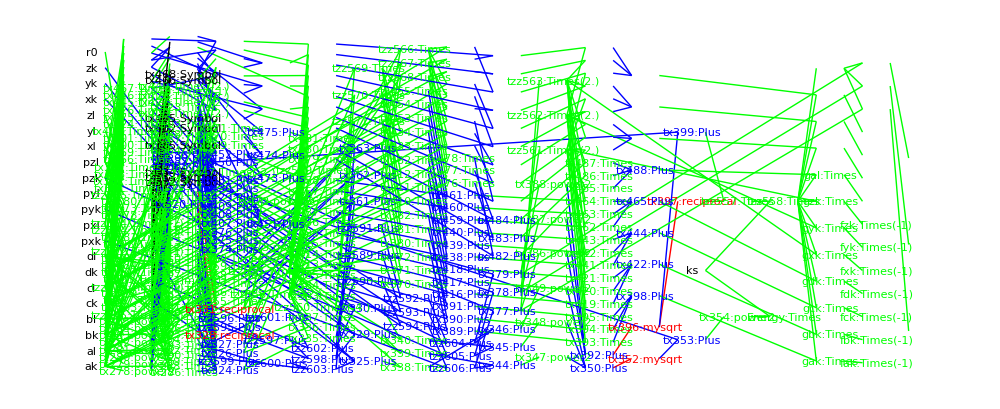

```mathematica
packGraph[staplePack]
```

```mathematica
staplePack[[4]]
```

Output→{Energy,fak,fbk,fck,fdk,fxk,fyk,fzk,fal,fbl,fcl,fdl,fxl,fyl,fzl}

# Nonbond rigid-body energy term

```mathematica
Clear[pm,pxm,pym,pzm];
Clear[pn,pxn,pyn,pzn];
Clear[evdw, eeel,nonbondRBEquation];
```

```mathematica
pm = { pxm,pym,pzm };
pn = { pxn,pyn,pzn };
```

```mathematica
plabm = quatmultrans[quat[am,bm,cm,dm],{xm,ym,zm},pm]
```

{pxm+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)+xm,pym+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)+ym,pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)+zm}

```mathematica
plabn = quatmultrans[quat[an,bn,cn,dn],{xn,yn,zn},pn]
```

{pxn+(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xn,pyn+(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+yn,pzn+(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zn}

```mathematica
nonbondRBDistance = Sqrt[(plabm-plabn).(plabm-plabn)]
```

√((pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn)^2+(pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn)^2+(pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn)^2)

```mathematica
evdwEquation = (dA/nonbondRBDistance^12-dC/nonbondRBDistance^6)
```

dA/(((pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn)^2+(pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn)^2+(pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn)^2)^6)-dC/(((pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn)^2+(pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn)^2+(pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn)^2)^3)

```mathematica
eeelEquation = (dQ1Q2/nonbondRBDistance)
```

dQ1Q2/(√((pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn)^2+(pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn)^2+(pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn)^2))

```mathematica
nonbondRBEnergyFn = evdwEquation + eeelEquation
```

dA/(((pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn)^2+(pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn)^2+(pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn)^2)^6)-dC/(((pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn)^2+(pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn)^2+(pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn)^2)^3)+dQ1Q2/(√((pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn)^2+(pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn)^2+(pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn)^2))

```mathematica
nonbondRBVarNames = { 
{am,a,I1,0},
{bm,b,I1,1},
{cm,c,I1,2},
{dm,d,I1,3},
{xm,x,I1,4},
{ym,y,I1,5},
{zm,z,I1,6},
{an,a,I2,0},
{bn,b,I2,1},
{cn,c,I2,2},
{dn,d,I2,3},
{xn,x,I2,4},
{yn,y,I2,5},
{zn,z,I2,6}
};
```

```mathematica
nonbondRBSetupRules = {};
AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(I1);"]];
AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(I2);"]];AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(dQ1Q2);"]];AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(dA);"]];
AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(dC);"]];
```

```mathematica
For[i=1,i≤Length[nonbondRBVarNames],i++,
str = "NONBONDRB_SET_POSITION("<>ToString[nonbondRBVarNames[[i]][[1]]]<>","<>ToString[nonbondRBVarNames[[i]][[3]]]<>","<>ToString[nonbondRBVarNames[[i]][[4]]]<>");";
(*Print[str];*)
AppendTo[nonbondRBSetupRules,CCode[str]];
];
```

```mathematica
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(pxm,ea1,getX());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(pym,ea1,getY());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(pzm,ea1,getZ());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(pxn,ea2,getX());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(pyn,ea2,getY());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(pzn,ea2,getZ());"]];
```

```mathematica
nonbondRBSetupRules//MatrixForm
```

(CCode[NONBONDRB_SET_PARAMETER(I1);]
CCode[NONBONDRB_SET_PARAMETER(I2);]
CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]
CCode[NONBONDRB_SET_PARAMETER(dA);]
CCode[NONBONDRB_SET_PARAMETER(dC);]
CCode[NONBONDRB_SET_POSITION(am,I1,0);]
CCode[NONBONDRB_SET_POSITION(bm,I1,1);]
CCode[NONBONDRB_SET_POSITION(cm,I1,2);]
CCode[NONBONDRB_SET_POSITION(dm,I1,3);]
CCode[NONBONDRB_SET_POSITION(xm,I1,4);]
CCode[NONBONDRB_SET_POSITION(ym,I1,5);]
CCode[NONBONDRB_SET_POSITION(zm,I1,6);]
CCode[NONBONDRB_SET_POSITION(an,I2,0);]
CCode[NONBONDRB_SET_POSITION(bn,I2,1);]
CCode[NONBONDRB_SET_POSITION(cn,I2,2);]
CCode[NONBONDRB_SET_POSITION(dn,I2,3);]
CCode[NONBONDRB_SET_POSITION(xn,I2,4);]
CCode[NONBONDRB_SET_POSITION(yn,I2,5);]
CCode[NONBONDRB_SET_POSITION(zn,I2,6);]
CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]
CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]
CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]
CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]
CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]
CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());])

```mathematica
nonbondRBEnergyRules = {};
nonbondRBOutputs = {};
AppendTo[nonbondRBEnergyRules,Assign[Energy,nonbondRBEnergyFn]];
AppendTo[nonbondRBEnergyRules,EnergyAccumulate["NONBONDRB",Energy]];
AppendTo[nonbondRBOutputs,Energy];
```

Position rules

```mathematica
nonbondPositionRBSetupRules = {};
AppendTo[nonbondPositionRBSetupRules,CCode["NONBOND_POSITION_RB_SET_PARAMETER(I1);"]];
```

```mathematica
For[i=1,i≤Length[nonbondRBVarNames]/2,i++,
str = "NONBOND_POSITION_RB_SET_POSITION("<>ToString[nonbondRBVarNames[[i]][[1]]]<>","<>ToString[nonbondRBVarNames[[i]][[3]]]<>","<>ToString[nonbondRBVarNames[[i]][[4]]]<>");";
(*Print[str];*)
AppendTo[nonbondPositionRBSetupRules,CCode[str]];
];
```

```mathematica
AppendTo[nonbondPositionRBSetupRules, CCode["NONBOND_POSITION_RB_SET_POINT(pxm,ea1,getX());"]];
AppendTo[nonbondPositionRBSetupRules, CCode["NONBOND_POSITION_RB_SET_POINT(pym,ea1,getY());"]];
AppendTo[nonbondPositionRBSetupRules, CCode["NONBOND_POSITION_RB_SET_POINT(pzm,ea1,getZ());"]];
```

```mathematica
plabm
```

{pxm+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)+xm,pym+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)+ym,pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)+zm}

```mathematica
nonbondPositionRules = {};
nonbondPositionOutputs = {};
AppendTo[nonbondPositionRules,Assign[plabmx,plabm[[1]]]];
AppendTo[nonbondPositionRules,Assign[plabmy,plabm[[2]]]];
AppendTo[nonbondPositionRules,Assign[plabmz,plabm[[3]]]];
AppendTo[nonbondPositionOutputs,plabmx];
AppendTo[nonbondPositionOutputs,plabmy];
AppendTo[nonbondPositionOutputs,plabmz];
```

```mathematica
nonbondPositionRules
```

{pxm+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)+xm→plabmx,pym+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)+ym→plabmy,pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)+zm→plabmz}

```mathematica
nonbondAllPositionRules = Flatten[{
nonbondPositionRBSetupRules,
nonbondPositionRules}];
```

```mathematica
nonbondPositionPack0 = {
Name->"NONBOND_POSITIONS",
AdditionalCDeclares->"",
DerivativeVariables->nonbondPositionInput,
Rules->nonbondAllPositionRules,
Input->nonbondPositionInput,
Output->nonbondPositionOutputs
};
```

```mathematica
packOptimize[nonbondPositionPack0]
```

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = True

TimesOptimize = True

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {plabmx, plabmy, plabmz}

There were no trivial rules

Collecting terms

Set::write: Tag Times in Null {Name→NONBOND_POSITIONS,AdditionalCDeclares→,DerivativeVariables→nonbondPositionInput,Rules→{CCode[NONBOND_POSITION_RB_SET_PARAMETER(I1);],CCode[NONBOND_POSITION_RB_SET_POSITION(am,I1,0);],CCode[NONBOND_POSITION_RB_SET_POSITION(bm,I1,1);],CCode[NONBOND_POSITION_RB_SET_POSITION(cm,I1,2);],CCode[NONBOND_POSITION_RB_SET_POSITION(dm,I1,3);],CCode[NONBOND_POSITION_RB_SET_POSITION(xm,I1,4);],CCode[NONBOND_POSITION_RB_SET_POSITION(ym,I1,5);],CCode[NONBOND_POSITION_RB_SET_POSITION(zm,I1,6);],CCode[NONBOND_POSITION_RB_SET_POINT(pxm,ea1,getX());],CCode[NONBOND_POSITION_RB_SET_POINT(pym,ea1,getY());],CCode[NONBOND_POSITION_RB_SET_POINT(pzm,ea1,getZ());],pxm+2. Power[«2»] Plus[«6»]+xm→plabmx,pym+2. Power[«2»] Plus[«6»]+ym→plabmy,pzm+2. Power[«2»] Plus[«6»]+zm→plabmz},Input→nonbondPositionInput,Output→{plabmx,plabmy,plabmz}} is Protected.

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {plabmx, plabmy, plabmz}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {plabmx, plabmy, plabmz}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {plabmx, plabmy, plabmz}

There were no trivial rules

trivialRules>> triv = {}

trivialRules>> outs = {plabmx, plabmy, plabmz}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {plabmx, plabmy, plabmz}

There were no trivial rules

trivialRules>> triv = {}

trivialRules>> outs = {plabmx, plabmy, plabmz}

There were no trivial rules

Writing declares to file: _NONBOND_POSITIONS_termDeclares.cc

Writing code to file: _NONBOND_POSITIONS_termCode.cc

{Name→NONBOND_POSITIONS,AdditionalCDeclares→,Input→nonbondPositionInput,Output→{plabmx,plabmy,plabmz},EnergyFunction→EnergyFunction,DerivativeVariables→nonbondPositionInput,Rules→{CCode[NONBOND_POSITION_RB_SET_PARAMETER(I1);],CCode[NONBOND_POSITION_RB_SET_POSITION(am,I1,0);],CCode[NONBOND_POSITION_RB_SET_POSITION(bm,I1,1);],CCode[NONBOND_POSITION_RB_SET_POSITION(cm,I1,2);],CCode[NONBOND_POSITION_RB_SET_POSITION(dm,I1,3);],CCode[NONBOND_POSITION_RB_SET_POSITION(xm,I1,4);],CCode[NONBOND_POSITION_RB_SET_POSITION(ym,I1,5);],CCode[NONBOND_POSITION_RB_SET_POSITION(zm,I1,6);],CCode[NONBOND_POSITION_RB_SET_POINT(pxm,ea1,getX());],CCode[NONBOND_POSITION_RB_SET_POINT(pym,ea1,getY());],CCode[NONBOND_POSITION_RB_SET_POINT(pzm,ea1,getZ());],power2[am]→tx31,power2[bm]→tx32,power2[cm]→tx33,power2[dm]→tx34,cm pym→tzz67,bm tzz67→tx35,-pym→tzz63,am dm tzz63→tx36,am cm→tzz68,pzm tzz68→tx37,dm pzm→tzz65,bm tzz65→tx38,-pxm→tzz64,tx33 tzz64→tx39,tx34 tzz64→tx40,tx31+tx32+tx33+tx34→tx41,tx35+tx36+tx37+tx38+tx39+tx40→tx42,reciprocal[tx41]→tx43,2. tx43→tzz61,tx42 tzz61→tx44,pxm+tx44+xm→plabmx,bm cm pxm→tx45,dm pxm→tzz66,am tzz66→tx46,-pzm→tzz62,am bm→tzz69,tzz62 tzz69→tx47,cm tzz65→tx48,tx32 tzz63→tx49,tx34 tzz63→tx50,tx45+tx46+tx47+tx48+tx49+tx50→tx51,tx51 tzz61→tx52,pym+tx52+ym→plabmy,tzz64 tzz68→tx53,bm tzz66→tx54,pym tzz69→tx55,dm tzz67→tx56,tx32 tzz62→tx57,tx33 tzz62→tx58,tx53+tx54+tx55+tx56+tx57+tx58→tx59,tx59 tzz61→tx60,pzm+tx60+zm→plabmz},HessianStructure→HessianStructure,CCode→NOT USED,MathCode→Block[{plabmx,plabmy,plabmz,tx31,tx32,tx33,tx34,tx35,tx36,tx37,tx38,tx39,tx40,tx41,tx42,tx43,tx44,tx45,tx46,tx47,tx48,tx49,tx50,tx51,tx52,tx53,tx54,tx55,tx56,tx57,tx58,tx59,tx60,tzz61,tzz62,tzz63,tzz64,tzz65,tzz66,tzz67,tzz68,tzz69,xxxDummy},
	(*NONBOND_POSITION_RB_SET_PARAMETER(I1);*)
	(*NONBOND_POSITION_RB_SET_POSITION(am,I1,0);*)
	(*NONBOND_POSITION_RB_SET_POSITION(bm,I1,1);*)
	(*NONBOND_POSITION_RB_SET_POSITION(cm,I1,2);*)
	(*NONBOND_POSITION_RB_SET_POSITION(dm,I1,3);*)
	(*NONBOND_POSITION_RB_SET_POSITION(xm,I1,4);*)
	(*NONBOND_POSITION_RB_SET_POSITION(ym,I1,5);*)
	(*NONBOND_POSITION_RB_SET_POSITION(zm,I1,6);*)
	(*NONBOND_POSITION_RB_SET_POINT(pxm,ea1,getX());*)
	(*NONBOND_POSITION_RB_SET_POINT(pym,ea1,getY());*)
	(*NONBOND_POSITION_RB_SET_POINT(pzm,ea1,getZ());*)
	tx31= mathPower2[am]; (*Rule 12*)
	tx32= mathPower2[bm]; (*Rule 13*)
	tx33= mathPower2[cm]; (*Rule 14*)
	tx34= mathPower2[dm]; (*Rule 15*)
	tzz67=cm pym; (*Rule 16*)
	tx35=bm tzz67; (*Rule 17*)
	tzz63=-pym; (*Rule 18*)
	tx36=am dm tzz63; (*Rule 19*)
	tzz68=am cm; (*Rule 20*)
	tx37=pzm tzz68; (*Rule 21*)
	tzz65=dm pzm; (*Rule 22*)
	tx38=bm tzz65; (*Rule 23*)
	tzz64=-pxm; (*Rule 24*)
	tx39=tx33 tzz64; (*Rule 25*)
	tx40=tx34 tzz64; (*Rule 26*)
	tx41=tx31 + tx32 + tx33 + tx34; (*Rule 27*)
	tx42=tx35 + tx36 + tx37 + tx38 + tx39 + tx40; (*Rule 28*)
	tx43= mathReciprocal[tx41]; (*Rule 29*)
	tzz61=2. tx43; (*Rule 30*)
	tx44=tx42 tzz61; (*Rule 31*)
	plabmx=pxm + tx44 + xm; (*Rule 32*)
	tx45=bm cm pxm; (*Rule 33*)
	tzz66=dm pxm; (*Rule 34*)
	tx46=am tzz66; (*Rule 35*)
	tzz62=-pzm; (*Rule 36*)
	tzz69=am bm; (*Rule 37*)
	tx47=tzz62 tzz69; (*Rule 38*)
	tx48=cm tzz65; (*Rule 39*)
	tx49=tx32 tzz63; (*Rule 40*)
	tx50=tx34 tzz63; (*Rule 41*)
	tx51=tx45 + tx46 + tx47 + tx48 + tx49 + tx50; (*Rule 42*)
	tx52=tx51 tzz61; (*Rule 43*)
	plabmy=pym + tx52 + ym; (*Rule 44*)
	tx53=tzz64 tzz68; (*Rule 45*)
	tx54=bm tzz66; (*Rule 46*)
	tx55=pym tzz69; (*Rule 47*)
	tx56=dm tzz67; (*Rule 48*)
	tx57=tx32 tzz62; (*Rule 49*)
	tx58=tx33 tzz62; (*Rule 50*)
	tx59=tx53 + tx54 + tx55 + tx56 + tx57 + tx58; (*Rule 51*)
	tx60=tx59 tzz61; (*Rule 52*)
	plabmz=pzm + tx60 + zm; (*Rule 53*)
{plabmx, plabmy, plabmz}]
}

## Append the Gradient rules

```mathematica
nonbondRBForceRules = {};
```

```mathematica
AppendGradientForceIfCalcForce["NONBONDRB",nonbondRBEnergyRules,nonbondRBOutputs,nonbondRBEnergyFn,nonbondRBVarNames];
```

```mathematica
nonbondRBOutputs
```

{Energy,fam,fbm,fcm,fdm,fxm,fym,fzm,fan,fbn,fcn,fdn,fxn,fyn,fzn}

### Collect terms and convert to C code

```mathematica
nonbondRBAllRules ={
nonbondRBSetupRules,
nonbondRBEnergyRules};
```

```mathematica
nonbondRBRules = Flatten[nonbondRBAllRules];
```

```mathematica
nonbondRBRules
```

{CCode[NONBONDRB_SET_PARAMETER(I1);],CCode[NONBONDRB_SET_PARAMETER(I2);],CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);],CCode[NONBONDRB_SET_PARAMETER(dA);],CCode[NONBONDRB_SET_PARAMETER(dC);],64,-gzn→fzn,CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );],CCode[} /*calcForce */],CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]}
 |  |  |  |

```mathematica
nonbondRBInput = { ak,bk,ck,dk,xk,yk,zk, al,bl,cl,dl,xl,yl,zl };
```

```mathematica
AppendTo[nonbondRBOutputs,nonbondRBDeviation];
```

### Assemble the rules, the name of the energy term, the independant variable names, etc. into what passes for a structure in Mathematica (I call it a Pack)

```mathematica
nonbondRBPack0 = {
Name->"NONBONDRB",
AdditionalCDeclares->"",
DerivativeVariables->{ ak,bk,ck,dk,xk,yk,zk, al,bl,cl,dl,xl,yl,zl },
Rules->nonbondRBRules,
Input->nonbondRBInput,
Output->nonbondRBOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[nonbondRBPack0];
```

Writing finite difference debug code to: _NONBONDRB_debugFiniteDifference.cc

Writing debug variable declares to: _NONBONDRB_debugEvalDeclares.cc

Writing xml output debug code to: _NONBONDRB_debugEvalSerialize.cc

Writing set variables debug code to: _NONBONDRB_debugEvalSet.cc

### Put the pedal to the metal and generate "C" code.

```mathematica
nonbondRBPack = packOptimize[nonbondRBPack0];
```

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {tx655 -> tx645, tx441 -> tx651}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: tx655 -> tx645

tx441 -> tx651

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]

CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]

CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]

CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]

CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]

CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]

power2[am] -> tx322

power2[an] -> tx323

power2[bm] -> tx324

power2[bn] -> tx325

power2[cm] -> tx326

power2[cn] -> tx327

power2[dm] -> tx328

power2[dn] -> tx329

-(am cm pxm) -> tx330

bm cm pxm -> tx331

am dm pxm -> tx332

bm dm pxm -> tx333

-(an cn pxn) -> tx334

bn cn pxn -> tx335

an dn pxn -> tx336

bn dn pxn -> tx337

am bm pym -> tx338

bm cm pym -> tx339

-(am dm pym) -> tx340

cm dm pym -> tx341

an bn pyn -> tx342

bn cn pyn -> tx343

-(an dn pyn) -> tx344

cn dn pyn -> tx345

-(am bm pzm) -> tx346

am cm pzm -> tx347

bm dm pzm -> tx348

cm dm pzm -> tx349

-(an bn pzn) -> tx350

an cn pzn -> tx351

bn dn pzn -> tx352

cn dn pzn -> tx353

-(pym tx324) -> tx354

-(pzm tx324) -> tx355

-(pyn tx325) -> tx356

-(pzn tx325) -> tx357

-(pxm tx326) -> tx358

-(pzm tx326) -> tx359

-(pxn tx327) -> tx360

-(pzn tx327) -> tx361

-(pxm tx328) -> tx362

-(pym tx328) -> tx363

tx322 + tx324 + tx326 + tx328 -> tx364

-(pxn tx329) -> tx365

-(pyn tx329) -> tx366

tx323 + tx325 + tx327 + tx329 -> tx367

tx330 + tx333 + tx338 + tx341 + tx355 + tx359 -> tx368

tx334 + tx337 + tx342 + tx345 + tx357 + tx361 -> tx369

tx339 + tx340 + tx347 + tx348 + tx358 + tx362 -> tx370

tx331 + tx332 + tx346 + tx349 + tx354 + tx363 -> tx371

reciprocal[tx364] -> tx372

tx343 + tx344 + tx351 + tx352 + tx360 + tx365 -> tx373

tx335 + tx336 + tx350 + tx353 + tx356 + tx366 -> tx374

reciprocal[tx367] -> tx375

-pxn -> tx376

-pyn -> tx377

-pzn -> tx378

2. tx368 tx372 -> tx379

2. tx370 tx372 -> tx380

2. tx371 tx372 -> tx381

-2. tx369 tx375 -> tx382

-2. tx373 tx375 -> tx383

-2. tx374 tx375 -> tx384

-xn -> tx385

-yn -> tx386

-zn -> tx387

pxm + tx376 + tx380 + tx383 + tx385 + xm -> tx388

pym + tx377 + tx381 + tx384 + tx386 + ym -> tx389

pzm + tx378 + tx379 + tx382 + tx387 + zm -> tx390

power2[tx388] -> tx391

power2[tx389] -> tx392

power2[tx390] -> tx393

tx391 + tx392 + tx393 -> tx394

powern2[tx394] -> tx654

reciprocal[tx394] -> tx655

tx654 tx655 -> tx643

power2[tx643] -> tx395

power2[tx655] -> tx644

tx655 -> tx645

tx644 tx645 -> tx396

mysqrt[tx394] -> tx646

reciprocal[tx646] -> tx397

dA tx395 -> tx398

-(dC tx396) -> tx399

dQ1Q2 tx397 -> tx400

tx398 + tx399 + tx400 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef NONBONDRB_CALC_FORCE //[]

CCode[if ( calcForce ) {]

tx327 tx376 -> tx401

tx329 tx376 -> tx402

tx325 tx377 -> tx403

tx329 tx377 -> tx404

tx325 tx378 -> tx405

tx327 tx378 -> tx406

-(cm pxm) -> tx407

dm pxm -> tx408

bm pym -> tx409

-(dm pym) -> tx410

-(bm pzm) -> tx411

cm pzm -> tx412

tx343 + tx344 + tx351 + tx352 + tx401 + tx402 -> tx413

tx335 + tx336 + tx350 + tx353 + tx403 + tx404 -> tx414

tx334 + tx337 + tx342 + tx345 + tx405 + tx406 -> tx415

power2[tx372] -> tx416

tx407 + tx409 -> tx417

tx408 + tx411 -> tx418

tx410 + tx412 -> tx419

-2. tx375 tx413 -> tx420

-2. tx375 tx414 -> tx421

-2. tx375 tx415 -> tx422

-4. am tx368 tx416 -> tx423

-4. am tx370 tx416 -> tx424

-4. am tx371 tx416 -> tx425

2. tx372 tx417 -> tx426

2. tx372 tx418 -> tx427

2. tx372 tx419 -> tx428

pxm + tx376 + tx380 + tx385 + tx420 + xm -> tx429

pym + tx377 + tx381 + tx386 + tx421 + ym -> tx430

pzm + tx378 + tx379 + tx387 + tx422 + zm -> tx431

tx423 + tx426 -> tx432

tx425 + tx427 -> tx433

tx424 + tx428 -> tx434

power2[tx429] -> tx435

power2[tx430] -> tx436

power2[tx431] -> tx437

2. tx431 tx432 -> tx438

2. tx430 tx433 -> tx439

2. tx429 tx434 -> tx440

tx435 + tx436 + tx437 -> tx441

tx438 + tx439 + tx440 -> tx442

powern2[tx441] -> tx656

reciprocal[tx441] -> tx657

tx656 tx657 -> tx647

power2[tx656] -> tx648

tx647 tx648 -> tx443

power2[tx657] -> tx649

power2[tx649] -> tx444

mysqrt[tx441] -> tx650

tx441 -> tx651

reciprocal[tx650] -> tx652

reciprocal[tx651] -> tx653

tx652 tx653 -> tx445

-6. dA tx442 tx443 -> tx446

3 dC tx442 tx444 -> tx447

-0.5 dQ1Q2 tx442 tx445 -> tx448

tx446 + tx447 + tx448 -> gam

-gam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

cm pxm -> tx449

am pym -> tx450

cm pym -> tx451

-(am pzm) -> tx452

-2. bm pzm -> tx453

dm pzm -> tx454

-2. tx409 -> tx455

tx408 + tx450 + tx453 -> tx456

tx451 + tx454 -> tx457

tx449 + tx452 + tx455 -> tx458

-4. bm tx368 tx416 -> tx459

-4. bm tx370 tx416 -> tx460

-4. bm tx371 tx416 -> tx461

2. tx372 tx456 -> tx462

2. tx372 tx457 -> tx463

2. tx372 tx458 -> tx464

tx459 + tx462 -> tx465

tx460 + tx463 -> tx466

tx461 + tx464 -> tx467

2. tx431 tx465 -> tx468

2. tx429 tx466 -> tx469

2. tx430 tx467 -> tx470

tx468 + tx469 + tx470 -> tx471

-6. dA tx443 tx471 -> tx472

3 dC tx444 tx471 -> tx473

-0.5 dQ1Q2 tx445 tx471 -> tx474

tx472 + tx473 + tx474 -> gbm

-gbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

-(am pxm) -> tx475

bm pxm -> tx476

dm pym -> tx477

am pzm -> tx478

-2. tx412 -> tx479

-2. tx449 -> tx480

tx454 + tx476 -> tx481

tx475 + tx477 + tx479 -> tx482

tx409 + tx478 + tx480 -> tx483

-4. cm tx368 tx416 -> tx484

-4. cm tx370 tx416 -> tx485

-4. cm tx371 tx416 -> tx486

2. tx372 tx481 -> tx487

2. tx372 tx482 -> tx488

2. tx372 tx483 -> tx489

tx486 + tx487 -> tx490

tx484 + tx488 -> tx491

tx485 + tx489 -> tx492

2. tx430 tx490 -> tx493

2. tx431 tx491 -> tx494

2. tx429 tx492 -> tx495

tx493 + tx494 + tx495 -> tx496

-6. dA tx443 tx496 -> tx497

3 dC tx444 tx496 -> tx498

-0.5 dQ1Q2 tx445 tx496 -> tx499

tx497 + tx498 + tx499 -> gcm

-gcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

am pxm -> tx500

bm pzm -> tx501

-2. tx408 -> tx502

-tx450 -> tx503

-2. tx477 -> tx504

tx451 + tx476 -> tx505

tx501 + tx502 + tx503 -> tx506

tx412 + tx500 + tx504 -> tx507

-4. dm tx368 tx416 -> tx508

-4. dm tx370 tx416 -> tx509

-4. dm tx371 tx416 -> tx510

2. tx372 tx505 -> tx511

2. tx372 tx506 -> tx512

2. tx372 tx507 -> tx513

tx508 + tx511 -> tx514

tx509 + tx512 -> tx515

tx510 + tx513 -> tx516

2. tx431 tx514 -> tx517

2. tx429 tx515 -> tx518

2. tx430 tx516 -> tx519

tx517 + tx518 + tx519 -> tx520

-6. dA tx443 tx520 -> tx521

3 dC tx444 tx520 -> tx522

-0.5 dQ1Q2 tx445 tx520 -> tx523

tx521 + tx522 + tx523 -> gdm

-gdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

-12. dA tx429 tx443 -> tx524

6. dC tx429 tx444 -> tx525

-(dQ1Q2 tx429 tx445) -> tx526

tx524 + tx525 + tx526 -> gxm

-gxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

-12. dA tx430 tx443 -> tx527

6. dC tx430 tx444 -> tx528

-(dQ1Q2 tx430 tx445) -> tx529

tx527 + tx528 + tx529 -> gym

-gym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

-12. dA tx431 tx443 -> tx530

6. dC tx431 tx444 -> tx531

-(dQ1Q2 tx431 tx445) -> tx532

tx530 + tx531 + tx532 -> gzm

-gzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

dn pxn -> tx533

bn pyn -> tx534

cn pzn -> tx535

cn tx376 -> tx536

dn tx377 -> tx537

bn tx378 -> tx538

power2[tx375] -> tx539

tx534 + tx536 -> tx540

tx535 + tx537 -> tx541

tx533 + tx538 -> tx542

4. an tx413 tx539 -> tx543

4. an tx414 tx539 -> tx544

4. an tx415 tx539 -> tx545

-2. tx375 tx540 -> tx546

-2. tx375 tx541 -> tx547

-2. tx375 tx542 -> tx548

tx545 + tx546 -> tx549

tx543 + tx547 -> tx550

tx544 + tx548 -> tx551

2. tx431 tx549 -> tx552

2. tx429 tx550 -> tx553

2. tx430 tx551 -> tx554

tx552 + tx553 + tx554 -> tx555

-6. dA tx443 tx555 -> tx556

3 dC tx444 tx555 -> tx557

-0.5 dQ1Q2 tx445 tx555 -> tx558

tx556 + tx557 + tx558 -> gan

-gan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

cn pxn -> tx559

an pyn -> tx560

cn pyn -> tx561

-2. bn pzn -> tx562

dn pzn -> tx563

an tx378 -> tx564

-2. tx534 -> tx565

tx533 + tx560 + tx562 -> tx566

tx561 + tx563 -> tx567

tx559 + tx564 + tx565 -> tx568

4. bn tx413 tx539 -> tx569

4. bn tx414 tx539 -> tx570

4. bn tx415 tx539 -> tx571

-2. tx375 tx566 -> tx572

-2. tx375 tx567 -> tx573

-2. tx375 tx568 -> tx574

tx571 + tx572 -> tx575

tx569 + tx573 -> tx576

tx570 + tx574 -> tx577

2. tx431 tx575 -> tx578

2. tx429 tx576 -> tx579

2. tx430 tx577 -> tx580

tx578 + tx579 + tx580 -> tx581

-6. dA tx443 tx581 -> tx582

3 dC tx444 tx581 -> tx583

-0.5 dQ1Q2 tx445 tx581 -> tx584

tx582 + tx583 + tx584 -> gbn

-gbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

bn pxn -> tx585

dn pyn -> tx586

an pzn -> tx587

an tx376 -> tx588

-2. tx535 -> tx589

-2. tx559 -> tx590

tx563 + tx585 -> tx591

tx586 + tx588 + tx589 -> tx592

tx534 + tx587 + tx590 -> tx593

4. cn tx413 tx539 -> tx594

4. cn tx414 tx539 -> tx595

4. cn tx415 tx539 -> tx596

-2. tx375 tx591 -> tx597

-2. tx375 tx592 -> tx598

-2. tx375 tx593 -> tx599

tx595 + tx597 -> tx600

tx596 + tx598 -> tx601

tx594 + tx599 -> tx602

2. tx430 tx600 -> tx603

2. tx431 tx601 -> tx604

2. tx429 tx602 -> tx605

tx603 + tx604 + tx605 -> tx606

-6. dA tx443 tx606 -> tx607

3 dC tx444 tx606 -> tx608

-0.5 dQ1Q2 tx445 tx606 -> tx609

tx607 + tx608 + tx609 -> gcn

-gcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

an pxn -> tx610

bn pzn -> tx611

an tx377 -> tx612

-2. tx533 -> tx613

-2. tx586 -> tx614

tx561 + tx585 -> tx615

tx611 + tx612 + tx613 -> tx616

tx535 + tx610 + tx614 -> tx617

4. dn tx413 tx539 -> tx618

4. dn tx414 tx539 -> tx619

4. dn tx415 tx539 -> tx620

-2. tx375 tx615 -> tx621

-2. tx375 tx616 -> tx622

-2. tx375 tx617 -> tx623

tx620 + tx621 -> tx624

tx618 + tx622 -> tx625

tx619 + tx623 -> tx626

2. tx431 tx624 -> tx627

2. tx429 tx625 -> tx628

2. tx430 tx626 -> tx629

tx627 + tx628 + tx629 -> tx630

-6. dA tx443 tx630 -> tx631

3 dC tx444 tx630 -> tx632

-0.5 dQ1Q2 tx445 tx630 -> tx633

tx631 + tx632 + tx633 -> gdn

-gdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

12. dA tx429 tx443 -> tx634

-6. dC tx429 tx444 -> tx635

dQ1Q2 tx429 tx445 -> tx636

tx634 + tx635 + tx636 -> gxn

-gxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

12. dA tx430 tx443 -> tx637

-6. dC tx430 tx444 -> tx638

dQ1Q2 tx430 tx445 -> tx639

tx637 + tx638 + tx639 -> gyn

-gyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

12. dA tx431 tx443 -> tx640

-6. dC tx431 tx444 -> tx641

dQ1Q2 tx431 tx445 -> tx642

tx640 + tx641 + tx642 -> gzn

-gzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

CCode[} /*calcForce */]

CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

trivialRules>> triv = {tzz685 -> tx376, tzz684 -> tx377, tzz696 -> tx378, tx655 -> tx645, tzz690 -> tx408, tx441 -> tx651, tzz693 -> tx451, tzz689 -> tx454, tzz688 -> tx533, tzz691 -> tx535, tzz692 -> tx561, tzz680 -> tx611}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: tzz685 -> tx376

tzz684 -> tx377

tzz696 -> tx378

tx655 -> tx645

tzz690 -> tx408

tx441 -> tx651

tzz693 -> tx451

tzz689 -> tx454

tzz688 -> tx533

tzz691 -> tx535

tzz692 -> tx561

tzz680 -> tx611

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]

CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]

CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]

CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]

CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]

CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]

power2[am] -> tx322

power2[an] -> tx323

power2[bm] -> tx324

power2[bn] -> tx325

power2[cm] -> tx326

power2[cn] -> tx327

power2[dm] -> tx328

power2[dn] -> tx329

-pxm -> tzz672

am cm -> tzz694

tzz672 tzz694 -> tx330

bm cm pxm -> tx331

dm pxm -> tzz690

am tzz690 -> tx332

bm tzz690 -> tx333

-pxn -> tzz685

an cn tzz685 -> tx334

bn cn pxn -> tx335

dn pxn -> tzz688

an tzz688 -> tx336

bn tzz688 -> tx337

am bm -> tzz695

pym tzz695 -> tx338

cm pym -> tzz693

bm tzz693 -> tx339

-pym -> tzz679

am dm tzz679 -> tx340

dm tzz693 -> tx341

an bn pyn -> tx342

cn pyn -> tzz692

bn tzz692 -> tx343

-pyn -> tzz684

an dn tzz684 -> tx344

dn tzz692 -> tx345

-pzm -> tzz671

tzz671 tzz695 -> tx346

pzm tzz694 -> tx347

dm pzm -> tzz689

bm tzz689 -> tx348

cm tzz689 -> tx349

bn pzn -> tzz680

-(an tzz680) -> tx350

cn pzn -> tzz691

an tzz691 -> tx351

dn tzz680 -> tx352

dn tzz691 -> tx353

tx324 tzz679 -> tx354

tx324 tzz671 -> tx355

tx325 tzz684 -> tx356

-pzn -> tzz696

tx325 tzz696 -> tx357

tx326 tzz672 -> tx358

tx326 tzz671 -> tx359

tx327 tzz685 -> tx360

tx327 tzz696 -> tx361

tx328 tzz672 -> tx362

tx328 tzz679 -> tx363

tx322 + tx324 + tx326 + tx328 -> tx364

tx329 tzz685 -> tx365

tx329 tzz684 -> tx366

tx323 + tx325 + tx327 + tx329 -> tx367

tx330 + tx333 + tx338 + tx341 + tx355 + tx359 -> tx368

tx334 + tx337 + tx342 + tx345 + tx357 + tx361 -> tx369

tx339 + tx340 + tx347 + tx348 + tx358 + tx362 -> tx370

tx331 + tx332 + tx346 + tx349 + tx354 + tx363 -> tx371

reciprocal[tx364] -> tx372

tx343 + tx344 + tx351 + tx352 + tx360 + tx365 -> tx373

tx335 + tx336 + tx350 + tx353 + tx356 + tx366 -> tx374

reciprocal[tx367] -> tx375

tzz685 -> tx376

tzz684 -> tx377

tzz696 -> tx378

2. tx372 -> tzz659

tx368 tzz659 -> tx379

tx370 tzz659 -> tx380

tx371 tzz659 -> tx381

-2. tx375 -> tzz658

tx369 tzz658 -> tx382

tx373 tzz658 -> tx383

tx374 tzz658 -> tx384

-xn -> tx385

-yn -> tx386

-zn -> tx387

pxm + tx376 + tx380 + tx383 + tx385 + xm -> tx388

pym + tx377 + tx381 + tx384 + tx386 + ym -> tx389

pzm + tx378 + tx379 + tx382 + tx387 + zm -> tx390

power2[tx388] -> tx391

power2[tx389] -> tx392

power2[tx390] -> tx393

tx391 + tx392 + tx393 -> tx394

power2[reciprocal[tx394]] -> tx654

reciprocal[tx394] -> tx655

tx654 tx655 -> tx643

power2[tx643] -> tx395

power2[tx655] -> tx644

tx655 -> tx645

tx644 tx645 -> tx396

mysqrt[tx394] -> tx646

reciprocal[tx646] -> tx397

dA tx395 -> tx398

-(dC tx396) -> tx399

dQ1Q2 tx397 -> tx400

tx398 + tx399 + tx400 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef NONBONDRB_CALC_FORCE //[]

CCode[if ( calcForce ) {]

tx327 tx376 -> tx401

tx329 tx376 -> tx402

tx325 tx377 -> tx403

tx329 tx377 -> tx404

tx325 tx378 -> tx405

tx327 tx378 -> tx406

cm tzz672 -> tx407

tzz690 -> tx408

bm pym -> tx409

dm tzz679 -> tx410

bm tzz671 -> tx411

cm pzm -> tx412

tx343 + tx344 + tx351 + tx352 + tx401 + tx402 -> tx413

tx335 + tx336 + tx350 + tx353 + tx403 + tx404 -> tx414

tx334 + tx337 + tx342 + tx345 + tx405 + tx406 -> tx415

power2[tx372] -> tx416

tx407 + tx409 -> tx417

tx408 + tx411 -> tx418

tx410 + tx412 -> tx419

tx413 tzz658 -> tx420

tx414 tzz658 -> tx421

tx415 tzz658 -> tx422

-4. tx416 -> tzz664

tx368 tzz664 -> tzz678

am tzz678 -> tx423

tx370 tzz664 -> tzz677

am tzz677 -> tx424

tx371 tzz664 -> tzz676

am tzz676 -> tx425

tx417 tzz659 -> tx426

tx418 tzz659 -> tx427

tx419 tzz659 -> tx428

pxm + tx376 + tx380 + tx385 + tx420 + xm -> tx429

pym + tx377 + tx381 + tx386 + tx421 + ym -> tx430

pzm + tx378 + tx379 + tx387 + tx422 + zm -> tx431

tx423 + tx426 -> tx432

tx425 + tx427 -> tx433

tx424 + tx428 -> tx434

power2[tx429] -> tx435

power2[tx430] -> tx436

power2[tx431] -> tx437

2. tx431 -> tzz666

tx432 tzz666 -> tx438

2. tx430 -> tzz667

tx433 tzz667 -> tx439

2. tx429 -> tzz668

tx434 tzz668 -> tx440

tx435 + tx436 + tx437 -> tx441

tx438 + tx439 + tx440 -> tx442

power2[reciprocal[tx441]] -> tx656

reciprocal[tx441] -> tx657

tx656 tx657 -> tx647

power2[tx656] -> tx648

tx647 tx648 -> tx443

power2[tx657] -> tx649

power2[tx649] -> tx444

mysqrt[tx441] -> tx650

tx441 -> tx651

reciprocal[tx650] -> tx652

reciprocal[tx651] -> tx653

tx652 tx653 -> tx445

dA tx443 -> tzz662

-6. tzz662 -> tzz670

tx442 tzz670 -> tx446

dC tx444 -> tzz661

3 tzz661 -> tzz665

tx442 tzz665 -> tx447

dQ1Q2 tx445 -> tzz660

-0.5 tzz660 -> tzz669

tx442 tzz669 -> tx448

tx446 + tx447 + tx448 -> gam

-gam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

cm pxm -> tx449

am pym -> tx450

tzz693 -> tx451

am tzz671 -> tx452

-2. bm pzm -> tx453

tzz689 -> tx454

-2. tx409 -> tx455

tx408 + tx450 + tx453 -> tx456

tx451 + tx454 -> tx457

tx449 + tx452 + tx455 -> tx458

bm tzz678 -> tx459

bm tzz677 -> tx460

bm tzz676 -> tx461

tx456 tzz659 -> tx462

tx457 tzz659 -> tx463

tx458 tzz659 -> tx464

tx459 + tx462 -> tx465

tx460 + tx463 -> tx466

tx461 + tx464 -> tx467

tx465 tzz666 -> tx468

tx466 tzz668 -> tx469

tx467 tzz667 -> tx470

tx468 + tx469 + tx470 -> tx471

tx471 tzz670 -> tx472

tx471 tzz665 -> tx473

tx471 tzz669 -> tx474

tx472 + tx473 + tx474 -> gbm

-gbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

am tzz672 -> tx475

bm pxm -> tx476

dm pym -> tx477

am pzm -> tx478

-2. tx412 -> tx479

-2. tx449 -> tx480

tx454 + tx476 -> tx481

tx475 + tx477 + tx479 -> tx482

tx409 + tx478 + tx480 -> tx483

cm tzz678 -> tx484

cm tzz677 -> tx485

cm tzz676 -> tx486

tx481 tzz659 -> tx487

tx482 tzz659 -> tx488

tx483 tzz659 -> tx489

tx486 + tx487 -> tx490

tx484 + tx488 -> tx491

tx485 + tx489 -> tx492

tx490 tzz667 -> tx493

tx491 tzz666 -> tx494

tx492 tzz668 -> tx495

tx493 + tx494 + tx495 -> tx496

tx496 tzz670 -> tx497

tx496 tzz665 -> tx498

tx496 tzz669 -> tx499

tx497 + tx498 + tx499 -> gcm

-gcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

am pxm -> tx500

bm pzm -> tx501

-2. tx408 -> tx502

-tx450 -> tx503

-2. tx477 -> tx504

tx451 + tx476 -> tx505

tx501 + tx502 + tx503 -> tx506

tx412 + tx500 + tx504 -> tx507

dm tzz678 -> tx508

dm tzz677 -> tx509

dm tzz676 -> tx510

tx505 tzz659 -> tx511

tx506 tzz659 -> tx512

tx507 tzz659 -> tx513

tx508 + tx511 -> tx514

tx509 + tx512 -> tx515

tx510 + tx513 -> tx516

tx514 tzz666 -> tx517

tx515 tzz668 -> tx518

tx516 tzz667 -> tx519

tx517 + tx518 + tx519 -> tx520

tx520 tzz670 -> tx521

tx520 tzz665 -> tx522

tx520 tzz669 -> tx523

tx521 + tx522 + tx523 -> gdm

-gdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

-12. tzz662 -> tzz687

tx429 tzz687 -> tx524

6. tzz661 -> tzz682

tx429 tzz682 -> tx525

-tzz660 -> tzz683

tx429 tzz683 -> tx526

tx524 + tx525 + tx526 -> gxm

-gxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

tx430 tzz687 -> tx527

tx430 tzz682 -> tx528

tx430 tzz683 -> tx529

tx527 + tx528 + tx529 -> gym

-gym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

tx431 tzz687 -> tx530

tx431 tzz682 -> tx531

tx431 tzz683 -> tx532

tx530 + tx531 + tx532 -> gzm

-gzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

tzz688 -> tx533

bn pyn -> tx534

tzz691 -> tx535

cn tx376 -> tx536

dn tx377 -> tx537

bn tx378 -> tx538

power2[tx375] -> tx539

tx534 + tx536 -> tx540

tx535 + tx537 -> tx541

tx533 + tx538 -> tx542

4. tx539 -> tzz663

tx413 tzz663 -> tzz675

an tzz675 -> tx543

tx414 tzz663 -> tzz674

an tzz674 -> tx544

tx415 tzz663 -> tzz673

an tzz673 -> tx545

tx540 tzz658 -> tx546

tx541 tzz658 -> tx547

tx542 tzz658 -> tx548

tx545 + tx546 -> tx549

tx543 + tx547 -> tx550

tx544 + tx548 -> tx551

tx549 tzz666 -> tx552

tx550 tzz668 -> tx553

tx551 tzz667 -> tx554

tx552 + tx553 + tx554 -> tx555

tx555 tzz670 -> tx556

tx555 tzz665 -> tx557

tx555 tzz669 -> tx558

tx556 + tx557 + tx558 -> gan

-gan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

cn pxn -> tx559

an pyn -> tx560

tzz692 -> tx561

-2. tzz680 -> tx562

dn pzn -> tx563

an tx378 -> tx564

-2. tx534 -> tx565

tx533 + tx560 + tx562 -> tx566

tx561 + tx563 -> tx567

tx559 + tx564 + tx565 -> tx568

bn tzz675 -> tx569

bn tzz674 -> tx570

bn tzz673 -> tx571

tx566 tzz658 -> tx572

tx567 tzz658 -> tx573

tx568 tzz658 -> tx574

tx571 + tx572 -> tx575

tx569 + tx573 -> tx576

tx570 + tx574 -> tx577

tx575 tzz666 -> tx578

tx576 tzz668 -> tx579

tx577 tzz667 -> tx580

tx578 + tx579 + tx580 -> tx581

tx581 tzz670 -> tx582

tx581 tzz665 -> tx583

tx581 tzz669 -> tx584

tx582 + tx583 + tx584 -> gbn

-gbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

bn pxn -> tx585

dn pyn -> tx586

an pzn -> tx587

an tx376 -> tx588

-2. tx535 -> tx589

-2. tx559 -> tx590

tx563 + tx585 -> tx591

tx586 + tx588 + tx589 -> tx592

tx534 + tx587 + tx590 -> tx593

cn tzz675 -> tx594

cn tzz674 -> tx595

cn tzz673 -> tx596

tx591 tzz658 -> tx597

tx592 tzz658 -> tx598

tx593 tzz658 -> tx599

tx595 + tx597 -> tx600

tx596 + tx598 -> tx601

tx594 + tx599 -> tx602

tx600 tzz667 -> tx603

tx601 tzz666 -> tx604

tx602 tzz668 -> tx605

tx603 + tx604 + tx605 -> tx606

tx606 tzz670 -> tx607

tx606 tzz665 -> tx608

tx606 tzz669 -> tx609

tx607 + tx608 + tx609 -> gcn

-gcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

an pxn -> tx610

tzz680 -> tx611

an tx377 -> tx612

-2. tx533 -> tx613

-2. tx586 -> tx614

tx561 + tx585 -> tx615

tx611 + tx612 + tx613 -> tx616

tx535 + tx610 + tx614 -> tx617

dn tzz675 -> tx618

dn tzz674 -> tx619

dn tzz673 -> tx620

tx615 tzz658 -> tx621

tx616 tzz658 -> tx622

tx617 tzz658 -> tx623

tx620 + tx621 -> tx624

tx618 + tx622 -> tx625

tx619 + tx623 -> tx626

tx624 tzz666 -> tx627

tx625 tzz668 -> tx628

tx626 tzz667 -> tx629

tx627 + tx628 + tx629 -> tx630

tx630 tzz670 -> tx631

tx630 tzz665 -> tx632

tx630 tzz669 -> tx633

tx631 + tx632 + tx633 -> gdn

-gdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

12. tzz662 -> tzz681

tx429 tzz681 -> tx634

-6. tzz661 -> tzz686

tx429 tzz686 -> tx635

tx429 tzz660 -> tx636

tx634 + tx635 + tx636 -> gxn

-gxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

tx430 tzz681 -> tx637

tx430 tzz686 -> tx638

tx430 tzz660 -> tx639

tx637 + tx638 + tx639 -> gyn

-gyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

tx431 tzz681 -> tx640

tx431 tzz686 -> tx641

tx431 tzz660 -> tx642

tx640 + tx641 + tx642 -> gzn

-gzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

CCode[} /*calcForce */]

CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

eliminateTrivialRules

trivialRules>> triv = {tzz685 -> tx376, tzz684 -> tx377, tzz696 -> tx378, tx697 -> tx655, tx655 -> tx645, tzz690 -> tx408, tx698 -> tx657, tx441 -> tx651, tzz693 -> tx451, tzz689 -> tx454, tzz688 -> tx533, tzz691 -> tx535, tzz692 -> tx561, tzz680 -> tx611}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: tzz685 -> tx376

tzz684 -> tx377

tzz696 -> tx378

tx697 -> tx655

tx655 -> tx645

tzz690 -> tx408

tx698 -> tx657

tx441 -> tx651

tzz693 -> tx451

tzz689 -> tx454

tzz688 -> tx533

tzz691 -> tx535

tzz692 -> tx561

tzz680 -> tx611

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]

CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]

CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]

CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]

CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]

CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]

power2[am] -> tx322

power2[an] -> tx323

power2[bm] -> tx324

power2[bn] -> tx325

power2[cm] -> tx326

power2[cn] -> tx327

power2[dm] -> tx328

power2[dn] -> tx329

-pxm -> tzz672

am cm -> tzz694

tzz672 tzz694 -> tx330

bm cm pxm -> tx331

dm pxm -> tzz690

am tzz690 -> tx332

bm tzz690 -> tx333

-pxn -> tzz685

an cn tzz685 -> tx334

bn cn pxn -> tx335

dn pxn -> tzz688

an tzz688 -> tx336

bn tzz688 -> tx337

am bm -> tzz695

pym tzz695 -> tx338

cm pym -> tzz693

bm tzz693 -> tx339

-pym -> tzz679

am dm tzz679 -> tx340

dm tzz693 -> tx341

an bn pyn -> tx342

cn pyn -> tzz692

bn tzz692 -> tx343

-pyn -> tzz684

an dn tzz684 -> tx344

dn tzz692 -> tx345

-pzm -> tzz671

tzz671 tzz695 -> tx346

pzm tzz694 -> tx347

dm pzm -> tzz689

bm tzz689 -> tx348

cm tzz689 -> tx349

bn pzn -> tzz680

-(an tzz680) -> tx350

cn pzn -> tzz691

an tzz691 -> tx351

dn tzz680 -> tx352

dn tzz691 -> tx353

tx324 tzz679 -> tx354

tx324 tzz671 -> tx355

tx325 tzz684 -> tx356

-pzn -> tzz696

tx325 tzz696 -> tx357

tx326 tzz672 -> tx358

tx326 tzz671 -> tx359

tx327 tzz685 -> tx360

tx327 tzz696 -> tx361

tx328 tzz672 -> tx362

tx328 tzz679 -> tx363

tx322 + tx324 + tx326 + tx328 -> tx364

tx329 tzz685 -> tx365

tx329 tzz684 -> tx366

tx323 + tx325 + tx327 + tx329 -> tx367

tx330 + tx333 + tx338 + tx341 + tx355 + tx359 -> tx368

tx334 + tx337 + tx342 + tx345 + tx357 + tx361 -> tx369

tx339 + tx340 + tx347 + tx348 + tx358 + tx362 -> tx370

tx331 + tx332 + tx346 + tx349 + tx354 + tx363 -> tx371

reciprocal[tx364] -> tx372

tx343 + tx344 + tx351 + tx352 + tx360 + tx365 -> tx373

tx335 + tx336 + tx350 + tx353 + tx356 + tx366 -> tx374

reciprocal[tx367] -> tx375

tzz685 -> tx376

tzz684 -> tx377

tzz696 -> tx378

2. tx372 -> tzz659

tx368 tzz659 -> tx379

tx370 tzz659 -> tx380

tx371 tzz659 -> tx381

-2. tx375 -> tzz658

tx369 tzz658 -> tx382

tx373 tzz658 -> tx383

tx374 tzz658 -> tx384

-xn -> tx385

-yn -> tx386

-zn -> tx387

pxm + tx376 + tx380 + tx383 + tx385 + xm -> tx388

pym + tx377 + tx381 + tx384 + tx386 + ym -> tx389

pzm + tx378 + tx379 + tx382 + tx387 + zm -> tx390

power2[tx388] -> tx391

power2[tx389] -> tx392

power2[tx390] -> tx393

tx391 + tx392 + tx393 -> tx394

reciprocal[tx394] -> tx697

power2[tx697] -> tx654

tx697 -> tx655

tx654 tx655 -> tx643

power2[tx643] -> tx395

power2[tx655] -> tx644

tx655 -> tx645

tx644 tx645 -> tx396

mysqrt[tx394] -> tx646

reciprocal[tx646] -> tx397

dA tx395 -> tx398

-(dC tx396) -> tx399

dQ1Q2 tx397 -> tx400

tx398 + tx399 + tx400 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef NONBONDRB_CALC_FORCE //[]

CCode[if ( calcForce ) {]

tx327 tx376 -> tx401

tx329 tx376 -> tx402

tx325 tx377 -> tx403

tx329 tx377 -> tx404

tx325 tx378 -> tx405

tx327 tx378 -> tx406

cm tzz672 -> tx407

tzz690 -> tx408

bm pym -> tx409

dm tzz679 -> tx410

bm tzz671 -> tx411

cm pzm -> tx412

tx343 + tx344 + tx351 + tx352 + tx401 + tx402 -> tx413

tx335 + tx336 + tx350 + tx353 + tx403 + tx404 -> tx414

tx334 + tx337 + tx342 + tx345 + tx405 + tx406 -> tx415

power2[tx372] -> tx416

tx407 + tx409 -> tx417

tx408 + tx411 -> tx418

tx410 + tx412 -> tx419

tx413 tzz658 -> tx420

tx414 tzz658 -> tx421

tx415 tzz658 -> tx422

-4. tx416 -> tzz664

tx368 tzz664 -> tzz678

am tzz678 -> tx423

tx370 tzz664 -> tzz677

am tzz677 -> tx424

tx371 tzz664 -> tzz676

am tzz676 -> tx425

tx417 tzz659 -> tx426

tx418 tzz659 -> tx427

tx419 tzz659 -> tx428

pxm + tx376 + tx380 + tx385 + tx420 + xm -> tx429

pym + tx377 + tx381 + tx386 + tx421 + ym -> tx430

pzm + tx378 + tx379 + tx387 + tx422 + zm -> tx431

tx423 + tx426 -> tx432

tx425 + tx427 -> tx433

tx424 + tx428 -> tx434

power2[tx429] -> tx435

power2[tx430] -> tx436

power2[tx431] -> tx437

2. tx431 -> tzz666

tx432 tzz666 -> tx438

2. tx430 -> tzz667

tx433 tzz667 -> tx439

2. tx429 -> tzz668

tx434 tzz668 -> tx440

tx435 + tx436 + tx437 -> tx441

tx438 + tx439 + tx440 -> tx442

reciprocal[tx441] -> tx698

power2[tx698] -> tx656

tx698 -> tx657

tx656 tx657 -> tx647

power2[tx656] -> tx648

tx647 tx648 -> tx443

power2[tx657] -> tx649

power2[tx649] -> tx444

mysqrt[tx441] -> tx650

tx441 -> tx651

reciprocal[tx650] -> tx652

reciprocal[tx651] -> tx653

tx652 tx653 -> tx445

dA tx443 -> tzz662

-6. tzz662 -> tzz670

tx442 tzz670 -> tx446

dC tx444 -> tzz661

3 tzz661 -> tzz665

tx442 tzz665 -> tx447

dQ1Q2 tx445 -> tzz660

-0.5 tzz660 -> tzz669

tx442 tzz669 -> tx448

tx446 + tx447 + tx448 -> gam

-gam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

cm pxm -> tx449

am pym -> tx450

tzz693 -> tx451

am tzz671 -> tx452

-2. bm pzm -> tx453

tzz689 -> tx454

-2. tx409 -> tx455

tx408 + tx450 + tx453 -> tx456

tx451 + tx454 -> tx457

tx449 + tx452 + tx455 -> tx458

bm tzz678 -> tx459

bm tzz677 -> tx460

bm tzz676 -> tx461

tx456 tzz659 -> tx462

tx457 tzz659 -> tx463

tx458 tzz659 -> tx464

tx459 + tx462 -> tx465

tx460 + tx463 -> tx466

tx461 + tx464 -> tx467

tx465 tzz666 -> tx468

tx466 tzz668 -> tx469

tx467 tzz667 -> tx470

tx468 + tx469 + tx470 -> tx471

tx471 tzz670 -> tx472

tx471 tzz665 -> tx473

tx471 tzz669 -> tx474

tx472 + tx473 + tx474 -> gbm

-gbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

am tzz672 -> tx475

bm pxm -> tx476

dm pym -> tx477

am pzm -> tx478

-2. tx412 -> tx479

-2. tx449 -> tx480

tx454 + tx476 -> tx481

tx475 + tx477 + tx479 -> tx482

tx409 + tx478 + tx480 -> tx483

cm tzz678 -> tx484

cm tzz677 -> tx485

cm tzz676 -> tx486

tx481 tzz659 -> tx487

tx482 tzz659 -> tx488

tx483 tzz659 -> tx489

tx486 + tx487 -> tx490

tx484 + tx488 -> tx491

tx485 + tx489 -> tx492

tx490 tzz667 -> tx493

tx491 tzz666 -> tx494

tx492 tzz668 -> tx495

tx493 + tx494 + tx495 -> tx496

tx496 tzz670 -> tx497

tx496 tzz665 -> tx498

tx496 tzz669 -> tx499

tx497 + tx498 + tx499 -> gcm

-gcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

am pxm -> tx500

bm pzm -> tx501

-2. tx408 -> tx502

-tx450 -> tx503

-2. tx477 -> tx504

tx451 + tx476 -> tx505

tx501 + tx502 + tx503 -> tx506

tx412 + tx500 + tx504 -> tx507

dm tzz678 -> tx508

dm tzz677 -> tx509

dm tzz676 -> tx510

tx505 tzz659 -> tx511

tx506 tzz659 -> tx512

tx507 tzz659 -> tx513

tx508 + tx511 -> tx514

tx509 + tx512 -> tx515

tx510 + tx513 -> tx516

tx514 tzz666 -> tx517

tx515 tzz668 -> tx518

tx516 tzz667 -> tx519

tx517 + tx518 + tx519 -> tx520

tx520 tzz670 -> tx521

tx520 tzz665 -> tx522

tx520 tzz669 -> tx523

tx521 + tx522 + tx523 -> gdm

-gdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

-12. tzz662 -> tzz687

tx429 tzz687 -> tx524

6. tzz661 -> tzz682

tx429 tzz682 -> tx525

-tzz660 -> tzz683

tx429 tzz683 -> tx526

tx524 + tx525 + tx526 -> gxm

-gxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

tx430 tzz687 -> tx527

tx430 tzz682 -> tx528

tx430 tzz683 -> tx529

tx527 + tx528 + tx529 -> gym

-gym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

tx431 tzz687 -> tx530

tx431 tzz682 -> tx531

tx431 tzz683 -> tx532

tx530 + tx531 + tx532 -> gzm

-gzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

tzz688 -> tx533

bn pyn -> tx534

tzz691 -> tx535

cn tx376 -> tx536

dn tx377 -> tx537

bn tx378 -> tx538

power2[tx375] -> tx539

tx534 + tx536 -> tx540

tx535 + tx537 -> tx541

tx533 + tx538 -> tx542

4. tx539 -> tzz663

tx413 tzz663 -> tzz675

an tzz675 -> tx543

tx414 tzz663 -> tzz674

an tzz674 -> tx544

tx415 tzz663 -> tzz673

an tzz673 -> tx545

tx540 tzz658 -> tx546

tx541 tzz658 -> tx547

tx542 tzz658 -> tx548

tx545 + tx546 -> tx549

tx543 + tx547 -> tx550

tx544 + tx548 -> tx551

tx549 tzz666 -> tx552

tx550 tzz668 -> tx553

tx551 tzz667 -> tx554

tx552 + tx553 + tx554 -> tx555

tx555 tzz670 -> tx556

tx555 tzz665 -> tx557

tx555 tzz669 -> tx558

tx556 + tx557 + tx558 -> gan

-gan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

cn pxn -> tx559

an pyn -> tx560

tzz692 -> tx561

-2. tzz680 -> tx562

dn pzn -> tx563

an tx378 -> tx564

-2. tx534 -> tx565

tx533 + tx560 + tx562 -> tx566

tx561 + tx563 -> tx567

tx559 + tx564 + tx565 -> tx568

bn tzz675 -> tx569

bn tzz674 -> tx570

bn tzz673 -> tx571

tx566 tzz658 -> tx572

tx567 tzz658 -> tx573

tx568 tzz658 -> tx574

tx571 + tx572 -> tx575

tx569 + tx573 -> tx576

tx570 + tx574 -> tx577

tx575 tzz666 -> tx578

tx576 tzz668 -> tx579

tx577 tzz667 -> tx580

tx578 + tx579 + tx580 -> tx581

tx581 tzz670 -> tx582

tx581 tzz665 -> tx583

tx581 tzz669 -> tx584

tx582 + tx583 + tx584 -> gbn

-gbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

bn pxn -> tx585

dn pyn -> tx586

an pzn -> tx587

an tx376 -> tx588

-2. tx535 -> tx589

-2. tx559 -> tx590

tx563 + tx585 -> tx591

tx586 + tx588 + tx589 -> tx592

tx534 + tx587 + tx590 -> tx593

cn tzz675 -> tx594

cn tzz674 -> tx595

cn tzz673 -> tx596

tx591 tzz658 -> tx597

tx592 tzz658 -> tx598

tx593 tzz658 -> tx599

tx595 + tx597 -> tx600

tx596 + tx598 -> tx601

tx594 + tx599 -> tx602

tx600 tzz667 -> tx603

tx601 tzz666 -> tx604

tx602 tzz668 -> tx605

tx603 + tx604 + tx605 -> tx606

tx606 tzz670 -> tx607

tx606 tzz665 -> tx608

tx606 tzz669 -> tx609

tx607 + tx608 + tx609 -> gcn

-gcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

an pxn -> tx610

tzz680 -> tx611

an tx377 -> tx612

-2. tx533 -> tx613

-2. tx586 -> tx614

tx561 + tx585 -> tx615

tx611 + tx612 + tx613 -> tx616

tx535 + tx610 + tx614 -> tx617

dn tzz675 -> tx618

dn tzz674 -> tx619

dn tzz673 -> tx620

tx615 tzz658 -> tx621

tx616 tzz658 -> tx622

tx617 tzz658 -> tx623

tx620 + tx621 -> tx624

tx618 + tx622 -> tx625

tx619 + tx623 -> tx626

tx624 tzz666 -> tx627

tx625 tzz668 -> tx628

tx626 tzz667 -> tx629

tx627 + tx628 + tx629 -> tx630

tx630 tzz670 -> tx631

tx630 tzz665 -> tx632

tx630 tzz669 -> tx633

tx631 + tx632 + tx633 -> gdn

-gdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

12. tzz662 -> tzz681

tx429 tzz681 -> tx634

-6. tzz661 -> tzz686

tx429 tzz686 -> tx635

tx429 tzz660 -> tx636

tx634 + tx635 + tx636 -> gxn

-gxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

tx430 tzz681 -> tx637

tx430 tzz686 -> tx638

tx430 tzz660 -> tx639

tx637 + tx638 + tx639 -> gyn

-gyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

tx431 tzz681 -> tx640

tx431 tzz686 -> tx641

tx431 tzz660 -> tx642

tx640 + tx641 + tx642 -> gzn

-gzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

CCode[} /*calcForce */]

CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

trivialRules>> triv = {tzz685 -> tx376, tzz684 -> tx377, tzz696 -> tx378, tx697 -> tx655, tx655 -> tx645, tzz690 -> tx408, tx698 -> tx657, tx441 -> tx651, tzz693 -> tx451, tzz689 -> tx454, tzz688 -> tx533, tzz691 -> tx535, tzz692 -> tx561, tzz680 -> tx611}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: tzz685 -> tx376

tzz684 -> tx377

tzz696 -> tx378

tx697 -> tx655

tx655 -> tx645

tzz690 -> tx408

tx698 -> tx657

tx441 -> tx651

tzz693 -> tx451

tzz689 -> tx454

tzz688 -> tx533

tzz691 -> tx535

tzz692 -> tx561

tzz680 -> tx611

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]

CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]

CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]

CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]

CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]

CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]

power2[am] -> tx322

power2[an] -> tx323

power2[bm] -> tx324

power2[bn] -> tx325

power2[cm] -> tx326

power2[cn] -> tx327

power2[dm] -> tx328

power2[dn] -> tx329

-pxm -> tzz672

am cm -> tzz694

tzz672 tzz694 -> tx330

bm cm pxm -> tx331

dm pxm -> tzz690

am tzz690 -> tx332

bm tzz690 -> tx333

-pxn -> tzz685

an cn tzz685 -> tx334

bn cn pxn -> tx335

dn pxn -> tzz688

an tzz688 -> tx336

bn tzz688 -> tx337

am bm -> tzz695

pym tzz695 -> tx338

cm pym -> tzz693

bm tzz693 -> tx339

-pym -> tzz679

am dm tzz679 -> tx340

dm tzz693 -> tx341

an bn pyn -> tx342

cn pyn -> tzz692

bn tzz692 -> tx343

-pyn -> tzz684

an dn tzz684 -> tx344

dn tzz692 -> tx345

-pzm -> tzz671

tzz671 tzz695 -> tx346

pzm tzz694 -> tx347

dm pzm -> tzz689

bm tzz689 -> tx348

cm tzz689 -> tx349

bn pzn -> tzz680

-(an tzz680) -> tx350

cn pzn -> tzz691

an tzz691 -> tx351

dn tzz680 -> tx352

dn tzz691 -> tx353

tx324 tzz679 -> tx354

tx324 tzz671 -> tx355

tx325 tzz684 -> tx356

-pzn -> tzz696

tx325 tzz696 -> tx357

tx326 tzz672 -> tx358

tx326 tzz671 -> tx359

tx327 tzz685 -> tx360

tx327 tzz696 -> tx361

tx328 tzz672 -> tx362

tx328 tzz679 -> tx363

tx322 + tx324 + tx326 + tx328 -> tx364

tx329 tzz685 -> tx365

tx329 tzz684 -> tx366

tx323 + tx325 + tx327 + tx329 -> tx367

tx330 + tx333 + tx338 + tx341 + tx355 + tx359 -> tx368

tx342 + tx345 -> tzz712

tx337 + tzz712 -> tzz713

tx334 + tzz713 -> tzz716

tx357 + tx361 + tzz716 -> tx369

tx339 + tx340 + tx347 + tx348 + tx358 + tx362 -> tx370

tx331 + tx332 + tx346 + tx349 + tx354 + tx363 -> tx371

reciprocal[tx364] -> tx372

tx351 + tx352 -> tzz708

tx344 + tzz708 -> tzz710

tx343 + tzz710 -> tzz711

tx360 + tx365 + tzz711 -> tx373

tx350 + tx353 -> tzz709

tx336 + tzz709 -> tzz714

tx335 + tzz714 -> tzz715

tx356 + tx366 + tzz715 -> tx374

reciprocal[tx367] -> tx375

tzz685 -> tx376

tzz684 -> tx377

tzz696 -> tx378

2. tx372 -> tzz659

tx368 tzz659 -> tx379

tx370 tzz659 -> tx380

tx371 tzz659 -> tx381

-2. tx375 -> tzz658

tx369 tzz658 -> tx382

tx373 tzz658 -> tx383

tx374 tzz658 -> tx384

-xn -> tx385

-yn -> tx386

-zn -> tx387

tx385 + xm -> tzz701

tx380 + tzz701 -> tzz703

tx376 + tzz703 -> tzz707

pxm + tzz707 -> tzz719

tx383 + tzz719 -> tx388

tx386 + ym -> tzz700

tx381 + tzz700 -> tzz702

tx377 + tzz702 -> tzz706

pym + tzz706 -> tzz718

tx384 + tzz718 -> tx389

tx387 + zm -> tzz699

tx379 + tzz699 -> tzz704

tx378 + tzz704 -> tzz705

pzm + tzz705 -> tzz717

tx382 + tzz717 -> tx390

power2[tx388] -> tx391

power2[tx389] -> tx392

power2[tx390] -> tx393

tx391 + tx392 + tx393 -> tx394

reciprocal[tx394] -> tx697

power2[tx697] -> tx654

tx697 -> tx655

tx654 tx655 -> tx643

power2[tx643] -> tx395

power2[tx655] -> tx644

tx655 -> tx645

tx644 tx645 -> tx396

mysqrt[tx394] -> tx646

reciprocal[tx646] -> tx397

dA tx395 -> tx398

-(dC tx396) -> tx399

dQ1Q2 tx397 -> tx400

tx398 + tx399 + tx400 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef NONBONDRB_CALC_FORCE //[]

CCode[if ( calcForce ) {]

tx327 tx376 -> tx401

tx329 tx376 -> tx402

tx325 tx377 -> tx403

tx329 tx377 -> tx404

tx325 tx378 -> tx405

tx327 tx378 -> tx406

cm tzz672 -> tx407

tzz690 -> tx408

bm pym -> tx409

dm tzz679 -> tx410

bm tzz671 -> tx411

cm pzm -> tx412

tx401 + tx402 + tzz711 -> tx413

tx403 + tx404 + tzz715 -> tx414

tx405 + tx406 + tzz716 -> tx415

power2[tx372] -> tx416

tx407 + tx409 -> tx417

tx408 + tx411 -> tx418

tx410 + tx412 -> tx419

tx413 tzz658 -> tx420

tx414 tzz658 -> tx421

tx415 tzz658 -> tx422

-4. tx416 -> tzz664

tx368 tzz664 -> tzz678

am tzz678 -> tx423

tx370 tzz664 -> tzz677

am tzz677 -> tx424

tx371 tzz664 -> tzz676

am tzz676 -> tx425

tx417 tzz659 -> tx426

tx418 tzz659 -> tx427

tx419 tzz659 -> tx428

tx420 + tzz719 -> tx429

tx421 + tzz718 -> tx430

tx422 + tzz717 -> tx431

tx423 + tx426 -> tx432

tx425 + tx427 -> tx433

tx424 + tx428 -> tx434

power2[tx429] -> tx435

power2[tx430] -> tx436

power2[tx431] -> tx437

2. tx431 -> tzz666

tx432 tzz666 -> tx438

2. tx430 -> tzz667

tx433 tzz667 -> tx439

2. tx429 -> tzz668

tx434 tzz668 -> tx440

tx435 + tx436 + tx437 -> tx441

tx438 + tx439 + tx440 -> tx442

reciprocal[tx441] -> tx698

power2[tx698] -> tx656

tx698 -> tx657

tx656 tx657 -> tx647

power2[tx656] -> tx648

tx647 tx648 -> tx443

power2[tx657] -> tx649

power2[tx649] -> tx444

mysqrt[tx441] -> tx650

tx441 -> tx651

reciprocal[tx650] -> tx652

reciprocal[tx651] -> tx653

tx652 tx653 -> tx445

dA tx443 -> tzz662

-6. tzz662 -> tzz670

tx442 tzz670 -> tx446

dC tx444 -> tzz661

3 tzz661 -> tzz665

tx442 tzz665 -> tx447

dQ1Q2 tx445 -> tzz660

-0.5 tzz660 -> tzz669

tx442 tzz669 -> tx448

tx446 + tx447 + tx448 -> gam

-gam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

cm pxm -> tx449

am pym -> tx450

tzz693 -> tx451

am tzz671 -> tx452

-2. bm pzm -> tx453

tzz689 -> tx454

-2. tx409 -> tx455

tx408 + tx450 + tx453 -> tx456

tx451 + tx454 -> tx457

tx449 + tx452 + tx455 -> tx458

bm tzz678 -> tx459

bm tzz677 -> tx460

bm tzz676 -> tx461

tx456 tzz659 -> tx462

tx457 tzz659 -> tx463

tx458 tzz659 -> tx464

tx459 + tx462 -> tx465

tx460 + tx463 -> tx466

tx461 + tx464 -> tx467

tx465 tzz666 -> tx468

tx466 tzz668 -> tx469

tx467 tzz667 -> tx470

tx468 + tx469 + tx470 -> tx471

tx471 tzz670 -> tx472

tx471 tzz665 -> tx473

tx471 tzz669 -> tx474

tx472 + tx473 + tx474 -> gbm

-gbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

am tzz672 -> tx475

bm pxm -> tx476

dm pym -> tx477

am pzm -> tx478

-2. tx412 -> tx479

-2. tx449 -> tx480

tx454 + tx476 -> tx481

tx475 + tx477 + tx479 -> tx482

tx409 + tx478 + tx480 -> tx483

cm tzz678 -> tx484

cm tzz677 -> tx485

cm tzz676 -> tx486

tx481 tzz659 -> tx487

tx482 tzz659 -> tx488

tx483 tzz659 -> tx489

tx486 + tx487 -> tx490

tx484 + tx488 -> tx491

tx485 + tx489 -> tx492

tx490 tzz667 -> tx493

tx491 tzz666 -> tx494

tx492 tzz668 -> tx495

tx493 + tx494 + tx495 -> tx496

tx496 tzz670 -> tx497

tx496 tzz665 -> tx498

tx496 tzz669 -> tx499

tx497 + tx498 + tx499 -> gcm

-gcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

am pxm -> tx500

bm pzm -> tx501

-2. tx408 -> tx502

-tx450 -> tx503

-2. tx477 -> tx504

tx451 + tx476 -> tx505

tx501 + tx502 + tx503 -> tx506

tx412 + tx500 + tx504 -> tx507

dm tzz678 -> tx508

dm tzz677 -> tx509

dm tzz676 -> tx510

tx505 tzz659 -> tx511

tx506 tzz659 -> tx512

tx507 tzz659 -> tx513

tx508 + tx511 -> tx514

tx509 + tx512 -> tx515

tx510 + tx513 -> tx516

tx514 tzz666 -> tx517

tx515 tzz668 -> tx518

tx516 tzz667 -> tx519

tx517 + tx518 + tx519 -> tx520

tx520 tzz670 -> tx521

tx520 tzz665 -> tx522

tx520 tzz669 -> tx523

tx521 + tx522 + tx523 -> gdm

-gdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

-12. tzz662 -> tzz687

tx429 tzz687 -> tx524

6. tzz661 -> tzz682

tx429 tzz682 -> tx525

-tzz660 -> tzz683

tx429 tzz683 -> tx526

tx524 + tx525 + tx526 -> gxm

-gxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

tx430 tzz687 -> tx527

tx430 tzz682 -> tx528

tx430 tzz683 -> tx529

tx527 + tx528 + tx529 -> gym

-gym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

tx431 tzz687 -> tx530

tx431 tzz682 -> tx531

tx431 tzz683 -> tx532

tx530 + tx531 + tx532 -> gzm

-gzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

tzz688 -> tx533

bn pyn -> tx534

tzz691 -> tx535

cn tx376 -> tx536

dn tx377 -> tx537

bn tx378 -> tx538

power2[tx375] -> tx539

tx534 + tx536 -> tx540

tx535 + tx537 -> tx541

tx533 + tx538 -> tx542

4. tx539 -> tzz663

tx413 tzz663 -> tzz675

an tzz675 -> tx543

tx414 tzz663 -> tzz674

an tzz674 -> tx544

tx415 tzz663 -> tzz673

an tzz673 -> tx545

tx540 tzz658 -> tx546

tx541 tzz658 -> tx547

tx542 tzz658 -> tx548

tx545 + tx546 -> tx549

tx543 + tx547 -> tx550

tx544 + tx548 -> tx551

tx549 tzz666 -> tx552

tx550 tzz668 -> tx553

tx551 tzz667 -> tx554

tx552 + tx553 + tx554 -> tx555

tx555 tzz670 -> tx556

tx555 tzz665 -> tx557

tx555 tzz669 -> tx558

tx556 + tx557 + tx558 -> gan

-gan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

cn pxn -> tx559

an pyn -> tx560

tzz692 -> tx561

-2. tzz680 -> tx562

dn pzn -> tx563

an tx378 -> tx564

-2. tx534 -> tx565

tx533 + tx560 + tx562 -> tx566

tx561 + tx563 -> tx567

tx559 + tx564 + tx565 -> tx568

bn tzz675 -> tx569

bn tzz674 -> tx570

bn tzz673 -> tx571

tx566 tzz658 -> tx572

tx567 tzz658 -> tx573

tx568 tzz658 -> tx574

tx571 + tx572 -> tx575

tx569 + tx573 -> tx576

tx570 + tx574 -> tx577

tx575 tzz666 -> tx578

tx576 tzz668 -> tx579

tx577 tzz667 -> tx580

tx578 + tx579 + tx580 -> tx581

tx581 tzz670 -> tx582

tx581 tzz665 -> tx583

tx581 tzz669 -> tx584

tx582 + tx583 + tx584 -> gbn

-gbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

bn pxn -> tx585

dn pyn -> tx586

an pzn -> tx587

an tx376 -> tx588

-2. tx535 -> tx589

-2. tx559 -> tx590

tx563 + tx585 -> tx591

tx586 + tx588 + tx589 -> tx592

tx534 + tx587 + tx590 -> tx593

cn tzz675 -> tx594

cn tzz674 -> tx595

cn tzz673 -> tx596

tx591 tzz658 -> tx597

tx592 tzz658 -> tx598

tx593 tzz658 -> tx599

tx595 + tx597 -> tx600

tx596 + tx598 -> tx601

tx594 + tx599 -> tx602

tx600 tzz667 -> tx603

tx601 tzz666 -> tx604

tx602 tzz668 -> tx605

tx603 + tx604 + tx605 -> tx606

tx606 tzz670 -> tx607

tx606 tzz665 -> tx608

tx606 tzz669 -> tx609

tx607 + tx608 + tx609 -> gcn

-gcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

an pxn -> tx610

tzz680 -> tx611

an tx377 -> tx612

-2. tx533 -> tx613

-2. tx586 -> tx614

tx561 + tx585 -> tx615

tx611 + tx612 + tx613 -> tx616

tx535 + tx610 + tx614 -> tx617

dn tzz675 -> tx618

dn tzz674 -> tx619

dn tzz673 -> tx620

tx615 tzz658 -> tx621

tx616 tzz658 -> tx622

tx617 tzz658 -> tx623

tx620 + tx621 -> tx624

tx618 + tx622 -> tx625

tx619 + tx623 -> tx626

tx624 tzz666 -> tx627

tx625 tzz668 -> tx628

tx626 tzz667 -> tx629

tx627 + tx628 + tx629 -> tx630

tx630 tzz670 -> tx631

tx630 tzz665 -> tx632

tx630 tzz669 -> tx633

tx631 + tx632 + tx633 -> gdn

-gdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

12. tzz662 -> tzz681

tx429 tzz681 -> tx634

-6. tzz661 -> tzz686

tx429 tzz686 -> tx635

tx429 tzz660 -> tx636

tx634 + tx635 + tx636 -> gxn

-gxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

tx430 tzz681 -> tx637

tx430 tzz686 -> tx638

tx430 tzz660 -> tx639

tx637 + tx638 + tx639 -> gyn

-gyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

tx431 tzz681 -> tx640

tx431 tzz686 -> tx641

tx431 tzz660 -> tx642

tx640 + tx641 + tx642 -> gzn

-gzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

CCode[} /*calcForce */]

CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

Writing declares to file: _NONBONDRB_termDeclares.cc

Writing code to file: _NONBONDRB_termCode.cc

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = True

TimesOptimize = True

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

There were no trivial rules

Collecting terms

Set::write: Tag Times in … is Protected.

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {tx655 -> tx645, tx441 -> tx651}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: tx655 -> tx645

tx441 -> tx651

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]

CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]

CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]

CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]

CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]

CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]

power2[am] -> tx322

power2[an] -> tx323

power2[bm] -> tx324

power2[bn] -> tx325

power2[cm] -> tx326

power2[cn] -> tx327

power2[dm] -> tx328

power2[dn] -> tx329

-(am cm pxm) -> tx330

bm cm pxm -> tx331

am dm pxm -> tx332

bm dm pxm -> tx333

-(an cn pxn) -> tx334

bn cn pxn -> tx335

an dn pxn -> tx336

bn dn pxn -> tx337

am bm pym -> tx338

bm cm pym -> tx339

-(am dm pym) -> tx340

cm dm pym -> tx341

an bn pyn -> tx342

bn cn pyn -> tx343

-(an dn pyn) -> tx344

cn dn pyn -> tx345

-(am bm pzm) -> tx346

am cm pzm -> tx347

bm dm pzm -> tx348

cm dm pzm -> tx349

-(an bn pzn) -> tx350

an cn pzn -> tx351

bn dn pzn -> tx352

cn dn pzn -> tx353

-(pym tx324) -> tx354

-(pzm tx324) -> tx355

-(pyn tx325) -> tx356

-(pzn tx325) -> tx357

-(pxm tx326) -> tx358

-(pzm tx326) -> tx359

-(pxn tx327) -> tx360

-(pzn tx327) -> tx361

-(pxm tx328) -> tx362

-(pym tx328) -> tx363

tx322 + tx324 + tx326 + tx328 -> tx364

-(pxn tx329) -> tx365

-(pyn tx329) -> tx366

tx323 + tx325 + tx327 + tx329 -> tx367

tx330 + tx333 + tx338 + tx341 + tx355 + tx359 -> tx368

tx334 + tx337 + tx342 + tx345 + tx357 + tx361 -> tx369

tx339 + tx340 + tx347 + tx348 + tx358 + tx362 -> tx370

tx331 + tx332 + tx346 + tx349 + tx354 + tx363 -> tx371

reciprocal[tx364] -> tx372

tx343 + tx344 + tx351 + tx352 + tx360 + tx365 -> tx373

tx335 + tx336 + tx350 + tx353 + tx356 + tx366 -> tx374

reciprocal[tx367] -> tx375

-pxn -> tx376

-pyn -> tx377

-pzn -> tx378

2. tx368 tx372 -> tx379

2. tx370 tx372 -> tx380

2. tx371 tx372 -> tx381

-2. tx369 tx375 -> tx382

-2. tx373 tx375 -> tx383

-2. tx374 tx375 -> tx384

-xn -> tx385

-yn -> tx386

-zn -> tx387

pxm + tx376 + tx380 + tx383 + tx385 + xm -> tx388

pym + tx377 + tx381 + tx384 + tx386 + ym -> tx389

pzm + tx378 + tx379 + tx382 + tx387 + zm -> tx390

power2[tx388] -> tx391

power2[tx389] -> tx392

power2[tx390] -> tx393

tx391 + tx392 + tx393 -> tx394

powern2[tx394] -> tx654

reciprocal[tx394] -> tx655

tx654 tx655 -> tx643

power2[tx643] -> tx395

power2[tx655] -> tx644

tx655 -> tx645

tx644 tx645 -> tx396

mysqrt[tx394] -> tx646

reciprocal[tx646] -> tx397

dA tx395 -> tx398

-(dC tx396) -> tx399

dQ1Q2 tx397 -> tx400

tx398 + tx399 + tx400 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef NONBONDRB_CALC_FORCE //[]

CCode[if ( calcForce ) {]

tx327 tx376 -> tx401

tx329 tx376 -> tx402

tx325 tx377 -> tx403

tx329 tx377 -> tx404

tx325 tx378 -> tx405

tx327 tx378 -> tx406

-(cm pxm) -> tx407

dm pxm -> tx408

bm pym -> tx409

-(dm pym) -> tx410

-(bm pzm) -> tx411

cm pzm -> tx412

tx343 + tx344 + tx351 + tx352 + tx401 + tx402 -> tx413

tx335 + tx336 + tx350 + tx353 + tx403 + tx404 -> tx414

tx334 + tx337 + tx342 + tx345 + tx405 + tx406 -> tx415

power2[tx372] -> tx416

tx407 + tx409 -> tx417

tx408 + tx411 -> tx418

tx410 + tx412 -> tx419

-2. tx375 tx413 -> tx420

-2. tx375 tx414 -> tx421

-2. tx375 tx415 -> tx422

-4. am tx368 tx416 -> tx423

-4. am tx370 tx416 -> tx424

-4. am tx371 tx416 -> tx425

2. tx372 tx417 -> tx426

2. tx372 tx418 -> tx427

2. tx372 tx419 -> tx428

pxm + tx376 + tx380 + tx385 + tx420 + xm -> tx429

pym + tx377 + tx381 + tx386 + tx421 + ym -> tx430

pzm + tx378 + tx379 + tx387 + tx422 + zm -> tx431

tx423 + tx426 -> tx432

tx425 + tx427 -> tx433

tx424 + tx428 -> tx434

power2[tx429] -> tx435

power2[tx430] -> tx436

power2[tx431] -> tx437

2. tx431 tx432 -> tx438

2. tx430 tx433 -> tx439

2. tx429 tx434 -> tx440

tx435 + tx436 + tx437 -> tx441

tx438 + tx439 + tx440 -> tx442

powern2[tx441] -> tx656

reciprocal[tx441] -> tx657

tx656 tx657 -> tx647

power2[tx656] -> tx648

tx647 tx648 -> tx443

power2[tx657] -> tx649

power2[tx649] -> tx444

mysqrt[tx441] -> tx650

tx441 -> tx651

reciprocal[tx650] -> tx652

reciprocal[tx651] -> tx653

tx652 tx653 -> tx445

-6. dA tx442 tx443 -> tx446

3 dC tx442 tx444 -> tx447

-0.5 dQ1Q2 tx442 tx445 -> tx448

tx446 + tx447 + tx448 -> gam

-gam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

cm pxm -> tx449

am pym -> tx450

cm pym -> tx451

-(am pzm) -> tx452

-2. bm pzm -> tx453

dm pzm -> tx454

-2. tx409 -> tx455

tx408 + tx450 + tx453 -> tx456

tx451 + tx454 -> tx457

tx449 + tx452 + tx455 -> tx458

-4. bm tx368 tx416 -> tx459

-4. bm tx370 tx416 -> tx460

-4. bm tx371 tx416 -> tx461

2. tx372 tx456 -> tx462

2. tx372 tx457 -> tx463

2. tx372 tx458 -> tx464

tx459 + tx462 -> tx465

tx460 + tx463 -> tx466

tx461 + tx464 -> tx467

2. tx431 tx465 -> tx468

2. tx429 tx466 -> tx469

2. tx430 tx467 -> tx470

tx468 + tx469 + tx470 -> tx471

-6. dA tx443 tx471 -> tx472

3 dC tx444 tx471 -> tx473

-0.5 dQ1Q2 tx445 tx471 -> tx474

tx472 + tx473 + tx474 -> gbm

-gbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

-(am pxm) -> tx475

bm pxm -> tx476

dm pym -> tx477

am pzm -> tx478

-2. tx412 -> tx479

-2. tx449 -> tx480

tx454 + tx476 -> tx481

tx475 + tx477 + tx479 -> tx482

tx409 + tx478 + tx480 -> tx483

-4. cm tx368 tx416 -> tx484

-4. cm tx370 tx416 -> tx485

-4. cm tx371 tx416 -> tx486

2. tx372 tx481 -> tx487

2. tx372 tx482 -> tx488

2. tx372 tx483 -> tx489

tx486 + tx487 -> tx490

tx484 + tx488 -> tx491

tx485 + tx489 -> tx492

2. tx430 tx490 -> tx493

2. tx431 tx491 -> tx494

2. tx429 tx492 -> tx495

tx493 + tx494 + tx495 -> tx496

-6. dA tx443 tx496 -> tx497

3 dC tx444 tx496 -> tx498

-0.5 dQ1Q2 tx445 tx496 -> tx499

tx497 + tx498 + tx499 -> gcm

-gcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

am pxm -> tx500

bm pzm -> tx501

-2. tx408 -> tx502

-tx450 -> tx503

-2. tx477 -> tx504

tx451 + tx476 -> tx505

tx501 + tx502 + tx503 -> tx506

tx412 + tx500 + tx504 -> tx507

-4. dm tx368 tx416 -> tx508

-4. dm tx370 tx416 -> tx509

-4. dm tx371 tx416 -> tx510

2. tx372 tx505 -> tx511

2. tx372 tx506 -> tx512

2. tx372 tx507 -> tx513

tx508 + tx511 -> tx514

tx509 + tx512 -> tx515

tx510 + tx513 -> tx516

2. tx431 tx514 -> tx517

2. tx429 tx515 -> tx518

2. tx430 tx516 -> tx519

tx517 + tx518 + tx519 -> tx520

-6. dA tx443 tx520 -> tx521

3 dC tx444 tx520 -> tx522

-0.5 dQ1Q2 tx445 tx520 -> tx523

tx521 + tx522 + tx523 -> gdm

-gdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

-12. dA tx429 tx443 -> tx524

6. dC tx429 tx444 -> tx525

-(dQ1Q2 tx429 tx445) -> tx526

tx524 + tx525 + tx526 -> gxm

-gxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

-12. dA tx430 tx443 -> tx527

6. dC tx430 tx444 -> tx528

-(dQ1Q2 tx430 tx445) -> tx529

tx527 + tx528 + tx529 -> gym

-gym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

-12. dA tx431 tx443 -> tx530

6. dC tx431 tx444 -> tx531

-(dQ1Q2 tx431 tx445) -> tx532

tx530 + tx531 + tx532 -> gzm

-gzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

dn pxn -> tx533

bn pyn -> tx534

cn pzn -> tx535

cn tx376 -> tx536

dn tx377 -> tx537

bn tx378 -> tx538

power2[tx375] -> tx539

tx534 + tx536 -> tx540

tx535 + tx537 -> tx541

tx533 + tx538 -> tx542

4. an tx413 tx539 -> tx543

4. an tx414 tx539 -> tx544

4. an tx415 tx539 -> tx545

-2. tx375 tx540 -> tx546

-2. tx375 tx541 -> tx547

-2. tx375 tx542 -> tx548

tx545 + tx546 -> tx549

tx543 + tx547 -> tx550

tx544 + tx548 -> tx551

2. tx431 tx549 -> tx552

2. tx429 tx550 -> tx553

2. tx430 tx551 -> tx554

tx552 + tx553 + tx554 -> tx555

-6. dA tx443 tx555 -> tx556

3 dC tx444 tx555 -> tx557

-0.5 dQ1Q2 tx445 tx555 -> tx558

tx556 + tx557 + tx558 -> gan

-gan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

cn pxn -> tx559

an pyn -> tx560

cn pyn -> tx561

-2. bn pzn -> tx562

dn pzn -> tx563

an tx378 -> tx564

-2. tx534 -> tx565

tx533 + tx560 + tx562 -> tx566

tx561 + tx563 -> tx567

tx559 + tx564 + tx565 -> tx568

4. bn tx413 tx539 -> tx569

4. bn tx414 tx539 -> tx570

4. bn tx415 tx539 -> tx571

-2. tx375 tx566 -> tx572

-2. tx375 tx567 -> tx573

-2. tx375 tx568 -> tx574

tx571 + tx572 -> tx575

tx569 + tx573 -> tx576

tx570 + tx574 -> tx577

2. tx431 tx575 -> tx578

2. tx429 tx576 -> tx579

2. tx430 tx577 -> tx580

tx578 + tx579 + tx580 -> tx581

-6. dA tx443 tx581 -> tx582

3 dC tx444 tx581 -> tx583

-0.5 dQ1Q2 tx445 tx581 -> tx584

tx582 + tx583 + tx584 -> gbn

-gbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

bn pxn -> tx585

dn pyn -> tx586

an pzn -> tx587

an tx376 -> tx588

-2. tx535 -> tx589

-2. tx559 -> tx590

tx563 + tx585 -> tx591

tx586 + tx588 + tx589 -> tx592

tx534 + tx587 + tx590 -> tx593

4. cn tx413 tx539 -> tx594

4. cn tx414 tx539 -> tx595

4. cn tx415 tx539 -> tx596

-2. tx375 tx591 -> tx597

-2. tx375 tx592 -> tx598

-2. tx375 tx593 -> tx599

tx595 + tx597 -> tx600

tx596 + tx598 -> tx601

tx594 + tx599 -> tx602

2. tx430 tx600 -> tx603

2. tx431 tx601 -> tx604

2. tx429 tx602 -> tx605

tx603 + tx604 + tx605 -> tx606

-6. dA tx443 tx606 -> tx607

3 dC tx444 tx606 -> tx608

-0.5 dQ1Q2 tx445 tx606 -> tx609

tx607 + tx608 + tx609 -> gcn

-gcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

an pxn -> tx610

bn pzn -> tx611

an tx377 -> tx612

-2. tx533 -> tx613

-2. tx586 -> tx614

tx561 + tx585 -> tx615

tx611 + tx612 + tx613 -> tx616

tx535 + tx610 + tx614 -> tx617

4. dn tx413 tx539 -> tx618

4. dn tx414 tx539 -> tx619

4. dn tx415 tx539 -> tx620

-2. tx375 tx615 -> tx621

-2. tx375 tx616 -> tx622

-2. tx375 tx617 -> tx623

tx620 + tx621 -> tx624

tx618 + tx622 -> tx625

tx619 + tx623 -> tx626

2. tx431 tx624 -> tx627

2. tx429 tx625 -> tx628

2. tx430 tx626 -> tx629

tx627 + tx628 + tx629 -> tx630

-6. dA tx443 tx630 -> tx631

3 dC tx444 tx630 -> tx632

-0.5 dQ1Q2 tx445 tx630 -> tx633

tx631 + tx632 + tx633 -> gdn

-gdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

12. dA tx429 tx443 -> tx634

-6. dC tx429 tx444 -> tx635

dQ1Q2 tx429 tx445 -> tx636

tx634 + tx635 + tx636 -> gxn

-gxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

12. dA tx430 tx443 -> tx637

-6. dC tx430 tx444 -> tx638

dQ1Q2 tx430 tx445 -> tx639

tx637 + tx638 + tx639 -> gyn

-gyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

12. dA tx431 tx443 -> tx640

-6. dC tx431 tx444 -> tx641

dQ1Q2 tx431 tx445 -> tx642

tx640 + tx641 + tx642 -> gzn

-gzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

CCode[} /*calcForce */]

CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

trivialRules>> triv = {tzz685 -> tx376, tzz684 -> tx377, tzz696 -> tx378, tx655 -> tx645, tzz690 -> tx408, tx441 -> tx651, tzz693 -> tx451, tzz689 -> tx454, tzz688 -> tx533, tzz691 -> tx535, tzz692 -> tx561, tzz680 -> tx611}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: tzz685 -> tx376

tzz684 -> tx377

tzz696 -> tx378

tx655 -> tx645

tzz690 -> tx408

tx441 -> tx651

tzz693 -> tx451

tzz689 -> tx454

tzz688 -> tx533

tzz691 -> tx535

tzz692 -> tx561

tzz680 -> tx611

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]

CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]

CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]

CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]

CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]

CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]

power2[am] -> tx322

power2[an] -> tx323

power2[bm] -> tx324

power2[bn] -> tx325

power2[cm] -> tx326

power2[cn] -> tx327

power2[dm] -> tx328

power2[dn] -> tx329

-pxm -> tzz672

am cm -> tzz694

tzz672 tzz694 -> tx330

bm cm pxm -> tx331

dm pxm -> tzz690

am tzz690 -> tx332

bm tzz690 -> tx333

-pxn -> tzz685

an cn tzz685 -> tx334

bn cn pxn -> tx335

dn pxn -> tzz688

an tzz688 -> tx336

bn tzz688 -> tx337

am bm -> tzz695

pym tzz695 -> tx338

cm pym -> tzz693

bm tzz693 -> tx339

-pym -> tzz679

am dm tzz679 -> tx340

dm tzz693 -> tx341

an bn pyn -> tx342

cn pyn -> tzz692

bn tzz692 -> tx343

-pyn -> tzz684

an dn tzz684 -> tx344

dn tzz692 -> tx345

-pzm -> tzz671

tzz671 tzz695 -> tx346

pzm tzz694 -> tx347

dm pzm -> tzz689

bm tzz689 -> tx348

cm tzz689 -> tx349

bn pzn -> tzz680

-(an tzz680) -> tx350

cn pzn -> tzz691

an tzz691 -> tx351

dn tzz680 -> tx352

dn tzz691 -> tx353

tx324 tzz679 -> tx354

tx324 tzz671 -> tx355

tx325 tzz684 -> tx356

-pzn -> tzz696

tx325 tzz696 -> tx357

tx326 tzz672 -> tx358

tx326 tzz671 -> tx359

tx327 tzz685 -> tx360

tx327 tzz696 -> tx361

tx328 tzz672 -> tx362

tx328 tzz679 -> tx363

tx322 + tx324 + tx326 + tx328 -> tx364

tx329 tzz685 -> tx365

tx329 tzz684 -> tx366

tx323 + tx325 + tx327 + tx329 -> tx367

tx330 + tx333 + tx338 + tx341 + tx355 + tx359 -> tx368

tx334 + tx337 + tx342 + tx345 + tx357 + tx361 -> tx369

tx339 + tx340 + tx347 + tx348 + tx358 + tx362 -> tx370

tx331 + tx332 + tx346 + tx349 + tx354 + tx363 -> tx371

reciprocal[tx364] -> tx372

tx343 + tx344 + tx351 + tx352 + tx360 + tx365 -> tx373

tx335 + tx336 + tx350 + tx353 + tx356 + tx366 -> tx374

reciprocal[tx367] -> tx375

tzz685 -> tx376

tzz684 -> tx377

tzz696 -> tx378

2. tx372 -> tzz659

tx368 tzz659 -> tx379

tx370 tzz659 -> tx380

tx371 tzz659 -> tx381

-2. tx375 -> tzz658

tx369 tzz658 -> tx382

tx373 tzz658 -> tx383

tx374 tzz658 -> tx384

-xn -> tx385

-yn -> tx386

-zn -> tx387

pxm + tx376 + tx380 + tx383 + tx385 + xm -> tx388

pym + tx377 + tx381 + tx384 + tx386 + ym -> tx389

pzm + tx378 + tx379 + tx382 + tx387 + zm -> tx390

power2[tx388] -> tx391

power2[tx389] -> tx392

power2[tx390] -> tx393

tx391 + tx392 + tx393 -> tx394

power2[reciprocal[tx394]] -> tx654

reciprocal[tx394] -> tx655

tx654 tx655 -> tx643

power2[tx643] -> tx395

power2[tx655] -> tx644

tx655 -> tx645

tx644 tx645 -> tx396

mysqrt[tx394] -> tx646

reciprocal[tx646] -> tx397

dA tx395 -> tx398

-(dC tx396) -> tx399

dQ1Q2 tx397 -> tx400

tx398 + tx399 + tx400 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef NONBONDRB_CALC_FORCE //[]

CCode[if ( calcForce ) {]

tx327 tx376 -> tx401

tx329 tx376 -> tx402

tx325 tx377 -> tx403

tx329 tx377 -> tx404

tx325 tx378 -> tx405

tx327 tx378 -> tx406

cm tzz672 -> tx407

tzz690 -> tx408

bm pym -> tx409

dm tzz679 -> tx410

bm tzz671 -> tx411

cm pzm -> tx412

tx343 + tx344 + tx351 + tx352 + tx401 + tx402 -> tx413

tx335 + tx336 + tx350 + tx353 + tx403 + tx404 -> tx414

tx334 + tx337 + tx342 + tx345 + tx405 + tx406 -> tx415

power2[tx372] -> tx416

tx407 + tx409 -> tx417

tx408 + tx411 -> tx418

tx410 + tx412 -> tx419

tx413 tzz658 -> tx420

tx414 tzz658 -> tx421

tx415 tzz658 -> tx422

-4. tx416 -> tzz664

tx368 tzz664 -> tzz678

am tzz678 -> tx423

tx370 tzz664 -> tzz677

am tzz677 -> tx424

tx371 tzz664 -> tzz676

am tzz676 -> tx425

tx417 tzz659 -> tx426

tx418 tzz659 -> tx427

tx419 tzz659 -> tx428

pxm + tx376 + tx380 + tx385 + tx420 + xm -> tx429

pym + tx377 + tx381 + tx386 + tx421 + ym -> tx430

pzm + tx378 + tx379 + tx387 + tx422 + zm -> tx431

tx423 + tx426 -> tx432

tx425 + tx427 -> tx433

tx424 + tx428 -> tx434

power2[tx429] -> tx435

power2[tx430] -> tx436

power2[tx431] -> tx437

2. tx431 -> tzz666

tx432 tzz666 -> tx438

2. tx430 -> tzz667

tx433 tzz667 -> tx439

2. tx429 -> tzz668

tx434 tzz668 -> tx440

tx435 + tx436 + tx437 -> tx441

tx438 + tx439 + tx440 -> tx442

power2[reciprocal[tx441]] -> tx656

reciprocal[tx441] -> tx657

tx656 tx657 -> tx647

power2[tx656] -> tx648

tx647 tx648 -> tx443

power2[tx657] -> tx649

power2[tx649] -> tx444

mysqrt[tx441] -> tx650

tx441 -> tx651

reciprocal[tx650] -> tx652

reciprocal[tx651] -> tx653

tx652 tx653 -> tx445

dA tx443 -> tzz662

-6. tzz662 -> tzz670

tx442 tzz670 -> tx446

dC tx444 -> tzz661

3 tzz661 -> tzz665

tx442 tzz665 -> tx447

dQ1Q2 tx445 -> tzz660

-0.5 tzz660 -> tzz669

tx442 tzz669 -> tx448

tx446 + tx447 + tx448 -> gam

-gam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

cm pxm -> tx449

am pym -> tx450

tzz693 -> tx451

am tzz671 -> tx452

-2. bm pzm -> tx453

tzz689 -> tx454

-2. tx409 -> tx455

tx408 + tx450 + tx453 -> tx456

tx451 + tx454 -> tx457

tx449 + tx452 + tx455 -> tx458

bm tzz678 -> tx459

bm tzz677 -> tx460

bm tzz676 -> tx461

tx456 tzz659 -> tx462

tx457 tzz659 -> tx463

tx458 tzz659 -> tx464

tx459 + tx462 -> tx465

tx460 + tx463 -> tx466

tx461 + tx464 -> tx467

tx465 tzz666 -> tx468

tx466 tzz668 -> tx469

tx467 tzz667 -> tx470

tx468 + tx469 + tx470 -> tx471

tx471 tzz670 -> tx472

tx471 tzz665 -> tx473

tx471 tzz669 -> tx474

tx472 + tx473 + tx474 -> gbm

-gbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

am tzz672 -> tx475

bm pxm -> tx476

dm pym -> tx477

am pzm -> tx478

-2. tx412 -> tx479

-2. tx449 -> tx480

tx454 + tx476 -> tx481

tx475 + tx477 + tx479 -> tx482

tx409 + tx478 + tx480 -> tx483

cm tzz678 -> tx484

cm tzz677 -> tx485

cm tzz676 -> tx486

tx481 tzz659 -> tx487

tx482 tzz659 -> tx488

tx483 tzz659 -> tx489

tx486 + tx487 -> tx490

tx484 + tx488 -> tx491

tx485 + tx489 -> tx492

tx490 tzz667 -> tx493

tx491 tzz666 -> tx494

tx492 tzz668 -> tx495

tx493 + tx494 + tx495 -> tx496

tx496 tzz670 -> tx497

tx496 tzz665 -> tx498

tx496 tzz669 -> tx499

tx497 + tx498 + tx499 -> gcm

-gcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

am pxm -> tx500

bm pzm -> tx501

-2. tx408 -> tx502

-tx450 -> tx503

-2. tx477 -> tx504

tx451 + tx476 -> tx505

tx501 + tx502 + tx503 -> tx506

tx412 + tx500 + tx504 -> tx507

dm tzz678 -> tx508

dm tzz677 -> tx509

dm tzz676 -> tx510

tx505 tzz659 -> tx511

tx506 tzz659 -> tx512

tx507 tzz659 -> tx513

tx508 + tx511 -> tx514

tx509 + tx512 -> tx515

tx510 + tx513 -> tx516

tx514 tzz666 -> tx517

tx515 tzz668 -> tx518

tx516 tzz667 -> tx519

tx517 + tx518 + tx519 -> tx520

tx520 tzz670 -> tx521

tx520 tzz665 -> tx522

tx520 tzz669 -> tx523

tx521 + tx522 + tx523 -> gdm

-gdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

-12. tzz662 -> tzz687

tx429 tzz687 -> tx524

6. tzz661 -> tzz682

tx429 tzz682 -> tx525

-tzz660 -> tzz683

tx429 tzz683 -> tx526

tx524 + tx525 + tx526 -> gxm

-gxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

tx430 tzz687 -> tx527

tx430 tzz682 -> tx528

tx430 tzz683 -> tx529

tx527 + tx528 + tx529 -> gym

-gym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

tx431 tzz687 -> tx530

tx431 tzz682 -> tx531

tx431 tzz683 -> tx532

tx530 + tx531 + tx532 -> gzm

-gzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

tzz688 -> tx533

bn pyn -> tx534

tzz691 -> tx535

cn tx376 -> tx536

dn tx377 -> tx537

bn tx378 -> tx538

power2[tx375] -> tx539

tx534 + tx536 -> tx540

tx535 + tx537 -> tx541

tx533 + tx538 -> tx542

4. tx539 -> tzz663

tx413 tzz663 -> tzz675

an tzz675 -> tx543

tx414 tzz663 -> tzz674

an tzz674 -> tx544

tx415 tzz663 -> tzz673

an tzz673 -> tx545

tx540 tzz658 -> tx546

tx541 tzz658 -> tx547

tx542 tzz658 -> tx548

tx545 + tx546 -> tx549

tx543 + tx547 -> tx550

tx544 + tx548 -> tx551

tx549 tzz666 -> tx552

tx550 tzz668 -> tx553

tx551 tzz667 -> tx554

tx552 + tx553 + tx554 -> tx555

tx555 tzz670 -> tx556

tx555 tzz665 -> tx557

tx555 tzz669 -> tx558

tx556 + tx557 + tx558 -> gan

-gan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

cn pxn -> tx559

an pyn -> tx560

tzz692 -> tx561

-2. tzz680 -> tx562

dn pzn -> tx563

an tx378 -> tx564

-2. tx534 -> tx565

tx533 + tx560 + tx562 -> tx566

tx561 + tx563 -> tx567

tx559 + tx564 + tx565 -> tx568

bn tzz675 -> tx569

bn tzz674 -> tx570

bn tzz673 -> tx571

tx566 tzz658 -> tx572

tx567 tzz658 -> tx573

tx568 tzz658 -> tx574

tx571 + tx572 -> tx575

tx569 + tx573 -> tx576

tx570 + tx574 -> tx577

tx575 tzz666 -> tx578

tx576 tzz668 -> tx579

tx577 tzz667 -> tx580

tx578 + tx579 + tx580 -> tx581

tx581 tzz670 -> tx582

tx581 tzz665 -> tx583

tx581 tzz669 -> tx584

tx582 + tx583 + tx584 -> gbn

-gbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

bn pxn -> tx585

dn pyn -> tx586

an pzn -> tx587

an tx376 -> tx588

-2. tx535 -> tx589

-2. tx559 -> tx590

tx563 + tx585 -> tx591

tx586 + tx588 + tx589 -> tx592

tx534 + tx587 + tx590 -> tx593

cn tzz675 -> tx594

cn tzz674 -> tx595

cn tzz673 -> tx596

tx591 tzz658 -> tx597

tx592 tzz658 -> tx598

tx593 tzz658 -> tx599

tx595 + tx597 -> tx600

tx596 + tx598 -> tx601

tx594 + tx599 -> tx602

tx600 tzz667 -> tx603

tx601 tzz666 -> tx604

tx602 tzz668 -> tx605

tx603 + tx604 + tx605 -> tx606

tx606 tzz670 -> tx607

tx606 tzz665 -> tx608

tx606 tzz669 -> tx609

tx607 + tx608 + tx609 -> gcn

-gcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

an pxn -> tx610

tzz680 -> tx611

an tx377 -> tx612

-2. tx533 -> tx613

-2. tx586 -> tx614

tx561 + tx585 -> tx615

tx611 + tx612 + tx613 -> tx616

tx535 + tx610 + tx614 -> tx617

dn tzz675 -> tx618

dn tzz674 -> tx619

dn tzz673 -> tx620

tx615 tzz658 -> tx621

tx616 tzz658 -> tx622

tx617 tzz658 -> tx623

tx620 + tx621 -> tx624

tx618 + tx622 -> tx625

tx619 + tx623 -> tx626

tx624 tzz666 -> tx627

tx625 tzz668 -> tx628

tx626 tzz667 -> tx629

tx627 + tx628 + tx629 -> tx630

tx630 tzz670 -> tx631

tx630 tzz665 -> tx632

tx630 tzz669 -> tx633

tx631 + tx632 + tx633 -> gdn

-gdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

12. tzz662 -> tzz681

tx429 tzz681 -> tx634

-6. tzz661 -> tzz686

tx429 tzz686 -> tx635

tx429 tzz660 -> tx636

tx634 + tx635 + tx636 -> gxn

-gxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

tx430 tzz681 -> tx637

tx430 tzz686 -> tx638

tx430 tzz660 -> tx639

tx637 + tx638 + tx639 -> gyn

-gyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

tx431 tzz681 -> tx640

tx431 tzz686 -> tx641

tx431 tzz660 -> tx642

tx640 + tx641 + tx642 -> gzn

-gzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

CCode[} /*calcForce */]

CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

eliminateTrivialRules

trivialRules>> triv = {tzz685 -> tx376, tzz684 -> tx377, tzz696 -> tx378, tx697 -> tx655, tx655 -> tx645, tzz690 -> tx408, tx698 -> tx657, tx441 -> tx651, tzz693 -> tx451, tzz689 -> tx454, tzz688 -> tx533, tzz691 -> tx535, tzz692 -> tx561, tzz680 -> tx611}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: tzz685 -> tx376

tzz684 -> tx377

tzz696 -> tx378

tx697 -> tx655

tx655 -> tx645

tzz690 -> tx408

tx698 -> tx657

tx441 -> tx651

tzz693 -> tx451

tzz689 -> tx454

tzz688 -> tx533

tzz691 -> tx535

tzz692 -> tx561

tzz680 -> tx611

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]

CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]

CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]

CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]

CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]

CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]

power2[am] -> tx322

power2[an] -> tx323

power2[bm] -> tx324

power2[bn] -> tx325

power2[cm] -> tx326

power2[cn] -> tx327

power2[dm] -> tx328

power2[dn] -> tx329

-pxm -> tzz672

am cm -> tzz694

tzz672 tzz694 -> tx330

bm cm pxm -> tx331

dm pxm -> tzz690

am tzz690 -> tx332

bm tzz690 -> tx333

-pxn -> tzz685

an cn tzz685 -> tx334

bn cn pxn -> tx335

dn pxn -> tzz688

an tzz688 -> tx336

bn tzz688 -> tx337

am bm -> tzz695

pym tzz695 -> tx338

cm pym -> tzz693

bm tzz693 -> tx339

-pym -> tzz679

am dm tzz679 -> tx340

dm tzz693 -> tx341

an bn pyn -> tx342

cn pyn -> tzz692

bn tzz692 -> tx343

-pyn -> tzz684

an dn tzz684 -> tx344

dn tzz692 -> tx345

-pzm -> tzz671

tzz671 tzz695 -> tx346

pzm tzz694 -> tx347

dm pzm -> tzz689

bm tzz689 -> tx348

cm tzz689 -> tx349

bn pzn -> tzz680

-(an tzz680) -> tx350

cn pzn -> tzz691

an tzz691 -> tx351

dn tzz680 -> tx352

dn tzz691 -> tx353

tx324 tzz679 -> tx354

tx324 tzz671 -> tx355

tx325 tzz684 -> tx356

-pzn -> tzz696

tx325 tzz696 -> tx357

tx326 tzz672 -> tx358

tx326 tzz671 -> tx359

tx327 tzz685 -> tx360

tx327 tzz696 -> tx361

tx328 tzz672 -> tx362

tx328 tzz679 -> tx363

tx322 + tx324 + tx326 + tx328 -> tx364

tx329 tzz685 -> tx365

tx329 tzz684 -> tx366

tx323 + tx325 + tx327 + tx329 -> tx367

tx330 + tx333 + tx338 + tx341 + tx355 + tx359 -> tx368

tx334 + tx337 + tx342 + tx345 + tx357 + tx361 -> tx369

tx339 + tx340 + tx347 + tx348 + tx358 + tx362 -> tx370

tx331 + tx332 + tx346 + tx349 + tx354 + tx363 -> tx371

reciprocal[tx364] -> tx372

tx343 + tx344 + tx351 + tx352 + tx360 + tx365 -> tx373

tx335 + tx336 + tx350 + tx353 + tx356 + tx366 -> tx374

reciprocal[tx367] -> tx375

tzz685 -> tx376

tzz684 -> tx377

tzz696 -> tx378

2. tx372 -> tzz659

tx368 tzz659 -> tx379

tx370 tzz659 -> tx380

tx371 tzz659 -> tx381

-2. tx375 -> tzz658

tx369 tzz658 -> tx382

tx373 tzz658 -> tx383

tx374 tzz658 -> tx384

-xn -> tx385

-yn -> tx386

-zn -> tx387

pxm + tx376 + tx380 + tx383 + tx385 + xm -> tx388

pym + tx377 + tx381 + tx384 + tx386 + ym -> tx389

pzm + tx378 + tx379 + tx382 + tx387 + zm -> tx390

power2[tx388] -> tx391

power2[tx389] -> tx392

power2[tx390] -> tx393

tx391 + tx392 + tx393 -> tx394

reciprocal[tx394] -> tx697

power2[tx697] -> tx654

tx697 -> tx655

tx654 tx655 -> tx643

power2[tx643] -> tx395

power2[tx655] -> tx644

tx655 -> tx645

tx644 tx645 -> tx396

mysqrt[tx394] -> tx646

reciprocal[tx646] -> tx397

dA tx395 -> tx398

-(dC tx396) -> tx399

dQ1Q2 tx397 -> tx400

tx398 + tx399 + tx400 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef NONBONDRB_CALC_FORCE //[]

CCode[if ( calcForce ) {]

tx327 tx376 -> tx401

tx329 tx376 -> tx402

tx325 tx377 -> tx403

tx329 tx377 -> tx404

tx325 tx378 -> tx405

tx327 tx378 -> tx406

cm tzz672 -> tx407

tzz690 -> tx408

bm pym -> tx409

dm tzz679 -> tx410

bm tzz671 -> tx411

cm pzm -> tx412

tx343 + tx344 + tx351 + tx352 + tx401 + tx402 -> tx413

tx335 + tx336 + tx350 + tx353 + tx403 + tx404 -> tx414

tx334 + tx337 + tx342 + tx345 + tx405 + tx406 -> tx415

power2[tx372] -> tx416

tx407 + tx409 -> tx417

tx408 + tx411 -> tx418

tx410 + tx412 -> tx419

tx413 tzz658 -> tx420

tx414 tzz658 -> tx421

tx415 tzz658 -> tx422

-4. tx416 -> tzz664

tx368 tzz664 -> tzz678

am tzz678 -> tx423

tx370 tzz664 -> tzz677

am tzz677 -> tx424

tx371 tzz664 -> tzz676

am tzz676 -> tx425

tx417 tzz659 -> tx426

tx418 tzz659 -> tx427

tx419 tzz659 -> tx428

pxm + tx376 + tx380 + tx385 + tx420 + xm -> tx429

pym + tx377 + tx381 + tx386 + tx421 + ym -> tx430

pzm + tx378 + tx379 + tx387 + tx422 + zm -> tx431

tx423 + tx426 -> tx432

tx425 + tx427 -> tx433

tx424 + tx428 -> tx434

power2[tx429] -> tx435

power2[tx430] -> tx436

power2[tx431] -> tx437

2. tx431 -> tzz666

tx432 tzz666 -> tx438

2. tx430 -> tzz667

tx433 tzz667 -> tx439

2. tx429 -> tzz668

tx434 tzz668 -> tx440

tx435 + tx436 + tx437 -> tx441

tx438 + tx439 + tx440 -> tx442

reciprocal[tx441] -> tx698

power2[tx698] -> tx656

tx698 -> tx657

tx656 tx657 -> tx647

power2[tx656] -> tx648

tx647 tx648 -> tx443

power2[tx657] -> tx649

power2[tx649] -> tx444

mysqrt[tx441] -> tx650

tx441 -> tx651

reciprocal[tx650] -> tx652

reciprocal[tx651] -> tx653

tx652 tx653 -> tx445

dA tx443 -> tzz662

-6. tzz662 -> tzz670

tx442 tzz670 -> tx446

dC tx444 -> tzz661

3 tzz661 -> tzz665

tx442 tzz665 -> tx447

dQ1Q2 tx445 -> tzz660

-0.5 tzz660 -> tzz669

tx442 tzz669 -> tx448

tx446 + tx447 + tx448 -> gam

-gam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

cm pxm -> tx449

am pym -> tx450

tzz693 -> tx451

am tzz671 -> tx452

-2. bm pzm -> tx453

tzz689 -> tx454

-2. tx409 -> tx455

tx408 + tx450 + tx453 -> tx456

tx451 + tx454 -> tx457

tx449 + tx452 + tx455 -> tx458

bm tzz678 -> tx459

bm tzz677 -> tx460

bm tzz676 -> tx461

tx456 tzz659 -> tx462

tx457 tzz659 -> tx463

tx458 tzz659 -> tx464

tx459 + tx462 -> tx465

tx460 + tx463 -> tx466

tx461 + tx464 -> tx467

tx465 tzz666 -> tx468

tx466 tzz668 -> tx469

tx467 tzz667 -> tx470

tx468 + tx469 + tx470 -> tx471

tx471 tzz670 -> tx472

tx471 tzz665 -> tx473

tx471 tzz669 -> tx474

tx472 + tx473 + tx474 -> gbm

-gbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

am tzz672 -> tx475

bm pxm -> tx476

dm pym -> tx477

am pzm -> tx478

-2. tx412 -> tx479

-2. tx449 -> tx480

tx454 + tx476 -> tx481

tx475 + tx477 + tx479 -> tx482

tx409 + tx478 + tx480 -> tx483

cm tzz678 -> tx484

cm tzz677 -> tx485

cm tzz676 -> tx486

tx481 tzz659 -> tx487

tx482 tzz659 -> tx488

tx483 tzz659 -> tx489

tx486 + tx487 -> tx490

tx484 + tx488 -> tx491

tx485 + tx489 -> tx492

tx490 tzz667 -> tx493

tx491 tzz666 -> tx494

tx492 tzz668 -> tx495

tx493 + tx494 + tx495 -> tx496

tx496 tzz670 -> tx497

tx496 tzz665 -> tx498

tx496 tzz669 -> tx499

tx497 + tx498 + tx499 -> gcm

-gcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

am pxm -> tx500

bm pzm -> tx501

-2. tx408 -> tx502

-tx450 -> tx503

-2. tx477 -> tx504

tx451 + tx476 -> tx505

tx501 + tx502 + tx503 -> tx506

tx412 + tx500 + tx504 -> tx507

dm tzz678 -> tx508

dm tzz677 -> tx509

dm tzz676 -> tx510

tx505 tzz659 -> tx511

tx506 tzz659 -> tx512

tx507 tzz659 -> tx513

tx508 + tx511 -> tx514

tx509 + tx512 -> tx515

tx510 + tx513 -> tx516

tx514 tzz666 -> tx517

tx515 tzz668 -> tx518

tx516 tzz667 -> tx519

tx517 + tx518 + tx519 -> tx520

tx520 tzz670 -> tx521

tx520 tzz665 -> tx522

tx520 tzz669 -> tx523

tx521 + tx522 + tx523 -> gdm

-gdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

-12. tzz662 -> tzz687

tx429 tzz687 -> tx524

6. tzz661 -> tzz682

tx429 tzz682 -> tx525

-tzz660 -> tzz683

tx429 tzz683 -> tx526

tx524 + tx525 + tx526 -> gxm

-gxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

tx430 tzz687 -> tx527

tx430 tzz682 -> tx528

tx430 tzz683 -> tx529

tx527 + tx528 + tx529 -> gym

-gym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

tx431 tzz687 -> tx530

tx431 tzz682 -> tx531

tx431 tzz683 -> tx532

tx530 + tx531 + tx532 -> gzm

-gzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

tzz688 -> tx533

bn pyn -> tx534

tzz691 -> tx535

cn tx376 -> tx536

dn tx377 -> tx537

bn tx378 -> tx538

power2[tx375] -> tx539

tx534 + tx536 -> tx540

tx535 + tx537 -> tx541

tx533 + tx538 -> tx542

4. tx539 -> tzz663

tx413 tzz663 -> tzz675

an tzz675 -> tx543

tx414 tzz663 -> tzz674

an tzz674 -> tx544

tx415 tzz663 -> tzz673

an tzz673 -> tx545

tx540 tzz658 -> tx546

tx541 tzz658 -> tx547

tx542 tzz658 -> tx548

tx545 + tx546 -> tx549

tx543 + tx547 -> tx550

tx544 + tx548 -> tx551

tx549 tzz666 -> tx552

tx550 tzz668 -> tx553

tx551 tzz667 -> tx554

tx552 + tx553 + tx554 -> tx555

tx555 tzz670 -> tx556

tx555 tzz665 -> tx557

tx555 tzz669 -> tx558

tx556 + tx557 + tx558 -> gan

-gan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

cn pxn -> tx559

an pyn -> tx560

tzz692 -> tx561

-2. tzz680 -> tx562

dn pzn -> tx563

an tx378 -> tx564

-2. tx534 -> tx565

tx533 + tx560 + tx562 -> tx566

tx561 + tx563 -> tx567

tx559 + tx564 + tx565 -> tx568

bn tzz675 -> tx569

bn tzz674 -> tx570

bn tzz673 -> tx571

tx566 tzz658 -> tx572

tx567 tzz658 -> tx573

tx568 tzz658 -> tx574

tx571 + tx572 -> tx575

tx569 + tx573 -> tx576

tx570 + tx574 -> tx577

tx575 tzz666 -> tx578

tx576 tzz668 -> tx579

tx577 tzz667 -> tx580

tx578 + tx579 + tx580 -> tx581

tx581 tzz670 -> tx582

tx581 tzz665 -> tx583

tx581 tzz669 -> tx584

tx582 + tx583 + tx584 -> gbn

-gbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

bn pxn -> tx585

dn pyn -> tx586

an pzn -> tx587

an tx376 -> tx588

-2. tx535 -> tx589

-2. tx559 -> tx590

tx563 + tx585 -> tx591

tx586 + tx588 + tx589 -> tx592

tx534 + tx587 + tx590 -> tx593

cn tzz675 -> tx594

cn tzz674 -> tx595

cn tzz673 -> tx596

tx591 tzz658 -> tx597

tx592 tzz658 -> tx598

tx593 tzz658 -> tx599

tx595 + tx597 -> tx600

tx596 + tx598 -> tx601

tx594 + tx599 -> tx602

tx600 tzz667 -> tx603

tx601 tzz666 -> tx604

tx602 tzz668 -> tx605

tx603 + tx604 + tx605 -> tx606

tx606 tzz670 -> tx607

tx606 tzz665 -> tx608

tx606 tzz669 -> tx609

tx607 + tx608 + tx609 -> gcn

-gcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

an pxn -> tx610

tzz680 -> tx611

an tx377 -> tx612

-2. tx533 -> tx613

-2. tx586 -> tx614

tx561 + tx585 -> tx615

tx611 + tx612 + tx613 -> tx616

tx535 + tx610 + tx614 -> tx617

dn tzz675 -> tx618

dn tzz674 -> tx619

dn tzz673 -> tx620

tx615 tzz658 -> tx621

tx616 tzz658 -> tx622

tx617 tzz658 -> tx623

tx620 + tx621 -> tx624

tx618 + tx622 -> tx625

tx619 + tx623 -> tx626

tx624 tzz666 -> tx627

tx625 tzz668 -> tx628

tx626 tzz667 -> tx629

tx627 + tx628 + tx629 -> tx630

tx630 tzz670 -> tx631

tx630 tzz665 -> tx632

tx630 tzz669 -> tx633

tx631 + tx632 + tx633 -> gdn

-gdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

12. tzz662 -> tzz681

tx429 tzz681 -> tx634

-6. tzz661 -> tzz686

tx429 tzz686 -> tx635

tx429 tzz660 -> tx636

tx634 + tx635 + tx636 -> gxn

-gxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

tx430 tzz681 -> tx637

tx430 tzz686 -> tx638

tx430 tzz660 -> tx639

tx637 + tx638 + tx639 -> gyn

-gyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

tx431 tzz681 -> tx640

tx431 tzz686 -> tx641

tx431 tzz660 -> tx642

tx640 + tx641 + tx642 -> gzn

-gzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

CCode[} /*calcForce */]

CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

trivialRules>> triv = {tzz685 -> tx376, tzz684 -> tx377, tzz696 -> tx378, tx697 -> tx655, tx655 -> tx645, tzz690 -> tx408, tx698 -> tx657, tx441 -> tx651, tzz693 -> tx451, tzz689 -> tx454, tzz688 -> tx533, tzz691 -> tx535, tzz692 -> tx561, tzz680 -> tx611}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: tzz685 -> tx376

tzz684 -> tx377

tzz696 -> tx378

tx697 -> tx655

tx655 -> tx645

tzz690 -> tx408

tx698 -> tx657

tx441 -> tx651

tzz693 -> tx451

tzz689 -> tx454

tzz688 -> tx533

tzz691 -> tx535

tzz692 -> tx561

tzz680 -> tx611

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]

CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]

CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]

CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]

CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]

CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]

power2[am] -> tx322

power2[an] -> tx323

power2[bm] -> tx324

power2[bn] -> tx325

power2[cm] -> tx326

power2[cn] -> tx327

power2[dm] -> tx328

power2[dn] -> tx329

-pxm -> tzz672

am cm -> tzz694

tzz672 tzz694 -> tx330

bm cm pxm -> tx331

dm pxm -> tzz690

am tzz690 -> tx332

bm tzz690 -> tx333

-pxn -> tzz685

an cn tzz685 -> tx334

bn cn pxn -> tx335

dn pxn -> tzz688

an tzz688 -> tx336

bn tzz688 -> tx337

am bm -> tzz695

pym tzz695 -> tx338

cm pym -> tzz693

bm tzz693 -> tx339

-pym -> tzz679

am dm tzz679 -> tx340

dm tzz693 -> tx341

an bn pyn -> tx342

cn pyn -> tzz692

bn tzz692 -> tx343

-pyn -> tzz684

an dn tzz684 -> tx344

dn tzz692 -> tx345

-pzm -> tzz671

tzz671 tzz695 -> tx346

pzm tzz694 -> tx347

dm pzm -> tzz689

bm tzz689 -> tx348

cm tzz689 -> tx349

bn pzn -> tzz680

-(an tzz680) -> tx350

cn pzn -> tzz691

an tzz691 -> tx351

dn tzz680 -> tx352

dn tzz691 -> tx353

tx324 tzz679 -> tx354

tx324 tzz671 -> tx355

tx325 tzz684 -> tx356

-pzn -> tzz696

tx325 tzz696 -> tx357

tx326 tzz672 -> tx358

tx326 tzz671 -> tx359

tx327 tzz685 -> tx360

tx327 tzz696 -> tx361

tx328 tzz672 -> tx362

tx328 tzz679 -> tx363

tx322 + tx324 + tx326 + tx328 -> tx364

tx329 tzz685 -> tx365

tx329 tzz684 -> tx366

tx323 + tx325 + tx327 + tx329 -> tx367

tx330 + tx333 + tx338 + tx341 + tx355 + tx359 -> tx368

tx342 + tx345 -> tzz712

tx337 + tzz712 -> tzz713

tx334 + tzz713 -> tzz716

tx357 + tx361 + tzz716 -> tx369

tx339 + tx340 + tx347 + tx348 + tx358 + tx362 -> tx370

tx331 + tx332 + tx346 + tx349 + tx354 + tx363 -> tx371

reciprocal[tx364] -> tx372

tx351 + tx352 -> tzz708

tx344 + tzz708 -> tzz710

tx343 + tzz710 -> tzz711

tx360 + tx365 + tzz711 -> tx373

tx350 + tx353 -> tzz709

tx336 + tzz709 -> tzz714

tx335 + tzz714 -> tzz715

tx356 + tx366 + tzz715 -> tx374

reciprocal[tx367] -> tx375

tzz685 -> tx376

tzz684 -> tx377

tzz696 -> tx378

2. tx372 -> tzz659

tx368 tzz659 -> tx379

tx370 tzz659 -> tx380

tx371 tzz659 -> tx381

-2. tx375 -> tzz658

tx369 tzz658 -> tx382

tx373 tzz658 -> tx383

tx374 tzz658 -> tx384

-xn -> tx385

-yn -> tx386

-zn -> tx387

tx385 + xm -> tzz701

tx380 + tzz701 -> tzz703

tx376 + tzz703 -> tzz707

pxm + tzz707 -> tzz719

tx383 + tzz719 -> tx388

tx386 + ym -> tzz700

tx381 + tzz700 -> tzz702

tx377 + tzz702 -> tzz706

pym + tzz706 -> tzz718

tx384 + tzz718 -> tx389

tx387 + zm -> tzz699

tx379 + tzz699 -> tzz704

tx378 + tzz704 -> tzz705

pzm + tzz705 -> tzz717

tx382 + tzz717 -> tx390

power2[tx388] -> tx391

power2[tx389] -> tx392

power2[tx390] -> tx393

tx391 + tx392 + tx393 -> tx394

reciprocal[tx394] -> tx697

power2[tx697] -> tx654

tx697 -> tx655

tx654 tx655 -> tx643

power2[tx643] -> tx395

power2[tx655] -> tx644

tx655 -> tx645

tx644 tx645 -> tx396

mysqrt[tx394] -> tx646

reciprocal[tx646] -> tx397

dA tx395 -> tx398

-(dC tx396) -> tx399

dQ1Q2 tx397 -> tx400

tx398 + tx399 + tx400 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef NONBONDRB_CALC_FORCE //[]

CCode[if ( calcForce ) {]

tx327 tx376 -> tx401

tx329 tx376 -> tx402

tx325 tx377 -> tx403

tx329 tx377 -> tx404

tx325 tx378 -> tx405

tx327 tx378 -> tx406

cm tzz672 -> tx407

tzz690 -> tx408

bm pym -> tx409

dm tzz679 -> tx410

bm tzz671 -> tx411

cm pzm -> tx412

tx401 + tx402 + tzz711 -> tx413

tx403 + tx404 + tzz715 -> tx414

tx405 + tx406 + tzz716 -> tx415

power2[tx372] -> tx416

tx407 + tx409 -> tx417

tx408 + tx411 -> tx418

tx410 + tx412 -> tx419

tx413 tzz658 -> tx420

tx414 tzz658 -> tx421

tx415 tzz658 -> tx422

-4. tx416 -> tzz664

tx368 tzz664 -> tzz678

am tzz678 -> tx423

tx370 tzz664 -> tzz677

am tzz677 -> tx424

tx371 tzz664 -> tzz676

am tzz676 -> tx425

tx417 tzz659 -> tx426

tx418 tzz659 -> tx427

tx419 tzz659 -> tx428

tx420 + tzz719 -> tx429

tx421 + tzz718 -> tx430

tx422 + tzz717 -> tx431

tx423 + tx426 -> tx432

tx425 + tx427 -> tx433

tx424 + tx428 -> tx434

power2[tx429] -> tx435

power2[tx430] -> tx436

power2[tx431] -> tx437

2. tx431 -> tzz666

tx432 tzz666 -> tx438

2. tx430 -> tzz667

tx433 tzz667 -> tx439

2. tx429 -> tzz668

tx434 tzz668 -> tx440

tx435 + tx436 + tx437 -> tx441

tx438 + tx439 + tx440 -> tx442

reciprocal[tx441] -> tx698

power2[tx698] -> tx656

tx698 -> tx657

tx656 tx657 -> tx647

power2[tx656] -> tx648

tx647 tx648 -> tx443

power2[tx657] -> tx649

power2[tx649] -> tx444

mysqrt[tx441] -> tx650

tx441 -> tx651

reciprocal[tx650] -> tx652

reciprocal[tx651] -> tx653

tx652 tx653 -> tx445

dA tx443 -> tzz662

-6. tzz662 -> tzz670

tx442 tzz670 -> tx446

dC tx444 -> tzz661

3 tzz661 -> tzz665

tx442 tzz665 -> tx447

dQ1Q2 tx445 -> tzz660

-0.5 tzz660 -> tzz669

tx442 tzz669 -> tx448

tx446 + tx447 + tx448 -> gam

-gam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

cm pxm -> tx449

am pym -> tx450

tzz693 -> tx451

am tzz671 -> tx452

-2. bm pzm -> tx453

tzz689 -> tx454

-2. tx409 -> tx455

tx408 + tx450 + tx453 -> tx456

tx451 + tx454 -> tx457

tx449 + tx452 + tx455 -> tx458

bm tzz678 -> tx459

bm tzz677 -> tx460

bm tzz676 -> tx461

tx456 tzz659 -> tx462

tx457 tzz659 -> tx463

tx458 tzz659 -> tx464

tx459 + tx462 -> tx465

tx460 + tx463 -> tx466

tx461 + tx464 -> tx467

tx465 tzz666 -> tx468

tx466 tzz668 -> tx469

tx467 tzz667 -> tx470

tx468 + tx469 + tx470 -> tx471

tx471 tzz670 -> tx472

tx471 tzz665 -> tx473

tx471 tzz669 -> tx474

tx472 + tx473 + tx474 -> gbm

-gbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

am tzz672 -> tx475

bm pxm -> tx476

dm pym -> tx477

am pzm -> tx478

-2. tx412 -> tx479

-2. tx449 -> tx480

tx454 + tx476 -> tx481

tx475 + tx477 + tx479 -> tx482

tx409 + tx478 + tx480 -> tx483

cm tzz678 -> tx484

cm tzz677 -> tx485

cm tzz676 -> tx486

tx481 tzz659 -> tx487

tx482 tzz659 -> tx488

tx483 tzz659 -> tx489

tx486 + tx487 -> tx490

tx484 + tx488 -> tx491

tx485 + tx489 -> tx492

tx490 tzz667 -> tx493

tx491 tzz666 -> tx494

tx492 tzz668 -> tx495

tx493 + tx494 + tx495 -> tx496

tx496 tzz670 -> tx497

tx496 tzz665 -> tx498

tx496 tzz669 -> tx499

tx497 + tx498 + tx499 -> gcm

-gcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

am pxm -> tx500

bm pzm -> tx501

-2. tx408 -> tx502

-tx450 -> tx503

-2. tx477 -> tx504

tx451 + tx476 -> tx505

tx501 + tx502 + tx503 -> tx506

tx412 + tx500 + tx504 -> tx507

dm tzz678 -> tx508

dm tzz677 -> tx509

dm tzz676 -> tx510

tx505 tzz659 -> tx511

tx506 tzz659 -> tx512

tx507 tzz659 -> tx513

tx508 + tx511 -> tx514

tx509 + tx512 -> tx515

tx510 + tx513 -> tx516

tx514 tzz666 -> tx517

tx515 tzz668 -> tx518

tx516 tzz667 -> tx519

tx517 + tx518 + tx519 -> tx520

tx520 tzz670 -> tx521

tx520 tzz665 -> tx522

tx520 tzz669 -> tx523

tx521 + tx522 + tx523 -> gdm

-gdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

-12. tzz662 -> tzz687

tx429 tzz687 -> tx524

6. tzz661 -> tzz682

tx429 tzz682 -> tx525

-tzz660 -> tzz683

tx429 tzz683 -> tx526

tx524 + tx525 + tx526 -> gxm

-gxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

tx430 tzz687 -> tx527

tx430 tzz682 -> tx528

tx430 tzz683 -> tx529

tx527 + tx528 + tx529 -> gym

-gym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

tx431 tzz687 -> tx530

tx431 tzz682 -> tx531

tx431 tzz683 -> tx532

tx530 + tx531 + tx532 -> gzm

-gzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

tzz688 -> tx533

bn pyn -> tx534

tzz691 -> tx535

cn tx376 -> tx536

dn tx377 -> tx537

bn tx378 -> tx538

power2[tx375] -> tx539

tx534 + tx536 -> tx540

tx535 + tx537 -> tx541

tx533 + tx538 -> tx542

4. tx539 -> tzz663

tx413 tzz663 -> tzz675

an tzz675 -> tx543

tx414 tzz663 -> tzz674

an tzz674 -> tx544

tx415 tzz663 -> tzz673

an tzz673 -> tx545

tx540 tzz658 -> tx546

tx541 tzz658 -> tx547

tx542 tzz658 -> tx548

tx545 + tx546 -> tx549

tx543 + tx547 -> tx550

tx544 + tx548 -> tx551

tx549 tzz666 -> tx552

tx550 tzz668 -> tx553

tx551 tzz667 -> tx554

tx552 + tx553 + tx554 -> tx555

tx555 tzz670 -> tx556

tx555 tzz665 -> tx557

tx555 tzz669 -> tx558

tx556 + tx557 + tx558 -> gan

-gan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

cn pxn -> tx559

an pyn -> tx560

tzz692 -> tx561

-2. tzz680 -> tx562

dn pzn -> tx563

an tx378 -> tx564

-2. tx534 -> tx565

tx533 + tx560 + tx562 -> tx566

tx561 + tx563 -> tx567

tx559 + tx564 + tx565 -> tx568

bn tzz675 -> tx569

bn tzz674 -> tx570

bn tzz673 -> tx571

tx566 tzz658 -> tx572

tx567 tzz658 -> tx573

tx568 tzz658 -> tx574

tx571 + tx572 -> tx575

tx569 + tx573 -> tx576

tx570 + tx574 -> tx577

tx575 tzz666 -> tx578

tx576 tzz668 -> tx579

tx577 tzz667 -> tx580

tx578 + tx579 + tx580 -> tx581

tx581 tzz670 -> tx582

tx581 tzz665 -> tx583

tx581 tzz669 -> tx584

tx582 + tx583 + tx584 -> gbn

-gbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

bn pxn -> tx585

dn pyn -> tx586

an pzn -> tx587

an tx376 -> tx588

-2. tx535 -> tx589

-2. tx559 -> tx590

tx563 + tx585 -> tx591

tx586 + tx588 + tx589 -> tx592

tx534 + tx587 + tx590 -> tx593

cn tzz675 -> tx594

cn tzz674 -> tx595

cn tzz673 -> tx596

tx591 tzz658 -> tx597

tx592 tzz658 -> tx598

tx593 tzz658 -> tx599

tx595 + tx597 -> tx600

tx596 + tx598 -> tx601

tx594 + tx599 -> tx602

tx600 tzz667 -> tx603

tx601 tzz666 -> tx604

tx602 tzz668 -> tx605

tx603 + tx604 + tx605 -> tx606

tx606 tzz670 -> tx607

tx606 tzz665 -> tx608

tx606 tzz669 -> tx609

tx607 + tx608 + tx609 -> gcn

-gcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

an pxn -> tx610

tzz680 -> tx611

an tx377 -> tx612

-2. tx533 -> tx613

-2. tx586 -> tx614

tx561 + tx585 -> tx615

tx611 + tx612 + tx613 -> tx616

tx535 + tx610 + tx614 -> tx617

dn tzz675 -> tx618

dn tzz674 -> tx619

dn tzz673 -> tx620

tx615 tzz658 -> tx621

tx616 tzz658 -> tx622

tx617 tzz658 -> tx623

tx620 + tx621 -> tx624

tx618 + tx622 -> tx625

tx619 + tx623 -> tx626

tx624 tzz666 -> tx627

tx625 tzz668 -> tx628

tx626 tzz667 -> tx629

tx627 + tx628 + tx629 -> tx630

tx630 tzz670 -> tx631

tx630 tzz665 -> tx632

tx630 tzz669 -> tx633

tx631 + tx632 + tx633 -> gdn

-gdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

12. tzz662 -> tzz681

tx429 tzz681 -> tx634

-6. tzz661 -> tzz686

tx429 tzz686 -> tx635

tx429 tzz660 -> tx636

tx634 + tx635 + tx636 -> gxn

-gxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

tx430 tzz681 -> tx637

tx430 tzz686 -> tx638

tx430 tzz660 -> tx639

tx637 + tx638 + tx639 -> gyn

-gyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

tx431 tzz681 -> tx640

tx431 tzz686 -> tx641

tx431 tzz660 -> tx642

tx640 + tx641 + tx642 -> gzn

-gzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

CCode[} /*calcForce */]

CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

Writing declares to file: _NONBONDRB_termDeclares.cc

Writing code to file: _NONBONDRB_termCode.cc

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

Collecting terms

eliminateTrivialRules

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

eliminateTrivialRules

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

eliminateTrivialRules

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

eliminateTrivialRules

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

Writing declares to file: _NONBOND_termDeclares.cc

Writing code to file: _NONBOND_termCode.cc

### Draw an evaluation tree for the optimized "C" code. It doesn' t do anything useful but it looks impressive - I have got to print some of these on large format posters. Inputs (independent variables and parameters) are on the left and drawn in Black, and outputs are on the right and also drawn in Black. Computationally expensive functions are highlighted in red, Plus functions are blue and Times functions are green.

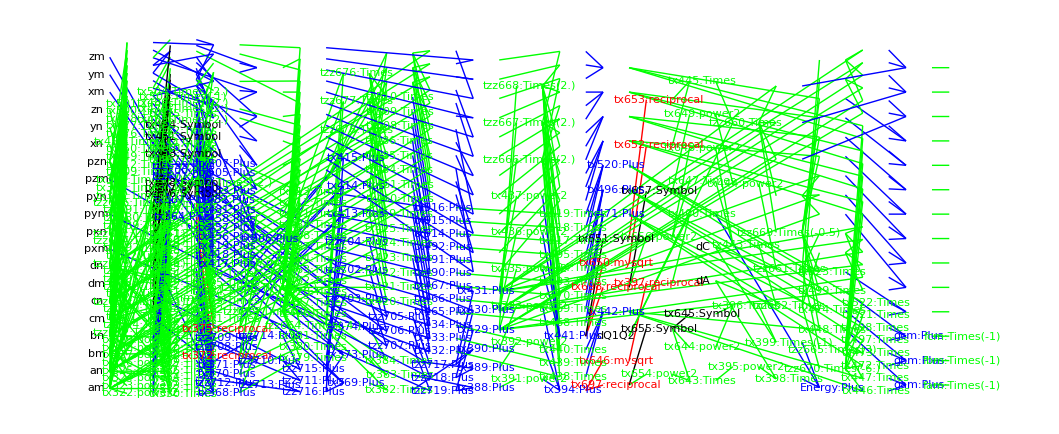

```mathematica
packGraph[nonbondRBPack]
```

## Evaluate plabk and plabl

```mathematica
plabk
```

plabk

```mathematica
plabl
```

plabl

# Nonbond rigid-body energy term periodic boundary conditions

```mathematica
Clear[pm,pxm,pym,pzm];
Clear[pn,pxn,pyn,pzn];
Clear[evdw, eeel,nonbondRBEquation];
```

```mathematica
pm = { pxm,pym,pzm };
pn = { pxn,pyn,pzn };
```

```mathematica
plabm = quatmultrans[quat[am,bm,cm,dm],{xm,ym,zm},pm]
```

{pxm+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)+xm,pym+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)+ym,pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)+zm}

```mathematica
plabn = quatmultrans[quat[an,bn,cn,dn],{xn,yn,zn},pn]
```

{pxn+(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xn,pyn+(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+yn,pzn+(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zn}

```mathematica
deltax = plabm[[1]]-plabn[[1]];
deltay = plabm[[2]]-plabn[[2]];
deltaz = plabm[[3]]-plabn[[3]];
```

```mathematica
PBX'[x_] := 1;
PBY'[x_] := 1;
PBZ'[x_] := 1;
```

```mathematica
plabdx = PBX[deltax];
plabdy = PBY[deltay];
plabdz = PBZ[deltaz];
```

```mathematica
nonbondRBDistance = Sqrt[plabdx*plabdx + plabdy*plabdy + plabdz*plabdz]
```

√(PBX[pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn]^2+PBY[pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn]^2+PBZ[pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn]^2)

```mathematica
evdwEquation = (dA/nonbondRBDistance^12-dC/nonbondRBDistance^6)
```

dA/((PBX[pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn]^2+PBY[pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn]^2+PBZ[pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn]^2)^6)-dC/((PBX[pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn]^2+PBY[pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn]^2+PBZ[pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn]^2)^3)

```mathematica
eeelEquation = (dQ1Q2/nonbondRBDistance)
```

dQ1Q2/(√(PBX[pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn]^2+PBY[pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn]^2+PBZ[pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn]^2))

```mathematica
nonbondRBEnergyFn = evdwEquation + eeelEquation
```

dA/((PBX[pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn]^2+PBY[pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn]^2+PBZ[pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn]^2)^6)-dC/((PBX[pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn]^2+PBY[pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn]^2+PBZ[pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn]^2)^3)+dQ1Q2/(√(PBX[pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn]^2+PBY[pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn]^2+PBZ[pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn]^2))

```mathematica
nonbondRBVarNames = { 
{am,a,I1,0},
{bm,b,I1,1},
{cm,c,I1,2},
{dm,d,I1,3},
{xm,x,I1,4},
{ym,y,I1,5},
{zm,z,I1,6},
{an,a,I2,0},
{bn,b,I2,1},
{cn,c,I2,2},
{dn,d,I2,3},
{xn,x,I2,4},
{yn,y,I2,5},
{zn,z,I2,6}
};
```

```mathematica
nonbondRBSetupRules = {};
AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(I1);"]];
AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(I2);"]];AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(dQ1Q2);"]];AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(dA);"]];
AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(dC);"]];
```

```mathematica
For[i=1,i≤Length[nonbondRBVarNames],i++,
str = "NONBONDRB_SET_POSITION("<>ToString[nonbondRBVarNames[[i]][[1]]]<>","<>ToString[nonbondRBVarNames[[i]][[3]]]<>","<>ToString[nonbondRBVarNames[[i]][[4]]]<>");";
(*Print[str];*)
AppendTo[nonbondRBSetupRules,CCode[str]];
];
```

```mathematica
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(pxm,ea1,getX());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(pym,ea1,getY());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(pzm,ea1,getZ());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(pxn,ea2,getX());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(pyn,ea2,getY());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(pzn,ea2,getZ());"]];
```

```mathematica
nonbondRBSetupRules//MatrixForm
```

(CCode[NONBONDRB_SET_PARAMETER(I1);]
CCode[NONBONDRB_SET_PARAMETER(I2);]
CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]
CCode[NONBONDRB_SET_PARAMETER(dA);]
CCode[NONBONDRB_SET_PARAMETER(dC);]
CCode[NONBONDRB_SET_POSITION(am,I1,0);]
CCode[NONBONDRB_SET_POSITION(bm,I1,1);]
CCode[NONBONDRB_SET_POSITION(cm,I1,2);]
CCode[NONBONDRB_SET_POSITION(dm,I1,3);]
CCode[NONBONDRB_SET_POSITION(xm,I1,4);]
CCode[NONBONDRB_SET_POSITION(ym,I1,5);]
CCode[NONBONDRB_SET_POSITION(zm,I1,6);]
CCode[NONBONDRB_SET_POSITION(an,I2,0);]
CCode[NONBONDRB_SET_POSITION(bn,I2,1);]
CCode[NONBONDRB_SET_POSITION(cn,I2,2);]
CCode[NONBONDRB_SET_POSITION(dn,I2,3);]
CCode[NONBONDRB_SET_POSITION(xn,I2,4);]
CCode[NONBONDRB_SET_POSITION(yn,I2,5);]
CCode[NONBONDRB_SET_POSITION(zn,I2,6);]
CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]
CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]
CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]
CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]
CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]
CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());])

```mathematica
nonbondRBEnergyRules = {};
nonbondRBOutputs = {};
AppendTo[nonbondRBEnergyRules,Assign[DeltaX,deltax]];
AppendTo[nonbondRBEnergyRules,Assign[DeltaY,deltay]];
AppendTo[nonbondRBEnergyRules,Assign[DeltaZ,deltaz]];
AppendTo[nonbondRBEnergyRules,Assign[Energy,nonbondRBEnergyFn]];
AppendTo[nonbondRBEnergyRules,EnergyAccumulate["NONBONDRB",Energy]];
AppendTo[nonbondRBOutputs,Energy];
AppendTo[nonbondRBOutputs,DeltaX];
AppendTo[nonbondRBOutputs,DeltaY];
AppendTo[nonbondRBOutputs,DeltaZ];
```

```mathematica
nonbondRBOutputs
```

{Energy,DeltaX,DeltaY,DeltaZ}

```mathematica
nonbondRBEnergyRules
```

{pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn→DeltaX,pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn→DeltaY,pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn→DeltaZ,dA/((PBX[pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn]^2+PBY[pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn]^2+PBZ[pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn]^2)^6)-dC/((PBX[pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn]^2+PBY[pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn]^2+PBZ[pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn]^2)^3)+dQ1Q2/(√(PBX[pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn]^2+PBY[pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn]^2+PBZ[pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn]^2))→Energy,CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]}

Position rules

```mathematica
nonbondPositionRBSetupRules = {};
AppendTo[nonbondPositionRBSetupRules,CCode["NONBOND_POSITION_RB_SET_PARAMETER(I1);"]];
```

```mathematica
For[i=1,i≤Length[nonbondRBVarNames]/2,i++,
str = "NONBOND_POSITION_RB_SET_POSITION("<>ToString[nonbondRBVarNames[[i]][[1]]]<>","<>ToString[nonbondRBVarNames[[i]][[3]]]<>","<>ToString[nonbondRBVarNames[[i]][[4]]]<>");";
(*Print[str];*)
AppendTo[nonbondPositionRBSetupRules,CCode[str]];
];
```

```mathematica
AppendTo[nonbondPositionRBSetupRules, CCode["NONBOND_POSITION_RB_SET_POINT(pxm,ea1,getX());"]];
AppendTo[nonbondPositionRBSetupRules, CCode["NONBOND_POSITION_RB_SET_POINT(pym,ea1,getY());"]];
AppendTo[nonbondPositionRBSetupRules, CCode["NONBOND_POSITION_RB_SET_POINT(pzm,ea1,getZ());"]];
```

```mathematica
plabm
```

{pxm+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)+xm,pym+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)+ym,pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)+zm}

```mathematica
nonbondPositionRules = {};
nonbondPositionOutputs = {};
AppendTo[nonbondPositionRules,Assign[plabmx,plabm[[1]]]];
AppendTo[nonbondPositionRules,Assign[plabmy,plabm[[2]]]];
AppendTo[nonbondPositionRules,Assign[plabmz,plabm[[3]]]];
AppendTo[nonbondPositionOutputs,plabmx];
AppendTo[nonbondPositionOutputs,plabmy];
AppendTo[nonbondPositionOutputs,plabmz];
```

```mathematica
nonbondPositionRules
```

{pxm+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)+xm→plabmx,pym+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)+ym→plabmy,pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)+zm→plabmz}

```mathematica
nonbondAllPositionRules = Flatten[{
nonbondPositionRBSetupRules,
nonbondPositionRules}];
```

```mathematica
nonbondPositionPack0 = {
Name->"NONBOND_POSITIONS",
AdditionalCDeclares->"",
DerivativeVariables->nonbondPositionInput,
Rules->nonbondAllPositionRules,
Input->nonbondPositionInput,
Output->nonbondPositionOutputs
};
```

```mathematica
packOptimize[nonbondPositionPack0]
```

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = True

TimesOptimize = True

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {plabmx, plabmy, plabmz}

There were no trivial rules

Collecting terms

Set::write: Tag Times in Null {Name→NONBOND_POSITIONS,AdditionalCDeclares→,DerivativeVariables→nonbondPositionInput,Rules→{CCode[NONBOND_POSITION_RB_SET_PARAMETER(I1);],CCode[NONBOND_POSITION_RB_SET_POSITION(am,I1,0);],CCode[NONBOND_POSITION_RB_SET_POSITION(bm,I1,1);],CCode[NONBOND_POSITION_RB_SET_POSITION(cm,I1,2);],CCode[NONBOND_POSITION_RB_SET_POSITION(dm,I1,3);],CCode[NONBOND_POSITION_RB_SET_POSITION(xm,I1,4);],CCode[NONBOND_POSITION_RB_SET_POSITION(ym,I1,5);],CCode[NONBOND_POSITION_RB_SET_POSITION(zm,I1,6);],CCode[NONBOND_POSITION_RB_SET_POINT(pxm,ea1,getX());],CCode[NONBOND_POSITION_RB_SET_POINT(pym,ea1,getY());],CCode[NONBOND_POSITION_RB_SET_POINT(pzm,ea1,getZ());],pxm+2. Power[«2»] Plus[«6»]+xm→plabmx,pym+2. Power[«2»] Plus[«6»]+ym→plabmy,pzm+2. Power[«2»] Plus[«6»]+zm→plabmz},Input→nonbondPositionInput,Output→{plabmx,plabmy,plabmz}} is Protected.

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {plabmx, plabmy, plabmz}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {plabmx, plabmy, plabmz}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {plabmx, plabmy, plabmz}

There were no trivial rules

trivialRules>> triv = {}

trivialRules>> outs = {plabmx, plabmy, plabmz}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {plabmx, plabmy, plabmz}

There were no trivial rules

trivialRules>> triv = {}

trivialRules>> outs = {plabmx, plabmy, plabmz}

There were no trivial rules

Writing declares to file: _NONBOND_POSITIONS_termDeclares.cc

Writing code to file: _NONBOND_POSITIONS_termCode.cc

{Name→NONBOND_POSITIONS,AdditionalCDeclares→,Input→nonbondPositionInput,Output→{plabmx,plabmy,plabmz},EnergyFunction→EnergyFunction,DerivativeVariables→nonbondPositionInput,Rules→{CCode[NONBOND_POSITION_RB_SET_PARAMETER(I1);],CCode[NONBOND_POSITION_RB_SET_POSITION(am,I1,0);],CCode[NONBOND_POSITION_RB_SET_POSITION(bm,I1,1);],CCode[NONBOND_POSITION_RB_SET_POSITION(cm,I1,2);],CCode[NONBOND_POSITION_RB_SET_POSITION(dm,I1,3);],CCode[NONBOND_POSITION_RB_SET_POSITION(xm,I1,4);],CCode[NONBOND_POSITION_RB_SET_POSITION(ym,I1,5);],CCode[NONBOND_POSITION_RB_SET_POSITION(zm,I1,6);],CCode[NONBOND_POSITION_RB_SET_POINT(pxm,ea1,getX());],CCode[NONBOND_POSITION_RB_SET_POINT(pym,ea1,getY());],CCode[NONBOND_POSITION_RB_SET_POINT(pzm,ea1,getZ());],power2[am]→tx31,power2[bm]→tx32,power2[cm]→tx33,power2[dm]→tx34,cm pym→tzz67,bm tzz67→tx35,-pym→tzz63,am dm tzz63→tx36,am cm→tzz68,pzm tzz68→tx37,dm pzm→tzz65,bm tzz65→tx38,-pxm→tzz64,tx33 tzz64→tx39,tx34 tzz64→tx40,tx31+tx32+tx33+tx34→tx41,tx35+tx36+tx37+tx38+tx39+tx40→tx42,reciprocal[tx41]→tx43,2. tx43→tzz61,tx42 tzz61→tx44,pxm+tx44+xm→plabmx,bm cm pxm→tx45,dm pxm→tzz66,am tzz66→tx46,-pzm→tzz62,am bm→tzz69,tzz62 tzz69→tx47,cm tzz65→tx48,tx32 tzz63→tx49,tx34 tzz63→tx50,tx45+tx46+tx47+tx48+tx49+tx50→tx51,tx51 tzz61→tx52,pym+tx52+ym→plabmy,tzz64 tzz68→tx53,bm tzz66→tx54,pym tzz69→tx55,dm tzz67→tx56,tx32 tzz62→tx57,tx33 tzz62→tx58,tx53+tx54+tx55+tx56+tx57+tx58→tx59,tx59 tzz61→tx60,pzm+tx60+zm→plabmz},HessianStructure→HessianStructure,CCode→NOT USED,MathCode→Block[{plabmx,plabmy,plabmz,tx31,tx32,tx33,tx34,tx35,tx36,tx37,tx38,tx39,tx40,tx41,tx42,tx43,tx44,tx45,tx46,tx47,tx48,tx49,tx50,tx51,tx52,tx53,tx54,tx55,tx56,tx57,tx58,tx59,tx60,tzz61,tzz62,tzz63,tzz64,tzz65,tzz66,tzz67,tzz68,tzz69,xxxDummy},
	(*NONBOND_POSITION_RB_SET_PARAMETER(I1);*)
	(*NONBOND_POSITION_RB_SET_POSITION(am,I1,0);*)
	(*NONBOND_POSITION_RB_SET_POSITION(bm,I1,1);*)
	(*NONBOND_POSITION_RB_SET_POSITION(cm,I1,2);*)
	(*NONBOND_POSITION_RB_SET_POSITION(dm,I1,3);*)
	(*NONBOND_POSITION_RB_SET_POSITION(xm,I1,4);*)
	(*NONBOND_POSITION_RB_SET_POSITION(ym,I1,5);*)
	(*NONBOND_POSITION_RB_SET_POSITION(zm,I1,6);*)
	(*NONBOND_POSITION_RB_SET_POINT(pxm,ea1,getX());*)
	(*NONBOND_POSITION_RB_SET_POINT(pym,ea1,getY());*)
	(*NONBOND_POSITION_RB_SET_POINT(pzm,ea1,getZ());*)
	tx31= mathPower2[am]; (*Rule 12*)
	tx32= mathPower2[bm]; (*Rule 13*)
	tx33= mathPower2[cm]; (*Rule 14*)
	tx34= mathPower2[dm]; (*Rule 15*)
	tzz67=cm pym; (*Rule 16*)
	tx35=bm tzz67; (*Rule 17*)
	tzz63=-pym; (*Rule 18*)
	tx36=am dm tzz63; (*Rule 19*)
	tzz68=am cm; (*Rule 20*)
	tx37=pzm tzz68; (*Rule 21*)
	tzz65=dm pzm; (*Rule 22*)
	tx38=bm tzz65; (*Rule 23*)
	tzz64=-pxm; (*Rule 24*)
	tx39=tx33 tzz64; (*Rule 25*)
	tx40=tx34 tzz64; (*Rule 26*)
	tx41=tx31 + tx32 + tx33 + tx34; (*Rule 27*)
	tx42=tx35 + tx36 + tx37 + tx38 + tx39 + tx40; (*Rule 28*)
	tx43= mathReciprocal[tx41]; (*Rule 29*)
	tzz61=2. tx43; (*Rule 30*)
	tx44=tx42 tzz61; (*Rule 31*)
	plabmx=pxm + tx44 + xm; (*Rule 32*)
	tx45=bm cm pxm; (*Rule 33*)
	tzz66=dm pxm; (*Rule 34*)
	tx46=am tzz66; (*Rule 35*)
	tzz62=-pzm; (*Rule 36*)
	tzz69=am bm; (*Rule 37*)
	tx47=tzz62 tzz69; (*Rule 38*)
	tx48=cm tzz65; (*Rule 39*)
	tx49=tx32 tzz63; (*Rule 40*)
	tx50=tx34 tzz63; (*Rule 41*)
	tx51=tx45 + tx46 + tx47 + tx48 + tx49 + tx50; (*Rule 42*)
	tx52=tx51 tzz61; (*Rule 43*)
	plabmy=pym + tx52 + ym; (*Rule 44*)
	tx53=tzz64 tzz68; (*Rule 45*)
	tx54=bm tzz66; (*Rule 46*)
	tx55=pym tzz69; (*Rule 47*)
	tx56=dm tzz67; (*Rule 48*)
	tx57=tx32 tzz62; (*Rule 49*)
	tx58=tx33 tzz62; (*Rule 50*)
	tx59=tx53 + tx54 + tx55 + tx56 + tx57 + tx58; (*Rule 51*)
	tx60=tx59 tzz61; (*Rule 52*)
	plabmz=pzm + tx60 + zm; (*Rule 53*)
{plabmx, plabmy, plabmz}]
}

## Append the Gradient rules

```mathematica
nonbondRBOutputs
```

{Energy,DeltaX,DeltaY,DeltaZ}

```mathematica
nonbondRBForceRules = {};
```

```mathematica
nonbondRBEnergyRules
```

{pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn→DeltaX,pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn→DeltaY,pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn→DeltaZ,dA/((PBX[pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn]^2+PBY[pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn]^2+PBZ[pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn]^2)^6)-dC/((PBX[pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn]^2+PBY[pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn]^2+PBZ[pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn]^2)^3)+dQ1Q2/(√(PBX[pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn]^2+PBY[pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn]^2+PBZ[pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn]^2))→Energy,CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]}

```mathematica
AppendGradientForceIfCalcForce["NONBONDRB",nonbondRBEnergyRules,nonbondRBOutputs,nonbondRBEnergyFn,nonbondRBVarNames];
```

```mathematica
AppendGradientForceIfCalcForceExtraRule["NONBONDRB",nonbondRBEnergyRules,nonbondRBOutputs,nonbondRBEnergyFn,nonbondRBVarNames, CCode["BAIL_OUT_IF_CUTOFF(DeltaX,DeltaY,DeltaZ)"]];
```

```mathematica
nonbondRBEnergyRules
```

{pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn→DeltaX,pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn→DeltaY,pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn→DeltaZ,92,CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );],CCode[} /*calcForce */],CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]}
 |  |  |  |

```mathematica
nonbondRBOutputs
```

{Energy,DeltaX,DeltaY,DeltaZ,fam,fbm,fcm,fdm,fxm,fym,fzm,fan,fbn,fcn,fdn,fxn,fyn,fzn,fam,fbm,fcm,fdm,fxm,fym,fzm,fan,fbn,fcn,fdn,fxn,fyn,fzn}

### Collect terms and convert to C code

```mathematica
nonbondRBAllRules ={
nonbondRBSetupRules,
nonbondRBEnergyRules};
```

```mathematica
nonbondRBRules = Flatten[nonbondRBAllRules];
```

```mathematica
nonbondRBRules
```

{CCode[NONBONDRB_SET_PARAMETER(I1);],CCode[NONBONDRB_SET_PARAMETER(I2);],CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);],CCode[NONBONDRB_SET_PARAMETER(dA);],CCode[NONBONDRB_SET_PARAMETER(dC);],114,-gzn→fzn,CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );],CCode[} /*calcForce */],CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]}
 |  |  |  |

```mathematica
nonbondRBInput = { ak,bk,ck,dk,xk,yk,zk, al,bl,cl,dl,xl,yl,zl };
```

```mathematica
AppendTo[nonbondRBOutputs,nonbondRBDeviation];
```

### Assemble the rules, the name of the energy term, the independant variable names, etc. into what passes for a structure in Mathematica (I call it a Pack)

```mathematica
nonbondRBPack0 = {
Name->"NONBONDRB",
AdditionalCDeclares->"",
DerivativeVariables->{ ak,bk,ck,dk,xk,yk,zk, al,bl,cl,dl,xl,yl,zl },
Rules->nonbondRBRules,
Input->nonbondRBInput,
Output->nonbondRBOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[nonbondRBPack0];
```

Writing finite difference debug code to: _NONBONDRB_debugFiniteDifference.cc

Writing debug variable declares to: _NONBONDRB_debugEvalDeclares.cc

Writing xml output debug code to: _NONBONDRB_debugEvalSerialize.cc

Writing set variables debug code to: _NONBONDRB_debugEvalSet.cc

### Put the pedal to the metal and generate "C" code.

```mathematica
nonbondRBPack = packOptimize[nonbondRBPack0];
```

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, DeltaX, DeltaY, DeltaZ, nonbondRBDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, DeltaX, DeltaY, DeltaZ, nonbondRBDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {tx194 -> tx191}

trivialRules>> outs = {Energy, DeltaX, DeltaY, DeltaZ, nonbondRBDeviation}

Trivial rules are being removed: tx194 -> tx191

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]

CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]

CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]

CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]

CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]

CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]

power2[am] -> tx95

power2[an] -> tx96

power2[bm] -> tx97

power2[bn] -> tx98

power2[cm] -> tx99

power2[cn] -> tx100

power2[dm] -> tx101

power2[dn] -> tx102

bm cm pym -> tx103

-(am dm pym) -> tx104

bn cn pyn -> tx105

-(an dn pyn) -> tx106

am cm pzm -> tx107

bm dm pzm -> tx108

an cn pzn -> tx109

bn dn pzn -> tx110

-(pxn tx100) -> tx111

-(pxm tx101) -> tx112

-(pxn tx102) -> tx113

tx100 + tx102 + tx96 + tx98 -> tx114

-(pxm tx99) -> tx115

tx101 + tx95 + tx97 + tx99 -> tx116

tx105 + tx106 + tx109 + tx110 + tx111 + tx113 -> tx117

reciprocal[tx114] -> tx118

tx103 + tx104 + tx107 + tx108 + tx112 + tx115 -> tx119

reciprocal[tx116] -> tx120

-pxn -> tx121

-2. tx117 tx118 -> tx122

2. tx119 tx120 -> tx123

-xn -> tx124

pxm + tx121 + tx122 + tx123 + tx124 + xm -> DeltaX

bm cm pxm -> tx125

am dm pxm -> tx126

bn cn pxn -> tx127

an dn pxn -> tx128

-(am bm pzm) -> tx129

cm dm pzm -> tx130

-(an bn pzn) -> tx131

cn dn pzn -> tx132

-(pym tx101) -> tx133

-(pyn tx102) -> tx134

-(pym tx97) -> tx135

-(pyn tx98) -> tx136

tx125 + tx126 + tx129 + tx130 + tx133 + tx135 -> tx137

tx127 + tx128 + tx131 + tx132 + tx134 + tx136 -> tx138

-pyn -> tx139

2. tx120 tx137 -> tx140

-2. tx118 tx138 -> tx141

-yn -> tx142

pym + tx139 + tx140 + tx141 + tx142 + ym -> DeltaY

-(am cm pxm) -> tx143

bm dm pxm -> tx144

bn dn pxn -> tx145

am bm pym -> tx146

cm dm pym -> tx147

an bn pyn -> tx148

cn dn pyn -> tx149

-(pzn tx100) -> tx150

an cn tx121 -> tx151

-(pzm tx97) -> tx152

-(pzn tx98) -> tx153

-(pzm tx99) -> tx154

tx145 + tx148 + tx149 + tx150 + tx151 + tx153 -> tx155

tx143 + tx144 + tx146 + tx147 + tx152 + tx154 -> tx156

-pzn -> tx157

-2. tx118 tx155 -> tx158

2. tx120 tx156 -> tx159

-zn -> tx160

pzm + tx157 + tx158 + tx159 + tx160 + zm -> DeltaZ

tx100 tx121 -> tx161

tx102 tx121 -> tx162

tx102 tx139 -> tx163

tx100 tx157 -> tx164

tx139 tx98 -> tx165

tx157 tx98 -> tx166

tx105 + tx106 + tx109 + tx110 + tx161 + tx162 -> tx167

tx127 + tx128 + tx131 + tx132 + tx163 + tx165 -> tx168

tx145 + tx148 + tx149 + tx151 + tx164 + tx166 -> tx169

-2. tx118 tx167 -> tx170

-2. tx118 tx168 -> tx171

-2. tx118 tx169 -> tx172

pxm + tx121 + tx123 + tx124 + tx170 + xm -> tx173

pym + tx139 + tx140 + tx142 + tx171 + ym -> tx174

pzm + tx157 + tx159 + tx160 + tx172 + zm -> tx175

PBX[tx173] -> tx176

PBY[tx174] -> tx177

PBZ[tx175] -> tx178

power2[tx176] -> tx179

power2[tx177] -> tx180

power2[tx178] -> tx181

tx179 + tx180 + tx181 -> tx182

powern2[tx182] -> tx193

reciprocal[tx182] -> tx194

tx193 tx194 -> tx189

power2[tx189] -> tx183

power2[tx194] -> tx190

tx194 -> tx191

tx190 tx191 -> tx184

mysqrt[tx182] -> tx192

reciprocal[tx192] -> tx185

dA tx183 -> tx186

-(dC tx184) -> tx187

dQ1Q2 tx185 -> tx188

tx186 + tx187 + tx188 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

trivialRules>> triv = {tzz212 -> tx121, tzz199 -> tx139, tzz197 -> tx157, tx194 -> tx191}

trivialRules>> outs = {Energy, DeltaX, DeltaY, DeltaZ, nonbondRBDeviation}

Trivial rules are being removed: tzz212 -> tx121

tzz199 -> tx139

tzz197 -> tx157

tx194 -> tx191

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]

CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]

CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]

CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]

CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]

CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]

power2[am] -> tx95

power2[an] -> tx96

power2[bm] -> tx97

power2[bn] -> tx98

power2[cm] -> tx99

power2[cn] -> tx100

power2[dm] -> tx101

power2[dn] -> tx102

cm pym -> tzz207

bm tzz207 -> tx103

-pym -> tzz200

am dm tzz200 -> tx104

cn pyn -> tzz206

bn tzz206 -> tx105

-pyn -> tzz199

an dn tzz199 -> tx106

am cm -> tzz210

pzm tzz210 -> tx107

dm pzm -> tzz204

bm tzz204 -> tx108

an cn -> tzz208

pzn tzz208 -> tx109

dn pzn -> tzz202

bn tzz202 -> tx110

-pxn -> tzz212

tx100 tzz212 -> tx111

-pxm -> tzz201

tx101 tzz201 -> tx112

tx102 tzz212 -> tx113

tx100 + tx102 + tx96 + tx98 -> tx114

tx99 tzz201 -> tx115

tx101 + tx95 + tx97 + tx99 -> tx116

tx105 + tx106 + tx109 + tx110 + tx111 + tx113 -> tx117

reciprocal[tx114] -> tx118

tx103 + tx104 + tx107 + tx108 + tx112 + tx115 -> tx119

reciprocal[tx116] -> tx120

tzz212 -> tx121

-2. tx118 -> tzz195

tx117 tzz195 -> tx122

2. tx120 -> tzz196

tx119 tzz196 -> tx123

-xn -> tx124

pxm + tx121 + tx122 + tx123 + tx124 + xm -> DeltaX

bm cm pxm -> tx125

dm pxm -> tzz205

am tzz205 -> tx126

bn cn pxn -> tx127

dn pxn -> tzz203

an tzz203 -> tx128

-pzm -> tzz198

am bm -> tzz211

tzz198 tzz211 -> tx129

cm tzz204 -> tx130

-pzn -> tzz197

an bn -> tzz209

tzz197 tzz209 -> tx131

cn tzz202 -> tx132

tx101 tzz200 -> tx133

tx102 tzz199 -> tx134

tx97 tzz200 -> tx135

tx98 tzz199 -> tx136

tx125 + tx126 + tx129 + tx130 + tx133 + tx135 -> tx137

tx127 + tx128 + tx131 + tx132 + tx134 + tx136 -> tx138

tzz199 -> tx139

tx137 tzz196 -> tx140

tx138 tzz195 -> tx141

-yn -> tx142

pym + tx139 + tx140 + tx141 + tx142 + ym -> DeltaY

tzz201 tzz210 -> tx143

bm tzz205 -> tx144

bn tzz203 -> tx145

pym tzz211 -> tx146

dm tzz207 -> tx147

pyn tzz209 -> tx148

dn tzz206 -> tx149

tx100 tzz197 -> tx150

tx121 tzz208 -> tx151

tx97 tzz198 -> tx152

tx98 tzz197 -> tx153

tx99 tzz198 -> tx154

tx145 + tx148 + tx149 + tx150 + tx151 + tx153 -> tx155

tx143 + tx144 + tx146 + tx147 + tx152 + tx154 -> tx156

tzz197 -> tx157

tx155 tzz195 -> tx158

tx156 tzz196 -> tx159

-zn -> tx160

pzm + tx157 + tx158 + tx159 + tx160 + zm -> DeltaZ

tx100 tx121 -> tx161

tx102 tx121 -> tx162

tx102 tx139 -> tx163

tx100 tx157 -> tx164

tx139 tx98 -> tx165

tx157 tx98 -> tx166

tx105 + tx106 + tx109 + tx110 + tx161 + tx162 -> tx167

tx127 + tx128 + tx131 + tx132 + tx163 + tx165 -> tx168

tx145 + tx148 + tx149 + tx151 + tx164 + tx166 -> tx169

tx167 tzz195 -> tx170

tx168 tzz195 -> tx171

tx169 tzz195 -> tx172

pxm + tx121 + tx123 + tx124 + tx170 + xm -> tx173

pym + tx139 + tx140 + tx142 + tx171 + ym -> tx174

pzm + tx157 + tx159 + tx160 + tx172 + zm -> tx175

PBX[tx173] -> tx176

PBY[tx174] -> tx177

PBZ[tx175] -> tx178

power2[tx176] -> tx179

power2[tx177] -> tx180

power2[tx178] -> tx181

tx179 + tx180 + tx181 -> tx182

power2[reciprocal[tx182]] -> tx193

reciprocal[tx182] -> tx194

tx193 tx194 -> tx189

power2[tx189] -> tx183

power2[tx194] -> tx190

tx194 -> tx191

tx190 tx191 -> tx184

mysqrt[tx182] -> tx192

reciprocal[tx192] -> tx185

dA tx183 -> tx186

-(dC tx184) -> tx187

dQ1Q2 tx185 -> tx188

tx186 + tx187 + tx188 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

eliminateTrivialRules

trivialRules>> triv = {tzz212 -> tx121, tzz199 -> tx139, tzz197 -> tx157, tx213 -> tx194, tx194 -> tx191}

trivialRules>> outs = {Energy, DeltaX, DeltaY, DeltaZ, nonbondRBDeviation}

Trivial rules are being removed: tzz212 -> tx121

tzz199 -> tx139

tzz197 -> tx157

tx213 -> tx194

tx194 -> tx191

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]

CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]

CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]

CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]

CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]

CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]

power2[am] -> tx95

power2[an] -> tx96

power2[bm] -> tx97

power2[bn] -> tx98

power2[cm] -> tx99

power2[cn] -> tx100

power2[dm] -> tx101

power2[dn] -> tx102

cm pym -> tzz207

bm tzz207 -> tx103

-pym -> tzz200

am dm tzz200 -> tx104

cn pyn -> tzz206

bn tzz206 -> tx105

-pyn -> tzz199

an dn tzz199 -> tx106

am cm -> tzz210

pzm tzz210 -> tx107

dm pzm -> tzz204

bm tzz204 -> tx108

an cn -> tzz208

pzn tzz208 -> tx109

dn pzn -> tzz202

bn tzz202 -> tx110

-pxn -> tzz212

tx100 tzz212 -> tx111

-pxm -> tzz201

tx101 tzz201 -> tx112

tx102 tzz212 -> tx113

tx100 + tx102 + tx96 + tx98 -> tx114

tx99 tzz201 -> tx115

tx101 + tx95 + tx97 + tx99 -> tx116

tx105 + tx106 + tx109 + tx110 + tx111 + tx113 -> tx117

reciprocal[tx114] -> tx118

tx103 + tx104 + tx107 + tx108 + tx112 + tx115 -> tx119

reciprocal[tx116] -> tx120

tzz212 -> tx121

-2. tx118 -> tzz195

tx117 tzz195 -> tx122

2. tx120 -> tzz196

tx119 tzz196 -> tx123

-xn -> tx124

pxm + tx121 + tx122 + tx123 + tx124 + xm -> DeltaX

bm cm pxm -> tx125

dm pxm -> tzz205

am tzz205 -> tx126

bn cn pxn -> tx127

dn pxn -> tzz203

an tzz203 -> tx128

-pzm -> tzz198

am bm -> tzz211

tzz198 tzz211 -> tx129

cm tzz204 -> tx130

-pzn -> tzz197

an bn -> tzz209

tzz197 tzz209 -> tx131

cn tzz202 -> tx132

tx101 tzz200 -> tx133

tx102 tzz199 -> tx134

tx97 tzz200 -> tx135

tx98 tzz199 -> tx136

tx125 + tx126 + tx129 + tx130 + tx133 + tx135 -> tx137

tx127 + tx128 + tx131 + tx132 + tx134 + tx136 -> tx138

tzz199 -> tx139

tx137 tzz196 -> tx140

tx138 tzz195 -> tx141

-yn -> tx142

pym + tx139 + tx140 + tx141 + tx142 + ym -> DeltaY

tzz201 tzz210 -> tx143

bm tzz205 -> tx144

bn tzz203 -> tx145

pym tzz211 -> tx146

dm tzz207 -> tx147

pyn tzz209 -> tx148

dn tzz206 -> tx149

tx100 tzz197 -> tx150

tx121 tzz208 -> tx151

tx97 tzz198 -> tx152

tx98 tzz197 -> tx153

tx99 tzz198 -> tx154

tx145 + tx148 + tx149 + tx150 + tx151 + tx153 -> tx155

tx143 + tx144 + tx146 + tx147 + tx152 + tx154 -> tx156

tzz197 -> tx157

tx155 tzz195 -> tx158

tx156 tzz196 -> tx159

-zn -> tx160

pzm + tx157 + tx158 + tx159 + tx160 + zm -> DeltaZ

tx100 tx121 -> tx161

tx102 tx121 -> tx162

tx102 tx139 -> tx163

tx100 tx157 -> tx164

tx139 tx98 -> tx165

tx157 tx98 -> tx166

tx105 + tx106 + tx109 + tx110 + tx161 + tx162 -> tx167

tx127 + tx128 + tx131 + tx132 + tx163 + tx165 -> tx168

tx145 + tx148 + tx149 + tx151 + tx164 + tx166 -> tx169

tx167 tzz195 -> tx170

tx168 tzz195 -> tx171

tx169 tzz195 -> tx172

pxm + tx121 + tx123 + tx124 + tx170 + xm -> tx173

pym + tx139 + tx140 + tx142 + tx171 + ym -> tx174

pzm + tx157 + tx159 + tx160 + tx172 + zm -> tx175

PBX[tx173] -> tx176

PBY[tx174] -> tx177

PBZ[tx175] -> tx178

power2[tx176] -> tx179

power2[tx177] -> tx180

power2[tx178] -> tx181

tx179 + tx180 + tx181 -> tx182

reciprocal[tx182] -> tx213

power2[tx213] -> tx193

tx213 -> tx194

tx193 tx194 -> tx189

power2[tx189] -> tx183

power2[tx194] -> tx190

tx194 -> tx191

tx190 tx191 -> tx184

mysqrt[tx182] -> tx192

reciprocal[tx192] -> tx185

dA tx183 -> tx186

-(dC tx184) -> tx187

dQ1Q2 tx185 -> tx188

tx186 + tx187 + tx188 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

trivialRules>> triv = {tzz212 -> tx121, tzz199 -> tx139, tzz197 -> tx157, tx213 -> tx194, tx194 -> tx191}

trivialRules>> outs = {Energy, DeltaX, DeltaY, DeltaZ, nonbondRBDeviation}

Trivial rules are being removed: tzz212 -> tx121

tzz199 -> tx139

tzz197 -> tx157

tx213 -> tx194

tx194 -> tx191

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]

CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]

CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]

CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]

CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]

CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]

power2[am] -> tx95

power2[an] -> tx96

power2[bm] -> tx97

power2[bn] -> tx98

power2[cm] -> tx99

power2[cn] -> tx100

power2[dm] -> tx101

power2[dn] -> tx102

cm pym -> tzz207

bm tzz207 -> tx103

-pym -> tzz200

am dm tzz200 -> tx104

cn pyn -> tzz206

bn tzz206 -> tx105

-pyn -> tzz199

an dn tzz199 -> tx106

am cm -> tzz210

pzm tzz210 -> tx107

dm pzm -> tzz204

bm tzz204 -> tx108

an cn -> tzz208

pzn tzz208 -> tx109

dn pzn -> tzz202

bn tzz202 -> tx110

-pxn -> tzz212

tx100 tzz212 -> tx111

-pxm -> tzz201

tx101 tzz201 -> tx112

tx102 tzz212 -> tx113

tx100 + tx102 + tx96 + tx98 -> tx114

tx99 tzz201 -> tx115

tx101 + tx95 + tx97 + tx99 -> tx116

tx109 + tx110 -> tzz229

tx106 + tzz229 -> tzz230

tx105 + tzz230 -> tzz231

tx111 + tx113 + tzz231 -> tx117

reciprocal[tx114] -> tx118

tx103 + tx104 + tx107 + tx108 + tx112 + tx115 -> tx119

reciprocal[tx116] -> tx120

tzz212 -> tx121

-2. tx118 -> tzz195

tx117 tzz195 -> tx122

2. tx120 -> tzz196

tx119 tzz196 -> tx123

-xn -> tx124

tx124 + xm -> tzz226

tx123 + tzz226 -> tzz227

tx121 + tzz227 -> tzz228

pxm + tzz228 -> tzz234

tx122 + tzz234 -> DeltaX

bm cm pxm -> tx125

dm pxm -> tzz205

am tzz205 -> tx126

bn cn pxn -> tx127

dn pxn -> tzz203

an tzz203 -> tx128

-pzm -> tzz198

am bm -> tzz211

tzz198 tzz211 -> tx129

cm tzz204 -> tx130

-pzn -> tzz197

an bn -> tzz209

tzz197 tzz209 -> tx131

cn tzz202 -> tx132

tx101 tzz200 -> tx133

tx102 tzz199 -> tx134

tx97 tzz200 -> tx135

tx98 tzz199 -> tx136

tx125 + tx126 + tx129 + tx130 + tx133 + tx135 -> tx137

tx131 + tx132 -> tzz223

tx128 + tzz223 -> tzz224

tx127 + tzz224 -> tzz225

tx134 + tx136 + tzz225 -> tx138

tzz199 -> tx139

tx137 tzz196 -> tx140

tx138 tzz195 -> tx141

-yn -> tx142

tx142 + ym -> tzz220

tx140 + tzz220 -> tzz221

tx139 + tzz221 -> tzz222

pym + tzz222 -> tzz233

tx141 + tzz233 -> DeltaY

tzz201 tzz210 -> tx143

bm tzz205 -> tx144

bn tzz203 -> tx145

pym tzz211 -> tx146

dm tzz207 -> tx147

pyn tzz209 -> tx148

dn tzz206 -> tx149

tx100 tzz197 -> tx150

tx121 tzz208 -> tx151

tx97 tzz198 -> tx152

tx98 tzz197 -> tx153

tx99 tzz198 -> tx154

tx149 + tx151 -> tzz217

tx148 + tzz217 -> tzz218

tx145 + tzz218 -> tzz219

tx150 + tx153 + tzz219 -> tx155

tx143 + tx144 + tx146 + tx147 + tx152 + tx154 -> tx156

tzz197 -> tx157

tx155 tzz195 -> tx158

tx156 tzz196 -> tx159

-zn -> tx160

tx160 + zm -> tzz214

tx159 + tzz214 -> tzz215

tx157 + tzz215 -> tzz216

pzm + tzz216 -> tzz232

tx158 + tzz232 -> DeltaZ

tx100 tx121 -> tx161

tx102 tx121 -> tx162

tx102 tx139 -> tx163

tx100 tx157 -> tx164

tx139 tx98 -> tx165

tx157 tx98 -> tx166

tx161 + tx162 + tzz231 -> tx167

tx163 + tx165 + tzz225 -> tx168

tx164 + tx166 + tzz219 -> tx169

tx167 tzz195 -> tx170

tx168 tzz195 -> tx171

tx169 tzz195 -> tx172

tx170 + tzz234 -> tx173

tx171 + tzz233 -> tx174

tx172 + tzz232 -> tx175

PBX[tx173] -> tx176

PBY[tx174] -> tx177

PBZ[tx175] -> tx178

power2[tx176] -> tx179

power2[tx177] -> tx180

power2[tx178] -> tx181

tx179 + tx180 + tx181 -> tx182

reciprocal[tx182] -> tx213

power2[tx213] -> tx193

tx213 -> tx194

tx193 tx194 -> tx189

power2[tx189] -> tx183

power2[tx194] -> tx190

tx194 -> tx191

tx190 tx191 -> tx184

mysqrt[tx182] -> tx192

reciprocal[tx192] -> tx185

dA tx183 -> tx186

-(dC tx184) -> tx187

dQ1Q2 tx185 -> tx188

tx186 + tx187 + tx188 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

Writing declares to file: _NONBONDRB_termDeclares.cc

Writing code to file: _NONBONDRB_termCode.cc

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = True

TimesOptimize = True

eliminateTrivialRules

trivialRules>> triv = {gam -> gam, gbm -> gbm, gcm -> gcm, gdm -> gdm, gxm -> gxm, gym -> gym, gzm -> gzm, gan -> gan, gbn -> gbn, gcn -> gcn, gdn -> gdn, gxn -> gxn, gyn -> gyn, gzn -> gzn}

trivialRules>> outs = {Energy, DeltaX, DeltaY, DeltaZ, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: gam -> gam

gbm -> gbm

gcm -> gcm

gdm -> gdm

gxm -> gxm

gym -> gym

gzm -> gzm

gan -> gan

gbn -> gbn

gcn -> gcn

gdn -> gdn

gxn -> gxn

gyn -> gyn

gzn -> gzn

After removal: 

CCode[NONBONDRB_SET_PARAMETER(I1);]



CCode[NONBONDRB_SET_PARAMETER(I2);]



CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]



CCode[NONBONDRB_SET_PARAMETER(dA);]



CCode[NONBONDRB_SET_PARAMETER(dC);]



CCode[NONBONDRB_SET_POSITION(am,I1,0);]



CCode[NONBONDRB_SET_POSITION(bm,I1,1);]



CCode[NONBONDRB_SET_POSITION(cm,I1,2);]



CCode[NONBONDRB_SET_POSITION(dm,I1,3);]



CCode[NONBONDRB_SET_POSITION(xm,I1,4);]



CCode[NONBONDRB_SET_POSITION(ym,I1,5);]



CCode[NONBONDRB_SET_POSITION(zm,I1,6);]



CCode[NONBONDRB_SET_POSITION(an,I2,0);]



CCode[NONBONDRB_SET_POSITION(bn,I2,1);]



CCode[NONBONDRB_SET_POSITION(cn,I2,2);]



CCode[NONBONDRB_SET_POSITION(dn,I2,3);]



CCode[NONBONDRB_SET_POSITION(xn,I2,4);]



CCode[NONBONDRB_SET_POSITION(yn,I2,5);]



CCode[NONBONDRB_SET_POSITION(zn,I2,6);]



CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]



CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]



CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]



CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]



CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]



CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]


  2
am  -> tx1


  2
an  -> tx2


  2
bm  -> tx3


  2
bn  -> tx4


  2
cm  -> tx5


  2
cn  -> tx6


  2
dm  -> tx7


  2
dn  -> tx8



bm cm pym -> tx9



-(am dm pym) -> tx10



bn cn pyn -> tx11



-(an dn pyn) -> tx12



am cm pzm -> tx13



bm dm pzm -> tx14



an cn pzn -> tx15



bn dn pzn -> tx16



-(pxm tx5) -> tx17



-(pxn tx6) -> tx18



-(pxm tx7) -> tx19



tx1 + tx3 + tx5 + tx7 -> tx20



-(pxn tx8) -> tx21



tx2 + tx4 + tx6 + tx8 -> tx22

 1
---- -> tx23
tx20



tx11 + tx12 + tx15 + tx16 + tx18 + tx21 -> tx24

 1
---- -> tx25
tx22



tx10 + tx13 + tx14 + tx17 + tx19 + tx9 -> tx26



-pxn -> tx27



-2. tx24 tx25 -> tx28



2. tx23 tx26 -> tx29



-xn -> tx30



pxm + tx27 + tx28 + tx29 + tx30 + xm -> DeltaX



bm cm pxm -> tx31



am dm pxm -> tx32



bn cn pxn -> tx33



an dn pxn -> tx34



-(am bm pzm) -> tx35



cm dm pzm -> tx36



-(an bn pzn) -> tx37



cn dn pzn -> tx38



-(pym tx3) -> tx39



-(pyn tx4) -> tx40



-(pym tx7) -> tx41



-(pyn tx8) -> tx42



tx31 + tx32 + tx35 + tx36 + tx39 + tx41 -> tx43



tx33 + tx34 + tx37 + tx38 + tx40 + tx42 -> tx44



-pyn -> tx45



2. tx23 tx43 -> tx46



-2. tx25 tx44 -> tx47



-yn -> tx48



pym + tx45 + tx46 + tx47 + tx48 + ym -> DeltaY



-(am cm pxm) -> tx49



bm dm pxm -> tx50



bn dn pxn -> tx51



am bm pym -> tx52



cm dm pym -> tx53



an bn pyn -> tx54



cn dn pyn -> tx55



an cn tx27 -> tx56



-(pzm tx3) -> tx57



-(pzn tx4) -> tx58



-(pzm tx5) -> tx59



-(pzn tx6) -> tx60



tx49 + tx50 + tx52 + tx53 + tx57 + tx59 -> tx61



tx51 + tx54 + tx55 + tx56 + tx58 + tx60 -> tx62



-pzn -> tx63



2. tx23 tx61 -> tx64



-2. tx25 tx62 -> tx65



-zn -> tx66



pzm + tx63 + tx64 + tx65 + tx66 + zm -> DeltaZ



tx4 tx45 -> tx67



tx27 tx6 -> tx68



tx4 tx63 -> tx69



tx6 tx63 -> tx70



tx27 tx8 -> tx71



tx45 tx8 -> tx72



tx51 + tx54 + tx55 + tx56 + tx69 + tx70 -> tx73



tx11 + tx12 + tx15 + tx16 + tx68 + tx71 -> tx74



tx33 + tx34 + tx37 + tx38 + tx67 + tx72 -> tx75



-2. tx25 tx73 -> tx76



-2. tx25 tx74 -> tx77



-2. tx25 tx75 -> tx78



pxm + tx27 + tx29 + tx30 + tx77 + xm -> tx79



pym + tx45 + tx46 + tx48 + tx78 + ym -> tx80



pzm + tx63 + tx64 + tx66 + tx76 + zm -> tx81



PBX[tx79] -> tx82



PBY[tx80] -> tx83



PBZ[tx81] -> tx84


    2
tx82  -> tx85


    2
tx83  -> tx86


    2
tx84  -> tx87



tx85 + tx86 + tx87 -> tx88


    -6
tx88   -> tx89


    -3
tx88   -> tx90

    1
---------- -> tx91
Sqrt[tx88]



dA tx89 -> tx92



-(dC tx90) -> tx93



dQ1Q2 tx91 -> tx94



tx92 + tx93 + tx94 -> Energy



CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]



CCode[#ifdef NONBONDRB_CALC_FORCE //[]



CCode[if ( calcForce ) {]



-(cm pxm) -> tx95



dm pxm -> tx96



bm pym -> tx97



-(dm pym) -> tx98



-(bm pzm) -> tx99



cm pzm -> tx100


    -2
tx20   -> tx101



tx95 + tx97 -> tx102



tx100 + tx98 -> tx103



tx96 + tx99 -> tx104



2. tx102 tx23 -> tx105



2. tx103 tx23 -> tx106



2. tx104 tx23 -> tx107



-4. am tx101 tx26 -> tx108



-4. am tx101 tx43 -> tx109



-4. am tx101 tx61 -> tx110



tx106 + tx108 -> tx111



tx107 + tx109 -> tx112



tx105 + tx110 -> tx113



PBX'[tx79] -> tx114



PBY'[tx80] -> tx115



PBZ'[tx81] -> tx116



2 tx111 tx114 tx82 -> tx117



2 tx112 tx115 tx83 -> tx118



2 tx113 tx116 tx84 -> tx119



tx117 + tx118 + tx119 -> tx120


    -7
tx88   -> tx121


    -4
tx88   -> tx122


    -(3/2)
tx88       -> tx123



-6 dA tx120 tx121 -> tx124



3 dC tx120 tx122 -> tx125

-(dQ1Q2 tx120 tx123)
-------------------- -> tx126
         2



tx124 + tx125 + tx126 -> gam



-gam -> fam



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]



cm pxm -> tx127



am pym -> tx128



cm pym -> tx129



-(am pzm) -> tx130



-2 bm pzm -> tx131



dm pzm -> tx132



-2 tx97 -> tx133



tx129 + tx132 -> tx134



tx127 + tx130 + tx133 -> tx135



tx128 + tx131 + tx96 -> tx136



2. tx134 tx23 -> tx137



2. tx135 tx23 -> tx138



2. tx136 tx23 -> tx139



-4. bm tx101 tx26 -> tx140



-4. bm tx101 tx43 -> tx141



-4. bm tx101 tx61 -> tx142



tx137 + tx140 -> tx143



tx138 + tx141 -> tx144



tx139 + tx142 -> tx145



2 tx114 tx143 tx82 -> tx146



2 tx115 tx144 tx83 -> tx147



2 tx116 tx145 tx84 -> tx148



tx146 + tx147 + tx148 -> tx149



-6 dA tx121 tx149 -> tx150



3 dC tx122 tx149 -> tx151

-(dQ1Q2 tx123 tx149)
-------------------- -> tx152
         2



tx150 + tx151 + tx152 -> gbm



-gbm -> fbm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]



-(am pxm) -> tx153



bm pxm -> tx154



dm pym -> tx155



am pzm -> tx156



-2 tx100 -> tx157



-2 tx127 -> tx158



tx132 + tx154 -> tx159



tx153 + tx155 + tx157 -> tx160



tx156 + tx158 + tx97 -> tx161



2. tx159 tx23 -> tx162



2. tx160 tx23 -> tx163



2. tx161 tx23 -> tx164



-4. cm tx101 tx26 -> tx165



-4. cm tx101 tx43 -> tx166



-4. cm tx101 tx61 -> tx167



tx164 + tx165 -> tx168



tx162 + tx166 -> tx169



tx163 + tx167 -> tx170



2 tx114 tx168 tx82 -> tx171



2 tx115 tx169 tx83 -> tx172



2 tx116 tx170 tx84 -> tx173



tx171 + tx172 + tx173 -> tx174



-6 dA tx121 tx174 -> tx175



3 dC tx122 tx174 -> tx176

-(dQ1Q2 tx123 tx174)
-------------------- -> tx177
         2



tx175 + tx176 + tx177 -> gcm



-gcm -> fcm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]



am pxm -> tx178



bm pzm -> tx179



-tx128 -> tx180



-2 tx155 -> tx181



-2 tx96 -> tx182



tx129 + tx154 -> tx183



tx100 + tx178 + tx181 -> tx184



tx179 + tx180 + tx182 -> tx185



2. tx183 tx23 -> tx186



2. tx184 tx23 -> tx187



2. tx185 tx23 -> tx188



-4. dm tx101 tx26 -> tx189



-4. dm tx101 tx43 -> tx190



-4. dm tx101 tx61 -> tx191



tx188 + tx189 -> tx192



tx187 + tx190 -> tx193



tx186 + tx191 -> tx194



2 tx114 tx192 tx82 -> tx195



2 tx115 tx193 tx83 -> tx196



2 tx116 tx194 tx84 -> tx197



tx195 + tx196 + tx197 -> tx198



-6 dA tx121 tx198 -> tx199



3 dC tx122 tx198 -> tx200

-(dQ1Q2 tx123 tx198)
-------------------- -> tx201
         2



tx199 + tx200 + tx201 -> gdm



-gdm -> fdm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]



-12 dA tx114 tx121 tx82 -> tx202



6 dC tx114 tx122 tx82 -> tx203



-(dQ1Q2 tx114 tx123 tx82) -> tx204



tx202 + tx203 + tx204 -> gxm



-gxm -> fxm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]



-12 dA tx115 tx121 tx83 -> tx205



6 dC tx115 tx122 tx83 -> tx206



-(dQ1Q2 tx115 tx123 tx83) -> tx207



tx205 + tx206 + tx207 -> gym



-gym -> fym



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]



-12 dA tx116 tx121 tx84 -> tx208



6 dC tx116 tx122 tx84 -> tx209



-(dQ1Q2 tx116 tx123 tx84) -> tx210



tx208 + tx209 + tx210 -> gzm



-gzm -> fzm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]



dn pxn -> tx211



bn pyn -> tx212



cn pzn -> tx213



cn tx27 -> tx214



dn tx45 -> tx215



bn tx63 -> tx216



tx212 + tx214 -> tx217



tx213 + tx215 -> tx218



tx211 + tx216 -> tx219


    -2
tx22   -> tx220



-2. tx217 tx25 -> tx221



-2. tx218 tx25 -> tx222



-2. tx219 tx25 -> tx223



4. an tx220 tx73 -> tx224



4. an tx220 tx74 -> tx225



4. an tx220 tx75 -> tx226



tx221 + tx224 -> tx227



tx222 + tx225 -> tx228



tx223 + tx226 -> tx229



2 tx114 tx228 tx82 -> tx230



2 tx115 tx229 tx83 -> tx231



2 tx116 tx227 tx84 -> tx232



tx230 + tx231 + tx232 -> tx233



-6 dA tx121 tx233 -> tx234



3 dC tx122 tx233 -> tx235

-(dQ1Q2 tx123 tx233)
-------------------- -> tx236
         2



tx234 + tx235 + tx236 -> gan



-gan -> fan



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]



cn pxn -> tx237



an pyn -> tx238



cn pyn -> tx239



-2 bn pzn -> tx240



dn pzn -> tx241



-2 tx212 -> tx242



an tx63 -> tx243



tx211 + tx238 + tx240 -> tx244



tx239 + tx241 -> tx245



tx237 + tx242 + tx243 -> tx246



-2. tx244 tx25 -> tx247



-2. tx245 tx25 -> tx248



-2. tx246 tx25 -> tx249



4. bn tx220 tx73 -> tx250



4. bn tx220 tx74 -> tx251



4. bn tx220 tx75 -> tx252



tx247 + tx250 -> tx253



tx248 + tx251 -> tx254



tx249 + tx252 -> tx255



2 tx114 tx254 tx82 -> tx256



2 tx115 tx255 tx83 -> tx257



2 tx116 tx253 tx84 -> tx258



tx256 + tx257 + tx258 -> tx259



-6 dA tx121 tx259 -> tx260



3 dC tx122 tx259 -> tx261

-(dQ1Q2 tx123 tx259)
-------------------- -> tx262
         2



tx260 + tx261 + tx262 -> gbn



-gbn -> fbn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]



bn pxn -> tx263



dn pyn -> tx264



an pzn -> tx265



-2 tx213 -> tx266



-2 tx237 -> tx267



an tx27 -> tx268



tx241 + tx263 -> tx269



tx212 + tx265 + tx267 -> tx270



tx264 + tx266 + tx268 -> tx271



-2. tx25 tx269 -> tx272



-2. tx25 tx270 -> tx273



-2. tx25 tx271 -> tx274



4. cn tx220 tx73 -> tx275



4. cn tx220 tx74 -> tx276



4. cn tx220 tx75 -> tx277



tx274 + tx275 -> tx278



tx273 + tx276 -> tx279



tx272 + tx277 -> tx280



2 tx114 tx279 tx82 -> tx281



2 tx115 tx280 tx83 -> tx282



2 tx116 tx278 tx84 -> tx283



tx281 + tx282 + tx283 -> tx284



-6 dA tx121 tx284 -> tx285



3 dC tx122 tx284 -> tx286

-(dQ1Q2 tx123 tx284)
-------------------- -> tx287
         2



tx285 + tx286 + tx287 -> gcn



-gcn -> fcn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]



an pxn -> tx288



bn pzn -> tx289



-2 tx211 -> tx290



-2 tx264 -> tx291



an tx45 -> tx292



tx239 + tx263 -> tx293



tx213 + tx288 + tx291 -> tx294



tx289 + tx290 + tx292 -> tx295



-2. tx25 tx293 -> tx296



-2. tx25 tx294 -> tx297



-2. tx25 tx295 -> tx298



4. dn tx220 tx73 -> tx299



4. dn tx220 tx74 -> tx300



4. dn tx220 tx75 -> tx301



tx296 + tx299 -> tx302



tx298 + tx300 -> tx303



tx297 + tx301 -> tx304



2 tx114 tx303 tx82 -> tx305



2 tx115 tx304 tx83 -> tx306



2 tx116 tx302 tx84 -> tx307



tx305 + tx306 + tx307 -> tx308



-6 dA tx121 tx308 -> tx309



3 dC tx122 tx308 -> tx310

-(dQ1Q2 tx123 tx308)
-------------------- -> tx311
         2



tx309 + tx310 + tx311 -> gdn



-gdn -> fdn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]



12 dA tx114 tx121 tx82 -> tx312



-6 dC tx114 tx122 tx82 -> tx313



dQ1Q2 tx114 tx123 tx82 -> tx314



tx312 + tx313 + tx314 -> gxn



-gxn -> fxn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]



12 dA tx115 tx121 tx83 -> tx315



-6 dC tx115 tx122 tx83 -> tx316



dQ1Q2 tx115 tx123 tx83 -> tx317



tx315 + tx316 + tx317 -> gyn



-gyn -> fyn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]



12 dA tx116 tx121 tx84 -> tx318



-6 dC tx116 tx122 tx84 -> tx319



dQ1Q2 tx116 tx123 tx84 -> tx320



tx318 + tx319 + tx320 -> gzn



-gzn -> fzn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]



CCode[} /*calcForce */]



CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]



CCode[#ifdef NONBONDRB_CALC_FORCE //[]



CCode[if ( calcForce ) {]



CCode[BAIL_OUT_IF_CUTOFF(DeltaX,DeltaY,DeltaZ)]



gam -> gam



fam -> fam



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]



gbm -> gbm



fbm -> fbm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]



gcm -> gcm



fcm -> fcm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]



gdm -> gdm



fdm -> fdm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]



gxm -> gxm



fxm -> fxm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]



gym -> gym



fym -> fym



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]



gzm -> gzm



fzm -> fzm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]



gan -> gan



fan -> fan



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]



gbn -> gbn



fbn -> fbn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]



gcn -> gcn



fcn -> fcn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]



gdn -> gdn



fdn -> fdn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]



gxn -> gxn



fxn -> fxn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]



gyn -> gyn



fyn -> fyn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]



gzn -> gzn



fzn -> fzn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]



CCode[} /*calcForce */]



CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

Collecting terms

Set::write: Tag Times in … is Protected.

eliminateTrivialRules

trivialRules>> triv = {gam -> gam, gbm -> gbm, gcm -> gcm, gdm -> gdm, gxm -> gxm, gym -> gym, gzm -> gzm, gan -> gan, gbn -> gbn, gcn -> gcn, gdn -> gdn, gxn -> gxn, gyn -> gyn, gzn -> gzn}

trivialRules>> outs = {Energy, DeltaX, DeltaY, DeltaZ, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: gam -> gam

gbm -> gbm

gcm -> gcm

gdm -> gdm

gxm -> gxm

gym -> gym

gzm -> gzm

gan -> gan

gbn -> gbn

gcn -> gcn

gdn -> gdn

gxn -> gxn

gyn -> gyn

gzn -> gzn

After removal: 

CCode[NONBONDRB_SET_PARAMETER(I1);]



CCode[NONBONDRB_SET_PARAMETER(I2);]



CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]



CCode[NONBONDRB_SET_PARAMETER(dA);]



CCode[NONBONDRB_SET_PARAMETER(dC);]



CCode[NONBONDRB_SET_POSITION(am,I1,0);]



CCode[NONBONDRB_SET_POSITION(bm,I1,1);]



CCode[NONBONDRB_SET_POSITION(cm,I1,2);]



CCode[NONBONDRB_SET_POSITION(dm,I1,3);]



CCode[NONBONDRB_SET_POSITION(xm,I1,4);]



CCode[NONBONDRB_SET_POSITION(ym,I1,5);]



CCode[NONBONDRB_SET_POSITION(zm,I1,6);]



CCode[NONBONDRB_SET_POSITION(an,I2,0);]



CCode[NONBONDRB_SET_POSITION(bn,I2,1);]



CCode[NONBONDRB_SET_POSITION(cn,I2,2);]



CCode[NONBONDRB_SET_POSITION(dn,I2,3);]



CCode[NONBONDRB_SET_POSITION(xn,I2,4);]



CCode[NONBONDRB_SET_POSITION(yn,I2,5);]



CCode[NONBONDRB_SET_POSITION(zn,I2,6);]



CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]



CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]



CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]



CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]



CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]



CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]


  2
am  -> tx321


  2
an  -> tx322


  2
bm  -> tx323


  2
bn  -> tx324


  2
cm  -> tx325


  2
cn  -> tx326


  2
dm  -> tx327


  2
dn  -> tx328



bm cm pym -> tx329



-(am dm pym) -> tx330



bn cn pyn -> tx331



-(an dn pyn) -> tx332



am cm pzm -> tx333



bm dm pzm -> tx334



an cn pzn -> tx335



bn dn pzn -> tx336



-(pxm tx325) -> tx337



-(pxn tx326) -> tx338



-(pxm tx327) -> tx339



tx321 + tx323 + tx325 + tx327 -> tx340



-(pxn tx328) -> tx341



tx322 + tx324 + tx326 + tx328 -> tx342



tx329 + tx330 + tx333 + tx334 + tx337 + tx339 -> tx343

  1
----- -> tx344
tx340



tx331 + tx332 + tx335 + tx336 + tx338 + tx341 -> tx345

  1
----- -> tx346
tx342



-pxn -> tx347



2. tx343 tx344 -> tx348



-2. tx345 tx346 -> tx349



-xn -> tx350



pxm + tx347 + tx348 + tx349 + tx350 + xm -> DeltaX



bm cm pxm -> tx351



am dm pxm -> tx352



bn cn pxn -> tx353



an dn pxn -> tx354



-(am bm pzm) -> tx355



cm dm pzm -> tx356



-(an bn pzn) -> tx357



cn dn pzn -> tx358



-(pym tx323) -> tx359



-(pyn tx324) -> tx360



-(pym tx327) -> tx361



-(pyn tx328) -> tx362



tx351 + tx352 + tx355 + tx356 + tx359 + tx361 -> tx363



tx353 + tx354 + tx357 + tx358 + tx360 + tx362 -> tx364



-pyn -> tx365



2. tx344 tx363 -> tx366



-2. tx346 tx364 -> tx367



-yn -> tx368



pym + tx365 + tx366 + tx367 + tx368 + ym -> DeltaY



-(am cm pxm) -> tx369



bm dm pxm -> tx370



bn dn pxn -> tx371



am bm pym -> tx372



cm dm pym -> tx373



an bn pyn -> tx374



cn dn pyn -> tx375



-(pzm tx323) -> tx376



-(pzn tx324) -> tx377



-(pzm tx325) -> tx378



-(pzn tx326) -> tx379



an cn tx347 -> tx380



tx369 + tx370 + tx372 + tx373 + tx376 + tx378 -> tx381



tx371 + tx374 + tx375 + tx377 + tx379 + tx380 -> tx382



-pzn -> tx383



2. tx344 tx381 -> tx384



-2. tx346 tx382 -> tx385



-zn -> tx386



pzm + tx383 + tx384 + tx385 + tx386 + zm -> DeltaZ



tx326 tx347 -> tx387



tx328 tx347 -> tx388



tx324 tx365 -> tx389



tx328 tx365 -> tx390



tx324 tx383 -> tx391



tx326 tx383 -> tx392



tx331 + tx332 + tx335 + tx336 + tx387 + tx388 -> tx393



tx353 + tx354 + tx357 + tx358 + tx389 + tx390 -> tx394



tx371 + tx374 + tx375 + tx380 + tx391 + tx392 -> tx395



-2. tx346 tx393 -> tx396



-2. tx346 tx394 -> tx397



-2. tx346 tx395 -> tx398



pxm + tx347 + tx348 + tx350 + tx396 + xm -> tx399



pym + tx365 + tx366 + tx368 + tx397 + ym -> tx400



pzm + tx383 + tx384 + tx386 + tx398 + zm -> tx401



PBX[tx399] -> tx402



PBY[tx400] -> tx403



PBZ[tx401] -> tx404


     2
tx402  -> tx405


     2
tx403  -> tx406


     2
tx404  -> tx407



tx405 + tx406 + tx407 -> tx408


     -6
tx408   -> tx409


     -3
tx408   -> tx410

     1
----------- -> tx411
Sqrt[tx408]



dA tx409 -> tx412



-(dC tx410) -> tx413



dQ1Q2 tx411 -> tx414



tx412 + tx413 + tx414 -> Energy



CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]



CCode[#ifdef NONBONDRB_CALC_FORCE //[]



CCode[if ( calcForce ) {]



-(cm pxm) -> tx415



dm pxm -> tx416



bm pym -> tx417



-(dm pym) -> tx418



-(bm pzm) -> tx419



cm pzm -> tx420


     -2
tx340   -> tx421



tx415 + tx417 -> tx422



tx416 + tx419 -> tx423



tx418 + tx420 -> tx424



-4. am tx343 tx421 -> tx425



-4. am tx363 tx421 -> tx426



-4. am tx381 tx421 -> tx427



2. tx344 tx422 -> tx428



2. tx344 tx423 -> tx429



2. tx344 tx424 -> tx430



tx427 + tx428 -> tx431



tx426 + tx429 -> tx432



tx425 + tx430 -> tx433



PBX'[tx399] -> tx434



PBY'[tx400] -> tx435



PBZ'[tx401] -> tx436



2 tx402 tx433 tx434 -> tx437



2 tx403 tx432 tx435 -> tx438



2 tx404 tx431 tx436 -> tx439


     -7
tx408   -> tx440


     -4
tx408   -> tx441


     -(3/2)
tx408       -> tx442



tx437 + tx438 + tx439 -> tx443



-6 dA tx440 tx443 -> tx444



3 dC tx441 tx443 -> tx445

-(dQ1Q2 tx442 tx443)
-------------------- -> tx446
         2



tx444 + tx445 + tx446 -> gam



-gam -> fam



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]



cm pxm -> tx447



am pym -> tx448



cm pym -> tx449



-(am pzm) -> tx450



-2 bm pzm -> tx451



dm pzm -> tx452



-2 tx417 -> tx453



tx416 + tx448 + tx451 -> tx454



tx449 + tx452 -> tx455



tx447 + tx450 + tx453 -> tx456



-4. bm tx343 tx421 -> tx457



-4. bm tx363 tx421 -> tx458



-4. bm tx381 tx421 -> tx459



2. tx344 tx454 -> tx460



2. tx344 tx455 -> tx461



2. tx344 tx456 -> tx462



tx459 + tx460 -> tx463



tx457 + tx461 -> tx464



tx458 + tx462 -> tx465



2 tx404 tx436 tx463 -> tx466



2 tx402 tx434 tx464 -> tx467



2 tx403 tx435 tx465 -> tx468



tx466 + tx467 + tx468 -> tx469



-6 dA tx440 tx469 -> tx470



3 dC tx441 tx469 -> tx471

-(dQ1Q2 tx442 tx469)
-------------------- -> tx472
         2



tx470 + tx471 + tx472 -> gbm



-gbm -> fbm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]



-(am pxm) -> tx473



bm pxm -> tx474



dm pym -> tx475



am pzm -> tx476



-2 tx420 -> tx477



-2 tx447 -> tx478



tx452 + tx474 -> tx479



tx473 + tx475 + tx477 -> tx480



tx417 + tx476 + tx478 -> tx481



-4. cm tx343 tx421 -> tx482



-4. cm tx363 tx421 -> tx483



-4. cm tx381 tx421 -> tx484



2. tx344 tx479 -> tx485



2. tx344 tx480 -> tx486



2. tx344 tx481 -> tx487



tx483 + tx485 -> tx488



tx484 + tx486 -> tx489



tx482 + tx487 -> tx490



2 tx403 tx435 tx488 -> tx491



2 tx404 tx436 tx489 -> tx492



2 tx402 tx434 tx490 -> tx493



tx491 + tx492 + tx493 -> tx494



-6 dA tx440 tx494 -> tx495



3 dC tx441 tx494 -> tx496

-(dQ1Q2 tx442 tx494)
-------------------- -> tx497
         2



tx495 + tx496 + tx497 -> gcm



-gcm -> fcm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]



am pxm -> tx498



bm pzm -> tx499



-2 tx416 -> tx500



-tx448 -> tx501



-2 tx475 -> tx502



tx449 + tx474 -> tx503



tx499 + tx500 + tx501 -> tx504



tx420 + tx498 + tx502 -> tx505



-4. dm tx343 tx421 -> tx506



-4. dm tx363 tx421 -> tx507



-4. dm tx381 tx421 -> tx508



2. tx344 tx503 -> tx509



2. tx344 tx504 -> tx510



2. tx344 tx505 -> tx511



tx508 + tx509 -> tx512



tx506 + tx510 -> tx513



tx507 + tx511 -> tx514



2 tx404 tx436 tx512 -> tx515



2 tx402 tx434 tx513 -> tx516



2 tx403 tx435 tx514 -> tx517



tx515 + tx516 + tx517 -> tx518



-6 dA tx440 tx518 -> tx519



3 dC tx441 tx518 -> tx520

-(dQ1Q2 tx442 tx518)
-------------------- -> tx521
         2



tx519 + tx520 + tx521 -> gdm



-gdm -> fdm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]



-12 dA tx402 tx434 tx440 -> tx522



6 dC tx402 tx434 tx441 -> tx523



-(dQ1Q2 tx402 tx434 tx442) -> tx524



tx522 + tx523 + tx524 -> gxm



-gxm -> fxm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]



-12 dA tx403 tx435 tx440 -> tx525



6 dC tx403 tx435 tx441 -> tx526



-(dQ1Q2 tx403 tx435 tx442) -> tx527



tx525 + tx526 + tx527 -> gym



-gym -> fym



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]



-12 dA tx404 tx436 tx440 -> tx528



6 dC tx404 tx436 tx441 -> tx529



-(dQ1Q2 tx404 tx436 tx442) -> tx530



tx528 + tx529 + tx530 -> gzm



-gzm -> fzm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]



dn pxn -> tx531



bn pyn -> tx532



cn pzn -> tx533



cn tx347 -> tx534



dn tx365 -> tx535



bn tx383 -> tx536


     -2
tx342   -> tx537



tx532 + tx534 -> tx538



tx533 + tx535 -> tx539



tx531 + tx536 -> tx540



4. an tx393 tx537 -> tx541



4. an tx394 tx537 -> tx542



4. an tx395 tx537 -> tx543



-2. tx346 tx538 -> tx544



-2. tx346 tx539 -> tx545



-2. tx346 tx540 -> tx546



tx543 + tx544 -> tx547



tx541 + tx545 -> tx548



tx542 + tx546 -> tx549



2 tx404 tx436 tx547 -> tx550



2 tx402 tx434 tx548 -> tx551



2 tx403 tx435 tx549 -> tx552



tx550 + tx551 + tx552 -> tx553



-6 dA tx440 tx553 -> tx554



3 dC tx441 tx553 -> tx555

-(dQ1Q2 tx442 tx553)
-------------------- -> tx556
         2



tx554 + tx555 + tx556 -> gan



-gan -> fan



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]



cn pxn -> tx557



an pyn -> tx558



cn pyn -> tx559



-2 bn pzn -> tx560



dn pzn -> tx561



an tx383 -> tx562



-2 tx532 -> tx563



tx531 + tx558 + tx560 -> tx564



tx559 + tx561 -> tx565



tx557 + tx562 + tx563 -> tx566



4. bn tx393 tx537 -> tx567



4. bn tx394 tx537 -> tx568



4. bn tx395 tx537 -> tx569



-2. tx346 tx564 -> tx570



-2. tx346 tx565 -> tx571



-2. tx346 tx566 -> tx572



tx569 + tx570 -> tx573



tx567 + tx571 -> tx574



tx568 + tx572 -> tx575



2 tx404 tx436 tx573 -> tx576



2 tx402 tx434 tx574 -> tx577



2 tx403 tx435 tx575 -> tx578



tx576 + tx577 + tx578 -> tx579



-6 dA tx440 tx579 -> tx580



3 dC tx441 tx579 -> tx581

-(dQ1Q2 tx442 tx579)
-------------------- -> tx582
         2



tx580 + tx581 + tx582 -> gbn



-gbn -> fbn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]



bn pxn -> tx583



dn pyn -> tx584



an pzn -> tx585



an tx347 -> tx586



-2 tx533 -> tx587



-2 tx557 -> tx588



tx561 + tx583 -> tx589



tx584 + tx586 + tx587 -> tx590



tx532 + tx585 + tx588 -> tx591



4. cn tx393 tx537 -> tx592



4. cn tx394 tx537 -> tx593



4. cn tx395 tx537 -> tx594



-2. tx346 tx589 -> tx595



-2. tx346 tx590 -> tx596



-2. tx346 tx591 -> tx597



tx593 + tx595 -> tx598



tx594 + tx596 -> tx599



tx592 + tx597 -> tx600



2 tx403 tx435 tx598 -> tx601



2 tx404 tx436 tx599 -> tx602



2 tx402 tx434 tx600 -> tx603



tx601 + tx602 + tx603 -> tx604



-6 dA tx440 tx604 -> tx605



3 dC tx441 tx604 -> tx606

-(dQ1Q2 tx442 tx604)
-------------------- -> tx607
         2



tx605 + tx606 + tx607 -> gcn



-gcn -> fcn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]



an pxn -> tx608



bn pzn -> tx609



an tx365 -> tx610



-2 tx531 -> tx611



-2 tx584 -> tx612



tx559 + tx583 -> tx613



tx609 + tx610 + tx611 -> tx614



tx533 + tx608 + tx612 -> tx615



4. dn tx393 tx537 -> tx616



4. dn tx394 tx537 -> tx617



4. dn tx395 tx537 -> tx618



-2. tx346 tx613 -> tx619



-2. tx346 tx614 -> tx620



-2. tx346 tx615 -> tx621



tx618 + tx619 -> tx622



tx616 + tx620 -> tx623



tx617 + tx621 -> tx624



2 tx404 tx436 tx622 -> tx625



2 tx402 tx434 tx623 -> tx626



2 tx403 tx435 tx624 -> tx627



tx625 + tx626 + tx627 -> tx628



-6 dA tx440 tx628 -> tx629



3 dC tx441 tx628 -> tx630

-(dQ1Q2 tx442 tx628)
-------------------- -> tx631
         2



tx629 + tx630 + tx631 -> gdn



-gdn -> fdn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]



12 dA tx402 tx434 tx440 -> tx632



-6 dC tx402 tx434 tx441 -> tx633



dQ1Q2 tx402 tx434 tx442 -> tx634



tx632 + tx633 + tx634 -> gxn



-gxn -> fxn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]



12 dA tx403 tx435 tx440 -> tx635



-6 dC tx403 tx435 tx441 -> tx636



dQ1Q2 tx403 tx435 tx442 -> tx637



tx635 + tx636 + tx637 -> gyn



-gyn -> fyn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]



12 dA tx404 tx436 tx440 -> tx638



-6 dC tx404 tx436 tx441 -> tx639



dQ1Q2 tx404 tx436 tx442 -> tx640



tx638 + tx639 + tx640 -> gzn



-gzn -> fzn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]



CCode[} /*calcForce */]



CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]



CCode[#ifdef NONBONDRB_CALC_FORCE //[]



CCode[if ( calcForce ) {]



CCode[BAIL_OUT_IF_CUTOFF(DeltaX,DeltaY,DeltaZ)]



gam -> gam



fam -> fam



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]



gbm -> gbm



fbm -> fbm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]



gcm -> gcm



fcm -> fcm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]



gdm -> gdm



fdm -> fdm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]



gxm -> gxm



fxm -> fxm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]



gym -> gym



fym -> fym



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]



gzm -> gzm



fzm -> fzm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]



gan -> gan



fan -> fan



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]



gbn -> gbn



fbn -> fbn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]



gcn -> gcn



fcn -> fcn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]



gdn -> gdn



fdn -> fdn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]



gxn -> gxn



fxn -> fxn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]



gyn -> gyn



fyn -> fyn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]



gzn -> gzn



fzn -> fzn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]



CCode[} /*calcForce */]



CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

eliminateTrivialRules

trivialRules>> triv = {gam -> gam, gbm -> gbm, gcm -> gcm, gdm -> gdm, gxm -> gxm, gym -> gym, gzm -> gzm, gan -> gan, gbn -> gbn, gcn -> gcn, gdn -> gdn, gxn -> gxn, gyn -> gyn, gzn -> gzn}

trivialRules>> outs = {Energy, DeltaX, DeltaY, DeltaZ, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: gam -> gam

gbm -> gbm

gcm -> gcm

gdm -> gdm

gxm -> gxm

gym -> gym

gzm -> gzm

gan -> gan

gbn -> gbn

gcn -> gcn

gdn -> gdn

gxn -> gxn

gyn -> gyn

gzn -> gzn

After removal: 

CCode[NONBONDRB_SET_PARAMETER(I1);]



CCode[NONBONDRB_SET_PARAMETER(I2);]



CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]



CCode[NONBONDRB_SET_PARAMETER(dA);]



CCode[NONBONDRB_SET_PARAMETER(dC);]



CCode[NONBONDRB_SET_POSITION(am,I1,0);]



CCode[NONBONDRB_SET_POSITION(bm,I1,1);]



CCode[NONBONDRB_SET_POSITION(cm,I1,2);]



CCode[NONBONDRB_SET_POSITION(dm,I1,3);]



CCode[NONBONDRB_SET_POSITION(xm,I1,4);]



CCode[NONBONDRB_SET_POSITION(ym,I1,5);]



CCode[NONBONDRB_SET_POSITION(zm,I1,6);]



CCode[NONBONDRB_SET_POSITION(an,I2,0);]



CCode[NONBONDRB_SET_POSITION(bn,I2,1);]



CCode[NONBONDRB_SET_POSITION(cn,I2,2);]



CCode[NONBONDRB_SET_POSITION(dn,I2,3);]



CCode[NONBONDRB_SET_POSITION(xn,I2,4);]



CCode[NONBONDRB_SET_POSITION(yn,I2,5);]



CCode[NONBONDRB_SET_POSITION(zn,I2,6);]



CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]



CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]



CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]



CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]



CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]



CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]



power2[am] -> tx321



power2[an] -> tx322



power2[bm] -> tx323



power2[bn] -> tx324



power2[cm] -> tx325



power2[cn] -> tx326



power2[dm] -> tx327



power2[dn] -> tx328



bm cm pym -> tx329



-(am dm pym) -> tx330



bn cn pyn -> tx331



-(an dn pyn) -> tx332



am cm pzm -> tx333



bm dm pzm -> tx334



an cn pzn -> tx335



bn dn pzn -> tx336



-(pxm tx325) -> tx337



-(pxn tx326) -> tx338



-(pxm tx327) -> tx339



tx321 + tx323 + tx325 + tx327 -> tx340



-(pxn tx328) -> tx341



tx322 + tx324 + tx326 + tx328 -> tx342



tx329 + tx330 + tx333 + tx334 + tx337 + tx339 -> tx343



reciprocal[tx340] -> tx344



tx331 + tx332 + tx335 + tx336 + tx338 + tx341 -> tx345



reciprocal[tx342] -> tx346



-pxn -> tx347



2. tx343 tx344 -> tx348



-2. tx345 tx346 -> tx349



-xn -> tx350



pxm + tx347 + tx348 + tx349 + tx350 + xm -> DeltaX



bm cm pxm -> tx351



am dm pxm -> tx352



bn cn pxn -> tx353



an dn pxn -> tx354



-(am bm pzm) -> tx355



cm dm pzm -> tx356



-(an bn pzn) -> tx357



cn dn pzn -> tx358



-(pym tx323) -> tx359



-(pyn tx324) -> tx360



-(pym tx327) -> tx361



-(pyn tx328) -> tx362



tx351 + tx352 + tx355 + tx356 + tx359 + tx361 -> tx363



tx353 + tx354 + tx357 + tx358 + tx360 + tx362 -> tx364



-pyn -> tx365



2. tx344 tx363 -> tx366



-2. tx346 tx364 -> tx367



-yn -> tx368



pym + tx365 + tx366 + tx367 + tx368 + ym -> DeltaY



-(am cm pxm) -> tx369



bm dm pxm -> tx370



bn dn pxn -> tx371



am bm pym -> tx372



cm dm pym -> tx373



an bn pyn -> tx374



cn dn pyn -> tx375



-(pzm tx323) -> tx376



-(pzn tx324) -> tx377



-(pzm tx325) -> tx378



-(pzn tx326) -> tx379



an cn tx347 -> tx380



tx369 + tx370 + tx372 + tx373 + tx376 + tx378 -> tx381



tx371 + tx374 + tx375 + tx377 + tx379 + tx380 -> tx382



-pzn -> tx383



2. tx344 tx381 -> tx384



-2. tx346 tx382 -> tx385



-zn -> tx386



pzm + tx383 + tx384 + tx385 + tx386 + zm -> DeltaZ



tx326 tx347 -> tx387



tx328 tx347 -> tx388



tx324 tx365 -> tx389



tx328 tx365 -> tx390



tx324 tx383 -> tx391



tx326 tx383 -> tx392



tx331 + tx332 + tx335 + tx336 + tx387 + tx388 -> tx393



tx353 + tx354 + tx357 + tx358 + tx389 + tx390 -> tx394



tx371 + tx374 + tx375 + tx380 + tx391 + tx392 -> tx395



-2. tx346 tx393 -> tx396



-2. tx346 tx394 -> tx397



-2. tx346 tx395 -> tx398



pxm + tx347 + tx348 + tx350 + tx396 + xm -> tx399



pym + tx365 + tx366 + tx368 + tx397 + ym -> tx400



pzm + tx383 + tx384 + tx386 + tx398 + zm -> tx401



PBX[tx399] -> tx402



PBY[tx400] -> tx403



PBZ[tx401] -> tx404



power2[tx402] -> tx405



power2[tx403] -> tx406



power2[tx404] -> tx407



tx405 + tx406 + tx407 -> tx408



powern3[tx408] -> tx641


     2
tx641  -> tx409



powern2[tx408] -> tx642



reciprocal[tx408] -> tx643



tx642 tx643 -> tx410



mysqrt[tx408] -> tx644



reciprocal[tx644] -> tx411



dA tx409 -> tx412



-(dC tx410) -> tx413



dQ1Q2 tx411 -> tx414



tx412 + tx413 + tx414 -> Energy



CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]



CCode[#ifdef NONBONDRB_CALC_FORCE //[]



CCode[if ( calcForce ) {]



-(cm pxm) -> tx415



dm pxm -> tx416



bm pym -> tx417



-(dm pym) -> tx418



-(bm pzm) -> tx419



cm pzm -> tx420



powern2[tx340] -> tx421



tx415 + tx417 -> tx422



tx416 + tx419 -> tx423



tx418 + tx420 -> tx424



-4. am tx343 tx421 -> tx425



-4. am tx363 tx421 -> tx426



-4. am tx381 tx421 -> tx427



2. tx344 tx422 -> tx428



2. tx344 tx423 -> tx429



2. tx344 tx424 -> tx430



tx427 + tx428 -> tx431



tx426 + tx429 -> tx432



tx425 + tx430 -> tx433



PBX'[tx399] -> tx434



PBY'[tx400] -> tx435



PBZ'[tx401] -> tx436



2. tx402 tx433 tx434 -> tx437



2. tx403 tx432 tx435 -> tx438



2. tx404 tx431 tx436 -> tx439



powern4[tx408] -> tx645



tx641 tx645 -> tx440


     2
tx642  -> tx441



power1[tx408] -> tx646

  1
----- -> tx647
tx644

  1
----- -> tx648
tx646



1. tx647 tx648 -> tx442



tx437 + tx438 + tx439 -> tx443



-6. dA tx440 tx443 -> tx444



3 dC tx441 tx443 -> tx445



-0.5 dQ1Q2 tx442 tx443 -> tx446



tx444 + tx445 + tx446 -> gam



-gam -> fam



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]



cm pxm -> tx447



am pym -> tx448



cm pym -> tx449



-(am pzm) -> tx450



-2. bm pzm -> tx451



dm pzm -> tx452



-2. tx417 -> tx453



tx416 + tx448 + tx451 -> tx454



tx449 + tx452 -> tx455



tx447 + tx450 + tx453 -> tx456



-4. bm tx343 tx421 -> tx457



-4. bm tx363 tx421 -> tx458



-4. bm tx381 tx421 -> tx459



2. tx344 tx454 -> tx460



2. tx344 tx455 -> tx461



2. tx344 tx456 -> tx462



tx459 + tx460 -> tx463



tx457 + tx461 -> tx464



tx458 + tx462 -> tx465



2. tx404 tx436 tx463 -> tx466



2. tx402 tx434 tx464 -> tx467



2. tx403 tx435 tx465 -> tx468



tx466 + tx467 + tx468 -> tx469



-6. dA tx440 tx469 -> tx470



3 dC tx441 tx469 -> tx471



-0.5 dQ1Q2 tx442 tx469 -> tx472



tx470 + tx471 + tx472 -> gbm



-gbm -> fbm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]



-(am pxm) -> tx473



bm pxm -> tx474



dm pym -> tx475



am pzm -> tx476



-2. tx420 -> tx477



-2. tx447 -> tx478



tx452 + tx474 -> tx479



tx473 + tx475 + tx477 -> tx480



tx417 + tx476 + tx478 -> tx481



-4. cm tx343 tx421 -> tx482



-4. cm tx363 tx421 -> tx483



-4. cm tx381 tx421 -> tx484



2. tx344 tx479 -> tx485



2. tx344 tx480 -> tx486



2. tx344 tx481 -> tx487



tx483 + tx485 -> tx488



tx484 + tx486 -> tx489



tx482 + tx487 -> tx490



2. tx403 tx435 tx488 -> tx491



2. tx404 tx436 tx489 -> tx492



2. tx402 tx434 tx490 -> tx493



tx491 + tx492 + tx493 -> tx494



-6. dA tx440 tx494 -> tx495



3 dC tx441 tx494 -> tx496



-0.5 dQ1Q2 tx442 tx494 -> tx497



tx495 + tx496 + tx497 -> gcm



-gcm -> fcm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]



am pxm -> tx498



bm pzm -> tx499



-2. tx416 -> tx500



-tx448 -> tx501



-2. tx475 -> tx502



tx449 + tx474 -> tx503



tx499 + tx500 + tx501 -> tx504



tx420 + tx498 + tx502 -> tx505



-4. dm tx343 tx421 -> tx506



-4. dm tx363 tx421 -> tx507



-4. dm tx381 tx421 -> tx508



2. tx344 tx503 -> tx509



2. tx344 tx504 -> tx510



2. tx344 tx505 -> tx511



tx508 + tx509 -> tx512



tx506 + tx510 -> tx513



tx507 + tx511 -> tx514



2. tx404 tx436 tx512 -> tx515



2. tx402 tx434 tx513 -> tx516



2. tx403 tx435 tx514 -> tx517



tx515 + tx516 + tx517 -> tx518



-6. dA tx440 tx518 -> tx519



3 dC tx441 tx518 -> tx520



-0.5 dQ1Q2 tx442 tx518 -> tx521



tx519 + tx520 + tx521 -> gdm



-gdm -> fdm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]



-12. dA tx402 tx434 tx440 -> tx522



6. dC tx402 tx434 tx441 -> tx523



-(dQ1Q2 tx402 tx434 tx442) -> tx524



tx522 + tx523 + tx524 -> gxm



-gxm -> fxm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]



-12. dA tx403 tx435 tx440 -> tx525



6. dC tx403 tx435 tx441 -> tx526



-(dQ1Q2 tx403 tx435 tx442) -> tx527



tx525 + tx526 + tx527 -> gym



-gym -> fym



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]



-12. dA tx404 tx436 tx440 -> tx528



6. dC tx404 tx436 tx441 -> tx529



-(dQ1Q2 tx404 tx436 tx442) -> tx530



tx528 + tx529 + tx530 -> gzm



-gzm -> fzm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]



dn pxn -> tx531



bn pyn -> tx532



cn pzn -> tx533



cn tx347 -> tx534



dn tx365 -> tx535



bn tx383 -> tx536



powern2[tx342] -> tx537



tx532 + tx534 -> tx538



tx533 + tx535 -> tx539



tx531 + tx536 -> tx540



4. an tx393 tx537 -> tx541



4. an tx394 tx537 -> tx542



4. an tx395 tx537 -> tx543



-2. tx346 tx538 -> tx544



-2. tx346 tx539 -> tx545



-2. tx346 tx540 -> tx546



tx543 + tx544 -> tx547



tx541 + tx545 -> tx548



tx542 + tx546 -> tx549



2. tx404 tx436 tx547 -> tx550



2. tx402 tx434 tx548 -> tx551



2. tx403 tx435 tx549 -> tx552



tx550 + tx551 + tx552 -> tx553



-6. dA tx440 tx553 -> tx554



3 dC tx441 tx553 -> tx555



-0.5 dQ1Q2 tx442 tx553 -> tx556



tx554 + tx555 + tx556 -> gan



-gan -> fan



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]



cn pxn -> tx557



an pyn -> tx558



cn pyn -> tx559



-2. bn pzn -> tx560



dn pzn -> tx561



an tx383 -> tx562



-2. tx532 -> tx563



tx531 + tx558 + tx560 -> tx564



tx559 + tx561 -> tx565



tx557 + tx562 + tx563 -> tx566



4. bn tx393 tx537 -> tx567



4. bn tx394 tx537 -> tx568



4. bn tx395 tx537 -> tx569



-2. tx346 tx564 -> tx570



-2. tx346 tx565 -> tx571



-2. tx346 tx566 -> tx572



tx569 + tx570 -> tx573



tx567 + tx571 -> tx574



tx568 + tx572 -> tx575



2. tx404 tx436 tx573 -> tx576



2. tx402 tx434 tx574 -> tx577



2. tx403 tx435 tx575 -> tx578



tx576 + tx577 + tx578 -> tx579



-6. dA tx440 tx579 -> tx580



3 dC tx441 tx579 -> tx581



-0.5 dQ1Q2 tx442 tx579 -> tx582



tx580 + tx581 + tx582 -> gbn



-gbn -> fbn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]



bn pxn -> tx583



dn pyn -> tx584



an pzn -> tx585



an tx347 -> tx586



-2. tx533 -> tx587



-2. tx557 -> tx588



tx561 + tx583 -> tx589



tx584 + tx586 + tx587 -> tx590



tx532 + tx585 + tx588 -> tx591



4. cn tx393 tx537 -> tx592



4. cn tx394 tx537 -> tx593



4. cn tx395 tx537 -> tx594



-2. tx346 tx589 -> tx595



-2. tx346 tx590 -> tx596



-2. tx346 tx591 -> tx597



tx593 + tx595 -> tx598



tx594 + tx596 -> tx599



tx592 + tx597 -> tx600



2. tx403 tx435 tx598 -> tx601



2. tx404 tx436 tx599 -> tx602



2. tx402 tx434 tx600 -> tx603



tx601 + tx602 + tx603 -> tx604



-6. dA tx440 tx604 -> tx605



3 dC tx441 tx604 -> tx606



-0.5 dQ1Q2 tx442 tx604 -> tx607



tx605 + tx606 + tx607 -> gcn



-gcn -> fcn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]



an pxn -> tx608



bn pzn -> tx609



an tx365 -> tx610



-2. tx531 -> tx611



-2. tx584 -> tx612



tx559 + tx583 -> tx613



tx609 + tx610 + tx611 -> tx614



tx533 + tx608 + tx612 -> tx615



4. dn tx393 tx537 -> tx616



4. dn tx394 tx537 -> tx617



4. dn tx395 tx537 -> tx618



-2. tx346 tx613 -> tx619



-2. tx346 tx614 -> tx620



-2. tx346 tx615 -> tx621



tx618 + tx619 -> tx622



tx616 + tx620 -> tx623



tx617 + tx621 -> tx624



2. tx404 tx436 tx622 -> tx625



2. tx402 tx434 tx623 -> tx626



2. tx403 tx435 tx624 -> tx627



tx625 + tx626 + tx627 -> tx628



-6. dA tx440 tx628 -> tx629



3 dC tx441 tx628 -> tx630



-0.5 dQ1Q2 tx442 tx628 -> tx631



tx629 + tx630 + tx631 -> gdn



-gdn -> fdn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]



12. dA tx402 tx434 tx440 -> tx632



-6. dC tx402 tx434 tx441 -> tx633



dQ1Q2 tx402 tx434 tx442 -> tx634



tx632 + tx633 + tx634 -> gxn



-gxn -> fxn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]



12. dA tx403 tx435 tx440 -> tx635



-6. dC tx403 tx435 tx441 -> tx636



dQ1Q2 tx403 tx435 tx442 -> tx637



tx635 + tx636 + tx637 -> gyn



-gyn -> fyn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]



12. dA tx404 tx436 tx440 -> tx638



-6. dC tx404 tx436 tx441 -> tx639



dQ1Q2 tx404 tx436 tx442 -> tx640



tx638 + tx639 + tx640 -> gzn



-gzn -> fzn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]



CCode[} /*calcForce */]



CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]



CCode[#ifdef NONBONDRB_CALC_FORCE //[]



CCode[if ( calcForce ) {]



CCode[BAIL_OUT_IF_CUTOFF(DeltaX,DeltaY,DeltaZ)]



gam -> gam



fam -> fam



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]



gbm -> gbm



fbm -> fbm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]



gcm -> gcm



fcm -> fcm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]



gdm -> gdm



fdm -> fdm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]



gxm -> gxm



fxm -> fxm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]



gym -> gym



fym -> fym



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]



gzm -> gzm



fzm -> fzm



CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]



gan -> gan



fan -> fan



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]



gbn -> gbn



fbn -> fbn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]



gcn -> gcn



fcn -> fcn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]



gdn -> gdn



fdn -> fdn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]



gxn -> gxn



fxn -> fxn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]



gyn -> gyn



fyn -> fyn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]



gzn -> gzn



fzn -> fzn



CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]



CCode[} /*calcForce */]



CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

eliminateTrivialRules

trivialRules>> triv = {tx650 -> tx643, tx408 -> tx646, tx411 -> tx647, gam -> gam, gbm -> gbm, gcm -> gcm, gdm -> gdm, gxm -> gxm, gym -> gym, gzm -> gzm, gan -> gan, gbn -> gbn, gcn -> gcn, gdn -> gdn, gxn -> gxn, gyn -> gyn, gzn -> gzn}

trivialRules>> outs = {Energy, DeltaX, DeltaY, DeltaZ, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: tx650 -> tx643

tx408 -> tx646

tx411 -> tx647

gam -> gam

gbm -> gbm

gcm -> gcm

gdm -> gdm

gxm -> gxm

gym -> gym

gzm -> gzm

gan -> gan

gbn -> gbn

gcn -> gcn

gdn -> gdn

gxn -> gxn

gyn -> gyn

gzn -> gzn

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]

CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]

CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]

CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]

CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]

CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]

power2[am] -> tx321

power2[an] -> tx322

power2[bm] -> tx323

power2[bn] -> tx324

power2[cm] -> tx325

power2[cn] -> tx326

power2[dm] -> tx327

power2[dn] -> tx328

bm cm pym -> tx329

-(am dm pym) -> tx330

bn cn pyn -> tx331

-(an dn pyn) -> tx332

am cm pzm -> tx333

bm dm pzm -> tx334

an cn pzn -> tx335

bn dn pzn -> tx336

-(pxm tx325) -> tx337

-(pxn tx326) -> tx338

-(pxm tx327) -> tx339

tx321 + tx323 + tx325 + tx327 -> tx340

-(pxn tx328) -> tx341

tx322 + tx324 + tx326 + tx328 -> tx342

tx329 + tx330 + tx333 + tx334 + tx337 + tx339 -> tx343

reciprocal[tx340] -> tx344

tx331 + tx332 + tx335 + tx336 + tx338 + tx341 -> tx345

reciprocal[tx342] -> tx346

-pxn -> tx347

2. tx343 tx344 -> tx348

-2. tx345 tx346 -> tx349

-xn -> tx350

pxm + tx347 + tx348 + tx349 + tx350 + xm -> DeltaX

bm cm pxm -> tx351

am dm pxm -> tx352

bn cn pxn -> tx353

an dn pxn -> tx354

-(am bm pzm) -> tx355

cm dm pzm -> tx356

-(an bn pzn) -> tx357

cn dn pzn -> tx358

-(pym tx323) -> tx359

-(pyn tx324) -> tx360

-(pym tx327) -> tx361

-(pyn tx328) -> tx362

tx351 + tx352 + tx355 + tx356 + tx359 + tx361 -> tx363

tx353 + tx354 + tx357 + tx358 + tx360 + tx362 -> tx364

-pyn -> tx365

2. tx344 tx363 -> tx366

-2. tx346 tx364 -> tx367

-yn -> tx368

pym + tx365 + tx366 + tx367 + tx368 + ym -> DeltaY

-(am cm pxm) -> tx369

bm dm pxm -> tx370

bn dn pxn -> tx371

am bm pym -> tx372

cm dm pym -> tx373

an bn pyn -> tx374

cn dn pyn -> tx375

-(pzm tx323) -> tx376

-(pzn tx324) -> tx377

-(pzm tx325) -> tx378

-(pzn tx326) -> tx379

an cn tx347 -> tx380

tx369 + tx370 + tx372 + tx373 + tx376 + tx378 -> tx381

tx371 + tx374 + tx375 + tx377 + tx379 + tx380 -> tx382

-pzn -> tx383

2. tx344 tx381 -> tx384

-2. tx346 tx382 -> tx385

-zn -> tx386

pzm + tx383 + tx384 + tx385 + tx386 + zm -> DeltaZ

tx326 tx347 -> tx387

tx328 tx347 -> tx388

tx324 tx365 -> tx389

tx328 tx365 -> tx390

tx324 tx383 -> tx391

tx326 tx383 -> tx392

tx331 + tx332 + tx335 + tx336 + tx387 + tx388 -> tx393

tx353 + tx354 + tx357 + tx358 + tx389 + tx390 -> tx394

tx371 + tx374 + tx375 + tx380 + tx391 + tx392 -> tx395

-2. tx346 tx393 -> tx396

-2. tx346 tx394 -> tx397

-2. tx346 tx395 -> tx398

pxm + tx347 + tx348 + tx350 + tx396 + xm -> tx399

pym + tx365 + tx366 + tx368 + tx397 + ym -> tx400

pzm + tx383 + tx384 + tx386 + tx398 + zm -> tx401

PBX[tx399] -> tx402

PBY[tx400] -> tx403

PBZ[tx401] -> tx404

power2[tx402] -> tx405

power2[tx403] -> tx406

power2[tx404] -> tx407

tx405 + tx406 + tx407 -> tx408

powern2[tx408] -> tx649

reciprocal[tx408] -> tx650

tx649 tx650 -> tx641

power2[tx641] -> tx409

power2[tx650] -> tx642

tx650 -> tx643

tx642 tx643 -> tx410

mysqrt[tx408] -> tx644

reciprocal[tx644] -> tx411

dA tx409 -> tx412

-(dC tx410) -> tx413

dQ1Q2 tx411 -> tx414

tx412 + tx413 + tx414 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef NONBONDRB_CALC_FORCE //[]

CCode[if ( calcForce ) {]

-(cm pxm) -> tx415

dm pxm -> tx416

bm pym -> tx417

-(dm pym) -> tx418

-(bm pzm) -> tx419

cm pzm -> tx420

power2[tx344] -> tx421

tx415 + tx417 -> tx422

tx416 + tx419 -> tx423

tx418 + tx420 -> tx424

-4. am tx343 tx421 -> tx425

-4. am tx363 tx421 -> tx426

-4. am tx381 tx421 -> tx427

2. tx344 tx422 -> tx428

2. tx344 tx423 -> tx429

2. tx344 tx424 -> tx430

tx427 + tx428 -> tx431

tx426 + tx429 -> tx432

tx425 + tx430 -> tx433

PBX'[tx399] -> tx434

PBY'[tx400] -> tx435

PBZ'[tx401] -> tx436

2. tx402 tx433 tx434 -> tx437

2. tx403 tx432 tx435 -> tx438

2. tx404 tx431 tx436 -> tx439

power2[tx649] -> tx645

tx641 tx645 -> tx440

power2[tx642] -> tx441

tx408 -> tx646

tx411 -> tx647

reciprocal[tx646] -> tx648

tx647 tx648 -> tx442

tx437 + tx438 + tx439 -> tx443

-6. dA tx440 tx443 -> tx444

3 dC tx441 tx443 -> tx445

-0.5 dQ1Q2 tx442 tx443 -> tx446

tx444 + tx445 + tx446 -> gam

-gam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

cm pxm -> tx447

am pym -> tx448

cm pym -> tx449

-(am pzm) -> tx450

-2. bm pzm -> tx451

dm pzm -> tx452

-2. tx417 -> tx453

tx416 + tx448 + tx451 -> tx454

tx449 + tx452 -> tx455

tx447 + tx450 + tx453 -> tx456

-4. bm tx343 tx421 -> tx457

-4. bm tx363 tx421 -> tx458

-4. bm tx381 tx421 -> tx459

2. tx344 tx454 -> tx460

2. tx344 tx455 -> tx461

2. tx344 tx456 -> tx462

tx459 + tx460 -> tx463

tx457 + tx461 -> tx464

tx458 + tx462 -> tx465

2. tx404 tx436 tx463 -> tx466

2. tx402 tx434 tx464 -> tx467

2. tx403 tx435 tx465 -> tx468

tx466 + tx467 + tx468 -> tx469

-6. dA tx440 tx469 -> tx470

3 dC tx441 tx469 -> tx471

-0.5 dQ1Q2 tx442 tx469 -> tx472

tx470 + tx471 + tx472 -> gbm

-gbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

-(am pxm) -> tx473

bm pxm -> tx474

dm pym -> tx475

am pzm -> tx476

-2. tx420 -> tx477

-2. tx447 -> tx478

tx452 + tx474 -> tx479

tx473 + tx475 + tx477 -> tx480

tx417 + tx476 + tx478 -> tx481

-4. cm tx343 tx421 -> tx482

-4. cm tx363 tx421 -> tx483

-4. cm tx381 tx421 -> tx484

2. tx344 tx479 -> tx485

2. tx344 tx480 -> tx486

2. tx344 tx481 -> tx487

tx483 + tx485 -> tx488

tx484 + tx486 -> tx489

tx482 + tx487 -> tx490

2. tx403 tx435 tx488 -> tx491

2. tx404 tx436 tx489 -> tx492

2. tx402 tx434 tx490 -> tx493

tx491 + tx492 + tx493 -> tx494

-6. dA tx440 tx494 -> tx495

3 dC tx441 tx494 -> tx496

-0.5 dQ1Q2 tx442 tx494 -> tx497

tx495 + tx496 + tx497 -> gcm

-gcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

am pxm -> tx498

bm pzm -> tx499

-2. tx416 -> tx500

-tx448 -> tx501

-2. tx475 -> tx502

tx449 + tx474 -> tx503

tx499 + tx500 + tx501 -> tx504

tx420 + tx498 + tx502 -> tx505

-4. dm tx343 tx421 -> tx506

-4. dm tx363 tx421 -> tx507

-4. dm tx381 tx421 -> tx508

2. tx344 tx503 -> tx509

2. tx344 tx504 -> tx510

2. tx344 tx505 -> tx511

tx508 + tx509 -> tx512

tx506 + tx510 -> tx513

tx507 + tx511 -> tx514

2. tx404 tx436 tx512 -> tx515

2. tx402 tx434 tx513 -> tx516

2. tx403 tx435 tx514 -> tx517

tx515 + tx516 + tx517 -> tx518

-6. dA tx440 tx518 -> tx519

3 dC tx441 tx518 -> tx520

-0.5 dQ1Q2 tx442 tx518 -> tx521

tx519 + tx520 + tx521 -> gdm

-gdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

-12. dA tx402 tx434 tx440 -> tx522

6. dC tx402 tx434 tx441 -> tx523

-(dQ1Q2 tx402 tx434 tx442) -> tx524

tx522 + tx523 + tx524 -> gxm

-gxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

-12. dA tx403 tx435 tx440 -> tx525

6. dC tx403 tx435 tx441 -> tx526

-(dQ1Q2 tx403 tx435 tx442) -> tx527

tx525 + tx526 + tx527 -> gym

-gym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

-12. dA tx404 tx436 tx440 -> tx528

6. dC tx404 tx436 tx441 -> tx529

-(dQ1Q2 tx404 tx436 tx442) -> tx530

tx528 + tx529 + tx530 -> gzm

-gzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

dn pxn -> tx531

bn pyn -> tx532

cn pzn -> tx533

cn tx347 -> tx534

dn tx365 -> tx535

bn tx383 -> tx536

power2[tx346] -> tx537

tx532 + tx534 -> tx538

tx533 + tx535 -> tx539

tx531 + tx536 -> tx540

4. an tx393 tx537 -> tx541

4. an tx394 tx537 -> tx542

4. an tx395 tx537 -> tx543

-2. tx346 tx538 -> tx544

-2. tx346 tx539 -> tx545

-2. tx346 tx540 -> tx546

tx543 + tx544 -> tx547

tx541 + tx545 -> tx548

tx542 + tx546 -> tx549

2. tx404 tx436 tx547 -> tx550

2. tx402 tx434 tx548 -> tx551

2. tx403 tx435 tx549 -> tx552

tx550 + tx551 + tx552 -> tx553

-6. dA tx440 tx553 -> tx554

3 dC tx441 tx553 -> tx555

-0.5 dQ1Q2 tx442 tx553 -> tx556

tx554 + tx555 + tx556 -> gan

-gan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

cn pxn -> tx557

an pyn -> tx558

cn pyn -> tx559

-2. bn pzn -> tx560

dn pzn -> tx561

an tx383 -> tx562

-2. tx532 -> tx563

tx531 + tx558 + tx560 -> tx564

tx559 + tx561 -> tx565

tx557 + tx562 + tx563 -> tx566

4. bn tx393 tx537 -> tx567

4. bn tx394 tx537 -> tx568

4. bn tx395 tx537 -> tx569

-2. tx346 tx564 -> tx570

-2. tx346 tx565 -> tx571

-2. tx346 tx566 -> tx572

tx569 + tx570 -> tx573

tx567 + tx571 -> tx574

tx568 + tx572 -> tx575

2. tx404 tx436 tx573 -> tx576

2. tx402 tx434 tx574 -> tx577

2. tx403 tx435 tx575 -> tx578

tx576 + tx577 + tx578 -> tx579

-6. dA tx440 tx579 -> tx580

3 dC tx441 tx579 -> tx581

-0.5 dQ1Q2 tx442 tx579 -> tx582

tx580 + tx581 + tx582 -> gbn

-gbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

bn pxn -> tx583

dn pyn -> tx584

an pzn -> tx585

an tx347 -> tx586

-2. tx533 -> tx587

-2. tx557 -> tx588

tx561 + tx583 -> tx589

tx584 + tx586 + tx587 -> tx590

tx532 + tx585 + tx588 -> tx591

4. cn tx393 tx537 -> tx592

4. cn tx394 tx537 -> tx593

4. cn tx395 tx537 -> tx594

-2. tx346 tx589 -> tx595

-2. tx346 tx590 -> tx596

-2. tx346 tx591 -> tx597

tx593 + tx595 -> tx598

tx594 + tx596 -> tx599

tx592 + tx597 -> tx600

2. tx403 tx435 tx598 -> tx601

2. tx404 tx436 tx599 -> tx602

2. tx402 tx434 tx600 -> tx603

tx601 + tx602 + tx603 -> tx604

-6. dA tx440 tx604 -> tx605

3 dC tx441 tx604 -> tx606

-0.5 dQ1Q2 tx442 tx604 -> tx607

tx605 + tx606 + tx607 -> gcn

-gcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

an pxn -> tx608

bn pzn -> tx609

an tx365 -> tx610

-2. tx531 -> tx611

-2. tx584 -> tx612

tx559 + tx583 -> tx613

tx609 + tx610 + tx611 -> tx614

tx533 + tx608 + tx612 -> tx615

4. dn tx393 tx537 -> tx616

4. dn tx394 tx537 -> tx617

4. dn tx395 tx537 -> tx618

-2. tx346 tx613 -> tx619

-2. tx346 tx614 -> tx620

-2. tx346 tx615 -> tx621

tx618 + tx619 -> tx622

tx616 + tx620 -> tx623

tx617 + tx621 -> tx624

2. tx404 tx436 tx622 -> tx625

2. tx402 tx434 tx623 -> tx626

2. tx403 tx435 tx624 -> tx627

tx625 + tx626 + tx627 -> tx628

-6. dA tx440 tx628 -> tx629

3 dC tx441 tx628 -> tx630

-0.5 dQ1Q2 tx442 tx628 -> tx631

tx629 + tx630 + tx631 -> gdn

-gdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

12. dA tx402 tx434 tx440 -> tx632

-6. dC tx402 tx434 tx441 -> tx633

dQ1Q2 tx402 tx434 tx442 -> tx634

tx632 + tx633 + tx634 -> gxn

-gxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

12. dA tx403 tx435 tx440 -> tx635

-6. dC tx403 tx435 tx441 -> tx636

dQ1Q2 tx403 tx435 tx442 -> tx637

tx635 + tx636 + tx637 -> gyn

-gyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

12. dA tx404 tx436 tx440 -> tx638

-6. dC tx404 tx436 tx441 -> tx639

dQ1Q2 tx404 tx436 tx442 -> tx640

tx638 + tx639 + tx640 -> gzn

-gzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

CCode[} /*calcForce */]

CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

CCode[#ifdef NONBONDRB_CALC_FORCE //[]

CCode[if ( calcForce ) {]

CCode[BAIL_OUT_IF_CUTOFF(DeltaX,DeltaY,DeltaZ)]

gam -> gam

fam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

gbm -> gbm

fbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

gcm -> gcm

fcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

gdm -> gdm

fdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

gxm -> gxm

fxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

gym -> gym

fym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

gzm -> gzm

fzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

gan -> gan

fan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

gbn -> gbn

fbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

gcn -> gcn

fcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

gdn -> gdn

fdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

gxn -> gxn

fxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

gyn -> gyn

fyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

gzn -> gzn

fzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

CCode[} /*calcForce */]

CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

trivialRules>> triv = {tzz680 -> tx365, tx650 -> tx643, tzz685 -> tx416, tx408 -> tx646, tx411 -> tx647, tzz688 -> tx449, tzz684 -> tx452, tzz683 -> tx531, tzz686 -> tx533, tzz687 -> tx559, tzz676 -> tx609, gam -> gam, gbm -> gbm, gcm -> gcm, gdm -> gdm, gxm -> gxm, gym -> gym, gzm -> gzm, gan -> gan, gbn -> gbn, gcn -> gcn, gdn -> gdn, gxn -> gxn, gyn -> gyn, gzn -> gzn}

trivialRules>> outs = {Energy, DeltaX, DeltaY, DeltaZ, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: tzz680 -> tx365

tx650 -> tx643

tzz685 -> tx416

tx408 -> tx646

tx411 -> tx647

tzz688 -> tx449

tzz684 -> tx452

tzz683 -> tx531

tzz686 -> tx533

tzz687 -> tx559

tzz676 -> tx609

gam -> gam

gbm -> gbm

gcm -> gcm

gdm -> gdm

gxm -> gxm

gym -> gym

gzm -> gzm

gan -> gan

gbn -> gbn

gcn -> gcn

gdn -> gdn

gxn -> gxn

gyn -> gyn

gzn -> gzn

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]

CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]

CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]

CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]

CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]

CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]

power2[am] -> tx321

power2[an] -> tx322

power2[bm] -> tx323

power2[bn] -> tx324

power2[cm] -> tx325

power2[cn] -> tx326

power2[dm] -> tx327

power2[dn] -> tx328

cm pym -> tzz688

bm tzz688 -> tx329

-pym -> tzz675

am dm tzz675 -> tx330

cn pyn -> tzz687

bn tzz687 -> tx331

-pyn -> tzz680

an dn tzz680 -> tx332

am cm -> tzz689

pzm tzz689 -> tx333

dm pzm -> tzz684

bm tzz684 -> tx334

cn pzn -> tzz686

an tzz686 -> tx335

bn pzn -> tzz676

dn tzz676 -> tx336

-pxm -> tzz668

tx325 tzz668 -> tx337

-tx326 -> tzz691

pxn tzz691 -> tx338

tx327 tzz668 -> tx339

tx321 + tx323 + tx325 + tx327 -> tx340

-(pxn tx328) -> tx341

tx322 + tx324 + tx326 + tx328 -> tx342

tx329 + tx330 + tx333 + tx334 + tx337 + tx339 -> tx343

reciprocal[tx340] -> tx344

tx331 + tx332 + tx335 + tx336 + tx338 + tx341 -> tx345

reciprocal[tx342] -> tx346

-pxn -> tx347

2. tx344 -> tzz652

tx343 tzz652 -> tx348

-2. tx346 -> tzz651

tx345 tzz651 -> tx349

-xn -> tx350

pxm + tx347 + tx348 + tx349 + tx350 + xm -> DeltaX

bm cm pxm -> tx351

dm pxm -> tzz685

am tzz685 -> tx352

bn cn pxn -> tx353

dn pxn -> tzz683

an tzz683 -> tx354

-pzm -> tzz667

am bm -> tzz690

tzz667 tzz690 -> tx355

cm tzz684 -> tx356

-(an tzz676) -> tx357

dn tzz686 -> tx358

tx323 tzz675 -> tx359

tx324 tzz680 -> tx360

tx327 tzz675 -> tx361

tx328 tzz680 -> tx362

tx351 + tx352 + tx355 + tx356 + tx359 + tx361 -> tx363

tx353 + tx354 + tx357 + tx358 + tx360 + tx362 -> tx364

tzz680 -> tx365

tx363 tzz652 -> tx366

tx364 tzz651 -> tx367

-yn -> tx368

pym + tx365 + tx366 + tx367 + tx368 + ym -> DeltaY

tzz668 tzz689 -> tx369

bm tzz685 -> tx370

bn tzz683 -> tx371

pym tzz690 -> tx372

dm tzz688 -> tx373

an bn pyn -> tx374

dn tzz687 -> tx375

tx323 tzz667 -> tx376

-(pzn tx324) -> tx377

tx325 tzz667 -> tx378

pzn tzz691 -> tx379

an cn tx347 -> tx380

tx369 + tx370 + tx372 + tx373 + tx376 + tx378 -> tx381

tx371 + tx374 + tx375 + tx377 + tx379 + tx380 -> tx382

-pzn -> tx383

tx381 tzz652 -> tx384

tx382 tzz651 -> tx385

-zn -> tx386

pzm + tx383 + tx384 + tx385 + tx386 + zm -> DeltaZ

tx326 tx347 -> tx387

tx328 tx347 -> tx388

tx324 tx365 -> tx389

tx328 tx365 -> tx390

tx324 tx383 -> tx391

tx326 tx383 -> tx392

tx331 + tx332 + tx335 + tx336 + tx387 + tx388 -> tx393

tx353 + tx354 + tx357 + tx358 + tx389 + tx390 -> tx394

tx371 + tx374 + tx375 + tx380 + tx391 + tx392 -> tx395

tx393 tzz651 -> tx396

tx394 tzz651 -> tx397

tx395 tzz651 -> tx398

pxm + tx347 + tx348 + tx350 + tx396 + xm -> tx399

pym + tx365 + tx366 + tx368 + tx397 + ym -> tx400

pzm + tx383 + tx384 + tx386 + tx398 + zm -> tx401

PBX[tx399] -> tx402

PBY[tx400] -> tx403

PBZ[tx401] -> tx404

power2[tx402] -> tx405

power2[tx403] -> tx406

power2[tx404] -> tx407

tx405 + tx406 + tx407 -> tx408

power2[reciprocal[tx408]] -> tx649

reciprocal[tx408] -> tx650

tx649 tx650 -> tx641

power2[tx641] -> tx409

power2[tx650] -> tx642

tx650 -> tx643

tx642 tx643 -> tx410

mysqrt[tx408] -> tx644

reciprocal[tx644] -> tx411

dA tx409 -> tx412

-(dC tx410) -> tx413

dQ1Q2 tx411 -> tx414

tx412 + tx413 + tx414 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef NONBONDRB_CALC_FORCE //[]

CCode[if ( calcForce ) {]

cm tzz668 -> tx415

tzz685 -> tx416

bm pym -> tx417

dm tzz675 -> tx418

bm tzz667 -> tx419

cm pzm -> tx420

power2[tx344] -> tx421

tx415 + tx417 -> tx422

tx416 + tx419 -> tx423

tx418 + tx420 -> tx424

-4. tx421 -> tzz660

tx343 tzz660 -> tzz674

am tzz674 -> tx425

tx363 tzz660 -> tzz673

am tzz673 -> tx426

tx381 tzz660 -> tzz672

am tzz672 -> tx427

tx422 tzz652 -> tx428

tx423 tzz652 -> tx429

tx424 tzz652 -> tx430

tx427 + tx428 -> tx431

tx426 + tx429 -> tx432

tx425 + tx430 -> tx433

PBX'[tx399] -> tx434

PBY'[tx400] -> tx435

PBZ'[tx401] -> tx436

tx402 tx434 -> tzz655

2. tzz655 -> tzz662

tx433 tzz662 -> tx437

tx403 tx435 -> tzz654

2. tzz654 -> tzz663

tx432 tzz663 -> tx438

tx404 tx436 -> tzz653

2. tzz653 -> tzz664

tx431 tzz664 -> tx439

power2[tx649] -> tx645

tx641 tx645 -> tx440

power2[tx642] -> tx441

tx408 -> tx646

tx411 -> tx647

reciprocal[tx646] -> tx648

tx647 tx648 -> tx442

tx437 + tx438 + tx439 -> tx443

dA tx440 -> tzz658

-6. tzz658 -> tzz666

tx443 tzz666 -> tx444

dC tx441 -> tzz657

3 tzz657 -> tzz661

tx443 tzz661 -> tx445

dQ1Q2 tx442 -> tzz656

-0.5 tzz656 -> tzz665

tx443 tzz665 -> tx446

tx444 + tx445 + tx446 -> gam

-gam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

cm pxm -> tx447

am pym -> tx448

tzz688 -> tx449

am tzz667 -> tx450

-2. bm pzm -> tx451

tzz684 -> tx452

-2. tx417 -> tx453

tx416 + tx448 + tx451 -> tx454

tx449 + tx452 -> tx455

tx447 + tx450 + tx453 -> tx456

bm tzz674 -> tx457

bm tzz673 -> tx458

bm tzz672 -> tx459

tx454 tzz652 -> tx460

tx455 tzz652 -> tx461

tx456 tzz652 -> tx462

tx459 + tx460 -> tx463

tx457 + tx461 -> tx464

tx458 + tx462 -> tx465

tx463 tzz664 -> tx466

tx464 tzz662 -> tx467

tx465 tzz663 -> tx468

tx466 + tx467 + tx468 -> tx469

tx469 tzz666 -> tx470

tx469 tzz661 -> tx471

tx469 tzz665 -> tx472

tx470 + tx471 + tx472 -> gbm

-gbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

am tzz668 -> tx473

bm pxm -> tx474

dm pym -> tx475

am pzm -> tx476

-2. tx420 -> tx477

-2. tx447 -> tx478

tx452 + tx474 -> tx479

tx473 + tx475 + tx477 -> tx480

tx417 + tx476 + tx478 -> tx481

cm tzz674 -> tx482

cm tzz673 -> tx483

cm tzz672 -> tx484

tx479 tzz652 -> tx485

tx480 tzz652 -> tx486

tx481 tzz652 -> tx487

tx483 + tx485 -> tx488

tx484 + tx486 -> tx489

tx482 + tx487 -> tx490

tx488 tzz663 -> tx491

tx489 tzz664 -> tx492

tx490 tzz662 -> tx493

tx491 + tx492 + tx493 -> tx494

tx494 tzz666 -> tx495

tx494 tzz661 -> tx496

tx494 tzz665 -> tx497

tx495 + tx496 + tx497 -> gcm

-gcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

am pxm -> tx498

bm pzm -> tx499

-2. tx416 -> tx500

-tx448 -> tx501

-2. tx475 -> tx502

tx449 + tx474 -> tx503

tx499 + tx500 + tx501 -> tx504

tx420 + tx498 + tx502 -> tx505

dm tzz674 -> tx506

dm tzz673 -> tx507

dm tzz672 -> tx508

tx503 tzz652 -> tx509

tx504 tzz652 -> tx510

tx505 tzz652 -> tx511

tx508 + tx509 -> tx512

tx506 + tx510 -> tx513

tx507 + tx511 -> tx514

tx512 tzz664 -> tx515

tx513 tzz662 -> tx516

tx514 tzz663 -> tx517

tx515 + tx516 + tx517 -> tx518

tx518 tzz666 -> tx519

tx518 tzz661 -> tx520

tx518 tzz665 -> tx521

tx519 + tx520 + tx521 -> gdm

-gdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

-12. tzz658 -> tzz682

tzz655 tzz682 -> tx522

6. tzz657 -> tzz678

tzz655 tzz678 -> tx523

-tzz656 -> tzz679

tzz655 tzz679 -> tx524

tx522 + tx523 + tx524 -> gxm

-gxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

tzz654 tzz682 -> tx525

tzz654 tzz678 -> tx526

tzz654 tzz679 -> tx527

tx525 + tx526 + tx527 -> gym

-gym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

tzz653 tzz682 -> tx528

tzz653 tzz678 -> tx529

tzz653 tzz679 -> tx530

tx528 + tx529 + tx530 -> gzm

-gzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

tzz683 -> tx531

bn pyn -> tx532

tzz686 -> tx533

cn tx347 -> tx534

dn tx365 -> tx535

bn tx383 -> tx536

power2[tx346] -> tx537

tx532 + tx534 -> tx538

tx533 + tx535 -> tx539

tx531 + tx536 -> tx540

4. tx537 -> tzz659

tx393 tzz659 -> tzz671

an tzz671 -> tx541

tx394 tzz659 -> tzz670

an tzz670 -> tx542

tx395 tzz659 -> tzz669

an tzz669 -> tx543

tx538 tzz651 -> tx544

tx539 tzz651 -> tx545

tx540 tzz651 -> tx546

tx543 + tx544 -> tx547

tx541 + tx545 -> tx548

tx542 + tx546 -> tx549

tx547 tzz664 -> tx550

tx548 tzz662 -> tx551

tx549 tzz663 -> tx552

tx550 + tx551 + tx552 -> tx553

tx553 tzz666 -> tx554

tx553 tzz661 -> tx555

tx553 tzz665 -> tx556

tx554 + tx555 + tx556 -> gan

-gan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

cn pxn -> tx557

an pyn -> tx558

tzz687 -> tx559

-2. tzz676 -> tx560

dn pzn -> tx561

an tx383 -> tx562

-2. tx532 -> tx563

tx531 + tx558 + tx560 -> tx564

tx559 + tx561 -> tx565

tx557 + tx562 + tx563 -> tx566

bn tzz671 -> tx567

bn tzz670 -> tx568

bn tzz669 -> tx569

tx564 tzz651 -> tx570

tx565 tzz651 -> tx571

tx566 tzz651 -> tx572

tx569 + tx570 -> tx573

tx567 + tx571 -> tx574

tx568 + tx572 -> tx575

tx573 tzz664 -> tx576

tx574 tzz662 -> tx577

tx575 tzz663 -> tx578

tx576 + tx577 + tx578 -> tx579

tx579 tzz666 -> tx580

tx579 tzz661 -> tx581

tx579 tzz665 -> tx582

tx580 + tx581 + tx582 -> gbn

-gbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

bn pxn -> tx583

dn pyn -> tx584

an pzn -> tx585

an tx347 -> tx586

-2. tx533 -> tx587

-2. tx557 -> tx588

tx561 + tx583 -> tx589

tx584 + tx586 + tx587 -> tx590

tx532 + tx585 + tx588 -> tx591

cn tzz671 -> tx592

cn tzz670 -> tx593

cn tzz669 -> tx594

tx589 tzz651 -> tx595

tx590 tzz651 -> tx596

tx591 tzz651 -> tx597

tx593 + tx595 -> tx598

tx594 + tx596 -> tx599

tx592 + tx597 -> tx600

tx598 tzz663 -> tx601

tx599 tzz664 -> tx602

tx600 tzz662 -> tx603

tx601 + tx602 + tx603 -> tx604

tx604 tzz666 -> tx605

tx604 tzz661 -> tx606

tx604 tzz665 -> tx607

tx605 + tx606 + tx607 -> gcn

-gcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

an pxn -> tx608

tzz676 -> tx609

an tx365 -> tx610

-2. tx531 -> tx611

-2. tx584 -> tx612

tx559 + tx583 -> tx613

tx609 + tx610 + tx611 -> tx614

tx533 + tx608 + tx612 -> tx615

dn tzz671 -> tx616

dn tzz670 -> tx617

dn tzz669 -> tx618

tx613 tzz651 -> tx619

tx614 tzz651 -> tx620

tx615 tzz651 -> tx621

tx618 + tx619 -> tx622

tx616 + tx620 -> tx623

tx617 + tx621 -> tx624

tx622 tzz664 -> tx625

tx623 tzz662 -> tx626

tx624 tzz663 -> tx627

tx625 + tx626 + tx627 -> tx628

tx628 tzz666 -> tx629

tx628 tzz661 -> tx630

tx628 tzz665 -> tx631

tx629 + tx630 + tx631 -> gdn

-gdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

12. tzz658 -> tzz677

tzz655 tzz677 -> tx632

-6. tzz657 -> tzz681

tzz655 tzz681 -> tx633

tzz655 tzz656 -> tx634

tx632 + tx633 + tx634 -> gxn

-gxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

tzz654 tzz677 -> tx635

tzz654 tzz681 -> tx636

tzz654 tzz656 -> tx637

tx635 + tx636 + tx637 -> gyn

-gyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

tzz653 tzz677 -> tx638

tzz653 tzz681 -> tx639

tzz653 tzz656 -> tx640

tx638 + tx639 + tx640 -> gzn

-gzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

CCode[} /*calcForce */]

CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

CCode[#ifdef NONBONDRB_CALC_FORCE //[]

CCode[if ( calcForce ) {]

CCode[BAIL_OUT_IF_CUTOFF(DeltaX,DeltaY,DeltaZ)]

gam -> gam

fam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

gbm -> gbm

fbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

gcm -> gcm

fcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

gdm -> gdm

fdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

gxm -> gxm

fxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

gym -> gym

fym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

gzm -> gzm

fzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

gan -> gan

fan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

gbn -> gbn

fbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

gcn -> gcn

fcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

gdn -> gdn

fdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

gxn -> gxn

fxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

gyn -> gyn

fyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

gzn -> gzn

fzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

CCode[} /*calcForce */]

CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

eliminateTrivialRules

trivialRules>> triv = {tzz680 -> tx365, tx692 -> tx650, tx650 -> tx643, tzz685 -> tx416, tx408 -> tx646, tx411 -> tx647, tzz688 -> tx449, tzz684 -> tx452, tzz683 -> tx531, tzz686 -> tx533, tzz687 -> tx559, tzz676 -> tx609, gam -> gam, gbm -> gbm, gcm -> gcm, gdm -> gdm, gxm -> gxm, gym -> gym, gzm -> gzm, gan -> gan, gbn -> gbn, gcn -> gcn, gdn -> gdn, gxn -> gxn, gyn -> gyn, gzn -> gzn}

trivialRules>> outs = {Energy, DeltaX, DeltaY, DeltaZ, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: tzz680 -> tx365

tx692 -> tx650

tx650 -> tx643

tzz685 -> tx416

tx408 -> tx646

tx411 -> tx647

tzz688 -> tx449

tzz684 -> tx452

tzz683 -> tx531

tzz686 -> tx533

tzz687 -> tx559

tzz676 -> tx609

gam -> gam

gbm -> gbm

gcm -> gcm

gdm -> gdm

gxm -> gxm

gym -> gym

gzm -> gzm

gan -> gan

gbn -> gbn

gcn -> gcn

gdn -> gdn

gxn -> gxn

gyn -> gyn

gzn -> gzn

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]

CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]

CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]

CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]

CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]

CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]

power2[am] -> tx321

power2[an] -> tx322

power2[bm] -> tx323

power2[bn] -> tx324

power2[cm] -> tx325

power2[cn] -> tx326

power2[dm] -> tx327

power2[dn] -> tx328

cm pym -> tzz688

bm tzz688 -> tx329

-pym -> tzz675

am dm tzz675 -> tx330

cn pyn -> tzz687

bn tzz687 -> tx331

-pyn -> tzz680

an dn tzz680 -> tx332

am cm -> tzz689

pzm tzz689 -> tx333

dm pzm -> tzz684

bm tzz684 -> tx334

cn pzn -> tzz686

an tzz686 -> tx335

bn pzn -> tzz676

dn tzz676 -> tx336

-pxm -> tzz668

tx325 tzz668 -> tx337

-tx326 -> tzz691

pxn tzz691 -> tx338

tx327 tzz668 -> tx339

tx321 + tx323 + tx325 + tx327 -> tx340

-(pxn tx328) -> tx341

tx322 + tx324 + tx326 + tx328 -> tx342

tx329 + tx330 + tx333 + tx334 + tx337 + tx339 -> tx343

reciprocal[tx340] -> tx344

tx331 + tx332 + tx335 + tx336 + tx338 + tx341 -> tx345

reciprocal[tx342] -> tx346

-pxn -> tx347

2. tx344 -> tzz652

tx343 tzz652 -> tx348

-2. tx346 -> tzz651

tx345 tzz651 -> tx349

-xn -> tx350

pxm + tx347 + tx348 + tx349 + tx350 + xm -> DeltaX

bm cm pxm -> tx351

dm pxm -> tzz685

am tzz685 -> tx352

bn cn pxn -> tx353

dn pxn -> tzz683

an tzz683 -> tx354

-pzm -> tzz667

am bm -> tzz690

tzz667 tzz690 -> tx355

cm tzz684 -> tx356

-(an tzz676) -> tx357

dn tzz686 -> tx358

tx323 tzz675 -> tx359

tx324 tzz680 -> tx360

tx327 tzz675 -> tx361

tx328 tzz680 -> tx362

tx351 + tx352 + tx355 + tx356 + tx359 + tx361 -> tx363

tx353 + tx354 + tx357 + tx358 + tx360 + tx362 -> tx364

tzz680 -> tx365

tx363 tzz652 -> tx366

tx364 tzz651 -> tx367

-yn -> tx368

pym + tx365 + tx366 + tx367 + tx368 + ym -> DeltaY

tzz668 tzz689 -> tx369

bm tzz685 -> tx370

bn tzz683 -> tx371

pym tzz690 -> tx372

dm tzz688 -> tx373

an bn pyn -> tx374

dn tzz687 -> tx375

tx323 tzz667 -> tx376

-(pzn tx324) -> tx377

tx325 tzz667 -> tx378

pzn tzz691 -> tx379

an cn tx347 -> tx380

tx369 + tx370 + tx372 + tx373 + tx376 + tx378 -> tx381

tx371 + tx374 + tx375 + tx377 + tx379 + tx380 -> tx382

-pzn -> tx383

tx381 tzz652 -> tx384

tx382 tzz651 -> tx385

-zn -> tx386

pzm + tx383 + tx384 + tx385 + tx386 + zm -> DeltaZ

tx326 tx347 -> tx387

tx328 tx347 -> tx388

tx324 tx365 -> tx389

tx328 tx365 -> tx390

tx324 tx383 -> tx391

tx326 tx383 -> tx392

tx331 + tx332 + tx335 + tx336 + tx387 + tx388 -> tx393

tx353 + tx354 + tx357 + tx358 + tx389 + tx390 -> tx394

tx371 + tx374 + tx375 + tx380 + tx391 + tx392 -> tx395

tx393 tzz651 -> tx396

tx394 tzz651 -> tx397

tx395 tzz651 -> tx398

pxm + tx347 + tx348 + tx350 + tx396 + xm -> tx399

pym + tx365 + tx366 + tx368 + tx397 + ym -> tx400

pzm + tx383 + tx384 + tx386 + tx398 + zm -> tx401

PBX[tx399] -> tx402

PBY[tx400] -> tx403

PBZ[tx401] -> tx404

power2[tx402] -> tx405

power2[tx403] -> tx406

power2[tx404] -> tx407

tx405 + tx406 + tx407 -> tx408

reciprocal[tx408] -> tx692

power2[tx692] -> tx649

tx692 -> tx650

tx649 tx650 -> tx641

power2[tx641] -> tx409

power2[tx650] -> tx642

tx650 -> tx643

tx642 tx643 -> tx410

mysqrt[tx408] -> tx644

reciprocal[tx644] -> tx411

dA tx409 -> tx412

-(dC tx410) -> tx413

dQ1Q2 tx411 -> tx414

tx412 + tx413 + tx414 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef NONBONDRB_CALC_FORCE //[]

CCode[if ( calcForce ) {]

cm tzz668 -> tx415

tzz685 -> tx416

bm pym -> tx417

dm tzz675 -> tx418

bm tzz667 -> tx419

cm pzm -> tx420

power2[tx344] -> tx421

tx415 + tx417 -> tx422

tx416 + tx419 -> tx423

tx418 + tx420 -> tx424

-4. tx421 -> tzz660

tx343 tzz660 -> tzz674

am tzz674 -> tx425

tx363 tzz660 -> tzz673

am tzz673 -> tx426

tx381 tzz660 -> tzz672

am tzz672 -> tx427

tx422 tzz652 -> tx428

tx423 tzz652 -> tx429

tx424 tzz652 -> tx430

tx427 + tx428 -> tx431

tx426 + tx429 -> tx432

tx425 + tx430 -> tx433

PBX'[tx399] -> tx434

PBY'[tx400] -> tx435

PBZ'[tx401] -> tx436

tx402 tx434 -> tzz655

2. tzz655 -> tzz662

tx433 tzz662 -> tx437

tx403 tx435 -> tzz654

2. tzz654 -> tzz663

tx432 tzz663 -> tx438

tx404 tx436 -> tzz653

2. tzz653 -> tzz664

tx431 tzz664 -> tx439

power2[tx649] -> tx645

tx641 tx645 -> tx440

power2[tx642] -> tx441

tx408 -> tx646

tx411 -> tx647

reciprocal[tx646] -> tx648

tx647 tx648 -> tx442

tx437 + tx438 + tx439 -> tx443

dA tx440 -> tzz658

-6. tzz658 -> tzz666

tx443 tzz666 -> tx444

dC tx441 -> tzz657

3 tzz657 -> tzz661

tx443 tzz661 -> tx445

dQ1Q2 tx442 -> tzz656

-0.5 tzz656 -> tzz665

tx443 tzz665 -> tx446

tx444 + tx445 + tx446 -> gam

-gam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

cm pxm -> tx447

am pym -> tx448

tzz688 -> tx449

am tzz667 -> tx450

-2. bm pzm -> tx451

tzz684 -> tx452

-2. tx417 -> tx453

tx416 + tx448 + tx451 -> tx454

tx449 + tx452 -> tx455

tx447 + tx450 + tx453 -> tx456

bm tzz674 -> tx457

bm tzz673 -> tx458

bm tzz672 -> tx459

tx454 tzz652 -> tx460

tx455 tzz652 -> tx461

tx456 tzz652 -> tx462

tx459 + tx460 -> tx463

tx457 + tx461 -> tx464

tx458 + tx462 -> tx465

tx463 tzz664 -> tx466

tx464 tzz662 -> tx467

tx465 tzz663 -> tx468

tx466 + tx467 + tx468 -> tx469

tx469 tzz666 -> tx470

tx469 tzz661 -> tx471

tx469 tzz665 -> tx472

tx470 + tx471 + tx472 -> gbm

-gbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

am tzz668 -> tx473

bm pxm -> tx474

dm pym -> tx475

am pzm -> tx476

-2. tx420 -> tx477

-2. tx447 -> tx478

tx452 + tx474 -> tx479

tx473 + tx475 + tx477 -> tx480

tx417 + tx476 + tx478 -> tx481

cm tzz674 -> tx482

cm tzz673 -> tx483

cm tzz672 -> tx484

tx479 tzz652 -> tx485

tx480 tzz652 -> tx486

tx481 tzz652 -> tx487

tx483 + tx485 -> tx488

tx484 + tx486 -> tx489

tx482 + tx487 -> tx490

tx488 tzz663 -> tx491

tx489 tzz664 -> tx492

tx490 tzz662 -> tx493

tx491 + tx492 + tx493 -> tx494

tx494 tzz666 -> tx495

tx494 tzz661 -> tx496

tx494 tzz665 -> tx497

tx495 + tx496 + tx497 -> gcm

-gcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

am pxm -> tx498

bm pzm -> tx499

-2. tx416 -> tx500

-tx448 -> tx501

-2. tx475 -> tx502

tx449 + tx474 -> tx503

tx499 + tx500 + tx501 -> tx504

tx420 + tx498 + tx502 -> tx505

dm tzz674 -> tx506

dm tzz673 -> tx507

dm tzz672 -> tx508

tx503 tzz652 -> tx509

tx504 tzz652 -> tx510

tx505 tzz652 -> tx511

tx508 + tx509 -> tx512

tx506 + tx510 -> tx513

tx507 + tx511 -> tx514

tx512 tzz664 -> tx515

tx513 tzz662 -> tx516

tx514 tzz663 -> tx517

tx515 + tx516 + tx517 -> tx518

tx518 tzz666 -> tx519

tx518 tzz661 -> tx520

tx518 tzz665 -> tx521

tx519 + tx520 + tx521 -> gdm

-gdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

-12. tzz658 -> tzz682

tzz655 tzz682 -> tx522

6. tzz657 -> tzz678

tzz655 tzz678 -> tx523

-tzz656 -> tzz679

tzz655 tzz679 -> tx524

tx522 + tx523 + tx524 -> gxm

-gxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

tzz654 tzz682 -> tx525

tzz654 tzz678 -> tx526

tzz654 tzz679 -> tx527

tx525 + tx526 + tx527 -> gym

-gym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

tzz653 tzz682 -> tx528

tzz653 tzz678 -> tx529

tzz653 tzz679 -> tx530

tx528 + tx529 + tx530 -> gzm

-gzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

tzz683 -> tx531

bn pyn -> tx532

tzz686 -> tx533

cn tx347 -> tx534

dn tx365 -> tx535

bn tx383 -> tx536

power2[tx346] -> tx537

tx532 + tx534 -> tx538

tx533 + tx535 -> tx539

tx531 + tx536 -> tx540

4. tx537 -> tzz659

tx393 tzz659 -> tzz671

an tzz671 -> tx541

tx394 tzz659 -> tzz670

an tzz670 -> tx542

tx395 tzz659 -> tzz669

an tzz669 -> tx543

tx538 tzz651 -> tx544

tx539 tzz651 -> tx545

tx540 tzz651 -> tx546

tx543 + tx544 -> tx547

tx541 + tx545 -> tx548

tx542 + tx546 -> tx549

tx547 tzz664 -> tx550

tx548 tzz662 -> tx551

tx549 tzz663 -> tx552

tx550 + tx551 + tx552 -> tx553

tx553 tzz666 -> tx554

tx553 tzz661 -> tx555

tx553 tzz665 -> tx556

tx554 + tx555 + tx556 -> gan

-gan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

cn pxn -> tx557

an pyn -> tx558

tzz687 -> tx559

-2. tzz676 -> tx560

dn pzn -> tx561

an tx383 -> tx562

-2. tx532 -> tx563

tx531 + tx558 + tx560 -> tx564

tx559 + tx561 -> tx565

tx557 + tx562 + tx563 -> tx566

bn tzz671 -> tx567

bn tzz670 -> tx568

bn tzz669 -> tx569

tx564 tzz651 -> tx570

tx565 tzz651 -> tx571

tx566 tzz651 -> tx572

tx569 + tx570 -> tx573

tx567 + tx571 -> tx574

tx568 + tx572 -> tx575

tx573 tzz664 -> tx576

tx574 tzz662 -> tx577

tx575 tzz663 -> tx578

tx576 + tx577 + tx578 -> tx579

tx579 tzz666 -> tx580

tx579 tzz661 -> tx581

tx579 tzz665 -> tx582

tx580 + tx581 + tx582 -> gbn

-gbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

bn pxn -> tx583

dn pyn -> tx584

an pzn -> tx585

an tx347 -> tx586

-2. tx533 -> tx587

-2. tx557 -> tx588

tx561 + tx583 -> tx589

tx584 + tx586 + tx587 -> tx590

tx532 + tx585 + tx588 -> tx591

cn tzz671 -> tx592

cn tzz670 -> tx593

cn tzz669 -> tx594

tx589 tzz651 -> tx595

tx590 tzz651 -> tx596

tx591 tzz651 -> tx597

tx593 + tx595 -> tx598

tx594 + tx596 -> tx599

tx592 + tx597 -> tx600

tx598 tzz663 -> tx601

tx599 tzz664 -> tx602

tx600 tzz662 -> tx603

tx601 + tx602 + tx603 -> tx604

tx604 tzz666 -> tx605

tx604 tzz661 -> tx606

tx604 tzz665 -> tx607

tx605 + tx606 + tx607 -> gcn

-gcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

an pxn -> tx608

tzz676 -> tx609

an tx365 -> tx610

-2. tx531 -> tx611

-2. tx584 -> tx612

tx559 + tx583 -> tx613

tx609 + tx610 + tx611 -> tx614

tx533 + tx608 + tx612 -> tx615

dn tzz671 -> tx616

dn tzz670 -> tx617

dn tzz669 -> tx618

tx613 tzz651 -> tx619

tx614 tzz651 -> tx620

tx615 tzz651 -> tx621

tx618 + tx619 -> tx622

tx616 + tx620 -> tx623

tx617 + tx621 -> tx624

tx622 tzz664 -> tx625

tx623 tzz662 -> tx626

tx624 tzz663 -> tx627

tx625 + tx626 + tx627 -> tx628

tx628 tzz666 -> tx629

tx628 tzz661 -> tx630

tx628 tzz665 -> tx631

tx629 + tx630 + tx631 -> gdn

-gdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

12. tzz658 -> tzz677

tzz655 tzz677 -> tx632

-6. tzz657 -> tzz681

tzz655 tzz681 -> tx633

tzz655 tzz656 -> tx634

tx632 + tx633 + tx634 -> gxn

-gxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

tzz654 tzz677 -> tx635

tzz654 tzz681 -> tx636

tzz654 tzz656 -> tx637

tx635 + tx636 + tx637 -> gyn

-gyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

tzz653 tzz677 -> tx638

tzz653 tzz681 -> tx639

tzz653 tzz656 -> tx640

tx638 + tx639 + tx640 -> gzn

-gzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

CCode[} /*calcForce */]

CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

CCode[#ifdef NONBONDRB_CALC_FORCE //[]

CCode[if ( calcForce ) {]

CCode[BAIL_OUT_IF_CUTOFF(DeltaX,DeltaY,DeltaZ)]

gam -> gam

fam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

gbm -> gbm

fbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

gcm -> gcm

fcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

gdm -> gdm

fdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

gxm -> gxm

fxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

gym -> gym

fym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

gzm -> gzm

fzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

gan -> gan

fan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

gbn -> gbn

fbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

gcn -> gcn

fcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

gdn -> gdn

fdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

gxn -> gxn

fxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

gyn -> gyn

fyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

gzn -> gzn

fzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

CCode[} /*calcForce */]

CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

trivialRules>> triv = {tzz680 -> tx365, tx692 -> tx650, tx650 -> tx643, tzz685 -> tx416, tx408 -> tx646, tx411 -> tx647, tzz688 -> tx449, tzz684 -> tx452, tzz683 -> tx531, tzz686 -> tx533, tzz687 -> tx559, tzz676 -> tx609, gam -> gam, gbm -> gbm, gcm -> gcm, gdm -> gdm, gxm -> gxm, gym -> gym, gzm -> gzm, gan -> gan, gbn -> gbn, gcn -> gcn, gdn -> gdn, gxn -> gxn, gyn -> gyn, gzn -> gzn}

trivialRules>> outs = {Energy, DeltaX, DeltaY, DeltaZ, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: tzz680 -> tx365

tx692 -> tx650

tx650 -> tx643

tzz685 -> tx416

tx408 -> tx646

tx411 -> tx647

tzz688 -> tx449

tzz684 -> tx452

tzz683 -> tx531

tzz686 -> tx533

tzz687 -> tx559

tzz676 -> tx609

gam -> gam

gbm -> gbm

gcm -> gcm

gdm -> gdm

gxm -> gxm

gym -> gym

gzm -> gzm

gan -> gan

gbn -> gbn

gcn -> gcn

gdn -> gdn

gxn -> gxn

gyn -> gyn

gzn -> gzn

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(pxm,ea1,getX());]

CCode[NONBONDRB_SET_POINT(pym,ea1,getY());]

CCode[NONBONDRB_SET_POINT(pzm,ea1,getZ());]

CCode[NONBONDRB_SET_POINT(pxn,ea2,getX());]

CCode[NONBONDRB_SET_POINT(pyn,ea2,getY());]

CCode[NONBONDRB_SET_POINT(pzn,ea2,getZ());]

power2[am] -> tx321

power2[an] -> tx322

power2[bm] -> tx323

power2[bn] -> tx324

power2[cm] -> tx325

power2[cn] -> tx326

power2[dm] -> tx327

power2[dn] -> tx328

cm pym -> tzz688

bm tzz688 -> tx329

-pym -> tzz675

am dm tzz675 -> tx330

cn pyn -> tzz687

bn tzz687 -> tx331

-pyn -> tzz680

an dn tzz680 -> tx332

am cm -> tzz689

pzm tzz689 -> tx333

dm pzm -> tzz684

bm tzz684 -> tx334

cn pzn -> tzz686

an tzz686 -> tx335

bn pzn -> tzz676

dn tzz676 -> tx336

-pxm -> tzz668

tx325 tzz668 -> tx337

-tx326 -> tzz691

pxn tzz691 -> tx338

tx327 tzz668 -> tx339

tx321 + tx323 + tx325 + tx327 -> tx340

-(pxn tx328) -> tx341

tx322 + tx324 + tx326 + tx328 -> tx342

tx329 + tx330 + tx333 + tx334 + tx337 + tx339 -> tx343

reciprocal[tx340] -> tx344

tx335 + tx336 -> tzz708

tx332 + tzz708 -> tzz709

tx331 + tzz709 -> tzz710

tx338 + tx341 + tzz710 -> tx345

reciprocal[tx342] -> tx346

-pxn -> tx347

2. tx344 -> tzz652

tx343 tzz652 -> tx348

-2. tx346 -> tzz651

tx345 tzz651 -> tx349

-xn -> tx350

tx350 + xm -> tzz705

tx348 + tzz705 -> tzz706

tx347 + tzz706 -> tzz707

pxm + tzz707 -> tzz713

tx349 + tzz713 -> DeltaX

bm cm pxm -> tx351

dm pxm -> tzz685

am tzz685 -> tx352

bn cn pxn -> tx353

dn pxn -> tzz683

an tzz683 -> tx354

-pzm -> tzz667

am bm -> tzz690

tzz667 tzz690 -> tx355

cm tzz684 -> tx356

-(an tzz676) -> tx357

dn tzz686 -> tx358

tx323 tzz675 -> tx359

tx324 tzz680 -> tx360

tx327 tzz675 -> tx361

tx328 tzz680 -> tx362

tx351 + tx352 + tx355 + tx356 + tx359 + tx361 -> tx363

tx357 + tx358 -> tzz702

tx354 + tzz702 -> tzz703

tx353 + tzz703 -> tzz704

tx360 + tx362 + tzz704 -> tx364

tzz680 -> tx365

tx363 tzz652 -> tx366

tx364 tzz651 -> tx367

-yn -> tx368

tx368 + ym -> tzz699

tx366 + tzz699 -> tzz700

tx365 + tzz700 -> tzz701

pym + tzz701 -> tzz712

tx367 + tzz712 -> DeltaY

tzz668 tzz689 -> tx369

bm tzz685 -> tx370

bn tzz683 -> tx371

pym tzz690 -> tx372

dm tzz688 -> tx373

an bn pyn -> tx374

dn tzz687 -> tx375

tx323 tzz667 -> tx376

-(pzn tx324) -> tx377

tx325 tzz667 -> tx378

pzn tzz691 -> tx379

an cn tx347 -> tx380

tx369 + tx370 + tx372 + tx373 + tx376 + tx378 -> tx381

tx375 + tx380 -> tzz696

tx374 + tzz696 -> tzz697

tx371 + tzz697 -> tzz698

tx377 + tx379 + tzz698 -> tx382

-pzn -> tx383

tx381 tzz652 -> tx384

tx382 tzz651 -> tx385

-zn -> tx386

tx386 + zm -> tzz693

tx384 + tzz693 -> tzz694

tx383 + tzz694 -> tzz695

pzm + tzz695 -> tzz711

tx385 + tzz711 -> DeltaZ

tx326 tx347 -> tx387

tx328 tx347 -> tx388

tx324 tx365 -> tx389

tx328 tx365 -> tx390

tx324 tx383 -> tx391

tx326 tx383 -> tx392

tx387 + tx388 + tzz710 -> tx393

tx389 + tx390 + tzz704 -> tx394

tx391 + tx392 + tzz698 -> tx395

tx393 tzz651 -> tx396

tx394 tzz651 -> tx397

tx395 tzz651 -> tx398

tx396 + tzz713 -> tx399

tx397 + tzz712 -> tx400

tx398 + tzz711 -> tx401

PBX[tx399] -> tx402

PBY[tx400] -> tx403

PBZ[tx401] -> tx404

power2[tx402] -> tx405

power2[tx403] -> tx406

power2[tx404] -> tx407

tx405 + tx406 + tx407 -> tx408

reciprocal[tx408] -> tx692

power2[tx692] -> tx649

tx692 -> tx650

tx649 tx650 -> tx641

power2[tx641] -> tx409

power2[tx650] -> tx642

tx650 -> tx643

tx642 tx643 -> tx410

mysqrt[tx408] -> tx644

reciprocal[tx644] -> tx411

dA tx409 -> tx412

-(dC tx410) -> tx413

dQ1Q2 tx411 -> tx414

tx412 + tx413 + tx414 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef NONBONDRB_CALC_FORCE //[]

CCode[if ( calcForce ) {]

cm tzz668 -> tx415

tzz685 -> tx416

bm pym -> tx417

dm tzz675 -> tx418

bm tzz667 -> tx419

cm pzm -> tx420

power2[tx344] -> tx421

tx415 + tx417 -> tx422

tx416 + tx419 -> tx423

tx418 + tx420 -> tx424

-4. tx421 -> tzz660

tx343 tzz660 -> tzz674

am tzz674 -> tx425

tx363 tzz660 -> tzz673

am tzz673 -> tx426

tx381 tzz660 -> tzz672

am tzz672 -> tx427

tx422 tzz652 -> tx428

tx423 tzz652 -> tx429

tx424 tzz652 -> tx430

tx427 + tx428 -> tx431

tx426 + tx429 -> tx432

tx425 + tx430 -> tx433

PBX'[tx399] -> tx434

PBY'[tx400] -> tx435

PBZ'[tx401] -> tx436

tx402 tx434 -> tzz655

2. tzz655 -> tzz662

tx433 tzz662 -> tx437

tx403 tx435 -> tzz654

2. tzz654 -> tzz663

tx432 tzz663 -> tx438

tx404 tx436 -> tzz653

2. tzz653 -> tzz664

tx431 tzz664 -> tx439

power2[tx649] -> tx645

tx641 tx645 -> tx440

power2[tx642] -> tx441

tx408 -> tx646

tx411 -> tx647

reciprocal[tx646] -> tx648

tx647 tx648 -> tx442

tx437 + tx438 + tx439 -> tx443

dA tx440 -> tzz658

-6. tzz658 -> tzz666

tx443 tzz666 -> tx444

dC tx441 -> tzz657

3 tzz657 -> tzz661

tx443 tzz661 -> tx445

dQ1Q2 tx442 -> tzz656

-0.5 tzz656 -> tzz665

tx443 tzz665 -> tx446

tx444 + tx445 + tx446 -> gam

-gam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

cm pxm -> tx447

am pym -> tx448

tzz688 -> tx449

am tzz667 -> tx450

-2. bm pzm -> tx451

tzz684 -> tx452

-2. tx417 -> tx453

tx416 + tx448 + tx451 -> tx454

tx449 + tx452 -> tx455

tx447 + tx450 + tx453 -> tx456

bm tzz674 -> tx457

bm tzz673 -> tx458

bm tzz672 -> tx459

tx454 tzz652 -> tx460

tx455 tzz652 -> tx461

tx456 tzz652 -> tx462

tx459 + tx460 -> tx463

tx457 + tx461 -> tx464

tx458 + tx462 -> tx465

tx463 tzz664 -> tx466

tx464 tzz662 -> tx467

tx465 tzz663 -> tx468

tx466 + tx467 + tx468 -> tx469

tx469 tzz666 -> tx470

tx469 tzz661 -> tx471

tx469 tzz665 -> tx472

tx470 + tx471 + tx472 -> gbm

-gbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

am tzz668 -> tx473

bm pxm -> tx474

dm pym -> tx475

am pzm -> tx476

-2. tx420 -> tx477

-2. tx447 -> tx478

tx452 + tx474 -> tx479

tx473 + tx475 + tx477 -> tx480

tx417 + tx476 + tx478 -> tx481

cm tzz674 -> tx482

cm tzz673 -> tx483

cm tzz672 -> tx484

tx479 tzz652 -> tx485

tx480 tzz652 -> tx486

tx481 tzz652 -> tx487

tx483 + tx485 -> tx488

tx484 + tx486 -> tx489

tx482 + tx487 -> tx490

tx488 tzz663 -> tx491

tx489 tzz664 -> tx492

tx490 tzz662 -> tx493

tx491 + tx492 + tx493 -> tx494

tx494 tzz666 -> tx495

tx494 tzz661 -> tx496

tx494 tzz665 -> tx497

tx495 + tx496 + tx497 -> gcm

-gcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

am pxm -> tx498

bm pzm -> tx499

-2. tx416 -> tx500

-tx448 -> tx501

-2. tx475 -> tx502

tx449 + tx474 -> tx503

tx499 + tx500 + tx501 -> tx504

tx420 + tx498 + tx502 -> tx505

dm tzz674 -> tx506

dm tzz673 -> tx507

dm tzz672 -> tx508

tx503 tzz652 -> tx509

tx504 tzz652 -> tx510

tx505 tzz652 -> tx511

tx508 + tx509 -> tx512

tx506 + tx510 -> tx513

tx507 + tx511 -> tx514

tx512 tzz664 -> tx515

tx513 tzz662 -> tx516

tx514 tzz663 -> tx517

tx515 + tx516 + tx517 -> tx518

tx518 tzz666 -> tx519

tx518 tzz661 -> tx520

tx518 tzz665 -> tx521

tx519 + tx520 + tx521 -> gdm

-gdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

-12. tzz658 -> tzz682

tzz655 tzz682 -> tx522

6. tzz657 -> tzz678

tzz655 tzz678 -> tx523

-tzz656 -> tzz679

tzz655 tzz679 -> tx524

tx522 + tx523 + tx524 -> gxm

-gxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

tzz654 tzz682 -> tx525

tzz654 tzz678 -> tx526

tzz654 tzz679 -> tx527

tx525 + tx526 + tx527 -> gym

-gym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

tzz653 tzz682 -> tx528

tzz653 tzz678 -> tx529

tzz653 tzz679 -> tx530

tx528 + tx529 + tx530 -> gzm

-gzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

tzz683 -> tx531

bn pyn -> tx532

tzz686 -> tx533

cn tx347 -> tx534

dn tx365 -> tx535

bn tx383 -> tx536

power2[tx346] -> tx537

tx532 + tx534 -> tx538

tx533 + tx535 -> tx539

tx531 + tx536 -> tx540

4. tx537 -> tzz659

tx393 tzz659 -> tzz671

an tzz671 -> tx541

tx394 tzz659 -> tzz670

an tzz670 -> tx542

tx395 tzz659 -> tzz669

an tzz669 -> tx543

tx538 tzz651 -> tx544

tx539 tzz651 -> tx545

tx540 tzz651 -> tx546

tx543 + tx544 -> tx547

tx541 + tx545 -> tx548

tx542 + tx546 -> tx549

tx547 tzz664 -> tx550

tx548 tzz662 -> tx551

tx549 tzz663 -> tx552

tx550 + tx551 + tx552 -> tx553

tx553 tzz666 -> tx554

tx553 tzz661 -> tx555

tx553 tzz665 -> tx556

tx554 + tx555 + tx556 -> gan

-gan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

cn pxn -> tx557

an pyn -> tx558

tzz687 -> tx559

-2. tzz676 -> tx560

dn pzn -> tx561

an tx383 -> tx562

-2. tx532 -> tx563

tx531 + tx558 + tx560 -> tx564

tx559 + tx561 -> tx565

tx557 + tx562 + tx563 -> tx566

bn tzz671 -> tx567

bn tzz670 -> tx568

bn tzz669 -> tx569

tx564 tzz651 -> tx570

tx565 tzz651 -> tx571

tx566 tzz651 -> tx572

tx569 + tx570 -> tx573

tx567 + tx571 -> tx574

tx568 + tx572 -> tx575

tx573 tzz664 -> tx576

tx574 tzz662 -> tx577

tx575 tzz663 -> tx578

tx576 + tx577 + tx578 -> tx579

tx579 tzz666 -> tx580

tx579 tzz661 -> tx581

tx579 tzz665 -> tx582

tx580 + tx581 + tx582 -> gbn

-gbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

bn pxn -> tx583

dn pyn -> tx584

an pzn -> tx585

an tx347 -> tx586

-2. tx533 -> tx587

-2. tx557 -> tx588

tx561 + tx583 -> tx589

tx584 + tx586 + tx587 -> tx590

tx532 + tx585 + tx588 -> tx591

cn tzz671 -> tx592

cn tzz670 -> tx593

cn tzz669 -> tx594

tx589 tzz651 -> tx595

tx590 tzz651 -> tx596

tx591 tzz651 -> tx597

tx593 + tx595 -> tx598

tx594 + tx596 -> tx599

tx592 + tx597 -> tx600

tx598 tzz663 -> tx601

tx599 tzz664 -> tx602

tx600 tzz662 -> tx603

tx601 + tx602 + tx603 -> tx604

tx604 tzz666 -> tx605

tx604 tzz661 -> tx606

tx604 tzz665 -> tx607

tx605 + tx606 + tx607 -> gcn

-gcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

an pxn -> tx608

tzz676 -> tx609

an tx365 -> tx610

-2. tx531 -> tx611

-2. tx584 -> tx612

tx559 + tx583 -> tx613

tx609 + tx610 + tx611 -> tx614

tx533 + tx608 + tx612 -> tx615

dn tzz671 -> tx616

dn tzz670 -> tx617

dn tzz669 -> tx618

tx613 tzz651 -> tx619

tx614 tzz651 -> tx620

tx615 tzz651 -> tx621

tx618 + tx619 -> tx622

tx616 + tx620 -> tx623

tx617 + tx621 -> tx624

tx622 tzz664 -> tx625

tx623 tzz662 -> tx626

tx624 tzz663 -> tx627

tx625 + tx626 + tx627 -> tx628

tx628 tzz666 -> tx629

tx628 tzz661 -> tx630

tx628 tzz665 -> tx631

tx629 + tx630 + tx631 -> gdn

-gdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

12. tzz658 -> tzz677

tzz655 tzz677 -> tx632

-6. tzz657 -> tzz681

tzz655 tzz681 -> tx633

tzz655 tzz656 -> tx634

tx632 + tx633 + tx634 -> gxn

-gxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

tzz654 tzz677 -> tx635

tzz654 tzz681 -> tx636

tzz654 tzz656 -> tx637

tx635 + tx636 + tx637 -> gyn

-gyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

tzz653 tzz677 -> tx638

tzz653 tzz681 -> tx639

tzz653 tzz656 -> tx640

tx638 + tx639 + tx640 -> gzn

-gzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

CCode[} /*calcForce */]

CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

CCode[#ifdef NONBONDRB_CALC_FORCE //[]

CCode[if ( calcForce ) {]

CCode[BAIL_OUT_IF_CUTOFF(DeltaX,DeltaY,DeltaZ)]

gam -> gam

fam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

gbm -> gbm

fbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

gcm -> gcm

fcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

gdm -> gdm

fdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

gxm -> gxm

fxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

gym -> gym

fym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

gzm -> gzm

fzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

gan -> gan

fan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

gbn -> gbn

fbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

gcn -> gcn

fcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

gdn -> gdn

fdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

gxn -> gxn

fxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

gyn -> gyn

fyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

gzn -> gzn

fzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

CCode[} /*calcForce */]

CCode[#endif /* NONBONDRB_CALC_FORCE ]*/]

Writing declares to file: _NONBONDRB_termDeclares.cc

Writing code to file: _NONBONDRB_termCode.cc

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

Collecting terms

eliminateTrivialRules

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

eliminateTrivialRules

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

eliminateTrivialRules

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

eliminateTrivialRules

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

Writing declares to file: _NONBOND_termDeclares.cc

Writing code to file: _NONBOND_termCode.cc

### Draw an evaluation tree for the optimized "C" code. It doesn' t do anything useful but it looks impressive - I have got to print some of these on large format posters. Inputs (independent variables and parameters) are on the left and drawn in Black, and outputs are on the right and also drawn in Black. Computationally expensive functions are highlighted in red, Plus functions are blue and Times functions are green.

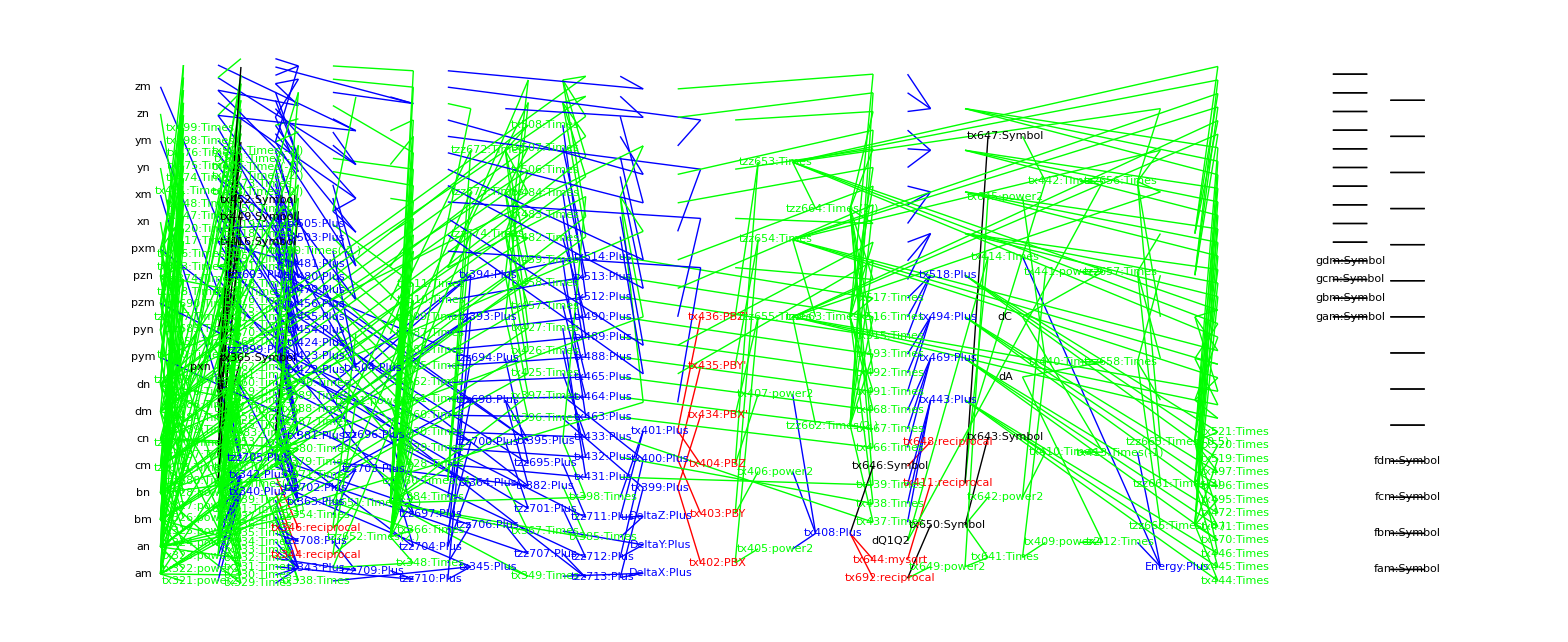

```mathematica
packGraph[nonbondRBPack]
```

## Evaluate plabk and plabl

```mathematica
plabk
```

plabk

```mathematica
plabl
```

plabl